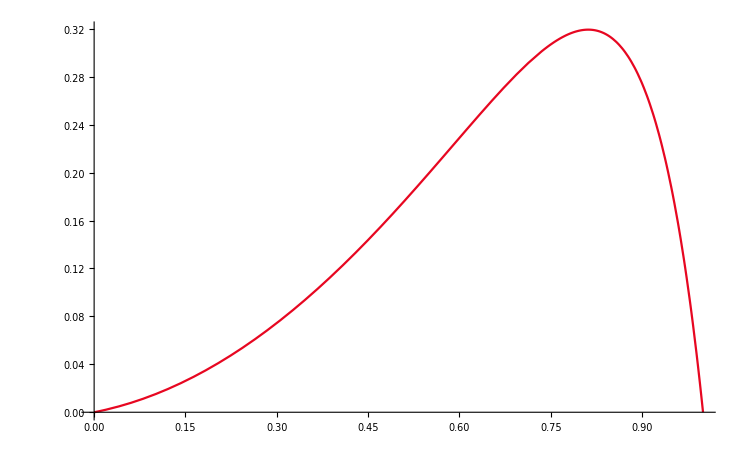

```mathematica
(*epsilon=0.1*)
img=Plot[(6 (1-ⅇ^(10 x)))/(10 (-1+ⅇ^10))+x/10+x^2/2,{x,0,1},PlotStyle->ColorData[3,"ColorList"]]
```

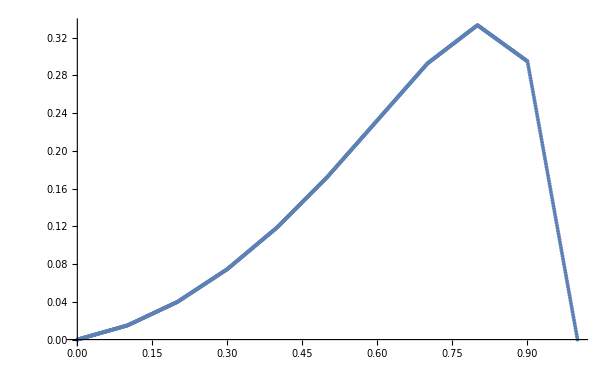
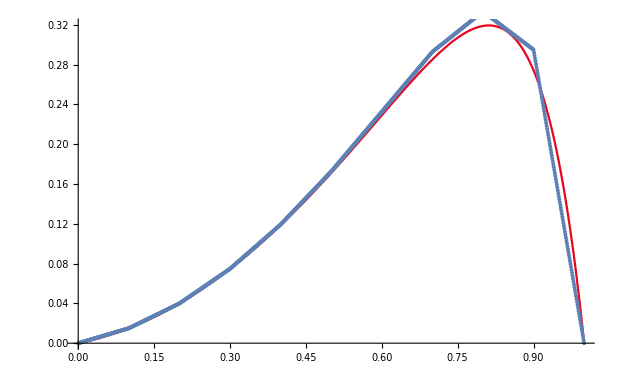
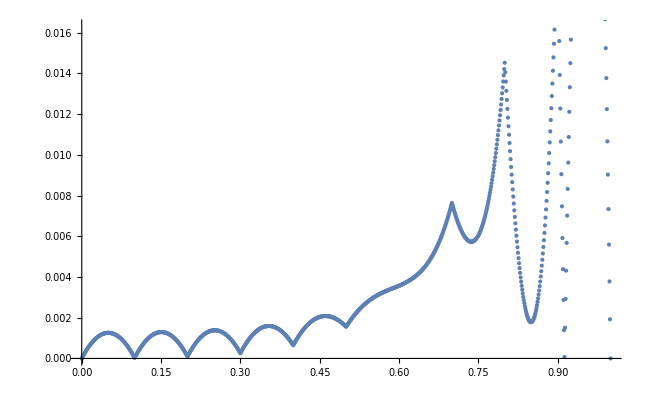

```mathematica
list={{0,0},{0.001,0.000149797},{0.002,0.000299594},{0.003,0.00044939},{0.004,0.000599187},{0.005,0.000748984},{0.006,0.000898781},{0.007,0.00104858},{0.008,0.00119837},{0.009,0.00134817},{0.01,0.00149797},{0.011,0.00164776},{0.012,0.00179756},{0.013,0.00194736},{0.014,0.00209715},{0.015,0.00224695},{0.016,0.00239675},{0.017,0.00254655},{0.018,0.00269634},{0.019,0.00284614},{0.02,0.00299594},{0.021,0.00314573},{0.022,0.00329553},{0.023,0.00344533},{0.024,0.00359512},{0.025,0.00374492},{0.026,0.00389472},{0.027,0.00404451},{0.028,0.00419431},{0.029,0.00434411},{0.03,0.0044939},{0.031,0.0046437},{0.032,0.0047935},{0.033,0.00494329},{0.034,0.00509309},{0.035,0.00524289},{0.036,0.00539268},{0.037,0.00554248},{0.038,0.00569228},{0.039,0.00584207},{0.04,0.00599187},{0.041,0.00614167},{0.042,0.00629146},{0.043,0.00644126},{0.044,0.00659106},{0.045,0.00674085},{0.046,0.00689065},{0.047,0.00704045},{0.048,0.00719025},{0.049,0.00734004},{0.05,0.00748984},{0.051,0.00763964},{0.052,0.00778943},{0.053,0.00793923},{0.054,0.00808903},{0.055,0.00823882},{0.056,0.00838862},{0.057,0.00853842},{0.058,0.00868821},{0.059,0.00883801},{0.06,0.00898781},{0.061,0.0091376},{0.062,0.0092874},{0.063,0.0094372},{0.064,0.00958699},{0.065,0.00973679},{0.066,0.00988659},{0.067,0.0100364},{0.068,0.0101862},{0.069,0.010336},{0.07,0.0104858},{0.071,0.0106356},{0.072,0.0107854},{0.073,0.0109352},{0.074,0.011085},{0.075,0.0112348},{0.076,0.0113846},{0.077,0.0115344},{0.078,0.0116841},{0.079,0.0118339},{0.08,0.0119837},{0.081,0.0121335},{0.082,0.0122833},{0.083,0.0124331},{0.084,0.0125829},{0.085,0.0127327},{0.086,0.0128825},{0.087,0.0130323},{0.088,0.0131821},{0.089,0.0133319},{0.09,0.0134817},{0.091,0.0136315},{0.092,0.0137813},{0.093,0.0139311},{0.094,0.0140809},{0.095,0.0142307},{0.096,0.0143805},{0.097,0.0145303},{0.098,0.0146801},{0.099,0.0148299},{0.1,0.0149797},{0.101,0.0152291},{0.102,0.0154785},{0.103,0.0157278},{0.104,0.0159772},{0.105,0.0162266},{0.106,0.016476},{0.107,0.0167254},{0.108,0.0169748},{0.109,0.0172242},{0.11,0.0174736},{0.111,0.017723},{0.112,0.0179724},{0.113,0.0182218},{0.114,0.0184711},{0.115,0.0187205},{0.116,0.0189699},{0.117,0.0192193},{0.118,0.0194687},{0.119,0.0197181},{0.12,0.0199675},{0.121,0.0202169},{0.122,0.0204663},{0.123,0.0207157},{0.124,0.020965},{0.125,0.0212144},{0.126,0.0214638},{0.127,0.0217132},{0.128,0.0219626},{0.129,0.022212},{0.13,0.0224614},{0.131,0.0227108},{0.132,0.0229602},{0.133,0.0232096},{0.134,0.0234589},{0.135,0.0237083},{0.136,0.0239577},{0.137,0.0242071},{0.138,0.0244565},{0.139,0.0247059},{0.14,0.0249553},{0.141,0.0252047},{0.142,0.0254541},{0.143,0.0257035},{0.144,0.0259529},{0.145,0.0262022},{0.146,0.0264516},{0.147,0.026701},{0.148,0.0269504},{0.149,0.0271998},{0.15,0.0274492},{0.151,0.0276986},{0.152,0.027948},{0.153,0.0281974},{0.154,0.0284468},{0.155,0.0286961},{0.156,0.0289455},{0.157,0.0291949},{0.158,0.0294443},{0.159,0.0296937},{0.16,0.0299431},{0.161,0.0301925},{0.162,0.0304419},{0.163,0.0306913},{0.164,0.0309407},{0.165,0.03119},{0.166,0.0314394},{0.167,0.0316888},{0.168,0.0319382},{0.169,0.0321876},{0.17,0.032437},{0.171,0.0326864},{0.172,0.0329358},{0.173,0.0331852},{0.174,0.0334346},{0.175,0.033684},{0.176,0.0339333},{0.177,0.0341827},{0.178,0.0344321},{0.179,0.0346815},{0.18,0.0349309},{0.181,0.0351803},{0.182,0.0354297},{0.183,0.0356791},{0.184,0.0359285},{0.185,0.0361779},{0.186,0.0364272},{0.187,0.0366766},{0.188,0.036926},{0.189,0.0371754},{0.19,0.0374248},{0.191,0.0376742},{0.192,0.0379236},{0.193,0.038173},{0.194,0.0384224},{0.195,0.0386718},{0.196,0.0389211},{0.197,0.0391705},{0.198,0.0394199},{0.199,0.0396693},{0.2,0.0399187},{0.201,0.0402669},{0.202,0.0406151},{0.203,0.0409632},{0.204,0.0413114},{0.205,0.0416596},{0.206,0.0420077},{0.207,0.0423559},{0.208,0.0427041},{0.209,0.0430522},{0.21,0.0434004},{0.211,0.0437486},{0.212,0.0440968},{0.213,0.0444449},{0.214,0.0447931},{0.215,0.0451413},{0.216,0.0454894},{0.217,0.0458376},{0.218,0.0461858},{0.219,0.046534},{0.22,0.0468821},{0.221,0.0472303},{0.222,0.0475785},{0.223,0.0479266},{0.224,0.0482748},{0.225,0.048623},{0.226,0.0489712},{0.227,0.0493193},{0.228,0.0496675},{0.229,0.0500157},{0.23,0.0503638},{0.231,0.050712},{0.232,0.0510602},{0.233,0.0514084},{0.234,0.0517565},{0.235,0.0521047},{0.236,0.0524529},{0.237,0.052801},{0.238,0.0531492},{0.239,0.0534974},{0.24,0.0538455},{0.241,0.0541937},{0.242,0.0545419},{0.243,0.0548901},{0.244,0.0552382},{0.245,0.0555864},{0.246,0.0559346},{0.247,0.0562827},{0.248,0.0566309},{0.249,0.0569791},{0.25,0.0573273},{0.251,0.0576754},{0.252,0.0580236},{0.253,0.0583718},{0.254,0.0587199},{0.255,0.0590681},{0.256,0.0594163},{0.257,0.0597645},{0.258,0.0601126},{0.259,0.0604608},{0.26,0.060809},{0.261,0.0611571},{0.262,0.0615053},{0.263,0.0618535},{0.264,0.0622017},{0.265,0.0625498},{0.266,0.062898},{0.267,0.0632462},{0.268,0.0635943},{0.269,0.0639425},{0.27,0.0642907},{0.271,0.0646388},{0.272,0.064987},{0.273,0.0653352},{0.274,0.0656834},{0.275,0.0660315},{0.276,0.0663797},{0.277,0.0667279},{0.278,0.067076},{0.279,0.0674242},{0.28,0.0677724},{0.281,0.0681206},{0.282,0.0684687},{0.283,0.0688169},{0.284,0.0691651},{0.285,0.0695132},{0.286,0.0698614},{0.287,0.0702096},{0.288,0.0705578},{0.289,0.0709059},{0.29,0.0712541},{0.291,0.0716023},{0.292,0.0719504},{0.293,0.0722986},{0.294,0.0726468},{0.295,0.072995},{0.296,0.0733431},{0.297,0.0736913},{0.298,0.0740395},{0.299,0.0743876},{0.3,0.0747358},{0.301,0.0751803},{0.302,0.0756248},{0.303,0.0760693},{0.304,0.0765139},{0.305,0.0769584},{0.306,0.0774029},{0.307,0.0778474},{0.308,0.0782919},{0.309,0.0787364},{0.31,0.0791809},{0.311,0.0796255},{0.312,0.08007},{0.313,0.0805145},{0.314,0.080959},{0.315,0.0814035},{0.316,0.081848},{0.317,0.0822925},{0.318,0.082737},{0.319,0.0831816},{0.32,0.0836261},{0.321,0.0840706},{0.322,0.0845151},{0.323,0.0849596},{0.324,0.0854041},{0.325,0.0858486},{0.326,0.0862931},{0.327,0.0867377},{0.328,0.0871822},{0.329,0.0876267},{0.33,0.0880712},{0.331,0.0885157},{0.332,0.0889602},{0.333,0.0894047},{0.334,0.0898492},{0.335,0.0902938},{0.336,0.0907383},{0.337,0.0911828},{0.338,0.0916273},{0.339,0.0920718},{0.34,0.0925163},{0.341,0.0929608},{0.342,0.0934054},{0.343,0.0938499},{0.344,0.0942944},{0.345,0.0947389},{0.346,0.0951834},{0.347,0.0956279},{0.348,0.0960724},{0.349,0.0965169},{0.35,0.0969615},{0.351,0.097406},{0.352,0.0978505},{0.353,0.098295},{0.354,0.0987395},{0.355,0.099184},{0.356,0.0996285},{0.357,0.100073},{0.358,0.100518},{0.359,0.100962},{0.36,0.101407},{0.361,0.101851},{0.362,0.102296},{0.363,0.10274},{0.364,0.103185},{0.365,0.103629},{0.366,0.104074},{0.367,0.104518},{0.368,0.104963},{0.369,0.105407},{0.37,0.105852},{0.371,0.106296},{0.372,0.106741},{0.373,0.107185},{0.374,0.10763},{0.375,0.108074},{0.376,0.108519},{0.377,0.108963},{0.378,0.109408},{0.379,0.109852},{0.38,0.110297},{0.381,0.110741},{0.382,0.111186},{0.383,0.11163},{0.384,0.112075},{0.385,0.112519},{0.386,0.112964},{0.387,0.113408},{0.388,0.113853},{0.389,0.114297},{0.39,0.114742},{0.391,0.115186},{0.392,0.115631},{0.393,0.116076},{0.394,0.11652},{0.395,0.116965},{0.396,0.117409},{0.397,0.117854},{0.398,0.118298},{0.399,0.118743},{0.4,0.119187},{0.401,0.119721},{0.402,0.120254},{0.403,0.120788},{0.404,0.121321},{0.405,0.121855},{0.406,0.122388},{0.407,0.122922},{0.408,0.123455},{0.409,0.123989},{0.41,0.124522},{0.411,0.125056},{0.412,0.12559},{0.413,0.126123},{0.414,0.126657},{0.415,0.12719},{0.416,0.127724},{0.417,0.128257},{0.418,0.128791},{0.419,0.129324},{0.42,0.129858},{0.421,0.130391},{0.422,0.130925},{0.423,0.131458},{0.424,0.131992},{0.425,0.132526},{0.426,0.133059},{0.427,0.133593},{0.428,0.134126},{0.429,0.13466},{0.43,0.135193},{0.431,0.135727},{0.432,0.13626},{0.433,0.136794},{0.434,0.137327},{0.435,0.137861},{0.436,0.138394},{0.437,0.138928},{0.438,0.139462},{0.439,0.139995},{0.44,0.140529},{0.441,0.141062},{0.442,0.141596},{0.443,0.142129},{0.444,0.142663},{0.445,0.143196},{0.446,0.14373},{0.447,0.144263},{0.448,0.144797},{0.449,0.145331},{0.45,0.145864},{0.451,0.146398},{0.452,0.146931},{0.453,0.147465},{0.454,0.147998},{0.455,0.148532},{0.456,0.149065},{0.457,0.149599},{0.458,0.150132},{0.459,0.150666},{0.46,0.151199},{0.461,0.151733},{0.462,0.152267},{0.463,0.1528},{0.464,0.153334},{0.465,0.153867},{0.466,0.154401},{0.467,0.154934},{0.468,0.155468},{0.469,0.156001},{0.47,0.156535},{0.471,0.157068},{0.472,0.157602},{0.473,0.158135},{0.474,0.158669},{0.475,0.159203},{0.476,0.159736},{0.477,0.16027},{0.478,0.160803},{0.479,0.161337},{0.48,0.16187},{0.481,0.162404},{0.482,0.162937},{0.483,0.163471},{0.484,0.164004},{0.485,0.164538},{0.486,0.165071},{0.487,0.165605},{0.488,0.166139},{0.489,0.166672},{0.49,0.167206},{0.491,0.167739},{0.492,0.168273},{0.493,0.168806},{0.494,0.16934},{0.495,0.169873},{0.496,0.170407},{0.497,0.17094},{0.498,0.171474},{0.499,0.172007},{0.5,0.172541},{0.501,0.173142},{0.502,0.173742},{0.503,0.174343},{0.504,0.174943},{0.505,0.175544},{0.506,0.176145},{0.507,0.176745},{0.508,0.177346},{0.509,0.177947},{0.51,0.178547},{0.511,0.179148},{0.512,0.179748},{0.513,0.180349},{0.514,0.18095},{0.515,0.18155},{0.516,0.182151},{0.517,0.182751},{0.518,0.183352},{0.519,0.183953},{0.52,0.184553},{0.521,0.185154},{0.522,0.185755},{0.523,0.186355},{0.524,0.186956},{0.525,0.187556},{0.526,0.188157},{0.527,0.188758},{0.528,0.189358},{0.529,0.189959},{0.53,0.190559},{0.531,0.19116},{0.532,0.191761},{0.533,0.192361},{0.534,0.192962},{0.535,0.193563},{0.536,0.194163},{0.537,0.194764},{0.538,0.195364},{0.539,0.195965},{0.54,0.196566},{0.541,0.197166},{0.542,0.197767},{0.543,0.198367},{0.544,0.198968},{0.545,0.199569},{0.546,0.200169},{0.547,0.20077},{0.548,0.201371},{0.549,0.201971},{0.55,0.202572},{0.551,0.203172},{0.552,0.203773},{0.553,0.204374},{0.554,0.204974},{0.555,0.205575},{0.556,0.206176},{0.557,0.206776},{0.558,0.207377},{0.559,0.207977},{0.56,0.208578},{0.561,0.209179},{0.562,0.209779},{0.563,0.21038},{0.564,0.21098},{0.565,0.211581},{0.566,0.212182},{0.567,0.212782},{0.568,0.213383},{0.569,0.213984},{0.57,0.214584},{0.571,0.215185},{0.572,0.215785},{0.573,0.216386},{0.574,0.216987},{0.575,0.217587},{0.576,0.218188},{0.577,0.218788},{0.578,0.219389},{0.579,0.21999},{0.58,0.22059},{0.581,0.221191},{0.582,0.221792},{0.583,0.222392},{0.584,0.222993},{0.585,0.223593},{0.586,0.224194},{0.587,0.224795},{0.588,0.225395},{0.589,0.225996},{0.59,0.226596},{0.591,0.227197},{0.592,0.227798},{0.593,0.228398},{0.594,0.228999},{0.595,0.2296},{0.596,0.2302},{0.597,0.230801},{0.598,0.231401},{0.599,0.232002},{0.6,0.232603},{0.601,0.233204},{0.602,0.233806},{0.603,0.234408},{0.604,0.23501},{0.605,0.235612},{0.606,0.236214},{0.607,0.236816},{0.608,0.237417},{0.609,0.238019},{0.61,0.238621},{0.611,0.239223},{0.612,0.239825},{0.613,0.240427},{0.614,0.241029},{0.615,0.24163},{0.616,0.242232},{0.617,0.242834},{0.618,0.243436},{0.619,0.244038},{0.62,0.24464},{0.621,0.245241},{0.622,0.245843},{0.623,0.246445},{0.624,0.247047},{0.625,0.247649},{0.626,0.248251},{0.627,0.248853},{0.628,0.249454},{0.629,0.250056},{0.63,0.250658},{0.631,0.25126},{0.632,0.251862},{0.633,0.252464},{0.634,0.253066},{0.635,0.253667},{0.636,0.254269},{0.637,0.254871},{0.638,0.255473},{0.639,0.256075},{0.64,0.256677},{0.641,0.257278},{0.642,0.25788},{0.643,0.258482},{0.644,0.259084},{0.645,0.259686},{0.646,0.260288},{0.647,0.26089},{0.648,0.261491},{0.649,0.262093},{0.65,0.262695},{0.651,0.263297},{0.652,0.263899},{0.653,0.264501},{0.654,0.265102},{0.655,0.265704},{0.656,0.266306},{0.657,0.266908},{0.658,0.26751},{0.659,0.268112},{0.66,0.268714},{0.661,0.269315},{0.662,0.269917},{0.663,0.270519},{0.664,0.271121},{0.665,0.271723},{0.666,0.272325},{0.667,0.272927},{0.668,0.273528},{0.669,0.27413},{0.67,0.274732},{0.671,0.275334},{0.672,0.275936},{0.673,0.276538},{0.674,0.277139},{0.675,0.277741},{0.676,0.278343},{0.677,0.278945},{0.678,0.279547},{0.679,0.280149},{0.68,0.280751},{0.681,0.281352},{0.682,0.281954},{0.683,0.282556},{0.684,0.283158},{0.685,0.28376},{0.686,0.284362},{0.687,0.284964},{0.688,0.285565},{0.689,0.286167},{0.69,0.286769},{0.691,0.287371},{0.692,0.287973},{0.693,0.288575},{0.694,0.289176},{0.695,0.289778},{0.696,0.29038},{0.697,0.290982},{0.698,0.291584},{0.699,0.292186},{0.7,0.292788},{0.701,0.293193},{0.702,0.293599},{0.703,0.294004},{0.704,0.29441},{0.705,0.294815},{0.706,0.295221},{0.707,0.295626},{0.708,0.296032},{0.709,0.296437},{0.71,0.296843},{0.711,0.297249},{0.712,0.297654},{0.713,0.29806},{0.714,0.298465},{0.715,0.298871},{0.716,0.299276},{0.717,0.299682},{0.718,0.300087},{0.719,0.300493},{0.72,0.300899},{0.721,0.301304},{0.722,0.30171},{0.723,0.302115},{0.724,0.302521},{0.725,0.302926},{0.726,0.303332},{0.727,0.303737},{0.728,0.304143},{0.729,0.304548},{0.73,0.304954},{0.731,0.30536},{0.732,0.305765},{0.733,0.306171},{0.734,0.306576},{0.735,0.306982},{0.736,0.307387},{0.737,0.307793},{0.738,0.308198},{0.739,0.308604},{0.74,0.309009},{0.741,0.309415},{0.742,0.309821},{0.743,0.310226},{0.744,0.310632},{0.745,0.311037},{0.746,0.311443},{0.747,0.311848},{0.748,0.312254},{0.749,0.312659},{0.75,0.313065},{0.751,0.313471},{0.752,0.313876},{0.753,0.314282},{0.754,0.314687},{0.755,0.315093},{0.756,0.315498},{0.757,0.315904},{0.758,0.316309},{0.759,0.316715},{0.76,0.31712},{0.761,0.317526},{0.762,0.317932},{0.763,0.318337},{0.764,0.318743},{0.765,0.319148},{0.766,0.319554},{0.767,0.319959},{0.768,0.320365},{0.769,0.32077},{0.77,0.321176},{0.771,0.321581},{0.772,0.321987},{0.773,0.322393},{0.774,0.322798},{0.775,0.323204},{0.776,0.323609},{0.777,0.324015},{0.778,0.32442},{0.779,0.324826},{0.78,0.325231},{0.781,0.325637},{0.782,0.326043},{0.783,0.326448},{0.784,0.326854},{0.785,0.327259},{0.786,0.327665},{0.787,0.32807},{0.788,0.328476},{0.789,0.328881},{0.79,0.329287},{0.791,0.329692},{0.792,0.330098},{0.793,0.330504},{0.794,0.330909},{0.795,0.331315},{0.796,0.33172},{0.797,0.332126},{0.798,0.332531},{0.799,0.332937},{0.8,0.333342},{0.801,0.332959},{0.802,0.332576},{0.803,0.332192},{0.804,0.331809},{0.805,0.331426},{0.806,0.331042},{0.807,0.330659},{0.808,0.330276},{0.809,0.329892},{0.81,0.329509},{0.811,0.329125},{0.812,0.328742},{0.813,0.328359},{0.814,0.327975},{0.815,0.327592},{0.816,0.327209},{0.817,0.326825},{0.818,0.326442},{0.819,0.326059},{0.82,0.325675},{0.821,0.325292},{0.822,0.324909},{0.823,0.324525},{0.824,0.324142},{0.825,0.323758},{0.826,0.323375},{0.827,0.322992},{0.828,0.322608},{0.829,0.322225},{0.83,0.321842},{0.831,0.321458},{0.832,0.321075},{0.833,0.320692},{0.834,0.320308},{0.835,0.319925},{0.836,0.319542},{0.837,0.319158},{0.838,0.318775},{0.839,0.318391},{0.84,0.318008},{0.841,0.317625},{0.842,0.317241},{0.843,0.316858},{0.844,0.316475},{0.845,0.316091},{0.846,0.315708},{0.847,0.315325},{0.848,0.314941},{0.849,0.314558},{0.85,0.314175},{0.851,0.313791},{0.852,0.313408},{0.853,0.313025},{0.854,0.312641},{0.855,0.312258},{0.856,0.311874},{0.857,0.311491},{0.858,0.311108},{0.859,0.310724},{0.86,0.310341},{0.861,0.309958},{0.862,0.309574},{0.863,0.309191},{0.864,0.308808},{0.865,0.308424},{0.866,0.308041},{0.867,0.307658},{0.868,0.307274},{0.869,0.306891},{0.87,0.306507},{0.871,0.306124},{0.872,0.305741},{0.873,0.305357},{0.874,0.304974},{0.875,0.304591},{0.876,0.304207},{0.877,0.303824},{0.878,0.303441},{0.879,0.303057},{0.88,0.302674},{0.881,0.302291},{0.882,0.301907},{0.883,0.301524},{0.884,0.30114},{0.885,0.300757},{0.886,0.300374},{0.887,0.29999},{0.888,0.299607},{0.889,0.299224},{0.89,0.29884},{0.891,0.298457},{0.892,0.298074},{0.893,0.29769},{0.894,0.297307},{0.895,0.296924},{0.896,0.29654},{0.897,0.296157},{0.898,0.295773},{0.899,0.29539},{0.9,0.295007},{0.901,0.292057},{0.902,0.289107},{0.903,0.286157},{0.904,0.283207},{0.905,0.280256},{0.906,0.277306},{0.907,0.274356},{0.908,0.271406},{0.909,0.268456},{0.91,0.265506},{0.911,0.262556},{0.912,0.259606},{0.913,0.256656},{0.914,0.253706},{0.915,0.250756},{0.916,0.247806},{0.917,0.244856},{0.918,0.241906},{0.919,0.238955},{0.92,0.236005},{0.921,0.233055},{0.922,0.230105},{0.923,0.227155},{0.924,0.224205},{0.925,0.221255},{0.926,0.218305},{0.927,0.215355},{0.928,0.212405},{0.929,0.209455},{0.93,0.206505},{0.931,0.203555},{0.932,0.200605},{0.933,0.197655},{0.934,0.194704},{0.935,0.191754},{0.936,0.188804},{0.937,0.185854},{0.938,0.182904},{0.939,0.179954},{0.94,0.177004},{0.941,0.174054},{0.942,0.171104},{0.943,0.168154},{0.944,0.165204},{0.945,0.162254},{0.946,0.159304},{0.947,0.156354},{0.948,0.153404},{0.949,0.150453},{0.95,0.147503},{0.951,0.144553},{0.952,0.141603},{0.953,0.138653},{0.954,0.135703},{0.955,0.132753},{0.956,0.129803},{0.957,0.126853},{0.958,0.123903},{0.959,0.120953},{0.96,0.118003},{0.961,0.115053},{0.962,0.112103},{0.963,0.109153},{0.964,0.106202},{0.965,0.103252},{0.966,0.100302},{0.967,0.0973522},{0.968,0.0944022},{0.969,0.0914521},{0.97,0.088502},{0.971,0.085552},{0.972,0.0826019},{0.973,0.0796518},{0.974,0.0767018},{0.975,0.0737517},{0.976,0.0708016},{0.977,0.0678516},{0.978,0.0649015},{0.979,0.0619514},{0.98,0.0590014},{0.981,0.0560513},{0.982,0.0531012},{0.983,0.0501512},{0.984,0.0472011},{0.985,0.044251},{0.986,0.0413009},{0.987,0.0383509},{0.988,0.0354008},{0.989,0.0324507},{0.99,0.0295007},{0.991,0.0265506},{0.992,0.0236005},{0.993,0.0206505},{0.994,0.0177004},{0.995,0.0147503},{0.996,0.0118003},{0.997,0.0088502},{0.998,0.00590014},{0.999,0.00295007},{1,0}};
error={{0,0*10^(0)},{0.001,4.95706*10^(-5)},{0.002,9.81439*10^(-5)},{0.003,1.4572*10^(-4)},{0.004,1.92299*10^(-4)},{0.005,2.37881*10^(-4)},{0.006,2.82465*10^(-4)},{0.007,3.26053*10^(-4)},{0.008,3.68643*10^(-4)},{0.009,4.10236*10^(-4)},{0.01,4.50833*10^(-4)},{0.011,4.90432*10^(-4)},{0.012,5.29034*10^(-4)},{0.013,5.6664*10^(-4)},{0.014,6.03248*10^(-4)},{0.015,6.3886*10^(-4)},{0.016,6.73475*10^(-4)},{0.017,7.07093*10^(-4)},{0.018,7.39714*10^(-4)},{0.019,7.71339*10^(-4)},{0.02,8.01967*10^(-4)},{0.021,8.31598*10^(-4)},{0.022,8.60232*10^(-4)},{0.023,8.8787*10^(-4)},{0.024,9.14512*10^(-4)},{0.025,9.40157*10^(-4)},{0.026,9.64805*10^(-4)},{0.027,9.88457*10^(-4)},{0.028,1.01111*10^(-3)},{0.029,1.03277*10^(-3)},{0.03,1.05343*10^(-3)},{0.031,1.0731*10^(-3)},{0.032,1.09177*10^(-3)},{0.033,1.10944*10^(-3)},{0.034,1.12612*10^(-3)},{0.035,1.1418*10^(-3)},{0.036,1.15649*10^(-3)},{0.037,1.17018*10^(-3)},{0.038,1.18287*10^(-3)},{0.039,1.19457*10^(-3)},{0.04,1.20527*10^(-3)},{0.041,1.21497*10^(-3)},{0.042,1.22368*10^(-3)},{0.043,1.2314*10^(-3)},{0.044,1.23811*10^(-3)},{0.045,1.24384*10^(-3)},{0.046,1.24856*10^(-3)},{0.047,1.25229*10^(-3)},{0.048,1.25503*10^(-3)},{0.049,1.25677*10^(-3)},{0.05,1.25751*10^(-3)},{0.051,1.25726*10^(-3)},{0.052,1.25601*10^(-3)},{0.053,1.25377*10^(-3)},{0.054,1.25053*10^(-3)},{0.055,1.2463*10^(-3)},{0.056,1.24107*10^(-3)},{0.057,1.23484*10^(-3)},{0.058,1.22763*10^(-3)},{0.059,1.21941*10^(-3)},{0.06,1.2102*10^(-3)},{0.061,1.2*10^(-3)},{0.062,1.1888*10^(-3)},{0.063,1.1766*10^(-3)},{0.064,1.16341*10^(-3)},{0.065,1.14923*10^(-3)},{0.066,1.13405*10^(-3)},{0.067,1.11788*10^(-3)},{0.068,1.10071*10^(-3)},{0.069,1.08255*10^(-3)},{0.07,1.06339*10^(-3)},{0.071,1.04324*10^(-3)},{0.072,1.02209*10^(-3)},{0.073,9.99951*10^(-4)},{0.074,9.76816*10^(-4)},{0.075,9.52687*10^(-4)},{0.076,9.27563*10^(-4)},{0.077,9.01445*10^(-4)},{0.078,8.74333*10^(-4)},{0.079,8.46227*10^(-4)},{0.08,8.17127*10^(-4)},{0.081,7.87033*10^(-4)},{0.082,7.55946*10^(-4)},{0.083,7.23864*10^(-4)},{0.084,6.90789*10^(-4)},{0.085,6.56719*10^(-4)},{0.086,6.21657*10^(-4)},{0.087,5.85601*10^(-4)},{0.088,5.48551*10^(-4)},{0.089,5.10508*10^(-4)},{0.09,4.71471*10^(-4)},{0.091,4.31441*10^(-4)},{0.092,3.90418*10^(-4)},{0.093,3.48402*10^(-4)},{0.094,3.05393*10^(-4)},{0.095,2.6139*10^(-4)},{0.096,2.16395*10^(-4)},{0.097,1.70407*10^(-4)},{0.098,1.23426*10^(-4)},{0.099,7.5452*10^(-5)},{0.1,2.64856*10^(-5)},{0.101,7.61201*10^(-5)},{0.102,1.24762*10^(-4)},{0.103,1.72412*10^(-4)},{0.104,2.19069*10^(-4)},{0.105,2.64734*10^(-4)},{0.106,3.09407*10^(-4)},{0.107,3.53087*10^(-4)},{0.108,3.95776*10^(-4)},{0.109,4.37472*10^(-4)},{0.11,4.78177*10^(-4)},{0.111,5.17889*10^(-4)},{0.112,5.56611*10^(-4)},{0.113,5.9434*10^(-4)},{0.114,6.31078*10^(-4)},{0.115,6.66824*10^(-4)},{0.116,7.01579*10^(-4)},{0.117,7.35343*10^(-4)},{0.118,7.68115*10^(-4)},{0.119,7.99897*10^(-4)},{0.12,8.30687*10^(-4)},{0.121,8.60486*10^(-4)},{0.122,8.89295*10^(-4)},{0.123,9.17112*10^(-4)},{0.124,9.43939*10^(-4)},{0.125,9.69776*10^(-4)},{0.126,9.94622*10^(-4)},{0.127,1.01848*10^(-3)},{0.128,1.04134*10^(-3)},{0.129,1.06322*10^(-3)},{0.13,1.0841*10^(-3)},{0.131,1.104*10^(-3)},{0.132,1.1229*10^(-3)},{0.133,1.14082*10^(-3)},{0.134,1.15774*10^(-3)},{0.135,1.17368*10^(-3)},{0.136,1.18863*10^(-3)},{0.137,1.20258*10^(-3)},{0.138,1.21555*10^(-3)},{0.139,1.22753*10^(-3)},{0.14,1.23852*10^(-3)},{0.141,1.24852*10^(-3)},{0.142,1.25753*10^(-3)},{0.143,1.26555*10^(-3)},{0.144,1.27259*10^(-3)},{0.145,1.27863*10^(-3)},{0.146,1.28369*10^(-3)},{0.147,1.28776*10^(-3)},{0.148,1.29084*10^(-3)},{0.149,1.29293*10^(-3)},{0.15,1.29404*10^(-3)},{0.151,1.29416*10^(-3)},{0.152,1.29329*10^(-3)},{0.153,1.29143*10^(-3)},{0.154,1.28858*10^(-3)},{0.155,1.28475*10^(-3)},{0.156,1.27993*10^(-3)},{0.157,1.27412*10^(-3)},{0.158,1.26733*10^(-3)},{0.159,1.25955*10^(-3)},{0.16,1.25078*10^(-3)},{0.161,1.24103*10^(-3)},{0.162,1.23029*10^(-3)},{0.163,1.21856*10^(-3)},{0.164,1.20585*10^(-3)},{0.165,1.19215*10^(-3)},{0.166,1.17747*10^(-3)},{0.167,1.1618*10^(-3)},{0.168,1.14514*10^(-3)},{0.169,1.1275*10^(-3)},{0.17,1.10888*10^(-3)},{0.171,1.08927*10^(-3)},{0.172,1.06867*10^(-3)},{0.173,1.04709*10^(-3)},{0.174,1.02452*10^(-3)},{0.175,1.00097*10^(-3)},{0.176,9.76439*10^(-4)},{0.177,9.50921*10^(-4)},{0.178,9.24418*10^(-4)},{0.179,8.96932*10^(-4)},{0.18,8.68462*10^(-4)},{0.181,8.39009*10^(-4)},{0.182,8.08572*10^(-4)},{0.183,7.77152*10^(-4)},{0.184,7.44749*10^(-4)},{0.185,7.11363*10^(-4)},{0.186,6.76995*10^(-4)},{0.187,6.41644*10^(-4)},{0.188,6.0531*10^(-4)},{0.189,5.67995*10^(-4)},{0.19,5.29697*10^(-4)},{0.191,4.90418*10^(-4)},{0.192,4.50157*10^(-4)},{0.193,4.08915*10^(-4)},{0.194,3.66692*10^(-4)},{0.195,3.23487*10^(-4)},{0.196,2.79302*10^(-4)},{0.197,2.34136*10^(-4)},{0.198,1.87989*10^(-4)},{0.199,1.40863*10^(-4)},{0.2,9.27557*10^(-5)},{0.201,1.4245*10^(-4)},{0.202,1.91164*10^(-4)},{0.203,2.38899*10^(-4)},{0.204,2.85654*10^(-4)},{0.205,3.31431*10^(-4)},{0.206,3.76228*10^(-4)},{0.207,4.20048*10^(-4)},{0.208,4.62888*10^(-4)},{0.209,5.04751*10^(-4)},{0.21,5.45635*10^(-4)},{0.211,5.85542*10^(-4)},{0.212,6.24471*10^(-4)},{0.213,6.62423*10^(-4)},{0.214,6.99398*10^(-4)},{0.215,7.35395*10^(-4)},{0.216,7.70417*10^(-4)},{0.217,8.04462*10^(-4)},{0.218,8.37531*10^(-4)},{0.219,8.69623*10^(-4)},{0.22,9.00741*10^(-4)},{0.221,9.30883*10^(-4)},{0.222,9.60049*10^(-4)},{0.223,9.88241*10^(-4)},{0.224,1.01546*10^(-3)},{0.225,1.0417*10^(-3)},{0.226,1.06697*10^(-3)},{0.227,1.09126*10^(-3)},{0.228,1.11458*10^(-3)},{0.229,1.13693*10^(-3)},{0.23,1.15831*10^(-3)},{0.231,1.17871*10^(-3)},{0.232,1.19814*10^(-3)},{0.233,1.21659*10^(-3)},{0.234,1.23408*10^(-3)},{0.235,1.25059*10^(-3)},{0.236,1.26613*10^(-3)},{0.237,1.2807*10^(-3)},{0.238,1.2943*10^(-3)},{0.239,1.30693*10^(-3)},{0.24,1.31859*10^(-3)},{0.241,1.32928*10^(-3)},{0.242,1.339*10^(-3)},{0.243,1.34775*10^(-3)},{0.244,1.35553*10^(-3)},{0.245,1.36234*10^(-3)},{0.246,1.36819*10^(-3)},{0.247,1.37306*10^(-3)},{0.248,1.37697*10^(-3)},{0.249,1.37991*10^(-3)},{0.25,1.38188*10^(-3)},{0.251,1.38289*10^(-3)},{0.252,1.38293*10^(-3)},{0.253,1.382*10^(-3)},{0.254,1.38011*10^(-3)},{0.255,1.37725*10^(-3)},{0.256,1.37343*10^(-3)},{0.257,1.36864*10^(-3)},{0.258,1.36289*10^(-3)},{0.259,1.35618*10^(-3)},{0.26,1.3485*10^(-3)},{0.261,1.33985*10^(-3)},{0.262,1.33025*10^(-3)},{0.263,1.31968*10^(-3)},{0.264,1.30815*10^(-3)},{0.265,1.29566*10^(-3)},{0.266,1.2822*10^(-3)},{0.267,1.26779*10^(-3)},{0.268,1.25241*10^(-3)},{0.269,1.23608*10^(-3)},{0.27,1.21878*10^(-3)},{0.271,1.20052*10^(-3)},{0.272,1.18131*10^(-3)},{0.273,1.16114*10^(-3)},{0.274,1.14001*10^(-3)},{0.275,1.11792*10^(-3)},{0.276,1.09487*10^(-3)},{0.277,1.07087*10^(-3)},{0.278,1.04591*10^(-3)},{0.279,1.01999*10^(-3)},{0.28,9.93119*10^(-4)},{0.281,9.65292*10^(-4)},{0.282,9.36511*10^(-4)},{0.283,9.06775*10^(-4)},{0.284,8.76085*10^(-4)},{0.285,8.44442*10^(-4)},{0.286,8.11846*10^(-4)},{0.287,7.78298*10^(-4)},{0.288,7.43797*10^(-4)},{0.289,7.08345*10^(-4)},{0.29,6.71943*10^(-4)},{0.291,6.34589*10^(-4)},{0.292,5.96286*10^(-4)},{0.293,5.57033*10^(-4)},{0.294,5.16831*10^(-4)},{0.295,4.75681*10^(-4)},{0.296,4.33583*10^(-4)},{0.297,3.90537*10^(-4)},{0.298,3.46545*10^(-4)},{0.299,3.01606*10^(-4)},{0.3,2.55721*10^(-4)},{0.301,3.05233*10^(-4)},{0.302,3.538*10^(-4)},{0.303,4.01423*10^(-4)},{0.304,4.48103*10^(-4)},{0.305,4.93839*10^(-4)},{0.306,5.38633*10^(-4)},{0.307,5.82485*10^(-4)},{0.308,6.25395*10^(-4)},{0.309,6.67365*10^(-4)},{0.31,7.08395*10^(-4)},{0.311,7.48485*10^(-4)},{0.312,7.87637*10^(-4)},{0.313,8.2585*10^(-4)},{0.314,8.63125*10^(-4)},{0.315,8.99463*10^(-4)},{0.316,9.34865*10^(-4)},{0.317,9.69331*10^(-4)},{0.318,1.00286*10^(-3)},{0.319,1.03546*10^(-3)},{0.32,1.06712*10^(-3)},{0.321,1.09785*10^(-3)},{0.322,1.12765*10^(-3)},{0.323,1.15651*10^(-3)},{0.324,1.18445*10^(-3)},{0.325,1.21145*10^(-3)},{0.326,1.23752*10^(-3)},{0.327,1.26267*10^(-3)},{0.328,1.28689*10^(-3)},{0.329,1.31017*10^(-3)},{0.33,1.33254*10^(-3)},{0.331,1.35397*10^(-3)},{0.332,1.37448*10^(-3)},{0.333,1.39407*10^(-3)},{0.334,1.41273*10^(-3)},{0.335,1.43047*10^(-3)},{0.336,1.44728*10^(-3)},{0.337,1.46318*10^(-3)},{0.338,1.47815*10^(-3)},{0.339,1.49221*10^(-3)},{0.34,1.50534*10^(-3)},{0.341,1.51756*10^(-3)},{0.342,1.52886*10^(-3)},{0.343,1.53924*10^(-3)},{0.344,1.54871*10^(-3)},{0.345,1.55726*10^(-3)},{0.346,1.56489*10^(-3)},{0.347,1.57162*10^(-3)},{0.348,1.57743*10^(-3)},{0.349,1.58233*10^(-3)},{0.35,1.58632*10^(-3)},{0.351,1.5894*10^(-3)},{0.352,1.59157*10^(-3)},{0.353,1.59283*10^(-3)},{0.354,1.59319*10^(-3)},{0.355,1.59263*10^(-3)},{0.356,1.59118*10^(-3)},{0.357,1.58882*10^(-3)},{0.358,1.58556*10^(-3)},{0.359,1.58139*10^(-3)},{0.36,1.57632*10^(-3)},{0.361,1.57036*10^(-3)},{0.362,1.56349*10^(-3)},{0.363,1.55572*10^(-3)},{0.364,1.54706*10^(-3)},{0.365,1.5375*10^(-3)},{0.366,1.52705*10^(-3)},{0.367,1.5157*10^(-3)},{0.368,1.50346*10^(-3)},{0.369,1.49033*10^(-3)},{0.37,1.47631*10^(-3)},{0.371,1.46139*10^(-3)},{0.372,1.44559*10^(-3)},{0.373,1.4289*10^(-3)},{0.374,1.41132*10^(-3)},{0.375,1.39286*10^(-3)},{0.376,1.37352*10^(-3)},{0.377,1.35329*10^(-3)},{0.378,1.33218*10^(-3)},{0.379,1.31019*10^(-3)},{0.38,1.28732*10^(-3)},{0.381,1.26357*10^(-3)},{0.382,1.23894*10^(-3)},{0.383,1.21344*10^(-3)},{0.384,1.18706*10^(-3)},{0.385,1.15981*10^(-3)},{0.386,1.13169*10^(-3)},{0.387,1.1027*10^(-3)},{0.388,1.07284*10^(-3)},{0.389,1.04211*10^(-3)},{0.39,1.01051*10^(-3)},{0.391,9.78051*10^(-4)},{0.392,9.44726*10^(-4)},{0.393,9.10537*10^(-4)},{0.394,8.75487*10^(-4)},{0.395,8.39578*10^(-4)},{0.396,8.02809*10^(-4)},{0.397,7.65184*10^(-4)},{0.398,7.26703*10^(-4)},{0.399,6.87368*10^(-4)},{0.4,6.4718*10^(-4)},{0.401,6.95166*10^(-4)},{0.402,7.42303*10^(-4)},{0.403,7.88592*10^(-4)},{0.404,8.34034*10^(-4)},{0.405,8.7863*10^(-4)},{0.406,9.22383*10^(-4)},{0.407,9.65294*10^(-4)},{0.408,1.00736*10^(-3)},{0.409,1.0486*10^(-3)},{0.41,1.08899*10^(-3)},{0.411,1.12855*10^(-3)},{0.412,1.16727*10^(-3)},{0.413,1.20517*10^(-3)},{0.414,1.24223*10^(-3)},{0.415,1.27846*10^(-3)},{0.416,1.31387*10^(-3)},{0.417,1.34845*10^(-3)},{0.418,1.3822*10^(-3)},{0.419,1.41514*10^(-3)},{0.42,1.44725*10^(-3)},{0.421,1.47855*10^(-3)},{0.422,1.50903*10^(-3)},{0.423,1.53869*10^(-3)},{0.424,1.56755*10^(-3)},{0.425,1.59559*10^(-3)},{0.426,1.62282*10^(-3)},{0.427,1.64924*10^(-3)},{0.428,1.67486*10^(-3)},{0.429,1.69968*10^(-3)},{0.43,1.7237*10^(-3)},{0.431,1.74691*10^(-3)},{0.432,1.76933*10^(-3)},{0.433,1.79095*10^(-3)},{0.434,1.81179*10^(-3)},{0.435,1.83183*10^(-3)},{0.436,1.85108*10^(-3)},{0.437,1.86954*10^(-3)},{0.438,1.88722*10^(-3)},{0.439,1.90412*10^(-3)},{0.44,1.92023*10^(-3)},{0.441,1.93557*10^(-3)},{0.442,1.95013*10^(-3)},{0.443,1.96392*10^(-3)},{0.444,1.97694*10^(-3)},{0.445,1.98919*10^(-3)},{0.446,2.00067*10^(-3)},{0.447,2.01139*10^(-3)},{0.448,2.02134*10^(-3)},{0.449,2.03054*10^(-3)},{0.45,2.03898*10^(-3)},{0.451,2.04666*10^(-3)},{0.452,2.05359*10^(-3)},{0.453,2.05977*10^(-3)},{0.454,2.06521*10^(-3)},{0.455,2.0699*10^(-3)},{0.456,2.07384*10^(-3)},{0.457,2.07705*10^(-3)},{0.458,2.07952*10^(-3)},{0.459,2.08126*10^(-3)},{0.46,2.08226*10^(-3)},{0.461,2.08254*10^(-3)},{0.462,2.08209*10^(-3)},{0.463,2.08091*10^(-3)},{0.464,2.07902*10^(-3)},{0.465,2.0764*10^(-3)},{0.466,2.07308*10^(-3)},{0.467,2.06904*10^(-3)},{0.468,2.06429*10^(-3)},{0.469,2.05883*10^(-3)},{0.47,2.05267*10^(-3)},{0.471,2.04581*10^(-3)},{0.472,2.03825*10^(-3)},{0.473,2.03*10^(-3)},{0.474,2.02106*10^(-3)},{0.475,2.01143*10^(-3)},{0.476,2.00111*10^(-3)},{0.477,1.99011*10^(-3)},{0.478,1.97843*10^(-3)},{0.479,1.96608*10^(-3)},{0.48,1.95306*10^(-3)},{0.481,1.93936*10^(-3)},{0.482,1.925*10^(-3)},{0.483,1.90998*10^(-3)},{0.484,1.8943*10^(-3)},{0.485,1.87796*10^(-3)},{0.486,1.86097*10^(-3)},{0.487,1.84334*10^(-3)},{0.488,1.82505*10^(-3)},{0.489,1.80613*10^(-3)},{0.49,1.78657*10^(-3)},{0.491,1.76637*10^(-3)},{0.492,1.74555*10^(-3)},{0.493,1.72409*10^(-3)},{0.494,1.70202*10^(-3)},{0.495,1.67932*10^(-3)},{0.496,1.65601*10^(-3)},{0.497,1.63209*10^(-3)},{0.498,1.60756*10^(-3)},{0.499,1.58243*10^(-3)},{0.5,1.55669*10^(-3)},{0.501,1.59744*10^(-3)},{0.502,1.6376*10^(-3)},{0.503,1.67717*10^(-3)},{0.504,1.71616*10^(-3)},{0.505,1.75456*10^(-3)},{0.506,1.7924*10^(-3)},{0.507,1.82966*10^(-3)},{0.508,1.86635*10^(-3)},{0.509,1.90248*10^(-3)},{0.51,1.93806*10^(-3)},{0.511,1.97308*10^(-3)},{0.512,2.00756*10^(-3)},{0.513,2.04148*10^(-3)},{0.514,2.07487*10^(-3)},{0.515,2.10773*10^(-3)},{0.516,2.14005*10^(-3)},{0.517,2.17185*10^(-3)},{0.518,2.20313*10^(-3)},{0.519,2.23389*10^(-3)},{0.52,2.26414*10^(-3)},{0.521,2.29389*10^(-3)},{0.522,2.32313*10^(-3)},{0.523,2.35188*10^(-3)},{0.524,2.38014*10^(-3)},{0.525,2.40791*10^(-3)},{0.526,2.4352*10^(-3)},{0.527,2.46201*10^(-3)},{0.528,2.48835*10^(-3)},{0.529,2.51423*10^(-3)},{0.53,2.53965*10^(-3)},{0.531,2.56461*10^(-3)},{0.532,2.58913*10^(-3)},{0.533,2.6132*10^(-3)},{0.534,2.63684*10^(-3)},{0.535,2.66004*10^(-3)},{0.536,2.68282*10^(-3)},{0.537,2.70517*10^(-3)},{0.538,2.72711*10^(-3)},{0.539,2.74865*10^(-3)},{0.54,2.76978*10^(-3)},{0.541,2.79051*10^(-3)},{0.542,2.81085*10^(-3)},{0.543,2.83081*10^(-3)},{0.544,2.85039*10^(-3)},{0.545,2.86959*10^(-3)},{0.546,2.88843*10^(-3)},{0.547,2.90691*10^(-3)},{0.548,2.92504*10^(-3)},{0.549,2.94282*10^(-3)},{0.55,2.96027*10^(-3)},{0.551,2.97737*10^(-3)},{0.552,2.99415*10^(-3)},{0.553,3.01062*10^(-3)},{0.554,3.02676*10^(-3)},{0.555,3.04261*10^(-3)},{0.556,3.05815*10^(-3)},{0.557,3.0734*10^(-3)},{0.558,3.08836*10^(-3)},{0.559,3.10305*10^(-3)},{0.56,3.11747*10^(-3)},{0.561,3.13162*10^(-3)},{0.562,3.14552*10^(-3)},{0.563,3.15917*10^(-3)},{0.564,3.17258*10^(-3)},{0.565,3.18575*10^(-3)},{0.566,3.1987*10^(-3)},{0.567,3.21143*10^(-3)},{0.568,3.22395*10^(-3)},{0.569,3.23627*10^(-3)},{0.57,3.2484*10^(-3)},{0.571,3.26034*10^(-3)},{0.572,3.2721*10^(-3)},{0.573,3.28369*10^(-3)},{0.574,3.29513*10^(-3)},{0.575,3.3064*10^(-3)},{0.576,3.31754*10^(-3)},{0.577,3.32854*10^(-3)},{0.578,3.33941*10^(-3)},{0.579,3.35017*10^(-3)},{0.58,3.36081*10^(-3)},{0.581,3.37136*10^(-3)},{0.582,3.38181*10^(-3)},{0.583,3.39218*10^(-3)},{0.584,3.40248*10^(-3)},{0.585,3.41272*10^(-3)},{0.586,3.4229*10^(-3)},{0.587,3.43304*10^(-3)},{0.588,3.44314*10^(-3)},{0.589,3.45322*10^(-3)},{0.59,3.46328*10^(-3)},{0.591,3.47334*10^(-3)},{0.592,3.4834*10^(-3)},{0.593,3.49347*10^(-3)},{0.594,3.50357*10^(-3)},{0.595,3.5137*10^(-3)},{0.596,3.52388*10^(-3)},{0.597,3.53412*10^(-3)},{0.598,3.54442*10^(-3)},{0.599,3.5548*10^(-3)},{0.6,3.56527*10^(-3)},{0.601,3.57707*10^(-3)},{0.602,3.58898*10^(-3)},{0.603,3.60101*10^(-3)},{0.604,3.61317*10^(-3)},{0.605,3.62548*10^(-3)},{0.606,3.63794*10^(-3)},{0.607,3.65057*10^(-3)},{0.608,3.66338*10^(-3)},{0.609,3.67638*10^(-3)},{0.61,3.68958*10^(-3)},{0.611,3.70299*10^(-3)},{0.612,3.71664*10^(-3)},{0.613,3.73052*10^(-3)},{0.614,3.74465*10^(-3)},{0.615,3.75905*10^(-3)},{0.616,3.77372*10^(-3)},{0.617,3.78869*10^(-3)},{0.618,3.80395*10^(-3)},{0.619,3.81954*10^(-3)},{0.62,3.83545*10^(-3)},{0.621,3.8517*10^(-3)},{0.622,3.86831*10^(-3)},{0.623,3.88529*10^(-3)},{0.624,3.90265*10^(-3)},{0.625,3.92041*10^(-3)},{0.626,3.93858*10^(-3)},{0.627,3.95717*10^(-3)},{0.628,3.97621*10^(-3)},{0.629,3.9957*10^(-3)},{0.63,4.01566*10^(-3)},{0.631,4.0361*10^(-3)},{0.632,4.05704*10^(-3)},{0.633,4.07849*10^(-3)},{0.634,4.10047*10^(-3)},{0.635,4.123*10^(-3)},{0.636,4.14609*10^(-3)},{0.637,4.16975*10^(-3)},{0.638,4.194*10^(-3)},{0.639,4.21886*10^(-3)},{0.64,4.24434*10^(-3)},{0.641,4.27046*10^(-3)},{0.642,4.29724*10^(-3)},{0.643,4.32469*10^(-3)},{0.644,4.35283*10^(-3)},{0.645,4.38167*10^(-3)},{0.646,4.41124*10^(-3)},{0.647,4.44155*10^(-3)},{0.648,4.47262*10^(-3)},{0.649,4.50447*10^(-3)},{0.65,4.53711*10^(-3)},{0.651,4.57056*10^(-3)},{0.652,4.60484*10^(-3)},{0.653,4.63997*10^(-3)},{0.654,4.67597*10^(-3)},{0.655,4.71285*10^(-3)},{0.656,4.75064*10^(-3)},{0.657,4.78935*10^(-3)},{0.658,4.829*10^(-3)},{0.659,4.86962*10^(-3)},{0.66,4.91122*10^(-3)},{0.661,4.95382*10^(-3)},{0.662,4.99745*10^(-3)},{0.663,5.04211*10^(-3)},{0.664,5.08785*10^(-3)},{0.665,5.13466*10^(-3)},{0.666,5.18258*10^(-3)},{0.667,5.23163*10^(-3)},{0.668,5.28183*10^(-3)},{0.669,5.33319*10^(-3)},{0.67,5.38575*10^(-3)},{0.671,5.43951*10^(-3)},{0.672,5.49452*10^(-3)},{0.673,5.55078*10^(-3)},{0.674,5.60832*10^(-3)},{0.675,5.66717*10^(-3)},{0.676,5.72734*10^(-3)},{0.677,5.78886*10^(-3)},{0.678,5.85176*10^(-3)},{0.679,5.91605*10^(-3)},{0.68,5.98177*10^(-3)},{0.681,6.04893*10^(-3)},{0.682,6.11756*10^(-3)},{0.683,6.18769*10^(-3)},{0.684,6.25933*10^(-3)},{0.685,6.33252*10^(-3)},{0.686,6.40729*10^(-3)},{0.687,6.48365*10^(-3)},{0.688,6.56163*10^(-3)},{0.689,6.64127*10^(-3)},{0.69,6.72258*10^(-3)},{0.691,6.80559*10^(-3)},{0.692,6.89033*10^(-3)},{0.693,6.97683*10^(-3)},{0.694,7.06512*10^(-3)},{0.695,7.15522*10^(-3)},{0.696,7.24716*10^(-3)},{0.697,7.34097*10^(-3)},{0.698,7.43668*10^(-3)},{0.699,7.53432*10^(-3)},{0.7,7.63392*10^(-3)},{0.701,7.5392*10^(-3)},{0.702,7.4465*10^(-3)},{0.703,7.35585*10^(-3)},{0.704,7.26728*10^(-3)},{0.705,7.18081*10^(-3)},{0.706,7.09649*10^(-3)},{0.707,7.01434*10^(-3)},{0.708,6.93439*10^(-3)},{0.709,6.85668*10^(-3)},{0.71,6.78123*10^(-3)},{0.711,6.70809*10^(-3)},{0.712,6.63728*10^(-3)},{0.713,6.56885*10^(-3)},{0.714,6.50281*10^(-3)},{0.715,6.43921*10^(-3)},{0.716,6.37808*10^(-3)},{0.717,6.31946*10^(-3)},{0.718,6.26338*10^(-3)},{0.719,6.20987*10^(-3)},{0.72,6.15898*10^(-3)},{0.721,6.11073*10^(-3)},{0.722,6.06517*10^(-3)},{0.723,6.02234*10^(-3)},{0.724,5.98226*10^(-3)},{0.725,5.94498*10^(-3)},{0.726,5.91054*10^(-3)},{0.727,5.87897*10^(-3)},{0.728,5.85031*10^(-3)},{0.729,5.82461*10^(-3)},{0.73,5.8019*10^(-3)},{0.731,5.78222*10^(-3)},{0.732,5.76562*10^(-3)},{0.733,5.75213*10^(-3)},{0.734,5.74179*10^(-3)},{0.735,5.73465*10^(-3)},{0.736,5.73076*10^(-3)},{0.737,5.73014*10^(-3)},{0.738,5.73285*10^(-3)},{0.739,5.73892*10^(-3)},{0.74,5.74841*10^(-3)},{0.741,5.76136*10^(-3)},{0.742,5.77781*10^(-3)},{0.743,5.7978*10^(-3)},{0.744,5.82138*10^(-3)},{0.745,5.84861*10^(-3)},{0.746,5.87952*10^(-3)},{0.747,5.91416*10^(-3)},{0.748,5.95258*10^(-3)},{0.749,5.99483*10^(-3)},{0.75,6.04096*10^(-3)},{0.751,6.09101*10^(-3)},{0.752,6.14504*10^(-3)},{0.753,6.20309*10^(-3)},{0.754,6.26521*10^(-3)},{0.755,6.33147*10^(-3)},{0.756,6.4019*10^(-3)},{0.757,6.47656*10^(-3)},{0.758,6.5555*10^(-3)},{0.759,6.63878*10^(-3)},{0.76,6.72645*10^(-3)},{0.761,6.81856*10^(-3)},{0.762,6.91517*10^(-3)},{0.763,7.01633*10^(-3)},{0.764,7.1221*10^(-3)},{0.765,7.23254*10^(-3)},{0.766,7.3477*10^(-3)},{0.767,7.46764*10^(-3)},{0.768,7.59242*10^(-3)},{0.769,7.72209*10^(-3)},{0.77,7.85672*10^(-3)},{0.771,7.99637*10^(-3)},{0.772,8.14109*10^(-3)},{0.773,8.29095*10^(-3)},{0.774,8.44601*10^(-3)},{0.775,8.60633*10^(-3)},{0.776,8.77197*10^(-3)},{0.777,8.94301*10^(-3)},{0.778,9.11949*10^(-3)},{0.779,9.30149*10^(-3)},{0.78,9.48908*10^(-3)},{0.781,9.68231*10^(-3)},{0.782,9.88126*10^(-3)},{0.783,1.0086*10^(-2)},{0.784,1.02966*10^(-2)},{0.785,1.05131*10^(-2)},{0.786,1.07356*10^(-2)},{0.787,1.09641*10^(-2)},{0.788,1.11988*10^(-2)},{0.789,1.14397*10^(-2)},{0.79,1.16868*10^(-2)},{0.791,1.19403*10^(-2)},{0.792,1.22003*10^(-2)},{0.793,1.24667*10^(-2)},{0.794,1.27397*10^(-2)},{0.795,1.30193*10^(-2)},{0.796,1.33057*10^(-2)},{0.797,1.35989*10^(-2)},{0.798,1.38989*10^(-2)},{0.799,1.42059*10^(-2)},{0.8,1.452*10^(-2)},{0.801,1.40522*10^(-2)},{0.802,1.35917*10^(-2)},{0.803,1.31385*10^(-2)},{0.804,1.26926*10^(-2)},{0.805,1.22542*10^(-2)},{0.806,1.18233*10^(-2)},{0.807,1.14*10^(-2)},{0.808,1.09844*10^(-2)},{0.809,1.05767*10^(-2)},{0.81,1.01768*10^(-2)},{0.811,9.78491*10^(-3)},{0.812,9.40107*10^(-3)},{0.813,9.02539*10^(-3)},{0.814,8.65796*10^(-3)},{0.815,8.29887*10^(-3)},{0.816,7.94821*10^(-3)},{0.817,7.60608*10^(-3)},{0.818,7.27258*10^(-3)},{0.819,6.9478*10^(-3)},{0.82,6.63184*10^(-3)},{0.821,6.3248*10^(-3)},{0.822,6.02678*10^(-3)},{0.823,5.73787*10^(-3)},{0.824,5.45819*10^(-3)},{0.825,5.18783*10^(-3)},{0.826,4.92689*10^(-3)},{0.827,4.67549*10^(-3)},{0.828,4.43373*10^(-3)},{0.829,4.20171*10^(-3)},{0.83,3.97954*10^(-3)},{0.831,3.76733*10^(-3)},{0.832,3.5652*10^(-3)},{0.833,3.37325*10^(-3)},{0.834,3.19159*10^(-3)},{0.835,3.02034*10^(-3)},{0.836,2.85962*10^(-3)},{0.837,2.70954*10^(-3)},{0.838,2.57021*10^(-3)},{0.839,2.44176*10^(-3)},{0.84,2.3243*10^(-3)},{0.841,2.21795*10^(-3)},{0.842,2.12285*10^(-3)},{0.843,2.0391*10^(-3)},{0.844,1.96683*10^(-3)},{0.845,1.90617*10^(-3)},{0.846,1.85725*10^(-3)},{0.847,1.8202*10^(-3)},{0.848,1.79513*10^(-3)},{0.849,1.78219*10^(-3)},{0.85,1.7815*10^(-3)},{0.851,1.79321*10^(-3)},{0.852,1.81743*10^(-3)},{0.853,1.85432*10^(-3)},{0.854,1.904*10^(-3)},{0.855,1.96661*10^(-3)},{0.856,2.0423*10^(-3)},{0.857,2.13121*10^(-3)},{0.858,2.23348*10^(-3)},{0.859,2.34925*10^(-3)},{0.86,2.47867*10^(-3)},{0.861,2.62188*10^(-3)},{0.862,2.77904*10^(-3)},{0.863,2.9503*10^(-3)},{0.864,3.1358*10^(-3)},{0.865,3.33571*10^(-3)},{0.866,3.55017*10^(-3)},{0.867,3.77934*10^(-3)},{0.868,4.02338*10^(-3)},{0.869,4.28245*10^(-3)},{0.87,4.55671*10^(-3)},{0.871,4.84632*10^(-3)},{0.872,5.15145*10^(-3)},{0.873,5.47227*10^(-3)},{0.874,5.80893*10^(-3)},{0.875,6.16161*10^(-3)},{0.876,6.53049*10^(-3)},{0.877,6.91573*10^(-3)},{0.878,7.31751*10^(-3)},{0.879,7.736*10^(-3)},{0.88,8.17138*10^(-3)},{0.881,8.62384*10^(-3)},{0.882,9.09355*10^(-3)},{0.883,9.5807*10^(-3)},{0.884,1.00855*10^(-2)},{0.885,1.06081*10^(-2)},{0.886,1.11486*10^(-2)},{0.887,1.17074*10^(-2)},{0.888,1.22846*10^(-2)},{0.889,1.28803*10^(-2)},{0.89,1.34948*10^(-2)},{0.891,1.41283*10^(-2)},{0.892,1.47809*10^(-2)},{0.893,1.5453*10^(-2)},{0.894,1.61446*10^(-2)},{0.895,1.6856*10^(-2)},{0.896,1.75874*10^(-2)},{0.897,1.8339*10^(-2)},{0.898,1.9111*10^(-2)},{0.899,1.99037*10^(-2)},{0.9,2.07172*10^(-2)},{0.901,1.89851*10^(-2)},{0.902,1.72743*10^(-2)},{0.903,1.5585*10^(-2)},{0.904,1.39174*10^(-2)},{0.905,1.22718*10^(-2)},{0.906,1.06485*10^(-2)},{0.907,9.04753*10^(-3)},{0.908,7.46927*10^(-3)},{0.909,5.91392*10^(-3)},{0.91,4.38173*10^(-3)},{0.911,2.87293*10^(-3)},{0.912,1.38777*10^(-3)},{0.913,7.35054*10^(-5)},{0.914,1.51064*10^(-3)},{0.915,2.92338*10^(-3)},{0.916,4.31148*10^(-3)},{0.917,5.67467*10^(-3)},{0.918,7.0127*10^(-3)},{0.919,8.3253*10^(-3)},{0.92,9.6122*10^(-3)},{0.921,1.08731*10^(-2)},{0.922,1.21079*10^(-2)},{0.923,1.33161*10^(-2)},{0.924,1.44975*10^(-2)},{0.925,1.56519*10^(-2)},{0.926,1.67789*10^(-2)},{0.927,1.78783*10^(-2)},{0.928,1.89498*10^(-2)},{0.929,1.9993*10^(-2)},{0.93,2.10078*10^(-2)},{0.931,2.19938*10^(-2)},{0.932,2.29506*10^(-2)},{0.933,2.38781*10^(-2)},{0.934,2.47759*10^(-2)},{0.935,2.56437*10^(-2)},{0.936,2.64811*10^(-2)},{0.937,2.72879*10^(-2)},{0.938,2.80637*10^(-2)},{0.939,2.88083*10^(-2)},{0.94,2.95212*10^(-2)},{0.941,3.02023*10^(-2)},{0.942,3.0851*10^(-2)},{0.943,3.14672*10^(-2)},{0.944,3.20504*10^(-2)},{0.945,3.26004*10^(-2)},{0.946,3.31168*10^(-2)},{0.947,3.35991*10^(-2)},{0.948,3.40472*10^(-2)},{0.949,3.44606*10^(-2)},{0.95,3.48389*10^(-2)},{0.951,3.51819*10^(-2)},{0.952,3.54891*10^(-2)},{0.953,3.57602*10^(-2)},{0.954,3.59947*10^(-2)},{0.955,3.61924*10^(-2)},{0.956,3.63529*10^(-2)},{0.957,3.64757*10^(-2)},{0.958,3.65604*10^(-2)},{0.959,3.66067*10^(-2)},{0.96,3.66142*10^(-2)},{0.961,3.65825*10^(-2)},{0.962,3.65112*10^(-2)},{0.963,3.63998*10^(-2)},{0.964,3.6248*10^(-2)},{0.965,3.60553*10^(-2)},{0.966,3.58214*10^(-2)},{0.967,3.55457*10^(-2)},{0.968,3.52279*10^(-2)},{0.969,3.48675*10^(-2)},{0.97,3.44641*10^(-2)},{0.971,3.40173*10^(-2)},{0.972,3.35265*10^(-2)},{0.973,3.29914*10^(-2)},{0.974,3.24115*10^(-2)},{0.975,3.17864*10^(-2)},{0.976,3.11155*10^(-2)},{0.977,3.03984*10^(-2)},{0.978,2.96346*10^(-2)},{0.979,2.88237*10^(-2)},{0.98,2.79651*10^(-2)},{0.981,2.70584*10^(-2)},{0.982,2.61031*10^(-2)},{0.983,2.50987*10^(-2)},{0.984,2.40447*10^(-2)},{0.985,2.29405*10^(-2)},{0.986,2.17857*10^(-2)},{0.987,2.05797*10^(-2)},{0.988,1.9322*10^(-2)},{0.989,1.80121*10^(-2)},{0.99,1.66495*10^(-2)},{0.991,1.52335*10^(-2)},{0.992,1.37637*10^(-2)},{0.993,1.22396*10^(-2)},{0.994,1.06605*10^(-2)},{0.995,9.02584*10^(-3)},{0.996,7.33513*10^(-3)},{0.997,5.58778*10^(-3)},{0.998,3.7832*10^(-3)},{0.999,1.9208*10^(-3)},{1,2.77556*10^(-17)}};
imgtemp=ListPlot[list];
imgerror=ListPlot[error];
{imgtemp,Show[img,imgtemp],imgerror}
```

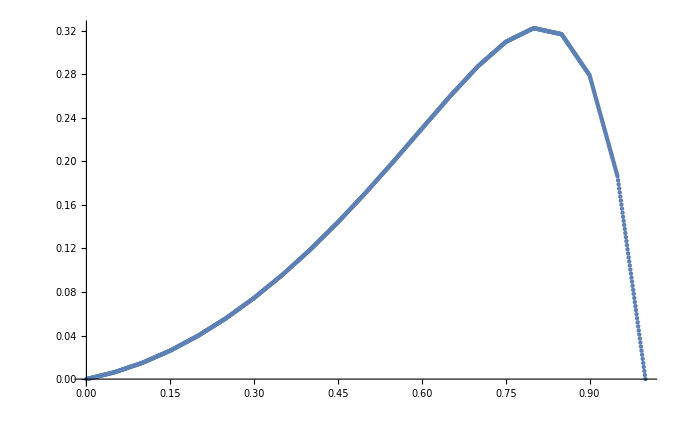
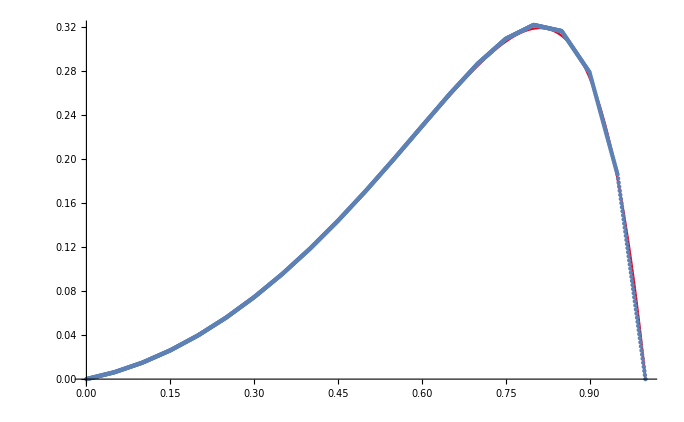
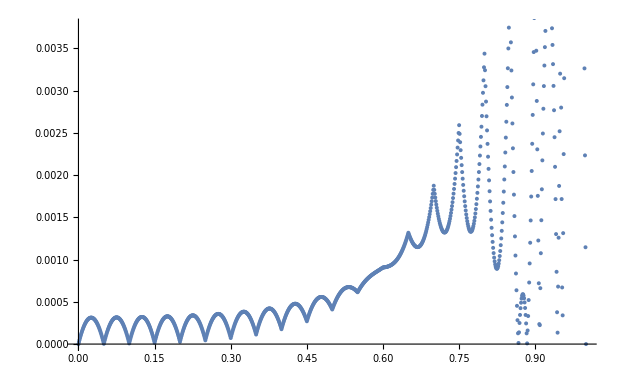

```mathematica
list={{0,0},{0.001,0.000124707},{0.002,0.000249415},{0.003,0.000374122},{0.004,0.00049883},{0.005,0.000623537},{0.006,0.000748245},{0.007,0.000872952},{0.008,0.00099766},{0.009,0.00112237},{0.01,0.00124707},{0.011,0.00137178},{0.012,0.00149649},{0.013,0.0016212},{0.014,0.0017459},{0.015,0.00187061},{0.016,0.00199532},{0.017,0.00212003},{0.018,0.00224473},{0.019,0.00236944},{0.02,0.00249415},{0.021,0.00261886},{0.022,0.00274356},{0.023,0.00286827},{0.024,0.00299298},{0.025,0.00311769},{0.026,0.00324239},{0.027,0.0033671},{0.028,0.00349181},{0.029,0.00361652},{0.03,0.00374122},{0.031,0.00386593},{0.032,0.00399064},{0.033,0.00411535},{0.034,0.00424005},{0.035,0.00436476},{0.036,0.00448947},{0.037,0.00461418},{0.038,0.00473888},{0.039,0.00486359},{0.04,0.0049883},{0.041,0.00511301},{0.042,0.00523771},{0.043,0.00536242},{0.044,0.00548713},{0.045,0.00561184},{0.046,0.00573654},{0.047,0.00586125},{0.048,0.00598596},{0.049,0.00611067},{0.05,0.00623537},{0.051,0.00640989},{0.052,0.0065844},{0.053,0.00675891},{0.054,0.00693342},{0.055,0.00710794},{0.056,0.00728245},{0.057,0.00745696},{0.058,0.00763147},{0.059,0.00780599},{0.06,0.0079805},{0.061,0.00815501},{0.062,0.00832952},{0.063,0.00850404},{0.064,0.00867855},{0.065,0.00885306},{0.066,0.00902757},{0.067,0.00920209},{0.068,0.0093766},{0.069,0.00955111},{0.07,0.00972562},{0.071,0.00990014},{0.072,0.0100746},{0.073,0.0102492},{0.074,0.0104237},{0.075,0.0105982},{0.076,0.0107727},{0.077,0.0109472},{0.078,0.0111217},{0.079,0.0112962},{0.08,0.0114707},{0.081,0.0116453},{0.082,0.0118198},{0.083,0.0119943},{0.084,0.0121688},{0.085,0.0123433},{0.086,0.0125178},{0.087,0.0126923},{0.088,0.0128668},{0.089,0.0130414},{0.09,0.0132159},{0.091,0.0133904},{0.092,0.0135649},{0.093,0.0137394},{0.094,0.0139139},{0.095,0.0140884},{0.096,0.0142629},{0.097,0.0144375},{0.098,0.014612},{0.099,0.0147865},{0.1,0.014961},{0.101,0.0151852},{0.102,0.0154094},{0.103,0.0156336},{0.104,0.0158577},{0.105,0.0160819},{0.106,0.0163061},{0.107,0.0165303},{0.108,0.0167545},{0.109,0.0169787},{0.11,0.0172029},{0.111,0.0174271},{0.112,0.0176512},{0.113,0.0178754},{0.114,0.0180996},{0.115,0.0183238},{0.116,0.018548},{0.117,0.0187722},{0.118,0.0189964},{0.119,0.0192206},{0.12,0.0194447},{0.121,0.0196689},{0.122,0.0198931},{0.123,0.0201173},{0.124,0.0203415},{0.125,0.0205657},{0.126,0.0207899},{0.127,0.0210141},{0.128,0.0212382},{0.129,0.0214624},{0.13,0.0216866},{0.131,0.0219108},{0.132,0.022135},{0.133,0.0223592},{0.134,0.0225834},{0.135,0.0228076},{0.136,0.0230317},{0.137,0.0232559},{0.138,0.0234801},{0.139,0.0237043},{0.14,0.0239285},{0.141,0.0241527},{0.142,0.0243769},{0.143,0.0246011},{0.144,0.0248252},{0.145,0.0250494},{0.146,0.0252736},{0.147,0.0254978},{0.148,0.025722},{0.149,0.0259462},{0.15,0.0261704},{0.151,0.026444},{0.152,0.0267177},{0.153,0.0269913},{0.154,0.027265},{0.155,0.0275386},{0.156,0.0278122},{0.157,0.0280859},{0.158,0.0283595},{0.159,0.0286332},{0.16,0.0289068},{0.161,0.0291805},{0.162,0.0294541},{0.163,0.0297278},{0.164,0.0300014},{0.165,0.0302751},{0.166,0.0305487},{0.167,0.0308224},{0.168,0.031096},{0.169,0.0313696},{0.17,0.0316433},{0.171,0.0319169},{0.172,0.0321906},{0.173,0.0324642},{0.174,0.0327379},{0.175,0.0330115},{0.176,0.0332852},{0.177,0.0335588},{0.178,0.0338325},{0.179,0.0341061},{0.18,0.0343797},{0.181,0.0346534},{0.182,0.034927},{0.183,0.0352007},{0.184,0.0354743},{0.185,0.035748},{0.186,0.0360216},{0.187,0.0362953},{0.188,0.0365689},{0.189,0.0368426},{0.19,0.0371162},{0.191,0.0373899},{0.192,0.0376635},{0.193,0.0379371},{0.194,0.0382108},{0.195,0.0384844},{0.196,0.0387581},{0.197,0.0390317},{0.198,0.0393054},{0.199,0.039579},{0.2,0.0398527},{0.201,0.0401754},{0.202,0.0404982},{0.203,0.0408209},{0.204,0.0411436},{0.205,0.0414664},{0.206,0.0417891},{0.207,0.0421119},{0.208,0.0424346},{0.209,0.0427574},{0.21,0.0430801},{0.211,0.0434028},{0.212,0.0437256},{0.213,0.0440483},{0.214,0.0443711},{0.215,0.0446938},{0.216,0.0450166},{0.217,0.0453393},{0.218,0.045662},{0.219,0.0459848},{0.22,0.0463075},{0.221,0.0466303},{0.222,0.046953},{0.223,0.0472758},{0.224,0.0475985},{0.225,0.0479212},{0.226,0.048244},{0.227,0.0485667},{0.228,0.0488895},{0.229,0.0492122},{0.23,0.049535},{0.231,0.0498577},{0.232,0.0501804},{0.233,0.0505032},{0.234,0.0508259},{0.235,0.0511487},{0.236,0.0514714},{0.237,0.0517942},{0.238,0.0521169},{0.239,0.0524396},{0.24,0.0527624},{0.241,0.0530851},{0.242,0.0534079},{0.243,0.0537306},{0.244,0.0540534},{0.245,0.0543761},{0.246,0.0546988},{0.247,0.0550216},{0.248,0.0553443},{0.249,0.0556671},{0.25,0.0559898},{0.251,0.0563611},{0.252,0.0567323},{0.253,0.0571035},{0.254,0.0574748},{0.255,0.057846},{0.256,0.0582172},{0.257,0.0585885},{0.258,0.0589597},{0.259,0.059331},{0.26,0.0597022},{0.261,0.0600734},{0.262,0.0604447},{0.263,0.0608159},{0.264,0.0611872},{0.265,0.0615584},{0.266,0.0619296},{0.267,0.0623009},{0.268,0.0626721},{0.269,0.0630433},{0.27,0.0634146},{0.271,0.0637858},{0.272,0.0641571},{0.273,0.0645283},{0.274,0.0648995},{0.275,0.0652708},{0.276,0.065642},{0.277,0.0660133},{0.278,0.0663845},{0.279,0.0667557},{0.28,0.067127},{0.281,0.0674982},{0.282,0.0678694},{0.283,0.0682407},{0.284,0.0686119},{0.285,0.0689832},{0.286,0.0693544},{0.287,0.0697256},{0.288,0.0700969},{0.289,0.0704681},{0.29,0.0708394},{0.291,0.0712106},{0.292,0.0715818},{0.293,0.0719531},{0.294,0.0723243},{0.295,0.0726955},{0.296,0.0730668},{0.297,0.073438},{0.298,0.0738093},{0.299,0.0741805},{0.3,0.0745517},{0.301,0.0749705},{0.302,0.0753892},{0.303,0.0758079},{0.304,0.0762267},{0.305,0.0766454},{0.306,0.0770641},{0.307,0.0774829},{0.308,0.0779016},{0.309,0.0783203},{0.31,0.078739},{0.311,0.0791578},{0.312,0.0795765},{0.313,0.0799952},{0.314,0.080414},{0.315,0.0808327},{0.316,0.0812514},{0.317,0.0816702},{0.318,0.0820889},{0.319,0.0825076},{0.32,0.0829263},{0.321,0.0833451},{0.322,0.0837638},{0.323,0.0841825},{0.324,0.0846013},{0.325,0.08502},{0.326,0.0854387},{0.327,0.0858575},{0.328,0.0862762},{0.329,0.0866949},{0.33,0.0871137},{0.331,0.0875324},{0.332,0.0879511},{0.333,0.0883698},{0.334,0.0887886},{0.335,0.0892073},{0.336,0.089626},{0.337,0.0900448},{0.338,0.0904635},{0.339,0.0908822},{0.34,0.091301},{0.341,0.0917197},{0.342,0.0921384},{0.343,0.0925572},{0.344,0.0929759},{0.345,0.0933946},{0.346,0.0938133},{0.347,0.0942321},{0.348,0.0946508},{0.349,0.0950695},{0.35,0.0954883},{0.351,0.0959528},{0.352,0.0964174},{0.353,0.0968819},{0.354,0.0973465},{0.355,0.097811},{0.356,0.0982756},{0.357,0.0987401},{0.358,0.0992047},{0.359,0.0996692},{0.36,0.100134},{0.361,0.100598},{0.362,0.101063},{0.363,0.101527},{0.364,0.101992},{0.365,0.102457},{0.366,0.102921},{0.367,0.103386},{0.368,0.10385},{0.369,0.104315},{0.37,0.104779},{0.371,0.105244},{0.372,0.105708},{0.373,0.106173},{0.374,0.106637},{0.375,0.107102},{0.376,0.107567},{0.377,0.108031},{0.378,0.108496},{0.379,0.10896},{0.38,0.109425},{0.381,0.109889},{0.382,0.110354},{0.383,0.110818},{0.384,0.111283},{0.385,0.111748},{0.386,0.112212},{0.387,0.112677},{0.388,0.113141},{0.389,0.113606},{0.39,0.11407},{0.391,0.114535},{0.392,0.114999},{0.393,0.115464},{0.394,0.115929},{0.395,0.116393},{0.396,0.116858},{0.397,0.117322},{0.398,0.117787},{0.399,0.118251},{0.4,0.118716},{0.401,0.119223},{0.402,0.119731},{0.403,0.120239},{0.404,0.120746},{0.405,0.121254},{0.406,0.121761},{0.407,0.122269},{0.408,0.122777},{0.409,0.123284},{0.41,0.123792},{0.411,0.124299},{0.412,0.124807},{0.413,0.125314},{0.414,0.125822},{0.415,0.12633},{0.416,0.126837},{0.417,0.127345},{0.418,0.127852},{0.419,0.12836},{0.42,0.128868},{0.421,0.129375},{0.422,0.129883},{0.423,0.13039},{0.424,0.130898},{0.425,0.131405},{0.426,0.131913},{0.427,0.132421},{0.428,0.132928},{0.429,0.133436},{0.43,0.133943},{0.431,0.134451},{0.432,0.134959},{0.433,0.135466},{0.434,0.135974},{0.435,0.136481},{0.436,0.136989},{0.437,0.137496},{0.438,0.138004},{0.439,0.138512},{0.44,0.139019},{0.441,0.139527},{0.442,0.140034},{0.443,0.140542},{0.444,0.14105},{0.445,0.141557},{0.446,0.142065},{0.447,0.142572},{0.448,0.14308},{0.449,0.143587},{0.45,0.144095},{0.451,0.144641},{0.452,0.145187},{0.453,0.145733},{0.454,0.146279},{0.455,0.146825},{0.456,0.147371},{0.457,0.147917},{0.458,0.148463},{0.459,0.149009},{0.46,0.149555},{0.461,0.150101},{0.462,0.150647},{0.463,0.151193},{0.464,0.151739},{0.465,0.152285},{0.466,0.152831},{0.467,0.153377},{0.468,0.153923},{0.469,0.154469},{0.47,0.155015},{0.471,0.155561},{0.472,0.156107},{0.473,0.156653},{0.474,0.157198},{0.475,0.157744},{0.476,0.15829},{0.477,0.158836},{0.478,0.159382},{0.479,0.159928},{0.48,0.160474},{0.481,0.16102},{0.482,0.161566},{0.483,0.162112},{0.484,0.162658},{0.485,0.163204},{0.486,0.16375},{0.487,0.164296},{0.488,0.164842},{0.489,0.165388},{0.49,0.165934},{0.491,0.16648},{0.492,0.167026},{0.493,0.167572},{0.494,0.168118},{0.495,0.168664},{0.496,0.16921},{0.497,0.169756},{0.498,0.170302},{0.499,0.170848},{0.5,0.171394},{0.501,0.17197},{0.502,0.172547},{0.503,0.173124},{0.504,0.1737},{0.505,0.174277},{0.506,0.174854},{0.507,0.17543},{0.508,0.176007},{0.509,0.176583},{0.51,0.17716},{0.511,0.177737},{0.512,0.178313},{0.513,0.17889},{0.514,0.179467},{0.515,0.180043},{0.516,0.18062},{0.517,0.181196},{0.518,0.181773},{0.519,0.18235},{0.52,0.182926},{0.521,0.183503},{0.522,0.18408},{0.523,0.184656},{0.524,0.185233},{0.525,0.185809},{0.526,0.186386},{0.527,0.186963},{0.528,0.187539},{0.529,0.188116},{0.53,0.188693},{0.531,0.189269},{0.532,0.189846},{0.533,0.190422},{0.534,0.190999},{0.535,0.191576},{0.536,0.192152},{0.537,0.192729},{0.538,0.193306},{0.539,0.193882},{0.54,0.194459},{0.541,0.195035},{0.542,0.195612},{0.543,0.196189},{0.544,0.196765},{0.545,0.197342},{0.546,0.197919},{0.547,0.198495},{0.548,0.199072},{0.549,0.199648},{0.55,0.200225},{0.551,0.200819},{0.552,0.201414},{0.553,0.202008},{0.554,0.202603},{0.555,0.203197},{0.556,0.203791},{0.557,0.204386},{0.558,0.20498},{0.559,0.205574},{0.56,0.206169},{0.561,0.206763},{0.562,0.207358},{0.563,0.207952},{0.564,0.208546},{0.565,0.209141},{0.566,0.209735},{0.567,0.210329},{0.568,0.210924},{0.569,0.211518},{0.57,0.212113},{0.571,0.212707},{0.572,0.213301},{0.573,0.213896},{0.574,0.21449},{0.575,0.215084},{0.576,0.215679},{0.577,0.216273},{0.578,0.216868},{0.579,0.217462},{0.58,0.218056},{0.581,0.218651},{0.582,0.219245},{0.583,0.219839},{0.584,0.220434},{0.585,0.221028},{0.586,0.221623},{0.587,0.222217},{0.588,0.222811},{0.589,0.223406},{0.59,0.224},{0.591,0.224594},{0.592,0.225189},{0.593,0.225783},{0.594,0.226378},{0.595,0.226972},{0.596,0.227566},{0.597,0.228161},{0.598,0.228755},{0.599,0.229349},{0.6,0.229944},{0.601,0.230534},{0.602,0.231125},{0.603,0.231716},{0.604,0.232306},{0.605,0.232897},{0.606,0.233488},{0.607,0.234078},{0.608,0.234669},{0.609,0.23526},{0.61,0.23585},{0.611,0.236441},{0.612,0.237031},{0.613,0.237622},{0.614,0.238213},{0.615,0.238803},{0.616,0.239394},{0.617,0.239985},{0.618,0.240575},{0.619,0.241166},{0.62,0.241756},{0.621,0.242347},{0.622,0.242938},{0.623,0.243528},{0.624,0.244119},{0.625,0.24471},{0.626,0.2453},{0.627,0.245891},{0.628,0.246481},{0.629,0.247072},{0.63,0.247663},{0.631,0.248253},{0.632,0.248844},{0.633,0.249435},{0.634,0.250025},{0.635,0.250616},{0.636,0.251206},{0.637,0.251797},{0.638,0.252388},{0.639,0.252978},{0.64,0.253569},{0.641,0.25416},{0.642,0.25475},{0.643,0.255341},{0.644,0.255931},{0.645,0.256522},{0.646,0.257113},{0.647,0.257703},{0.648,0.258294},{0.649,0.258885},{0.65,0.259475},{0.651,0.260026},{0.652,0.260577},{0.653,0.261128},{0.654,0.261679},{0.655,0.26223},{0.656,0.262781},{0.657,0.263332},{0.658,0.263884},{0.659,0.264435},{0.66,0.264986},{0.661,0.265537},{0.662,0.266088},{0.663,0.266639},{0.664,0.26719},{0.665,0.267741},{0.666,0.268292},{0.667,0.268843},{0.668,0.269394},{0.669,0.269945},{0.67,0.270496},{0.671,0.271047},{0.672,0.271598},{0.673,0.272149},{0.674,0.2727},{0.675,0.273251},{0.676,0.273802},{0.677,0.274353},{0.678,0.274904},{0.679,0.275455},{0.68,0.276006},{0.681,0.276557},{0.682,0.277109},{0.683,0.27766},{0.684,0.278211},{0.685,0.278762},{0.686,0.279313},{0.687,0.279864},{0.688,0.280415},{0.689,0.280966},{0.69,0.281517},{0.691,0.282068},{0.692,0.282619},{0.693,0.28317},{0.694,0.283721},{0.695,0.284272},{0.696,0.284823},{0.697,0.285374},{0.698,0.285925},{0.699,0.286476},{0.7,0.287027},{0.701,0.287479},{0.702,0.287931},{0.703,0.288383},{0.704,0.288834},{0.705,0.289286},{0.706,0.289738},{0.707,0.290189},{0.708,0.290641},{0.709,0.291093},{0.71,0.291545},{0.711,0.291996},{0.712,0.292448},{0.713,0.2929},{0.714,0.293352},{0.715,0.293803},{0.716,0.294255},{0.717,0.294707},{0.718,0.295159},{0.719,0.29561},{0.72,0.296062},{0.721,0.296514},{0.722,0.296966},{0.723,0.297417},{0.724,0.297869},{0.725,0.298321},{0.726,0.298773},{0.727,0.299224},{0.728,0.299676},{0.729,0.300128},{0.73,0.300579},{0.731,0.301031},{0.732,0.301483},{0.733,0.301935},{0.734,0.302386},{0.735,0.302838},{0.736,0.30329},{0.737,0.303742},{0.738,0.304193},{0.739,0.304645},{0.74,0.305097},{0.741,0.305549},{0.742,0.306},{0.743,0.306452},{0.744,0.306904},{0.745,0.307356},{0.746,0.307807},{0.747,0.308259},{0.748,0.308711},{0.749,0.309162},{0.75,0.309614},{0.751,0.309867},{0.752,0.31012},{0.753,0.310373},{0.754,0.310626},{0.755,0.310879},{0.756,0.311132},{0.757,0.311385},{0.758,0.311637},{0.759,0.31189},{0.76,0.312143},{0.761,0.312396},{0.762,0.312649},{0.763,0.312902},{0.764,0.313155},{0.765,0.313408},{0.766,0.313661},{0.767,0.313913},{0.768,0.314166},{0.769,0.314419},{0.77,0.314672},{0.771,0.314925},{0.772,0.315178},{0.773,0.315431},{0.774,0.315684},{0.775,0.315937},{0.776,0.31619},{0.777,0.316442},{0.778,0.316695},{0.779,0.316948},{0.78,0.317201},{0.781,0.317454},{0.782,0.317707},{0.783,0.31796},{0.784,0.318213},{0.785,0.318466},{0.786,0.318719},{0.787,0.318971},{0.788,0.319224},{0.789,0.319477},{0.79,0.31973},{0.791,0.319983},{0.792,0.320236},{0.793,0.320489},{0.794,0.320742},{0.795,0.320995},{0.796,0.321248},{0.797,0.3215},{0.798,0.321753},{0.799,0.322006},{0.8,0.322259},{0.801,0.322147},{0.802,0.322035},{0.803,0.321924},{0.804,0.321812},{0.805,0.3217},{0.806,0.321588},{0.807,0.321476},{0.808,0.321364},{0.809,0.321253},{0.81,0.321141},{0.811,0.321029},{0.812,0.320917},{0.813,0.320805},{0.814,0.320693},{0.815,0.320582},{0.816,0.32047},{0.817,0.320358},{0.818,0.320246},{0.819,0.320134},{0.82,0.320022},{0.821,0.31991},{0.822,0.319799},{0.823,0.319687},{0.824,0.319575},{0.825,0.319463},{0.826,0.319351},{0.827,0.319239},{0.828,0.319128},{0.829,0.319016},{0.83,0.318904},{0.831,0.318792},{0.832,0.31868},{0.833,0.318568},{0.834,0.318457},{0.835,0.318345},{0.836,0.318233},{0.837,0.318121},{0.838,0.318009},{0.839,0.317897},{0.84,0.317786},{0.841,0.317674},{0.842,0.317562},{0.843,0.31745},{0.844,0.317338},{0.845,0.317226},{0.846,0.317115},{0.847,0.317003},{0.848,0.316891},{0.849,0.316779},{0.85,0.316667},{0.851,0.315914},{0.852,0.315161},{0.853,0.314408},{0.854,0.313655},{0.855,0.312902},{0.856,0.312149},{0.857,0.311396},{0.858,0.310643},{0.859,0.30989},{0.86,0.309137},{0.861,0.308384},{0.862,0.30763},{0.863,0.306877},{0.864,0.306124},{0.865,0.305371},{0.866,0.304618},{0.867,0.303865},{0.868,0.303112},{0.869,0.302359},{0.87,0.301606},{0.871,0.300853},{0.872,0.3001},{0.873,0.299347},{0.874,0.298594},{0.875,0.297841},{0.876,0.297088},{0.877,0.296334},{0.878,0.295581},{0.879,0.294828},{0.88,0.294075},{0.881,0.293322},{0.882,0.292569},{0.883,0.291816},{0.884,0.291063},{0.885,0.29031},{0.886,0.289557},{0.887,0.288804},{0.888,0.288051},{0.889,0.287298},{0.89,0.286545},{0.891,0.285792},{0.892,0.285039},{0.893,0.284285},{0.894,0.283532},{0.895,0.282779},{0.896,0.282026},{0.897,0.281273},{0.898,0.28052},{0.899,0.279767},{0.9,0.279014},{0.901,0.277159},{0.902,0.275304},{0.903,0.273449},{0.904,0.271594},{0.905,0.269739},{0.906,0.267883},{0.907,0.266028},{0.908,0.264173},{0.909,0.262318},{0.91,0.260463},{0.911,0.258608},{0.912,0.256753},{0.913,0.254898},{0.914,0.253043},{0.915,0.251187},{0.916,0.249332},{0.917,0.247477},{0.918,0.245622},{0.919,0.243767},{0.92,0.241912},{0.921,0.240057},{0.922,0.238202},{0.923,0.236347},{0.924,0.234492},{0.925,0.232636},{0.926,0.230781},{0.927,0.228926},{0.928,0.227071},{0.929,0.225216},{0.93,0.223361},{0.931,0.221506},{0.932,0.219651},{0.933,0.217796},{0.934,0.21594},{0.935,0.214085},{0.936,0.21223},{0.937,0.210375},{0.938,0.20852},{0.939,0.206665},{0.94,0.20481},{0.941,0.202955},{0.942,0.2011},{0.943,0.199245},{0.944,0.197389},{0.945,0.195534},{0.946,0.193679},{0.947,0.191824},{0.948,0.189969},{0.949,0.188114},{0.95,0.186259},{0.951,0.182534},{0.952,0.178808},{0.953,0.175083},{0.954,0.171358},{0.955,0.167633},{0.956,0.163908},{0.957,0.160183},{0.958,0.156457},{0.959,0.152732},{0.96,0.149007},{0.961,0.145282},{0.962,0.141557},{0.963,0.137831},{0.964,0.134106},{0.965,0.130381},{0.966,0.126656},{0.967,0.122931},{0.968,0.119206},{0.969,0.11548},{0.97,0.111755},{0.971,0.10803},{0.972,0.104305},{0.973,0.10058},{0.974,0.0968546},{0.975,0.0931294},{0.976,0.0894042},{0.977,0.085679},{0.978,0.0819539},{0.979,0.0782287},{0.98,0.0745035},{0.981,0.0707783},{0.982,0.0670532},{0.983,0.063328},{0.984,0.0596028},{0.985,0.0558776},{0.986,0.0521525},{0.987,0.0484273},{0.988,0.0447021},{0.989,0.0409769},{0.99,0.0372518},{0.991,0.0335266},{0.992,0.0298014},{0.993,0.0260762},{0.994,0.0223511},{0.995,0.0186259},{0.996,0.0149007},{0.997,0.0111755},{0.998,0.00745035},{0.999,0.00372518},{1,0}};
error={{0,0*10^(0)},{0.001,2.44813*10^(-5)},{0.002,4.79653*10^(-5)},{0.003,7.04521*10^(-5)},{0.004,9.19417*10^(-5)},{0.005,1.12434*10^(-4)},{0.006,1.31929*10^(-4)},{0.007,1.50428*10^(-4)},{0.008,1.67929*10^(-4)},{0.009,1.84433*10^(-4)},{0.01,1.9994*10^(-4)},{0.011,2.1445*10^(-4)},{0.012,2.27963*10^(-4)},{0.013,2.40479*10^(-4)},{0.014,2.51999*10^(-4)},{0.015,2.62521*10^(-4)},{0.016,2.72047*10^(-4)},{0.017,2.80575*10^(-4)},{0.018,2.88107*10^(-4)},{0.019,2.94643*10^(-4)},{0.02,3.00181*10^(-4)},{0.021,3.04723*10^(-4)},{0.022,3.08268*10^(-4)},{0.023,3.10817*10^(-4)},{0.024,3.12369*10^(-4)},{0.025,3.12925*10^(-4)},{0.026,3.12484*10^(-4)},{0.027,3.11046*10^(-4)},{0.028,3.08612*10^(-4)},{0.029,3.05182*10^(-4)},{0.03,3.00755*10^(-4)},{0.031,2.95333*10^(-4)},{0.032,2.88913*10^(-4)},{0.033,2.81498*10^(-4)},{0.034,2.73086*10^(-4)},{0.035,2.63678*10^(-4)},{0.036,2.53274*10^(-4)},{0.037,2.41874*10^(-4)},{0.038,2.29478*10^(-4)},{0.039,2.16086*10^(-4)},{0.04,2.01698*10^(-4)},{0.041,1.86314*10^(-4)},{0.042,1.69934*10^(-4)},{0.043,1.52558*10^(-4)},{0.044,1.34186*10^(-4)},{0.045,1.14819*10^(-4)},{0.046,9.44557*10^(-5)},{0.047,7.30969*10^(-5)},{0.048,5.07424*10^(-5)},{0.049,2.73924*10^(-5)},{0.05,3.04677*10^(-6)},{0.051,2.75107*10^(-5)},{0.052,5.09791*10^(-5)},{0.053,7.34521*10^(-5)},{0.054,9.49297*10^(-5)},{0.055,1.15412*10^(-4)},{0.056,1.34899*10^(-4)},{0.057,1.53391*10^(-4)},{0.058,1.70887*10^(-4)},{0.059,1.87389*10^(-4)},{0.06,2.02895*10^(-4)},{0.061,2.17407*10^(-4)},{0.062,2.30923*10^(-4)},{0.063,2.43444*10^(-4)},{0.064,2.54971*10^(-4)},{0.065,2.65503*10^(-4)},{0.066,2.7504*10^(-4)},{0.067,2.83582*10^(-4)},{0.068,2.91129*10^(-4)},{0.069,2.97682*10^(-4)},{0.07,3.03241*10^(-4)},{0.071,3.07804*10^(-4)},{0.072,3.11374*10^(-4)},{0.073,3.13949*10^(-4)},{0.074,3.15529*10^(-4)},{0.075,3.16116*10^(-4)},{0.076,3.15708*10^(-4)},{0.077,3.14306*10^(-4)},{0.078,3.11909*10^(-4)},{0.079,3.08519*10^(-4)},{0.08,3.04135*10^(-4)},{0.081,2.98757*10^(-4)},{0.082,2.92385*10^(-4)},{0.083,2.85019*10^(-4)},{0.084,2.76659*10^(-4)},{0.085,2.67306*10^(-4)},{0.086,2.56959*10^(-4)},{0.087,2.45618*10^(-4)},{0.088,2.33284*10^(-4)},{0.089,2.19957*10^(-4)},{0.09,2.05636*10^(-4)},{0.091,1.90322*10^(-4)},{0.092,1.74014*10^(-4)},{0.093,1.56714*10^(-4)},{0.094,1.3842*10^(-4)},{0.095,1.19134*10^(-4)},{0.096,9.88541*10^(-5)},{0.097,7.75816*10^(-5)},{0.098,5.53163*10^(-5)},{0.099,3.20583*10^(-5)},{0.1,7.8076*10^(-6)},{0.101,3.22393*10^(-5)},{0.102,5.56785*10^(-5)},{0.103,7.81252*10^(-5)},{0.104,9.95796*10^(-5)},{0.105,1.20042*10^(-4)},{0.106,1.39511*10^(-4)},{0.107,1.57989*10^(-4)},{0.108,1.75475*10^(-4)},{0.109,1.91969*10^(-4)},{0.11,2.0747*10^(-4)},{0.111,2.2198*10^(-4)},{0.112,2.35499*10^(-4)},{0.113,2.48025*10^(-4)},{0.114,2.5956*10^(-4)},{0.115,2.70104*10^(-4)},{0.116,2.79656*10^(-4)},{0.117,2.88217*10^(-4)},{0.118,2.95786*10^(-4)},{0.119,3.02365*10^(-4)},{0.12,3.07952*10^(-4)},{0.121,3.12549*10^(-4)},{0.122,3.16154*10^(-4)},{0.123,3.18769*10^(-4)},{0.124,3.20393*10^(-4)},{0.125,3.21027*10^(-4)},{0.126,3.2067*10^(-4)},{0.127,3.19322*10^(-4)},{0.128,3.16985*10^(-4)},{0.129,3.13657*10^(-4)},{0.13,3.09339*10^(-4)},{0.131,3.04031*10^(-4)},{0.132,2.97733*10^(-4)},{0.133,2.90446*10^(-4)},{0.134,2.82168*10^(-4)},{0.135,2.72901*10^(-4)},{0.136,2.62645*10^(-4)},{0.137,2.51399*10^(-4)},{0.138,2.39164*10^(-4)},{0.139,2.2594*10^(-4)},{0.14,2.11726*10^(-4)},{0.141,1.96524*10^(-4)},{0.142,1.80333*10^(-4)},{0.143,1.63153*10^(-4)},{0.144,1.44985*10^(-4)},{0.145,1.25828*10^(-4)},{0.146,1.05682*10^(-4)},{0.147,8.45488*10^(-5)},{0.148,6.2427*10^(-5)},{0.149,3.93172*10^(-5)},{0.15,1.52195*10^(-5)},{0.151,3.95923*10^(-5)},{0.152,6.29774*10^(-5)},{0.153,8.5375*10^(-5)},{0.154,1.06785*10^(-4)},{0.155,1.27208*10^(-4)},{0.156,1.46644*10^(-4)},{0.157,1.65092*10^(-4)},{0.158,1.82554*10^(-4)},{0.159,1.99029*10^(-4)},{0.16,2.14518*10^(-4)},{0.161,2.29019*10^(-4)},{0.162,2.42535*10^(-4)},{0.163,2.55064*10^(-4)},{0.164,2.66607*10^(-4)},{0.165,2.77165*10^(-4)},{0.166,2.86736*10^(-4)},{0.167,2.95322*10^(-4)},{0.168,3.02922*10^(-4)},{0.169,3.09537*10^(-4)},{0.17,3.15166*10^(-4)},{0.171,3.19811*10^(-4)},{0.172,3.2347*10^(-4)},{0.173,3.26145*10^(-4)},{0.174,3.27835*10^(-4)},{0.175,3.28541*10^(-4)},{0.176,3.28262*10^(-4)},{0.177,3.26999*10^(-4)},{0.178,3.24752*10^(-4)},{0.179,3.21521*10^(-4)},{0.18,3.17307*10^(-4)},{0.181,3.12109*10^(-4)},{0.182,3.05928*10^(-4)},{0.183,2.98763*10^(-4)},{0.184,2.90616*10^(-4)},{0.185,2.81486*10^(-4)},{0.186,2.71373*10^(-4)},{0.187,2.60277*10^(-4)},{0.188,2.48199*10^(-4)},{0.189,2.35139*10^(-4)},{0.19,2.21097*10^(-4)},{0.191,2.06074*10^(-4)},{0.192,1.90068*10^(-4)},{0.193,1.73082*10^(-4)},{0.194,1.55114*10^(-4)},{0.195,1.36165*10^(-4)},{0.196,1.16235*10^(-4)},{0.197,9.53241*10^(-5)},{0.198,7.34331*10^(-5)},{0.199,5.05618*10^(-5)},{0.2,2.67105*10^(-5)},{0.201,5.09765*10^(-5)},{0.202,7.42628*10^(-5)},{0.203,9.65697*10^(-5)},{0.204,1.17897*10^(-4)},{0.205,1.38246*10^(-4)},{0.206,1.57616*10^(-4)},{0.207,1.76007*10^(-4)},{0.208,1.93419*10^(-4)},{0.209,2.09854*10^(-4)},{0.21,2.2531*10^(-4)},{0.211,2.39789*10^(-4)},{0.212,2.5329*10^(-4)},{0.213,2.65814*10^(-4)},{0.214,2.77361*10^(-4)},{0.215,2.87931*10^(-4)},{0.216,2.97524*10^(-4)},{0.217,3.06141*10^(-4)},{0.218,3.13782*10^(-4)},{0.219,3.20447*10^(-4)},{0.22,3.26137*10^(-4)},{0.221,3.3085*10^(-4)},{0.222,3.34589*10^(-4)},{0.223,3.37353*10^(-4)},{0.224,3.39142*10^(-4)},{0.225,3.39957*10^(-4)},{0.226,3.39797*10^(-4)},{0.227,3.38664*10^(-4)},{0.228,3.36557*10^(-4)},{0.229,3.33477*10^(-4)},{0.23,3.29423*10^(-4)},{0.231,3.24397*10^(-4)},{0.232,3.18398*10^(-4)},{0.233,3.11427*10^(-4)},{0.234,3.03484*10^(-4)},{0.235,2.94569*10^(-4)},{0.236,2.84683*10^(-4)},{0.237,2.73826*10^(-4)},{0.238,2.61997*10^(-4)},{0.239,2.49199*10^(-4)},{0.24,2.35429*10^(-4)},{0.241,2.2069*10^(-4)},{0.242,2.04982*10^(-4)},{0.243,1.88304*10^(-4)},{0.244,1.70656*10^(-4)},{0.245,1.52041*10^(-4)},{0.246,1.32456*10^(-4)},{0.247,1.11904*10^(-4)},{0.248,9.03835*10^(-5)},{0.249,6.78958*10^(-5)},{0.25,4.44409*10^(-5)},{0.251,6.85146*10^(-5)},{0.252,9.16218*10^(-5)},{0.253,1.13763*10^(-4)},{0.254,1.34938*10^(-4)},{0.255,1.55148*10^(-4)},{0.256,1.74393*10^(-4)},{0.257,1.92673*10^(-4)},{0.258,2.09988*10^(-4)},{0.259,2.2634*10^(-4)},{0.26,2.41727*10^(-4)},{0.261,2.56152*10^(-4)},{0.262,2.69613*10^(-4)},{0.263,2.82112*10^(-4)},{0.264,2.93649*10^(-4)},{0.265,3.04224*10^(-4)},{0.266,3.13837*10^(-4)},{0.267,3.2249*10^(-4)},{0.268,3.30182*10^(-4)},{0.269,3.36913*10^(-4)},{0.27,3.42685*10^(-4)},{0.271,3.47497*10^(-4)},{0.272,3.5135*10^(-4)},{0.273,3.54244*10^(-4)},{0.274,3.5618*10^(-4)},{0.275,3.57159*10^(-4)},{0.276,3.5718*10^(-4)},{0.277,3.56244*10^(-4)},{0.278,3.54351*10^(-4)},{0.279,3.51503*10^(-4)},{0.28,3.47699*10^(-4)},{0.281,3.42939*10^(-4)},{0.282,3.37225*10^(-4)},{0.283,3.30556*10^(-4)},{0.284,3.22934*10^(-4)},{0.285,3.14358*10^(-4)},{0.286,3.0483*10^(-4)},{0.287,2.94349*10^(-4)},{0.288,2.82916*10^(-4)},{0.289,2.70531*10^(-4)},{0.29,2.57196*10^(-4)},{0.291,2.4291*10^(-4)},{0.292,2.27674*10^(-4)},{0.293,2.11489*10^(-4)},{0.294,1.94354*10^(-4)},{0.295,1.76271*10^(-4)},{0.296,1.57241*10^(-4)},{0.297,1.37262*10^(-4)},{0.298,1.16337*10^(-4)},{0.299,9.44657*10^(-5)},{0.3,7.16484*10^(-5)},{0.301,9.5378*10^(-5)},{0.302,1.18163*10^(-4)},{0.303,1.40004*10^(-4)},{0.304,1.60901*10^(-4)},{0.305,1.80855*10^(-4)},{0.306,1.99866*10^(-4)},{0.307,2.17936*10^(-4)},{0.308,2.35064*10^(-4)},{0.309,2.51252*10^(-4)},{0.31,2.66499*10^(-4)},{0.311,2.80807*10^(-4)},{0.312,2.94176*10^(-4)},{0.313,3.06607*10^(-4)},{0.314,3.181*10^(-4)},{0.315,3.28656*10^(-4)},{0.316,3.38276*10^(-4)},{0.317,3.4696*10^(-4)},{0.318,3.54708*10^(-4)},{0.319,3.61522*10^(-4)},{0.32,3.67403*10^(-4)},{0.321,3.7235*10^(-4)},{0.322,3.76364*10^(-4)},{0.323,3.79447*10^(-4)},{0.324,3.81599*10^(-4)},{0.325,3.8282*10^(-4)},{0.326,3.83111*10^(-4)},{0.327,3.82474*10^(-4)},{0.328,3.80908*10^(-4)},{0.329,3.78415*10^(-4)},{0.33,3.74994*10^(-4)},{0.331,3.70648*10^(-4)},{0.332,3.65376*10^(-4)},{0.333,3.59179*10^(-4)},{0.334,3.52059*10^(-4)},{0.335,3.44015*10^(-4)},{0.336,3.35049*10^(-4)},{0.337,3.25162*10^(-4)},{0.338,3.14354*10^(-4)},{0.339,3.02625*10^(-4)},{0.34,2.89978*10^(-4)},{0.341,2.76412*10^(-4)},{0.342,2.61929*10^(-4)},{0.343,2.46528*10^(-4)},{0.344,2.30212*10^(-4)},{0.345,2.12981*10^(-4)},{0.346,1.94836*10^(-4)},{0.347,1.75778*10^(-4)},{0.348,1.55807*10^(-4)},{0.349,1.34924*10^(-4)},{0.35,1.13131*10^(-4)},{0.351,1.36248*10^(-4)},{0.352,1.58457*10^(-4)},{0.353,1.79757*10^(-4)},{0.354,2.00151*10^(-4)},{0.355,2.19638*10^(-4)},{0.356,2.3822*10^(-4)},{0.357,2.55898*10^(-4)},{0.358,2.72673*10^(-4)},{0.359,2.88545*10^(-4)},{0.36,3.03517*10^(-4)},{0.361,3.17587*10^(-4)},{0.362,3.30759*10^(-4)},{0.363,3.43032*10^(-4)},{0.364,3.54408*10^(-4)},{0.365,3.64888*10^(-4)},{0.366,3.74473*10^(-4)},{0.367,3.83163*10^(-4)},{0.368,3.90961*10^(-4)},{0.369,3.97866*10^(-4)},{0.37,4.0388*10^(-4)},{0.371,4.09005*10^(-4)},{0.372,4.13241*10^(-4)},{0.373,4.16589*10^(-4)},{0.374,4.19051*10^(-4)},{0.375,4.20628*10^(-4)},{0.376,4.2132*10^(-4)},{0.377,4.2113*10^(-4)},{0.378,4.20057*10^(-4)},{0.379,4.18104*10^(-4)},{0.38,4.15272*10^(-4)},{0.381,4.11561*10^(-4)},{0.382,4.06973*10^(-4)},{0.383,4.0151*10^(-4)},{0.384,3.95172*10^(-4)},{0.385,3.87961*10^(-4)},{0.386,3.79877*10^(-4)},{0.387,3.70923*10^(-4)},{0.388,3.611*10^(-4)},{0.389,3.50409*10^(-4)},{0.39,3.38851*10^(-4)},{0.391,3.26427*10^(-4)},{0.392,3.13139*10^(-4)},{0.393,2.98989*10^(-4)},{0.394,2.83977*10^(-4)},{0.395,2.68106*10^(-4)},{0.396,2.51375*10^(-4)},{0.397,2.33788*10^(-4)},{0.398,2.15345*10^(-4)},{0.399,1.96048*10^(-4)},{0.4,1.75898*10^(-4)},{0.401,1.97931*10^(-4)},{0.402,2.19114*10^(-4)},{0.403,2.39449*10^(-4)},{0.404,2.58937*10^(-4)},{0.405,2.7758*10^(-4)},{0.406,2.9538*10^(-4)},{0.407,3.12337*10^(-4)},{0.408,3.28453*10^(-4)},{0.409,3.43731*10^(-4)},{0.41,3.58172*10^(-4)},{0.411,3.71777*10^(-4)},{0.412,3.84548*10^(-4)},{0.413,3.96487*10^(-4)},{0.414,4.07595*10^(-4)},{0.415,4.17874*10^(-4)},{0.416,4.27326*10^(-4)},{0.417,4.35952*10^(-4)},{0.418,4.43755*10^(-4)},{0.419,4.50736*10^(-4)},{0.42,4.56897*10^(-4)},{0.421,4.62239*10^(-4)},{0.422,4.66765*10^(-4)},{0.423,4.70476*10^(-4)},{0.424,4.73375*10^(-4)},{0.425,4.75462*10^(-4)},{0.426,4.76741*10^(-4)},{0.427,4.77212*10^(-4)},{0.428,4.76878*10^(-4)},{0.429,4.75741*10^(-4)},{0.43,4.73803*10^(-4)},{0.431,4.71065*10^(-4)},{0.432,4.67531*10^(-4)},{0.433,4.63201*10^(-4)},{0.434,4.58078*10^(-4)},{0.435,4.52164*10^(-4)},{0.436,4.45461*10^(-4)},{0.437,4.37971*10^(-4)},{0.438,4.29697*10^(-4)},{0.439,4.2064*10^(-4)},{0.44,4.10803*10^(-4)},{0.441,4.00187*10^(-4)},{0.442,3.88796*10^(-4)},{0.443,3.76631*10^(-4)},{0.444,3.63695*10^(-4)},{0.445,3.49989*10^(-4)},{0.446,3.35517*10^(-4)},{0.447,3.20281*10^(-4)},{0.448,3.04282*10^(-4)},{0.449,2.87524*10^(-4)},{0.45,2.70009*10^(-4)},{0.451,2.90129*10^(-4)},{0.452,3.09496*10^(-4)},{0.453,3.28114*10^(-4)},{0.454,3.45985*10^(-4)},{0.455,3.6311*10^(-4)},{0.456,3.79494*10^(-4)},{0.457,3.95138*10^(-4)},{0.458,4.10045*10^(-4)},{0.459,4.24217*10^(-4)},{0.46,4.37658*10^(-4)},{0.461,4.5037*10^(-4)},{0.462,4.62355*10^(-4)},{0.463,4.73617*10^(-4)},{0.464,4.84159*10^(-4)},{0.465,4.93982*10^(-4)},{0.466,5.0309*10^(-4)},{0.467,5.11487*10^(-4)},{0.468,5.19173*10^(-4)},{0.469,5.26154*10^(-4)},{0.47,5.3243*10^(-4)},{0.471,5.38007*10^(-4)},{0.472,5.42886*10^(-4)},{0.473,5.4707*10^(-4)},{0.474,5.50563*10^(-4)},{0.475,5.53368*10^(-4)},{0.476,5.55488*10^(-4)},{0.477,5.56925*10^(-4)},{0.478,5.57684*10^(-4)},{0.479,5.57768*10^(-4)},{0.48,5.57179*10^(-4)},{0.481,5.55921*10^(-4)},{0.482,5.53997*10^(-4)},{0.483,5.51412*10^(-4)},{0.484,5.48167*10^(-4)},{0.485,5.44267*10^(-4)},{0.486,5.39714*10^(-4)},{0.487,5.34514*10^(-4)},{0.488,5.28668*10^(-4)},{0.489,5.22181*10^(-4)},{0.49,5.15056*10^(-4)},{0.491,5.07296*10^(-4)},{0.492,4.98907*10^(-4)},{0.493,4.8989*10^(-4)},{0.494,4.80251*10^(-4)},{0.495,4.69992*10^(-4)},{0.496,4.59118*10^(-4)},{0.497,4.47632*10^(-4)},{0.498,4.35539*10^(-4)},{0.499,4.22842*10^(-4)},{0.5,4.09545*10^(-4)},{0.501,4.26303*10^(-4)},{0.502,4.42469*10^(-4)},{0.503,4.58047*10^(-4)},{0.504,4.73042*10^(-4)},{0.505,4.87458*10^(-4)},{0.506,5.01299*10^(-4)},{0.507,5.14569*10^(-4)},{0.508,5.27273*10^(-4)},{0.509,5.39415*10^(-4)},{0.51,5.50999*10^(-4)},{0.511,5.6203*10^(-4)},{0.512,5.72512*10^(-4)},{0.513,5.8245*10^(-4)},{0.514,5.91849*10^(-4)},{0.515,6.00712*10^(-4)},{0.516,6.09046*10^(-4)},{0.517,6.16854*10^(-4)},{0.518,6.24141*10^(-4)},{0.519,6.30912*10^(-4)},{0.52,6.37172*10^(-4)},{0.521,6.42925*10^(-4)},{0.522,6.48178*10^(-4)},{0.523,6.52934*10^(-4)},{0.524,6.57199*10^(-4)},{0.525,6.60978*10^(-4)},{0.526,6.64277*10^(-4)},{0.527,6.67099*10^(-4)},{0.528,6.69451*10^(-4)},{0.529,6.71339*10^(-4)},{0.53,6.72766*10^(-4)},{0.531,6.73739*10^(-4)},{0.532,6.74264*10^(-4)},{0.533,6.74345*10^(-4)},{0.534,6.73989*10^(-4)},{0.535,6.732*10^(-4)},{0.536,6.71985*10^(-4)},{0.537,6.7035*10^(-4)},{0.538,6.683*10^(-4)},{0.539,6.65842*10^(-4)},{0.54,6.6298*10^(-4)},{0.541,6.59722*10^(-4)},{0.542,6.56073*10^(-4)},{0.543,6.52039*10^(-4)},{0.544,6.47626*10^(-4)},{0.545,6.42842*10^(-4)},{0.546,6.37691*10^(-4)},{0.547,6.32181*10^(-4)},{0.548,6.26318*10^(-4)},{0.549,6.20108*10^(-4)},{0.55,6.13558*10^(-4)},{0.551,6.24425*10^(-4)},{0.552,6.34965*10^(-4)},{0.553,6.45186*10^(-4)},{0.554,6.55093*10^(-4)},{0.555,6.64694*10^(-4)},{0.556,6.73995*10^(-4)},{0.557,6.83005*10^(-4)},{0.558,6.91729*10^(-4)},{0.559,7.00175*10^(-4)},{0.56,7.08351*10^(-4)},{0.561,7.16264*10^(-4)},{0.562,7.2392*10^(-4)},{0.563,7.31328*10^(-4)},{0.564,7.38495*10^(-4)},{0.565,7.45429*10^(-4)},{0.566,7.52138*10^(-4)},{0.567,7.58628*10^(-4)},{0.568,7.64909*10^(-4)},{0.569,7.70988*10^(-4)},{0.57,7.76873*10^(-4)},{0.571,7.82572*10^(-4)},{0.572,7.88093*10^(-4)},{0.573,7.93445*10^(-4)},{0.574,7.98636*10^(-4)},{0.575,8.03674*10^(-4)},{0.576,8.08568*10^(-4)},{0.577,8.13327*10^(-4)},{0.578,8.17959*10^(-4)},{0.579,8.22472*10^(-4)},{0.58,8.26877*10^(-4)},{0.581,8.31181*10^(-4)},{0.582,8.35395*10^(-4)},{0.583,8.39526*10^(-4)},{0.584,8.43584*10^(-4)},{0.585,8.47579*10^(-4)},{0.586,8.5152*10^(-4)},{0.587,8.55416*10^(-4)},{0.588,8.59277*10^(-4)},{0.589,8.63113*10^(-4)},{0.59,8.66934*10^(-4)},{0.591,8.70749*10^(-4)},{0.592,8.74568*10^(-4)},{0.593,8.78402*10^(-4)},{0.594,8.82261*10^(-4)},{0.595,8.86154*10^(-4)},{0.596,8.90093*10^(-4)},{0.597,8.94088*10^(-4)},{0.598,8.98149*10^(-4)},{0.599,9.02288*10^(-4)},{0.6,9.06514*10^(-4)},{0.601,9.0709*10^(-4)},{0.602,9.07776*10^(-4)},{0.603,9.08584*10^(-4)},{0.604,9.09523*10^(-4)},{0.605,9.10607*10^(-4)},{0.606,9.11846*10^(-4)},{0.607,9.13251*10^(-4)},{0.608,9.14836*10^(-4)},{0.609,9.16611*10^(-4)},{0.61,9.18588*10^(-4)},{0.611,9.20781*10^(-4)},{0.612,9.23199*10^(-4)},{0.613,9.25857*10^(-4)},{0.614,9.28767*10^(-4)},{0.615,9.31941*10^(-4)},{0.616,9.35391*10^(-4)},{0.617,9.39132*10^(-4)},{0.618,9.43174*10^(-4)},{0.619,9.47533*10^(-4)},{0.62,9.52221*10^(-4)},{0.621,9.57251*10^(-4)},{0.622,9.62636*10^(-4)},{0.623,9.68392*10^(-4)},{0.624,9.7453*10^(-4)},{0.625,9.81065*10^(-4)},{0.626,9.88012*10^(-4)},{0.627,9.95384*10^(-4)},{0.628,1.0032*10^(-3)},{0.629,1.01146*10^(-3)},{0.63,1.0202*10^(-3)},{0.631,1.02941*10^(-3)},{0.632,1.03913*10^(-3)},{0.633,1.04936*10^(-3)},{0.634,1.06012*10^(-3)},{0.635,1.07142*10^(-3)},{0.636,1.08328*10^(-3)},{0.637,1.09572*10^(-3)},{0.638,1.10875*10^(-3)},{0.639,1.12238*10^(-3)},{0.64,1.13664*10^(-3)},{0.641,1.15154*10^(-3)},{0.642,1.16709*10^(-3)},{0.643,1.18332*10^(-3)},{0.644,1.20024*10^(-3)},{0.645,1.21786*10^(-3)},{0.646,1.23621*10^(-3)},{0.647,1.25529*10^(-3)},{0.648,1.27514*10^(-3)},{0.649,1.29576*10^(-3)},{0.65,1.31718*10^(-3)},{0.651,1.29982*10^(-3)},{0.652,1.28329*10^(-3)},{0.653,1.26762*10^(-3)},{0.654,1.25281*10^(-3)},{0.655,1.23888*10^(-3)},{0.656,1.22587*10^(-3)},{0.657,1.21377*10^(-3)},{0.658,1.20262*10^(-3)},{0.659,1.19243*10^(-3)},{0.66,1.18322*10^(-3)},{0.661,1.17502*10^(-3)},{0.662,1.16784*10^(-3)},{0.663,1.1617*10^(-3)},{0.664,1.15663*10^(-3)},{0.665,1.15264*10^(-3)},{0.666,1.14975*10^(-3)},{0.667,1.14799*10^(-3)},{0.668,1.14738*10^(-3)},{0.669,1.14794*10^(-3)},{0.67,1.14969*10^(-3)},{0.671,1.15265*10^(-3)},{0.672,1.15685*10^(-3)},{0.673,1.1623*10^(-3)},{0.674,1.16904*10^(-3)},{0.675,1.17708*10^(-3)},{0.676,1.18644*10^(-3)},{0.677,1.19716*10^(-3)},{0.678,1.20925*10^(-3)},{0.679,1.22274*10^(-3)},{0.68,1.23765*10^(-3)},{0.681,1.254*10^(-3)},{0.682,1.27182*10^(-3)},{0.683,1.29114*10^(-3)},{0.684,1.31199*10^(-3)},{0.685,1.33437*10^(-3)},{0.686,1.35833*10^(-3)},{0.687,1.38388*10^(-3)},{0.688,1.41106*10^(-3)},{0.689,1.43989*10^(-3)},{0.69,1.47039*10^(-3)},{0.691,1.5026*10^(-3)},{0.692,1.53653*10^(-3)},{0.693,1.57223*10^(-3)},{0.694,1.60971*10^(-3)},{0.695,1.649*10^(-3)},{0.696,1.69014*10^(-3)},{0.697,1.73314*10^(-3)},{0.698,1.77805*10^(-3)},{0.699,1.82488*10^(-3)},{0.7,1.87367*10^(-3)},{0.701,1.82514*10^(-3)},{0.702,1.77863*10^(-3)},{0.703,1.73417*10^(-3)},{0.704,1.69179*10^(-3)},{0.705,1.65151*10^(-3)},{0.706,1.61338*10^(-3)},{0.707,1.57742*10^(-3)},{0.708,1.54366*10^(-3)},{0.709,1.51214*10^(-3)},{0.71,1.48289*10^(-3)},{0.711,1.45594*10^(-3)},{0.712,1.43132*10^(-3)},{0.713,1.40907*10^(-3)},{0.714,1.38923*10^(-3)},{0.715,1.37182*10^(-3)},{0.716,1.35688*10^(-3)},{0.717,1.34444*10^(-3)},{0.718,1.33455*10^(-3)},{0.719,1.32724*10^(-3)},{0.72,1.32253*10^(-3)},{0.721,1.32048*10^(-3)},{0.722,1.32111*10^(-3)},{0.723,1.32446*10^(-3)},{0.724,1.33058*10^(-3)},{0.725,1.33949*10^(-3)},{0.726,1.35124*10^(-3)},{0.727,1.36586*10^(-3)},{0.728,1.38339*10^(-3)},{0.729,1.40388*10^(-3)},{0.73,1.42736*10^(-3)},{0.731,1.45387*10^(-3)},{0.732,1.48346*10^(-3)},{0.733,1.51616*10^(-3)},{0.734,1.55202*10^(-3)},{0.735,1.59107*10^(-3)},{0.736,1.63336*10^(-3)},{0.737,1.67893*10^(-3)},{0.738,1.72783*10^(-3)},{0.739,1.7801*10^(-3)},{0.74,1.83578*10^(-3)},{0.741,1.89491*10^(-3)},{0.742,1.95755*10^(-3)},{0.743,2.02373*10^(-3)},{0.744,2.09351*10^(-3)},{0.745,2.16693*10^(-3)},{0.746,2.24403*10^(-3)},{0.747,2.32486*10^(-3)},{0.748,2.40947*10^(-3)},{0.749,2.49791*10^(-3)},{0.75,2.59023*10^(-3)},{0.751,2.48763*10^(-3)},{0.752,2.389*10^(-3)},{0.753,2.2944*10^(-3)},{0.754,2.20388*10^(-3)},{0.755,2.11748*10^(-3)},{0.756,2.03526*10^(-3)},{0.757,1.95727*10^(-3)},{0.758,1.88356*10^(-3)},{0.759,1.81419*10^(-3)},{0.76,1.74921*10^(-3)},{0.761,1.68867*10^(-3)},{0.762,1.63263*10^(-3)},{0.763,1.58114*10^(-3)},{0.764,1.53426*10^(-3)},{0.765,1.49204*10^(-3)},{0.766,1.45455*10^(-3)},{0.767,1.42184*10^(-3)},{0.768,1.39397*10^(-3)},{0.769,1.37099*10^(-3)},{0.77,1.35297*10^(-3)},{0.771,1.33997*10^(-3)},{0.772,1.33204*10^(-3)},{0.773,1.32925*10^(-3)},{0.774,1.33166*10^(-3)},{0.775,1.33933*10^(-3)},{0.776,1.35232*10^(-3)},{0.777,1.3707*10^(-3)},{0.778,1.39454*10^(-3)},{0.779,1.42389*10^(-3)},{0.78,1.45882*10^(-3)},{0.781,1.4994*10^(-3)},{0.782,1.5457*10^(-3)},{0.783,1.59778*10^(-3)},{0.784,1.65571*10^(-3)},{0.785,1.71956*10^(-3)},{0.786,1.7894*10^(-3)},{0.787,1.8653*10^(-3)},{0.788,1.94733*10^(-3)},{0.789,2.03557*10^(-3)},{0.79,2.13007*10^(-3)},{0.791,2.23093*10^(-3)},{0.792,2.33821*10^(-3)},{0.793,2.45198*10^(-3)},{0.794,2.57232*10^(-3)},{0.795,2.69932*10^(-3)},{0.796,2.83303*10^(-3)},{0.797,2.97355*10^(-3)},{0.798,3.12095*10^(-3)},{0.799,3.27531*10^(-3)},{0.8,3.43671*10^(-3)},{0.801,3.24049*10^(-3)},{0.802,3.05148*10^(-3)},{0.803,2.86975*10^(-3)},{0.804,2.69539*10^(-3)},{0.805,2.52848*10^(-3)},{0.806,2.36911*10^(-3)},{0.807,2.21736*10^(-3)},{0.808,2.07332*10^(-3)},{0.809,1.93708*10^(-3)},{0.81,1.80872*10^(-3)},{0.811,1.68834*10^(-3)},{0.812,1.57602*10^(-3)},{0.813,1.47186*10^(-3)},{0.814,1.37594*10^(-3)},{0.815,1.28837*10^(-3)},{0.816,1.20923*10^(-3)},{0.817,1.13862*10^(-3)},{0.818,1.07664*10^(-3)},{0.819,1.02337*10^(-3)},{0.82,9.78931*10^(-4)},{0.821,9.43407*10^(-4)},{0.822,9.16902*10^(-4)},{0.823,8.99515*10^(-4)},{0.824,8.91349*10^(-4)},{0.825,8.92506*10^(-4)},{0.826,9.0309*10^(-4)},{0.827,9.23205*10^(-4)},{0.828,9.52959*10^(-4)},{0.829,9.92457*10^(-4)},{0.83,1.04181*10^(-3)},{0.831,1.10112*10^(-3)},{0.832,1.1705*10^(-3)},{0.833,1.25007*10^(-3)},{0.834,1.33993*10^(-3)},{0.835,1.4402*10^(-3)},{0.836,1.551*10^(-3)},{0.837,1.67243*10^(-3)},{0.838,1.80462*10^(-3)},{0.839,1.94769*10^(-3)},{0.84,2.10175*10^(-3)},{0.841,2.26692*10^(-3)},{0.842,2.44333*10^(-3)},{0.843,2.6311*10^(-3)},{0.844,2.83035*10^(-3)},{0.845,3.04121*10^(-3)},{0.846,3.26381*10^(-3)},{0.847,3.49827*10^(-3)},{0.848,3.74472*10^(-3)},{0.849,4.0033*10^(-3)},{0.85,4.27413*10^(-3)},{0.851,3.91613*10^(-3)},{0.852,3.57065*10^(-3)},{0.853,3.23782*10^(-3)},{0.854,2.9178*10^(-3)},{0.855,2.6107*10^(-3)},{0.856,2.31669*10^(-3)},{0.857,2.03589*10^(-3)},{0.858,1.76845*10^(-3)},{0.859,1.51451*10^(-3)},{0.86,1.27422*10^(-3)},{0.861,1.04773*10^(-3)},{0.862,8.35185*10^(-4)},{0.863,6.36735*10^(-4)},{0.864,4.52531*10^(-4)},{0.865,2.82729*10^(-4)},{0.866,1.27481*10^(-4)},{0.867,1.30546*10^(-5)},{0.868,1.38721*10^(-4)},{0.869,2.49358*10^(-4)},{0.87,3.44806*10^(-4)},{0.871,4.249*10^(-4)},{0.872,4.89478*10^(-4)},{0.873,5.38372*10^(-4)},{0.874,5.71415*10^(-4)},{0.875,5.88439*10^(-4)},{0.876,5.89271*10^(-4)},{0.877,5.73739*10^(-4)},{0.878,5.41668*10^(-4)},{0.879,4.92883*10^(-4)},{0.88,4.27205*10^(-4)},{0.881,3.44455*10^(-4)},{0.882,2.4445*10^(-4)},{0.883,1.27007*10^(-4)},{0.884,8.05813*10^(-6)},{0.885,1.60934*10^(-4)},{0.886,3.31809*10^(-4)},{0.887,5.20874*10^(-4)},{0.888,7.28322*10^(-4)},{0.889,9.54348*10^(-4)},{0.89,1.19915*10^(-3)},{0.891,1.46292*10^(-3)},{0.892,1.74587*10^(-3)},{0.893,2.0482*10^(-3)},{0.894,2.3701*10^(-3)},{0.895,2.7118*10^(-3)},{0.896,3.07349*10^(-3)},{0.897,3.45539*10^(-3)},{0.898,3.85771*10^(-3)},{0.899,4.28067*10^(-3)},{0.9,4.72449*10^(-3)},{0.901,4.08733*10^(-3)},{0.902,3.47147*10^(-3)},{0.903,2.87713*10^(-3)},{0.904,2.30454*10^(-3)},{0.905,1.75392*10^(-3)},{0.906,1.22551*10^(-3)},{0.907,7.19536*10^(-4)},{0.908,2.36237*10^(-4)},{0.909,2.24149*10^(-4)},{0.91,6.61383*10^(-4)},{0.911,1.07522*10^(-3)},{0.912,1.46542*10^(-3)},{0.913,1.83173*10^(-3)},{0.914,2.1739*10^(-3)},{0.915,2.49168*10^(-3)},{0.916,2.78481*10^(-3)},{0.917,3.05304*10^(-3)},{0.918,3.29611*10^(-3)},{0.919,3.51374*10^(-3)},{0.92,3.70569*10^(-3)},{0.921,3.87167*10^(-3)},{0.922,4.01142*10^(-3)},{0.923,4.12467*10^(-3)},{0.924,4.21113*10^(-3)},{0.925,4.27053*10^(-3)},{0.926,4.30259*10^(-3)},{0.927,4.30702*10^(-3)},{0.928,4.28354*10^(-3)},{0.929,4.23184*10^(-3)},{0.93,4.15165*10^(-3)},{0.931,4.04266*10^(-3)},{0.932,3.90457*10^(-3)},{0.933,3.73709*10^(-3)},{0.934,3.5399*10^(-3)},{0.935,3.3127*10^(-3)},{0.936,3.05517*10^(-3)},{0.937,2.76701*10^(-3)},{0.938,2.44789*10^(-3)},{0.939,2.09748*10^(-3)},{0.94,1.71548*10^(-3)},{0.941,1.30155*10^(-3)},{0.942,8.55351*10^(-4)},{0.943,3.7656*10^(-4)},{0.944,1.35164*10^(-4)},{0.945,6.80163*10^(-4)},{0.946,1.25878*10^(-3)},{0.947,1.87137*10^(-3)},{0.948,2.51827*10^(-3)},{0.949,3.19984*10^(-3)},{0.95,3.91645*10^(-3)},{0.951,2.79838*10^(-3)},{0.952,1.71607*10^(-3)},{0.953,6.69894*10^(-4)},{0.954,3.39784*10^(-4)},{0.955,1.31258*10^(-3)},{0.956,2.24812*10^(-3)},{0.957,3.14602*10^(-3)},{0.958,4.00588*10^(-3)},{0.959,4.82732*10^(-3)},{0.96,5.60993*10^(-3)},{0.961,6.35333*10^(-3)},{0.962,7.0571*10^(-3)},{0.963,7.72083*10^(-3)},{0.964,8.34412*10^(-3)},{0.965,8.92655*10^(-3)},{0.966,9.46769*10^(-3)},{0.967,9.96713*10^(-3)},{0.968,1.04244*10^(-2)},{0.969,1.08391*10^(-2)},{0.97,1.12109*10^(-2)},{0.971,1.15391*10^(-2)},{0.972,1.18235*10^(-2)},{0.973,1.20635*10^(-2)},{0.974,1.22587*10^(-2)},{0.975,1.24087*10^(-2)},{0.976,1.25129*10^(-2)},{0.977,1.25709*10^(-2)},{0.978,1.25822*10^(-2)},{0.979,1.25464*10^(-2)},{0.98,1.2463*10^(-2)},{0.981,1.23314*10^(-2)},{0.982,1.21512*10^(-2)},{0.983,1.19219*10^(-2)},{0.984,1.16429*10^(-2)},{0.985,1.13139*10^(-2)},{0.986,1.09342*10^(-2)},{0.987,1.05033*10^(-2)},{0.988,1.00207*10^(-2)},{0.989,9.48593*10^(-3)},{0.99,8.89839*10^(-3)},{0.991,8.25755*10^(-3)},{0.992,7.56288*10^(-3)},{0.993,6.81382*10^(-3)},{0.994,6.00981*10^(-3)},{0.995,5.1503*10^(-3)},{0.996,4.2347*10^(-3)},{0.997,3.26246*10^(-3)},{0.998,2.23298*10^(-3)},{0.999,1.1457*10^(-3)},{1,2.77556*10^(-17)}};
imgtemp=ListPlot[list];
imgerror=ListPlot[error];
{imgtemp,Show[img,imgtemp],imgerror}
```

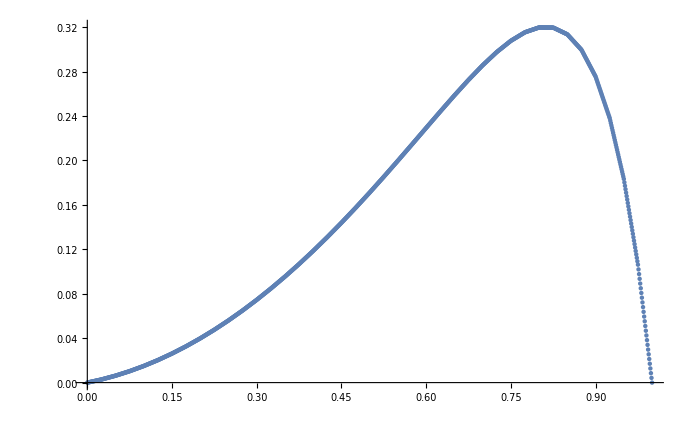
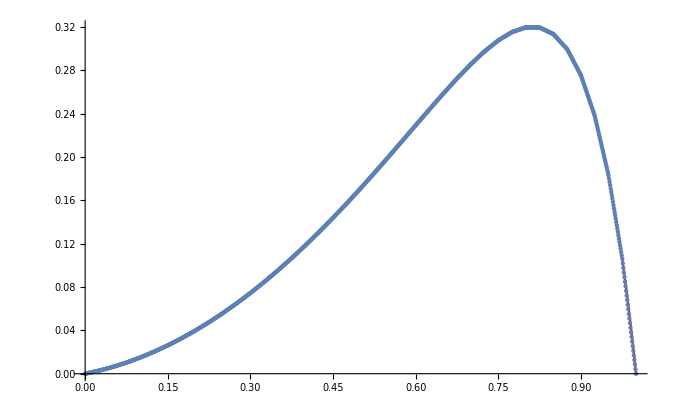
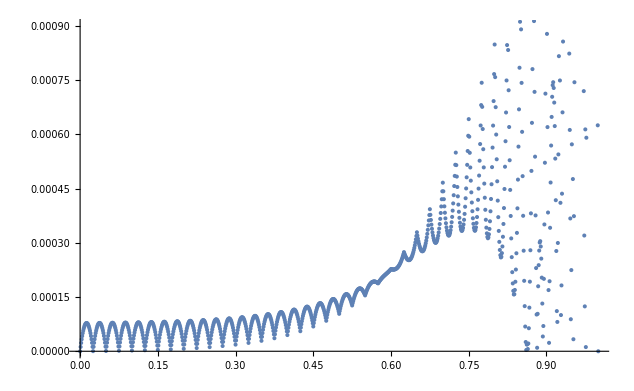

```mathematica
list={{0,0},{0.001,0.000112205},{0.002,0.000224409},{0.003,0.000336614},{0.004,0.000448818},{0.005,0.000561023},{0.006,0.000673228},{0.007,0.000785432},{0.008,0.000897637},{0.009,0.00100984},{0.01,0.00112205},{0.011,0.00123425},{0.012,0.00134646},{0.013,0.00145866},{0.014,0.00157086},{0.015,0.00168307},{0.016,0.00179527},{0.017,0.00190748},{0.018,0.00201968},{0.019,0.00213189},{0.02,0.00224409},{0.021,0.0023563},{0.022,0.0024685},{0.023,0.00258071},{0.024,0.00269291},{0.025,0.00280512},{0.026,0.00294224},{0.027,0.00307936},{0.028,0.00321648},{0.029,0.0033536},{0.03,0.00349072},{0.031,0.00362784},{0.032,0.00376496},{0.033,0.00390208},{0.034,0.0040392},{0.035,0.00417632},{0.036,0.00431344},{0.037,0.00445056},{0.038,0.00458768},{0.039,0.0047248},{0.04,0.00486192},{0.041,0.00499904},{0.042,0.00513616},{0.043,0.00527328},{0.044,0.0054104},{0.045,0.00554752},{0.046,0.00568464},{0.047,0.00582176},{0.048,0.00595888},{0.049,0.006096},{0.05,0.00623312},{0.051,0.00639513},{0.052,0.00655714},{0.053,0.00671916},{0.054,0.00688117},{0.055,0.00704318},{0.056,0.00720519},{0.057,0.0073672},{0.058,0.00752921},{0.059,0.00769123},{0.06,0.00785324},{0.061,0.00801525},{0.062,0.00817726},{0.063,0.00833927},{0.064,0.00850129},{0.065,0.0086633},{0.066,0.00882531},{0.067,0.00898732},{0.068,0.00914933},{0.069,0.00931134},{0.07,0.00947336},{0.071,0.00963537},{0.072,0.00979738},{0.073,0.00995939},{0.074,0.0101214},{0.075,0.0102834},{0.076,0.0104703},{0.077,0.0106572},{0.078,0.010844},{0.079,0.0110309},{0.08,0.0112178},{0.081,0.0114046},{0.082,0.0115915},{0.083,0.0117784},{0.084,0.0119653},{0.085,0.0121521},{0.086,0.012339},{0.087,0.0125259},{0.088,0.0127128},{0.089,0.0128996},{0.09,0.0130865},{0.091,0.0132734},{0.092,0.0134602},{0.093,0.0136471},{0.094,0.013834},{0.095,0.0140209},{0.096,0.0142077},{0.097,0.0143946},{0.098,0.0145815},{0.099,0.0147683},{0.1,0.0149552},{0.101,0.0151669},{0.102,0.0153786},{0.103,0.0155903},{0.104,0.015802},{0.105,0.0160137},{0.106,0.0162254},{0.107,0.0164371},{0.108,0.0166488},{0.109,0.0168605},{0.11,0.0170721},{0.111,0.0172838},{0.112,0.0174955},{0.113,0.0177072},{0.114,0.0179189},{0.115,0.0181306},{0.116,0.0183423},{0.117,0.018554},{0.118,0.0187657},{0.119,0.0189774},{0.12,0.0191891},{0.121,0.0194008},{0.122,0.0196125},{0.123,0.0198242},{0.124,0.0200358},{0.125,0.0202475},{0.126,0.020484},{0.127,0.0207205},{0.128,0.0209569},{0.129,0.0211934},{0.13,0.0214299},{0.131,0.0216663},{0.132,0.0219028},{0.133,0.0221392},{0.134,0.0223757},{0.135,0.0226122},{0.136,0.0228486},{0.137,0.0230851},{0.138,0.0233215},{0.139,0.023558},{0.14,0.0237945},{0.141,0.0240309},{0.142,0.0242674},{0.143,0.0245039},{0.144,0.0247403},{0.145,0.0249768},{0.146,0.0252132},{0.147,0.0254497},{0.148,0.0256862},{0.149,0.0259226},{0.15,0.0261591},{0.151,0.0264203},{0.152,0.0266814},{0.153,0.0269426},{0.154,0.0272038},{0.155,0.0274649},{0.156,0.0277261},{0.157,0.0279873},{0.158,0.0282484},{0.159,0.0285096},{0.16,0.0287708},{0.161,0.0290319},{0.162,0.0292931},{0.163,0.0295542},{0.164,0.0298154},{0.165,0.0300766},{0.166,0.0303377},{0.167,0.0305989},{0.168,0.0308601},{0.169,0.0311212},{0.17,0.0313824},{0.171,0.0316436},{0.172,0.0319047},{0.173,0.0321659},{0.174,0.0324271},{0.175,0.0326882},{0.176,0.032974},{0.177,0.0332598},{0.178,0.0335456},{0.179,0.0338314},{0.18,0.0341172},{0.181,0.0344029},{0.182,0.0346887},{0.183,0.0349745},{0.184,0.0352603},{0.185,0.0355461},{0.186,0.0358319},{0.187,0.0361177},{0.188,0.0364034},{0.189,0.0366892},{0.19,0.036975},{0.191,0.0372608},{0.192,0.0375466},{0.193,0.0378324},{0.194,0.0381181},{0.195,0.0384039},{0.196,0.0386897},{0.197,0.0389755},{0.198,0.0392613},{0.199,0.0395471},{0.2,0.0398329},{0.201,0.0401431},{0.202,0.0404534},{0.203,0.0407637},{0.204,0.041074},{0.205,0.0413843},{0.206,0.0416946},{0.207,0.0420049},{0.208,0.0423152},{0.209,0.0426255},{0.21,0.0429358},{0.211,0.0432461},{0.212,0.0435564},{0.213,0.0438667},{0.214,0.044177},{0.215,0.0444873},{0.216,0.0447976},{0.217,0.0451079},{0.218,0.0454181},{0.219,0.0457284},{0.22,0.0460387},{0.221,0.046349},{0.222,0.0466593},{0.223,0.0469696},{0.224,0.0472799},{0.225,0.0475902},{0.226,0.0479249},{0.227,0.0482595},{0.228,0.0485942},{0.229,0.0489289},{0.23,0.0492635},{0.231,0.0495982},{0.232,0.0499329},{0.233,0.0502675},{0.234,0.0506022},{0.235,0.0509369},{0.236,0.0512715},{0.237,0.0516062},{0.238,0.0519408},{0.239,0.0522755},{0.24,0.0526102},{0.241,0.0529448},{0.242,0.0532795},{0.243,0.0536142},{0.244,0.0539488},{0.245,0.0542835},{0.246,0.0546182},{0.247,0.0549528},{0.248,0.0552875},{0.249,0.0556221},{0.25,0.0559568},{0.251,0.0563157},{0.252,0.0566745},{0.253,0.0570334},{0.254,0.0573922},{0.255,0.0577511},{0.256,0.0581099},{0.257,0.0584688},{0.258,0.0588276},{0.259,0.0591865},{0.26,0.0595454},{0.261,0.0599042},{0.262,0.0602631},{0.263,0.0606219},{0.264,0.0609808},{0.265,0.0613396},{0.266,0.0616985},{0.267,0.0620573},{0.268,0.0624162},{0.269,0.062775},{0.27,0.0631339},{0.271,0.0634927},{0.272,0.0638516},{0.273,0.0642105},{0.274,0.0645693},{0.275,0.0649282},{0.276,0.065311},{0.277,0.0656938},{0.278,0.0660766},{0.279,0.0664594},{0.28,0.0668422},{0.281,0.067225},{0.282,0.0676078},{0.283,0.0679907},{0.284,0.0683735},{0.285,0.0687563},{0.286,0.0691391},{0.287,0.0695219},{0.288,0.0699047},{0.289,0.0702875},{0.29,0.0706703},{0.291,0.0710532},{0.292,0.071436},{0.293,0.0718188},{0.294,0.0722016},{0.295,0.0725844},{0.296,0.0729672},{0.297,0.07335},{0.298,0.0737328},{0.299,0.0741157},{0.3,0.0744985},{0.301,0.0749049},{0.302,0.0753114},{0.303,0.0757179},{0.304,0.0761244},{0.305,0.0765308},{0.306,0.0769373},{0.307,0.0773438},{0.308,0.0777502},{0.309,0.0781567},{0.31,0.0785632},{0.311,0.0789697},{0.312,0.0793761},{0.313,0.0797826},{0.314,0.0801891},{0.315,0.0805956},{0.316,0.081002},{0.317,0.0814085},{0.318,0.081815},{0.319,0.0822214},{0.32,0.0826279},{0.321,0.0830344},{0.322,0.0834409},{0.323,0.0838473},{0.324,0.0842538},{0.325,0.0846603},{0.326,0.08509},{0.327,0.0855198},{0.328,0.0859495},{0.329,0.0863793},{0.33,0.086809},{0.331,0.0872388},{0.332,0.0876685},{0.333,0.0880983},{0.334,0.088528},{0.335,0.0889578},{0.336,0.0893875},{0.337,0.0898173},{0.338,0.090247},{0.339,0.0906768},{0.34,0.0911065},{0.341,0.0915363},{0.342,0.091966},{0.343,0.0923958},{0.344,0.0928255},{0.345,0.0932553},{0.346,0.093685},{0.347,0.0941148},{0.348,0.0945446},{0.349,0.0949743},{0.35,0.0954041},{0.351,0.0958566},{0.352,0.0963091},{0.353,0.0967617},{0.354,0.0972142},{0.355,0.0976667},{0.356,0.0981193},{0.357,0.0985718},{0.358,0.0990243},{0.359,0.0994769},{0.36,0.0999294},{0.361,0.100382},{0.362,0.100834},{0.363,0.101287},{0.364,0.10174},{0.365,0.102192},{0.366,0.102645},{0.367,0.103097},{0.368,0.10355},{0.369,0.104002},{0.37,0.104455},{0.371,0.104907},{0.372,0.10536},{0.373,0.105812},{0.374,0.106265},{0.375,0.106717},{0.376,0.107192},{0.377,0.107667},{0.378,0.108142},{0.379,0.108616},{0.38,0.109091},{0.381,0.109566},{0.382,0.11004},{0.383,0.110515},{0.384,0.11099},{0.385,0.111464},{0.386,0.111939},{0.387,0.112414},{0.388,0.112888},{0.389,0.113363},{0.39,0.113838},{0.391,0.114313},{0.392,0.114787},{0.393,0.115262},{0.394,0.115737},{0.395,0.116211},{0.396,0.116686},{0.397,0.117161},{0.398,0.117635},{0.399,0.11811},{0.4,0.118585},{0.401,0.119081},{0.402,0.119577},{0.403,0.120073},{0.404,0.120569},{0.405,0.121065},{0.406,0.121561},{0.407,0.122057},{0.408,0.122553},{0.409,0.123049},{0.41,0.123545},{0.411,0.124041},{0.412,0.124537},{0.413,0.125033},{0.414,0.125529},{0.415,0.126025},{0.416,0.126521},{0.417,0.127017},{0.418,0.127513},{0.419,0.128009},{0.42,0.128505},{0.421,0.129001},{0.422,0.129497},{0.423,0.129993},{0.424,0.130489},{0.425,0.130985},{0.426,0.131502},{0.427,0.132018},{0.428,0.132534},{0.429,0.133051},{0.43,0.133567},{0.431,0.134083},{0.432,0.1346},{0.433,0.135116},{0.434,0.135632},{0.435,0.136149},{0.436,0.136665},{0.437,0.137181},{0.438,0.137698},{0.439,0.138214},{0.44,0.13873},{0.441,0.139247},{0.442,0.139763},{0.443,0.140279},{0.444,0.140796},{0.445,0.141312},{0.446,0.141828},{0.447,0.142345},{0.448,0.142861},{0.449,0.143377},{0.45,0.143894},{0.451,0.144429},{0.452,0.144964},{0.453,0.145499},{0.454,0.146035},{0.455,0.14657},{0.456,0.147105},{0.457,0.14764},{0.458,0.148176},{0.459,0.148711},{0.46,0.149246},{0.461,0.149782},{0.462,0.150317},{0.463,0.150852},{0.464,0.151387},{0.465,0.151923},{0.466,0.152458},{0.467,0.152993},{0.468,0.153529},{0.469,0.154064},{0.47,0.154599},{0.471,0.155134},{0.472,0.15567},{0.473,0.156205},{0.474,0.15674},{0.475,0.157275},{0.476,0.157828},{0.477,0.15838},{0.478,0.158933},{0.479,0.159485},{0.48,0.160038},{0.481,0.16059},{0.482,0.161143},{0.483,0.161695},{0.484,0.162248},{0.485,0.1628},{0.486,0.163353},{0.487,0.163905},{0.488,0.164458},{0.489,0.16501},{0.49,0.165563},{0.491,0.166115},{0.492,0.166668},{0.493,0.16722},{0.494,0.167773},{0.495,0.168325},{0.496,0.168878},{0.497,0.16943},{0.498,0.169983},{0.499,0.170535},{0.5,0.171088},{0.501,0.171655},{0.502,0.172223},{0.503,0.17279},{0.504,0.173358},{0.505,0.173925},{0.506,0.174493},{0.507,0.17506},{0.508,0.175628},{0.509,0.176195},{0.51,0.176763},{0.511,0.17733},{0.512,0.177898},{0.513,0.178465},{0.514,0.179033},{0.515,0.1796},{0.516,0.180168},{0.517,0.180735},{0.518,0.181303},{0.519,0.18187},{0.52,0.182438},{0.521,0.183005},{0.522,0.183573},{0.523,0.18414},{0.524,0.184708},{0.525,0.185275},{0.526,0.185855},{0.527,0.186434},{0.528,0.187014},{0.529,0.187594},{0.53,0.188173},{0.531,0.188753},{0.532,0.189333},{0.533,0.189912},{0.534,0.190492},{0.535,0.191071},{0.536,0.191651},{0.537,0.192231},{0.538,0.19281},{0.539,0.19339},{0.54,0.19397},{0.541,0.194549},{0.542,0.195129},{0.543,0.195709},{0.544,0.196288},{0.545,0.196868},{0.546,0.197447},{0.547,0.198027},{0.548,0.198607},{0.549,0.199186},{0.55,0.199766},{0.551,0.200354},{0.552,0.200942},{0.553,0.20153},{0.554,0.202118},{0.555,0.202707},{0.556,0.203295},{0.557,0.203883},{0.558,0.204471},{0.559,0.205059},{0.56,0.205647},{0.561,0.206235},{0.562,0.206823},{0.563,0.207411},{0.564,0.207999},{0.565,0.208588},{0.566,0.209176},{0.567,0.209764},{0.568,0.210352},{0.569,0.21094},{0.57,0.211528},{0.571,0.212116},{0.572,0.212704},{0.573,0.213292},{0.574,0.21388},{0.575,0.214469},{0.576,0.21506},{0.577,0.215652},{0.578,0.216244},{0.579,0.216836},{0.58,0.217428},{0.581,0.21802},{0.582,0.218611},{0.583,0.219203},{0.584,0.219795},{0.585,0.220387},{0.586,0.220979},{0.587,0.221571},{0.588,0.222163},{0.589,0.222754},{0.59,0.223346},{0.591,0.223938},{0.592,0.22453},{0.593,0.225122},{0.594,0.225714},{0.595,0.226305},{0.596,0.226897},{0.597,0.227489},{0.598,0.228081},{0.599,0.228673},{0.6,0.229265},{0.601,0.229854},{0.602,0.230444},{0.603,0.231033},{0.604,0.231623},{0.605,0.232212},{0.606,0.232802},{0.607,0.233391},{0.608,0.233981},{0.609,0.23457},{0.61,0.23516},{0.611,0.235749},{0.612,0.236339},{0.613,0.236928},{0.614,0.237518},{0.615,0.238107},{0.616,0.238697},{0.617,0.239286},{0.618,0.239876},{0.619,0.240465},{0.62,0.241055},{0.621,0.241645},{0.622,0.242234},{0.623,0.242824},{0.624,0.243413},{0.625,0.244003},{0.626,0.244582},{0.627,0.245161},{0.628,0.245741},{0.629,0.24632},{0.63,0.246899},{0.631,0.247479},{0.632,0.248058},{0.633,0.248638},{0.634,0.249217},{0.635,0.249796},{0.636,0.250376},{0.637,0.250955},{0.638,0.251534},{0.639,0.252114},{0.64,0.252693},{0.641,0.253273},{0.642,0.253852},{0.643,0.254431},{0.644,0.255011},{0.645,0.25559},{0.646,0.25617},{0.647,0.256749},{0.648,0.257328},{0.649,0.257908},{0.65,0.258487},{0.651,0.259046},{0.652,0.259605},{0.653,0.260165},{0.654,0.260724},{0.655,0.261283},{0.656,0.261842},{0.657,0.262401},{0.658,0.262961},{0.659,0.26352},{0.66,0.264079},{0.661,0.264638},{0.662,0.265197},{0.663,0.265757},{0.664,0.266316},{0.665,0.266875},{0.666,0.267434},{0.667,0.267993},{0.668,0.268553},{0.669,0.269112},{0.67,0.269671},{0.671,0.27023},{0.672,0.270789},{0.673,0.271349},{0.674,0.271908},{0.675,0.272467},{0.676,0.272993},{0.677,0.273519},{0.678,0.274045},{0.679,0.274571},{0.68,0.275098},{0.681,0.275624},{0.682,0.27615},{0.683,0.276676},{0.684,0.277202},{0.685,0.277728},{0.686,0.278254},{0.687,0.27878},{0.688,0.279306},{0.689,0.279833},{0.69,0.280359},{0.691,0.280885},{0.692,0.281411},{0.693,0.281937},{0.694,0.282463},{0.695,0.282989},{0.696,0.283515},{0.697,0.284041},{0.698,0.284568},{0.699,0.285094},{0.7,0.28562},{0.701,0.286096},{0.702,0.286573},{0.703,0.287049},{0.704,0.287526},{0.705,0.288002},{0.706,0.288478},{0.707,0.288955},{0.708,0.289431},{0.709,0.289908},{0.71,0.290384},{0.711,0.290861},{0.712,0.291337},{0.713,0.291813},{0.714,0.29229},{0.715,0.292766},{0.716,0.293243},{0.717,0.293719},{0.718,0.294196},{0.719,0.294672},{0.72,0.295148},{0.721,0.295625},{0.722,0.296101},{0.723,0.296578},{0.724,0.297054},{0.725,0.297531},{0.726,0.297936},{0.727,0.298341},{0.728,0.298747},{0.729,0.299152},{0.73,0.299558},{0.731,0.299963},{0.732,0.300368},{0.733,0.300774},{0.734,0.301179},{0.735,0.301585},{0.736,0.30199},{0.737,0.302396},{0.738,0.302801},{0.739,0.303206},{0.74,0.303612},{0.741,0.304017},{0.742,0.304423},{0.743,0.304828},{0.744,0.305233},{0.745,0.305639},{0.746,0.306044},{0.747,0.30645},{0.748,0.306855},{0.749,0.30726},{0.75,0.307666},{0.751,0.307973},{0.752,0.30828},{0.753,0.308587},{0.754,0.308894},{0.755,0.309201},{0.756,0.309508},{0.757,0.309815},{0.758,0.310122},{0.759,0.310429},{0.76,0.310735},{0.761,0.311042},{0.762,0.311349},{0.763,0.311656},{0.764,0.311963},{0.765,0.31227},{0.766,0.312577},{0.767,0.312884},{0.768,0.313191},{0.769,0.313498},{0.77,0.313805},{0.771,0.314112},{0.772,0.314419},{0.773,0.314726},{0.774,0.315033},{0.775,0.31534},{0.776,0.315513},{0.777,0.315686},{0.778,0.31586},{0.779,0.316033},{0.78,0.316206},{0.781,0.316379},{0.782,0.316552},{0.783,0.316726},{0.784,0.316899},{0.785,0.317072},{0.786,0.317245},{0.787,0.317419},{0.788,0.317592},{0.789,0.317765},{0.79,0.317938},{0.791,0.318112},{0.792,0.318285},{0.793,0.318458},{0.794,0.318631},{0.795,0.318804},{0.796,0.318978},{0.797,0.319151},{0.798,0.319324},{0.799,0.319497},{0.8,0.319671},{0.801,0.319665},{0.802,0.319659},{0.803,0.319653},{0.804,0.319647},{0.805,0.319641},{0.806,0.319636},{0.807,0.31963},{0.808,0.319624},{0.809,0.319618},{0.81,0.319612},{0.811,0.319606},{0.812,0.3196},{0.813,0.319595},{0.814,0.319589},{0.815,0.319583},{0.816,0.319577},{0.817,0.319571},{0.818,0.319565},{0.819,0.31956},{0.82,0.319554},{0.821,0.319548},{0.822,0.319542},{0.823,0.319536},{0.824,0.31953},{0.825,0.319524},{0.826,0.319281},{0.827,0.319038},{0.828,0.318795},{0.829,0.318552},{0.83,0.318308},{0.831,0.318065},{0.832,0.317822},{0.833,0.317579},{0.834,0.317335},{0.835,0.317092},{0.836,0.316849},{0.837,0.316606},{0.838,0.316362},{0.839,0.316119},{0.84,0.315876},{0.841,0.315633},{0.842,0.31539},{0.843,0.315146},{0.844,0.314903},{0.845,0.31466},{0.846,0.314417},{0.847,0.314173},{0.848,0.31393},{0.849,0.313687},{0.85,0.313444},{0.851,0.312888},{0.852,0.312333},{0.853,0.311777},{0.854,0.311221},{0.855,0.310666},{0.856,0.31011},{0.857,0.309555},{0.858,0.308999},{0.859,0.308443},{0.86,0.307888},{0.861,0.307332},{0.862,0.306777},{0.863,0.306221},{0.864,0.305666},{0.865,0.30511},{0.866,0.304554},{0.867,0.303999},{0.868,0.303443},{0.869,0.302888},{0.87,0.302332},{0.871,0.301777},{0.872,0.301221},{0.873,0.300665},{0.874,0.30011},{0.875,0.299554},{0.876,0.29859},{0.877,0.297626},{0.878,0.296661},{0.879,0.295697},{0.88,0.294733},{0.881,0.293768},{0.882,0.292804},{0.883,0.29184},{0.884,0.290875},{0.885,0.289911},{0.886,0.288947},{0.887,0.287982},{0.888,0.287018},{0.889,0.286054},{0.89,0.285089},{0.891,0.284125},{0.892,0.283161},{0.893,0.282196},{0.894,0.281232},{0.895,0.280268},{0.896,0.279303},{0.897,0.278339},{0.898,0.277375},{0.899,0.276411},{0.9,0.275446},{0.901,0.273949},{0.902,0.272452},{0.903,0.270955},{0.904,0.269458},{0.905,0.267961},{0.906,0.266464},{0.907,0.264967},{0.908,0.26347},{0.909,0.261973},{0.91,0.260476},{0.911,0.258979},{0.912,0.257482},{0.913,0.255985},{0.914,0.254488},{0.915,0.252991},{0.916,0.251494},{0.917,0.249998},{0.918,0.248501},{0.919,0.247004},{0.92,0.245507},{0.921,0.24401},{0.922,0.242513},{0.923,0.241016},{0.924,0.239519},{0.925,0.238022},{0.926,0.235833},{0.927,0.233644},{0.928,0.231455},{0.929,0.229266},{0.93,0.227077},{0.931,0.224888},{0.932,0.222699},{0.933,0.22051},{0.934,0.218321},{0.935,0.216132},{0.936,0.213943},{0.937,0.211754},{0.938,0.209565},{0.939,0.207376},{0.94,0.205187},{0.941,0.202998},{0.942,0.200809},{0.943,0.19862},{0.944,0.196431},{0.945,0.194242},{0.946,0.192053},{0.947,0.189864},{0.948,0.187675},{0.949,0.185486},{0.95,0.183297},{0.951,0.180211},{0.952,0.177126},{0.953,0.17404},{0.954,0.170954},{0.955,0.167868},{0.956,0.164782},{0.957,0.161696},{0.958,0.158611},{0.959,0.155525},{0.96,0.152439},{0.961,0.149353},{0.962,0.146267},{0.963,0.143181},{0.964,0.140096},{0.965,0.13701},{0.966,0.133924},{0.967,0.130838},{0.968,0.127752},{0.969,0.124667},{0.97,0.121581},{0.971,0.118495},{0.972,0.115409},{0.973,0.112323},{0.974,0.109237},{0.975,0.106152},{0.976,0.101906},{0.977,0.0976595},{0.978,0.0934134},{0.979,0.0891673},{0.98,0.0849213},{0.981,0.0806752},{0.982,0.0764291},{0.983,0.0721831},{0.984,0.067937},{0.985,0.0636909},{0.986,0.0594449},{0.987,0.0551988},{0.988,0.0509528},{0.989,0.0467067},{0.99,0.0424606},{0.991,0.0382146},{0.992,0.0339685},{0.993,0.0297224},{0.994,0.0254764},{0.995,0.0212303},{0.996,0.0169843},{0.997,0.0127382},{0.998,0.00849213},{0.999,0.00424606},{1,0}};
error={{0,0*10^(0)},{0.001,1.19784*10^(-5)},{0.002,2.29595*10^(-5)},{0.003,3.29435*10^(-5)},{0.004,4.19302*10^(-5)},{0.005,4.99198*10^(-5)},{0.006,5.69122*10^(-5)},{0.007,6.29075*10^(-5)},{0.008,6.79058*10^(-5)},{0.009,7.1907*10^(-5)},{0.01,7.49112*10^(-5)},{0.011,7.69184*10^(-5)},{0.012,7.79286*10^(-5)},{0.013,7.79419*10^(-5)},{0.014,7.69583*10^(-5)},{0.015,7.49778*10^(-5)},{0.016,7.20005*10^(-5)},{0.017,6.80264*10^(-5)},{0.018,6.30556*10^(-5)},{0.019,5.7088*10^(-5)},{0.02,5.01236*10^(-5)},{0.021,4.21627*10^(-5)},{0.022,3.3205*10^(-5)},{0.023,2.32508*10^(-5)},{0.024,1.23*10^(-5)},{0.025,3.52657*10^(-7)},{0.026,1.23244*10^(-5)},{0.027,2.32997*10^(-5)},{0.028,3.32786*10^(-5)},{0.029,4.2261*10^(-5)},{0.03,5.02472*10^(-5)},{0.031,5.72369*10^(-5)},{0.032,6.32304*10^(-5)},{0.033,6.82277*10^(-5)},{0.034,7.22287*10^(-5)},{0.035,7.52336*10^(-5)},{0.036,7.72423*10^(-5)},{0.037,7.8255*10^(-5)},{0.038,7.82716*10^(-5)},{0.039,7.72921*10^(-5)},{0.04,7.53167*10^(-5)},{0.041,7.23454*10^(-5)},{0.042,6.83781*10^(-5)},{0.043,6.3415*10^(-5)},{0.044,5.74561*10^(-5)},{0.045,5.05014*10^(-5)},{0.046,4.2551*10^(-5)},{0.047,3.3605*10^(-5)},{0.048,2.36632*10^(-5)},{0.049,1.27259*10^(-5)},{0.05,7.93006*10^(-7)},{0.051,1.27561*10^(-5)},{0.052,2.37237*10^(-5)},{0.053,3.3696*10^(-5)},{0.054,4.26728*10^(-5)},{0.055,5.06543*10^(-5)},{0.056,5.76406*10^(-5)},{0.057,6.36316*10^(-5)},{0.058,6.86274*10^(-5)},{0.059,7.26281*10^(-5)},{0.06,7.56337*10^(-5)},{0.061,7.76443*10^(-5)},{0.062,7.86599*10^(-5)},{0.063,7.86805*10^(-5)},{0.064,7.77063*10^(-5)},{0.065,7.57372*10^(-5)},{0.066,7.27734*10^(-5)},{0.067,6.88148*10^(-5)},{0.068,6.38616*10^(-5)},{0.069,5.79137*10^(-5)},{0.07,5.09712*10^(-5)},{0.071,4.30343*10^(-5)},{0.072,3.41028*10^(-5)},{0.073,2.4177*10^(-5)},{0.074,1.32569*10^(-5)},{0.075,1.34239*10^(-6)},{0.076,1.32942*10^(-5)},{0.077,2.42518*10^(-5)},{0.078,3.42153*10^(-5)},{0.079,4.31848*10^(-5)},{0.08,5.11602*10^(-5)},{0.081,5.81417*10^(-5)},{0.082,6.41294*10^(-5)},{0.083,6.91232*10^(-5)},{0.084,7.31232*10^(-5)},{0.085,7.61296*10^(-5)},{0.086,7.81424*10^(-5)},{0.087,7.91616*10^(-5)},{0.088,7.91873*10^(-5)},{0.089,7.82195*10^(-5)},{0.09,7.62584*10^(-5)},{0.091,7.3304*10^(-5)},{0.092,6.93564*10^(-5)},{0.093,6.44156*10^(-5)},{0.094,5.84817*10^(-5)},{0.095,5.15547*10^(-5)},{0.096,4.36349*10^(-5)},{0.097,3.47221*10^(-5)},{0.098,2.48165*10^(-5)},{0.099,1.39182*10^(-5)},{0.1,2.0272*10^(-6)},{0.101,1.39642*10^(-5)},{0.102,2.49088*10^(-5)},{0.103,3.48608*10^(-5)},{0.104,4.38206*10^(-5)},{0.105,5.1788*10^(-5)},{0.106,5.87632*10^(-5)},{0.107,6.47462*10^(-5)},{0.108,6.97372*10^(-5)},{0.109,7.37363*10^(-5)},{0.11,7.67434*10^(-5)},{0.111,7.87587*10^(-5)},{0.112,7.97823*10^(-5)},{0.113,7.98142*10^(-5)},{0.114,7.88546*10^(-5)},{0.115,7.69035*10^(-5)},{0.116,7.39609*10^(-5)},{0.117,7.00271*10^(-5)},{0.118,6.51021*10^(-5)},{0.119,5.91859*10^(-5)},{0.12,5.22787*10^(-5)},{0.121,4.43805*10^(-5)},{0.122,3.54914*10^(-5)},{0.123,2.56116*10^(-5)},{0.124,1.47411*10^(-5)},{0.125,2.88*10^(-6)},{0.126,1.47978*10^(-5)},{0.127,2.57252*10^(-5)},{0.128,3.56623*10^(-5)},{0.129,4.46092*10^(-5)},{0.13,5.2566*10^(-5)},{0.131,5.95328*10^(-5)},{0.132,6.55097*10^(-5)},{0.133,7.04968*10^(-5)},{0.134,7.44942*10^(-5)},{0.135,7.7502*10^(-5)},{0.136,7.95203*10^(-5)},{0.137,8.05492*10^(-5)},{0.138,8.05888*10^(-5)},{0.139,7.96393*10^(-5)},{0.14,7.77007*10^(-5)},{0.141,7.47731*10^(-5)},{0.142,7.08567*10^(-5)},{0.143,6.59516*10^(-5)},{0.144,6.00579*10^(-5)},{0.145,5.31756*10^(-5)},{0.146,4.5305*10^(-5)},{0.147,3.64461*10^(-5)},{0.148,2.6599*10^(-5)},{0.149,1.57639*10^(-5)},{0.15,3.94094*10^(-6)},{0.151,1.58336*10^(-5)},{0.152,2.67387*10^(-5)},{0.153,3.66562*10^(-5)},{0.154,4.55862*10^(-5)},{0.155,5.3529*10^(-5)},{0.156,6.04846*10^(-5)},{0.157,6.64532*10^(-5)},{0.158,7.14349*10^(-5)},{0.159,7.54298*10^(-5)},{0.16,7.8438*10^(-5)},{0.161,8.04598*10^(-5)},{0.162,8.14951*10^(-5)},{0.163,8.15443*10^(-5)},{0.164,8.06073*10^(-5)},{0.165,7.86844*10^(-5)},{0.166,7.57757*10^(-5)},{0.167,7.18813*10^(-5)},{0.168,6.70013*10^(-5)},{0.169,6.1136*10^(-5)},{0.17,5.42855*10^(-5)},{0.171,4.64498*10^(-5)},{0.172,3.76292*10^(-5)},{0.173,2.78239*10^(-5)},{0.174,1.70339*10^(-5)},{0.175,5.2594*10^(-6)},{0.176,1.71194*10^(-5)},{0.177,2.79952*10^(-5)},{0.178,3.7887*10^(-5)},{0.179,4.67949*10^(-5)},{0.18,5.47192*10^(-5)},{0.181,6.166*10^(-5)},{0.182,6.76173*10^(-5)},{0.183,7.25916*10^(-5)},{0.184,7.65827*10^(-5)},{0.185,7.95911*10^(-5)},{0.186,8.16168*10^(-5)},{0.187,8.26599*10^(-5)},{0.188,8.27208*10^(-5)},{0.189,8.17995*10^(-5)},{0.19,7.98962*10^(-5)},{0.191,7.70111*10^(-5)},{0.192,7.31445*10^(-5)},{0.193,6.82964*10^(-5)},{0.194,6.24671*10^(-5)},{0.195,5.56567*10^(-5)},{0.196,4.78655*10^(-5)},{0.197,3.90936*10^(-5)},{0.198,2.93413*10^(-5)},{0.199,1.86087*10^(-5)},{0.2,6.896*10^(-6)},{0.201,1.87133*10^(-5)},{0.202,2.95509*10^(-5)},{0.203,3.94091*10^(-5)},{0.204,4.8288*10^(-5)},{0.205,5.61879*10^(-5)},{0.206,6.31089*10^(-5)},{0.207,6.90513*10^(-5)},{0.208,7.40153*10^(-5)},{0.209,7.80011*10^(-5)},{0.21,8.10089*10^(-5)},{0.211,8.3039*10^(-5)},{0.212,8.40915*10^(-5)},{0.213,8.41667*10^(-5)},{0.214,8.32649*10^(-5)},{0.215,8.13862*10^(-5)},{0.216,7.85308*10^(-5)},{0.217,7.46992*10^(-5)},{0.218,6.98913*10^(-5)},{0.219,6.41076*10^(-5)},{0.22,5.73482*10^(-5)},{0.221,4.96134*10^(-5)},{0.222,4.09034*10^(-5)},{0.223,3.12185*10^(-5)},{0.224,2.0559*10^(-5)},{0.225,8.925*10^(-6)},{0.226,2.06867*10^(-5)},{0.227,3.14745*10^(-5)},{0.228,4.12886*10^(-5)},{0.229,5.01294*10^(-5)},{0.23,5.79971*10^(-5)},{0.231,6.4892*10^(-5)},{0.232,7.08143*10^(-5)},{0.233,7.57643*10^(-5)},{0.234,7.97424*10^(-5)},{0.235,8.27487*10^(-5)},{0.236,8.47836*10^(-5)},{0.237,8.58473*10^(-5)},{0.238,8.59401*10^(-5)},{0.239,8.50624*10^(-5)},{0.24,8.32145*10^(-5)},{0.241,8.03965*10^(-5)},{0.242,7.66089*10^(-5)},{0.243,7.1852*10^(-5)},{0.244,6.61259*10^(-5)},{0.245,5.94311*10^(-5)},{0.246,5.17679*10^(-5)},{0.247,4.31366*10^(-5)},{0.248,3.35375*10^(-5)},{0.249,2.29709*10^(-5)},{0.25,1.14372*10^(-5)},{0.251,2.31264*10^(-5)},{0.252,3.38491*10^(-5)},{0.253,4.36057*10^(-5)},{0.254,5.23965*10^(-5)},{0.255,6.02218*10^(-5)},{0.256,6.7082*10^(-5)},{0.257,7.29775*10^(-5)},{0.258,7.79085*10^(-5)},{0.259,8.18755*10^(-5)},{0.26,8.48789*10^(-5)},{0.261,8.69188*10^(-5)},{0.262,8.79959*10^(-5)},{0.263,8.81103*10^(-5)},{0.264,8.72626*10^(-5)},{0.265,8.5453*10^(-5)},{0.266,8.2682*10^(-5)},{0.267,7.89499*10^(-5)},{0.268,7.42572*10^(-5)},{0.269,6.86042*10^(-5)},{0.27,6.19913*10^(-5)},{0.271,5.44189*10^(-5)},{0.272,4.58875*10^(-5)},{0.273,3.63975*10^(-5)},{0.274,2.59492*10^(-5)},{0.275,1.45431*10^(-5)},{0.276,2.61379*10^(-5)},{0.277,3.67757*10^(-5)},{0.278,4.6457*10^(-5)},{0.279,5.51822*10^(-5)},{0.28,6.29518*10^(-5)},{0.281,6.97661*10^(-5)},{0.282,7.56257*10^(-5)},{0.283,8.05311*10^(-5)},{0.284,8.44825*10^(-5)},{0.285,8.74806*10^(-5)},{0.286,8.95258*10^(-5)},{0.287,9.06186*10^(-5)},{0.288,9.07594*10^(-5)},{0.289,8.99487*10^(-5)},{0.29,8.8187*10^(-5)},{0.291,8.54749*10^(-5)},{0.292,8.18128*10^(-5)},{0.293,7.72011*10^(-5)},{0.294,7.16405*10^(-5)},{0.295,6.51314*10^(-5)},{0.296,5.76744*10^(-5)},{0.297,4.92699*10^(-5)},{0.298,3.99186*10^(-5)},{0.299,2.96209*10^(-5)},{0.3,1.83773*10^(-5)},{0.301,2.98491*10^(-5)},{0.302,4.03761*10^(-5)},{0.303,4.9959*10^(-5)},{0.304,5.85982*10^(-5)},{0.305,6.62944*10^(-5)},{0.306,7.30481*10^(-5)},{0.307,7.88599*10^(-5)},{0.308,8.37304*10^(-5)},{0.309,8.76602*10^(-5)},{0.31,9.06498*10^(-5)},{0.311,9.26999*10^(-5)},{0.312,9.38111*10^(-5)},{0.313,9.3984*10^(-5)},{0.314,9.32192*10^(-5)},{0.315,9.15173*10^(-5)},{0.316,8.8879*10^(-5)},{0.317,8.53049*10^(-5)},{0.318,8.07957*10^(-5)},{0.319,7.53519*10^(-5)},{0.32,6.89744*10^(-5)},{0.321,6.16636*10^(-5)},{0.322,5.34204*10^(-5)},{0.323,4.42454*10^(-5)},{0.324,3.41392*10^(-5)},{0.325,2.31025*10^(-5)},{0.326,3.44141*10^(-5)},{0.327,4.47966*10^(-5)},{0.328,5.42508*10^(-5)},{0.329,6.27774*10^(-5)},{0.33,7.03772*10^(-5)},{0.331,7.70507*10^(-5)},{0.332,8.27989*10^(-5)},{0.333,8.76224*10^(-5)},{0.334,9.15221*10^(-5)},{0.335,9.44986*10^(-5)},{0.336,9.65528*10^(-5)},{0.337,9.76853*10^(-5)},{0.338,9.78971*10^(-5)},{0.339,9.7189*10^(-5)},{0.34,9.55616*10^(-5)},{0.341,9.30158*10^(-5)},{0.342,8.95525*10^(-5)},{0.343,8.51725*10^(-5)},{0.344,7.98766*10^(-5)},{0.345,7.36656*10^(-5)},{0.346,6.65405*10^(-5)},{0.347,5.8502*10^(-5)},{0.348,4.95511*10^(-5)},{0.349,3.96886*10^(-5)},{0.35,2.89154*10^(-5)},{0.351,4.00183*10^(-5)},{0.352,5.02124*10^(-5)},{0.353,5.94985*10^(-5)},{0.354,6.78775*10^(-5)},{0.355,7.53505*10^(-5)},{0.356,8.19183*10^(-5)},{0.357,8.75818*10^(-5)},{0.358,9.23422*10^(-5)},{0.359,9.62002*10^(-5)},{0.36,9.9157*10^(-5)},{0.361,1.01213*10^(-4)},{0.362,1.02371*10^(-4)},{0.363,1.02629*10^(-4)},{0.364,1.01991*10^(-4)},{0.365,1.00456*10^(-4)},{0.366,9.80266*10^(-5)},{0.367,9.47027*10^(-5)},{0.368,9.04856*10^(-5)},{0.369,8.53766*10^(-5)},{0.37,7.93767*10^(-5)},{0.371,7.24869*10^(-5)},{0.372,6.47085*10^(-5)},{0.373,5.60424*10^(-5)},{0.374,4.64899*10^(-5)},{0.375,3.60521*10^(-5)},{0.376,4.68834*10^(-5)},{0.377,5.68317*10^(-5)},{0.378,6.58982*10^(-5)},{0.379,7.40841*10^(-5)},{0.38,8.13905*10^(-5)},{0.381,8.78187*10^(-5)},{0.382,9.33699*10^(-5)},{0.383,9.80453*10^(-5)},{0.384,1.01846*10^(-4)},{0.385,1.04774*10^(-4)},{0.386,1.0683*10^(-4)},{0.387,1.08014*10^(-4)},{0.388,1.0833*10^(-4)},{0.389,1.07778*10^(-4)},{0.39,1.06358*10^(-4)},{0.391,1.04074*10^(-4)},{0.392,1.00925*10^(-4)},{0.393,9.69133*10^(-5)},{0.394,9.20405*10^(-5)},{0.395,8.63078*10^(-5)},{0.396,7.97166*10^(-5)},{0.397,7.22682*10^(-5)},{0.398,6.39642*10^(-5)},{0.399,5.4806*10^(-5)},{0.4,4.47951*10^(-5)},{0.401,5.52728*10^(-5)},{0.402,6.49008*10^(-5)},{0.403,7.36805*10^(-5)},{0.404,8.16135*10^(-5)},{0.405,8.87013*10^(-5)},{0.406,9.49455*10^(-5)},{0.407,1.00348*10^(-4)},{0.408,1.04909*10^(-4)},{0.409,1.08632*10^(-4)},{0.41,1.11517*10^(-4)},{0.411,1.13567*10^(-4)},{0.412,1.14783*10^(-4)},{0.413,1.15167*10^(-4)},{0.414,1.1472*10^(-4)},{0.415,1.13444*10^(-4)},{0.416,1.1134*10^(-4)},{0.417,1.08412*10^(-4)},{0.418,1.04659*10^(-4)},{0.419,1.00085*10^(-4)},{0.42,9.46908*10^(-5)},{0.421,8.8478*10^(-5)},{0.422,8.14487*10^(-5)},{0.423,7.36048*10^(-5)},{0.424,6.49481*10^(-5)},{0.425,5.54804*10^(-5)},{0.426,6.5498*10^(-5)},{0.427,7.47085*10^(-5)},{0.428,8.31138*10^(-5)},{0.429,9.0716*10^(-5)},{0.43,9.75168*10^(-5)},{0.431,1.03518*10^(-4)},{0.432,1.08723*10^(-4)},{0.433,1.13132*10^(-4)},{0.434,1.16748*10^(-4)},{0.435,1.19573*10^(-4)},{0.436,1.2161*10^(-4)},{0.437,1.22859*10^(-4)},{0.438,1.23324*10^(-4)},{0.439,1.23006*10^(-4)},{0.44,1.21908*10^(-4)},{0.441,1.20031*10^(-4)},{0.442,1.17379*10^(-4)},{0.443,1.13954*10^(-4)},{0.444,1.09756*10^(-4)},{0.445,1.0479*10^(-4)},{0.446,9.90572*10^(-5)},{0.447,9.25599*10^(-5)},{0.448,8.53005*10^(-5)},{0.449,7.72815*10^(-5)},{0.45,6.85053*10^(-5)},{0.451,7.79241*10^(-5)},{0.452,8.65905*10^(-5)},{0.453,9.45072*10^(-5)},{0.454,1.01677*10^(-4)},{0.455,1.08101*10^(-4)},{0.456,1.13783*10^(-4)},{0.457,1.18726*10^(-4)},{0.458,1.22932*10^(-4)},{0.459,1.26403*10^(-4)},{0.46,1.29143*10^(-4)},{0.461,1.31154*10^(-4)},{0.462,1.32438*10^(-4)},{0.463,1.32999*10^(-4)},{0.464,1.32839*10^(-4)},{0.465,1.31961*10^(-4)},{0.466,1.30368*10^(-4)},{0.467,1.28063*10^(-4)},{0.468,1.25049*10^(-4)},{0.469,1.21328*10^(-4)},{0.47,1.16904*10^(-4)},{0.471,1.11779*10^(-4)},{0.472,1.05957*10^(-4)},{0.473,9.944*10^(-5)},{0.474,9.22319*10^(-5)},{0.475,8.43355*10^(-5)},{0.476,9.29752*10^(-5)},{0.477,1.00933*10^(-4)},{0.478,1.08212*10^(-4)},{0.479,1.14815*10^(-4)},{0.48,1.20746*10^(-4)},{0.481,1.26008*10^(-4)},{0.482,1.30605*10^(-4)},{0.483,1.34539*10^(-4)},{0.484,1.37814*10^(-4)},{0.485,1.40434*10^(-4)},{0.486,1.42402*10^(-4)},{0.487,1.43721*10^(-4)},{0.488,1.44395*10^(-4)},{0.489,1.44428*10^(-4)},{0.49,1.43823*10^(-4)},{0.491,1.42584*10^(-4)},{0.492,1.40714*10^(-4)},{0.493,1.38218*10^(-4)},{0.494,1.35098*10^(-4)},{0.495,1.31359*10^(-4)},{0.496,1.27005*10^(-4)},{0.497,1.2204*10^(-4)},{0.498,1.16466*10^(-4)},{0.499,1.10289*10^(-4)},{0.5,1.03512*10^(-4)},{0.501,1.11139*10^(-4)},{0.502,1.18173*10^(-4)},{0.503,1.2462*10^(-4)},{0.504,1.30483*10^(-4)},{0.505,1.35768*10^(-4)},{0.506,1.40477*10^(-4)},{0.507,1.44616*10^(-4)},{0.508,1.48188*10^(-4)},{0.509,1.51199*10^(-4)},{0.51,1.53651*10^(-4)},{0.511,1.55551*10^(-4)},{0.512,1.56901*10^(-4)},{0.513,1.57708*10^(-4)},{0.514,1.57975*10^(-4)},{0.515,1.57707*10^(-4)},{0.516,1.56909*10^(-4)},{0.517,1.55585*10^(-4)},{0.518,1.53741*10^(-4)},{0.519,1.5138*10^(-4)},{0.52,1.48509*10^(-4)},{0.521,1.45131*10^(-4)},{0.522,1.41252*10^(-4)},{0.523,1.36877*10^(-4)},{0.524,1.3201*10^(-4)},{0.525,1.26658*10^(-4)},{0.526,1.32966*10^(-4)},{0.527,1.38798*10^(-4)},{0.528,1.4416*10^(-4)},{0.529,1.49056*10^(-4)},{0.53,1.53494*10^(-4)},{0.531,1.57476*10^(-4)},{0.532,1.6101*10^(-4)},{0.533,1.64101*10^(-4)},{0.534,1.66754*10^(-4)},{0.535,1.68975*10^(-4)},{0.536,1.7077*10^(-4)},{0.537,1.72145*10^(-4)},{0.538,1.73104*10^(-4)},{0.539,1.73655*10^(-4)},{0.54,1.73803*10^(-4)},{0.541,1.73555*10^(-4)},{0.542,1.72915*10^(-4)},{0.543,1.71891*10^(-4)},{0.544,1.70488*10^(-4)},{0.545,1.68713*10^(-4)},{0.546,1.66572*10^(-4)},{0.547,1.64071*10^(-4)},{0.548,1.61218*10^(-4)},{0.549,1.58018*10^(-4)},{0.55,1.54477*10^(-4)},{0.551,1.59071*10^(-4)},{0.552,1.63337*10^(-4)},{0.553,1.67284*10^(-4)},{0.554,1.70918*10^(-4)},{0.555,1.74245*10^(-4)},{0.556,1.77273*10^(-4)},{0.557,1.80009*10^(-4)},{0.558,1.8246*10^(-4)},{0.559,1.84633*10^(-4)},{0.56,1.86535*10^(-4)},{0.561,1.88174*10^(-4)},{0.562,1.89557*10^(-4)},{0.563,1.90691*10^(-4)},{0.564,1.91585*10^(-4)},{0.565,1.92245*10^(-4)},{0.566,1.9268*10^(-4)},{0.567,1.92897*10^(-4)},{0.568,1.92905*10^(-4)},{0.569,1.9271*10^(-4)},{0.57,1.92321*10^(-4)},{0.571,1.91747*10^(-4)},{0.572,1.90994*10^(-4)},{0.573,1.90073*10^(-4)},{0.574,1.8899*10^(-4)},{0.575,1.87755*10^(-4)},{0.576,1.90119*10^(-4)},{0.577,1.92347*10^(-4)},{0.578,1.94449*10^(-4)},{0.579,1.96433*10^(-4)},{0.58,1.98307*10^(-4)},{0.581,2.00082*10^(-4)},{0.582,2.01765*10^(-4)},{0.583,2.03366*10^(-4)},{0.584,2.04894*10^(-4)},{0.585,2.06359*10^(-4)},{0.586,2.0777*10^(-4)},{0.587,2.09136*10^(-4)},{0.588,2.10467*10^(-4)},{0.589,2.11773*10^(-4)},{0.59,2.13063*10^(-4)},{0.591,2.14348*10^(-4)},{0.592,2.15637*10^(-4)},{0.593,2.16941*10^(-4)},{0.594,2.1827*10^(-4)},{0.595,2.19633*10^(-4)},{0.596,2.21042*10^(-4)},{0.597,2.22507*10^(-4)},{0.598,2.24038*10^(-4)},{0.599,2.25646*10^(-4)},{0.6,2.27343*10^(-4)},{0.601,2.26808*10^(-4)},{0.602,2.26384*10^(-4)},{0.603,2.26081*10^(-4)},{0.604,2.2591*10^(-4)},{0.605,2.25884*10^(-4)},{0.606,2.26012*10^(-4)},{0.607,2.26308*10^(-4)},{0.608,2.26782*10^(-4)},{0.609,2.27447*10^(-4)},{0.61,2.28314*10^(-4)},{0.611,2.29396*10^(-4)},{0.612,2.30704*10^(-4)},{0.613,2.32252*10^(-4)},{0.614,2.34051*10^(-4)},{0.615,2.36115*10^(-4)},{0.616,2.38455*10^(-4)},{0.617,2.41085*10^(-4)},{0.618,2.44017*10^(-4)},{0.619,2.47266*10^(-4)},{0.62,2.50843*10^(-4)},{0.621,2.54763*10^(-4)},{0.622,2.59038*10^(-4)},{0.623,2.63683*10^(-4)},{0.624,2.68711*10^(-4)},{0.625,2.74136*10^(-4)},{0.626,2.69834*10^(-4)},{0.627,2.65957*10^(-4)},{0.628,2.6252*10^(-4)},{0.629,2.59537*10^(-4)},{0.63,2.57023*10^(-4)},{0.631,2.54992*10^(-4)},{0.632,2.53459*10^(-4)},{0.633,2.5244*10^(-4)},{0.634,2.5195*10^(-4)},{0.635,2.52004*10^(-4)},{0.636,2.52617*10^(-4)},{0.637,2.53806*10^(-4)},{0.638,2.55585*10^(-4)},{0.639,2.57972*10^(-4)},{0.64,2.60982*10^(-4)},{0.641,2.64631*10^(-4)},{0.642,2.68936*10^(-4)},{0.643,2.73914*10^(-4)},{0.644,2.79582*10^(-4)},{0.645,2.85956*10^(-4)},{0.646,2.93053*10^(-4)},{0.647,3.00891*10^(-4)},{0.648,3.09488*10^(-4)},{0.649,3.18861*10^(-4)},{0.65,3.29027*10^(-4)},{0.651,3.19828*10^(-4)},{0.652,3.11459*10^(-4)},{0.653,3.03938*10^(-4)},{0.654,2.97284*10^(-4)},{0.655,2.91517*10^(-4)},{0.656,2.86654*10^(-4)},{0.657,2.82715*10^(-4)},{0.658,2.79719*10^(-4)},{0.659,2.77687*10^(-4)},{0.66,2.76637*10^(-4)},{0.661,2.76589*10^(-4)},{0.662,2.77564*10^(-4)},{0.663,2.79582*10^(-4)},{0.664,2.82663*10^(-4)},{0.665,2.86829*10^(-4)},{0.666,2.921*10^(-4)},{0.667,2.98497*10^(-4)},{0.668,3.06042*10^(-4)},{0.669,3.14756*10^(-4)},{0.67,3.24662*10^(-4)},{0.671,3.3578*10^(-4)},{0.672,3.48134*10^(-4)},{0.673,3.61745*10^(-4)},{0.674,3.76637*10^(-4)},{0.675,3.92833*10^(-4)},{0.676,3.77269*10^(-4)},{0.677,3.63055*10^(-4)},{0.678,3.50214*10^(-4)},{0.679,3.38772*10^(-4)},{0.68,3.2875*10^(-4)},{0.681,3.20175*10^(-4)},{0.682,3.13069*10^(-4)},{0.683,3.0746*10^(-4)},{0.684,3.0337*10^(-4)},{0.685,3.00826*10^(-4)},{0.686,2.99854*10^(-4)},{0.687,3.00478*10^(-4)},{0.688,3.02726*10^(-4)},{0.689,3.06623*10^(-4)},{0.69,3.12197*10^(-4)},{0.691,3.19474*10^(-4)},{0.692,3.28481*10^(-4)},{0.693,3.39245*10^(-4)},{0.694,3.51795*10^(-4)},{0.695,3.66159*10^(-4)},{0.696,3.82364*10^(-4)},{0.697,4.00439*10^(-4)},{0.698,4.20414*10^(-4)},{0.699,4.42316*10^(-4)},{0.7,4.66177*10^(-4)},{0.701,4.42343*10^(-4)},{0.702,4.20526*10^(-4)},{0.703,4.00757*10^(-4)},{0.704,3.83066*10^(-4)},{0.705,3.67485*10^(-4)},{0.706,3.54044*10^(-4)},{0.707,3.42775*10^(-4)},{0.708,3.3371*10^(-4)},{0.709,3.26882*10^(-4)},{0.71,3.22322*10^(-4)},{0.711,3.20064*10^(-4)},{0.712,3.2014*10^(-4)},{0.713,3.22585*10^(-4)},{0.714,3.27432*10^(-4)},{0.715,3.34715*10^(-4)},{0.716,3.44469*10^(-4)},{0.717,3.56729*10^(-4)},{0.718,3.71529*10^(-4)},{0.719,3.88907*10^(-4)},{0.72,4.08896*10^(-4)},{0.721,4.31535*10^(-4)},{0.722,4.56859*10^(-4)},{0.723,4.84906*10^(-4)},{0.724,5.15712*10^(-4)},{0.725,5.49316*10^(-4)},{0.726,5.14737*10^(-4)},{0.727,4.83031*10^(-4)},{0.728,4.5424*10^(-4)},{0.729,4.284*10^(-4)},{0.73,4.05554*10^(-4)},{0.731,3.8574*10^(-4)},{0.732,3.68999*10^(-4)},{0.733,3.55371*10^(-4)},{0.734,3.449*10^(-4)},{0.735,3.37625*10^(-4)},{0.736,3.3359*10^(-4)},{0.737,3.32836*10^(-4)},{0.738,3.35408*10^(-4)},{0.739,3.41348*10^(-4)},{0.74,3.507*10^(-4)},{0.741,3.63509*10^(-4)},{0.742,3.7982*10^(-4)},{0.743,3.99677*10^(-4)},{0.744,4.23126*10^(-4)},{0.745,4.50214*10^(-4)},{0.746,4.80987*10^(-4)},{0.747,5.15492*10^(-4)},{0.748,5.53778*10^(-4)},{0.749,5.95891*10^(-4)},{0.75,6.4188*10^(-4)},{0.751,5.93341*10^(-4)},{0.752,5.48777*10^(-4)},{0.753,5.08237*10^(-4)},{0.754,4.71773*10^(-4)},{0.755,4.39435*10^(-4)},{0.756,4.11276*10^(-4)},{0.757,3.87346*10^(-4)},{0.758,3.67698*10^(-4)},{0.759,3.52387*10^(-4)},{0.76,3.41464*10^(-4)},{0.761,3.34985*10^(-4)},{0.762,3.33004*10^(-4)},{0.763,3.35576*10^(-4)},{0.764,3.42757*10^(-4)},{0.765,3.54604*10^(-4)},{0.766,3.71173*10^(-4)},{0.767,3.92523*10^(-4)},{0.768,4.1871*10^(-4)},{0.769,4.49794*10^(-4)},{0.77,4.85834*10^(-4)},{0.771,5.2689*10^(-4)},{0.772,5.73022*10^(-4)},{0.773,6.24292*10^(-4)},{0.774,6.80761*10^(-4)},{0.775,7.42491*10^(-4)},{0.776,6.75819*10^(-4)},{0.777,6.14534*10^(-4)},{0.778,5.58702*10^(-4)},{0.779,5.08387*10^(-4)},{0.78,4.63654*10^(-4)},{0.781,4.2457*10^(-4)},{0.782,3.91201*10^(-4)},{0.783,3.63615*10^(-4)},{0.784,3.4188*10^(-4)},{0.785,3.26065*10^(-4)},{0.786,3.16239*10^(-4)},{0.787,3.12473*10^(-4)},{0.788,3.14837*10^(-4)},{0.789,3.23404*10^(-4)},{0.79,3.38246*10^(-4)},{0.791,3.59435*10^(-4)},{0.792,3.87046*10^(-4)},{0.793,4.21153*10^(-4)},{0.794,4.61831*10^(-4)},{0.795,5.09158*10^(-4)},{0.796,5.63209*10^(-4)},{0.797,6.24062*10^(-4)},{0.798,6.91795*10^(-4)},{0.799,7.66488*10^(-4)},{0.8,8.48221*10^(-4)},{0.801,7.57998*10^(-4)},{0.802,6.74977*10^(-4)},{0.803,5.99241*10^(-4)},{0.804,5.30872*10^(-4)},{0.805,4.69955*10^(-4)},{0.806,4.16576*10^(-4)},{0.807,3.70819*10^(-4)},{0.808,3.32771*10^(-4)},{0.809,3.0252*10^(-4)},{0.81,2.80155*10^(-4)},{0.811,2.65764*10^(-4)},{0.812,2.59438*10^(-4)},{0.813,2.61268*10^(-4)},{0.814,2.71345*10^(-4)},{0.815,2.89764*10^(-4)},{0.816,3.16617*10^(-4)},{0.817,3.52*10^(-4)},{0.818,3.96008*10^(-4)},{0.819,4.48739*10^(-4)},{0.82,5.10289*10^(-4)},{0.821,5.80757*10^(-4)},{0.822,6.60244*10^(-4)},{0.823,7.48849*10^(-4)},{0.824,8.46675*10^(-4)},{0.825,9.53825*10^(-4)},{0.826,8.33016*10^(-4)},{0.827,7.2174*10^(-4)},{0.828,6.20101*10^(-4)},{0.829,5.28207*10^(-4)},{0.83,4.46165*10^(-4)},{0.831,3.74085*10^(-4)},{0.832,3.12077*10^(-4)},{0.833,2.60252*10^(-4)},{0.834,2.18722*10^(-4)},{0.835,1.87601*10^(-4)},{0.836,1.67004*10^(-4)},{0.837,1.57046*10^(-4)},{0.838,1.57844*10^(-4)},{0.839,1.69518*10^(-4)},{0.84,1.92185*10^(-4)},{0.841,2.25966*10^(-4)},{0.842,2.70984*10^(-4)},{0.843,3.2736*10^(-4)},{0.844,3.95221*10^(-4)},{0.845,4.7469*10^(-4)},{0.846,5.65894*10^(-4)},{0.847,6.68963*10^(-4)},{0.848,7.84024*10^(-4)},{0.849,9.11208*10^(-4)},{0.85,1.05065*10^(-3)},{0.851,8.90125*10^(-4)},{0.852,7.42124*10^(-4)},{0.853,6.06783*10^(-4)},{0.854,4.84239*10^(-4)},{0.855,3.74629*10^(-4)},{0.856,2.78094*10^(-4)},{0.857,1.94775*10^(-4)},{0.858,1.24816*10^(-4)},{0.859,6.83604*10^(-5)},{0.86,2.55542*10^(-5)},{0.861,3.45535*10^(-6)},{0.862,1.85196*10^(-5)},{0.863,1.94883*10^(-5)},{0.864,6.20982*10^(-6)},{0.865,2.14692*10^(-5)},{0.866,6.37034*10^(-5)},{0.867,1.20649*10^(-4)},{0.868,1.92465*10^(-4)},{0.869,2.79309*10^(-4)},{0.87,3.81343*10^(-4)},{0.871,4.9873*10^(-4)},{0.872,6.31635*10^(-4)},{0.873,7.80222*10^(-4)},{0.874,9.4466*10^(-4)},{0.875,1.12512*10^(-3)},{0.876,9.13031*10^(-4)},{0.877,7.17307*10^(-4)},{0.878,5.38121*10^(-4)},{0.879,3.7565*10^(-4)},{0.88,2.30072*10^(-4)},{0.881,1.01567*10^(-4)},{0.882,9.68397*10^(-6)},{0.883,1.03497*10^(-4)},{0.884,1.79688*10^(-4)},{0.885,2.38068*10^(-4)},{0.886,2.78449*10^(-4)},{0.887,3.00639*10^(-4)},{0.888,3.04447*10^(-4)},{0.889,2.89677*10^(-4)},{0.89,2.56132*10^(-4)},{0.891,2.03614*10^(-4)},{0.892,1.31922*10^(-4)},{0.893,4.08532*10^(-5)},{0.894,6.97974*10^(-5)},{0.895,2.00236*10^(-4)},{0.896,3.50673*10^(-4)},{0.897,5.21318*10^(-4)},{0.898,7.12384*10^(-4)},{0.899,9.24087*10^(-4)},{0.9,1.15665*10^(-3)},{0.901,8.77614*10^(-4)},{0.902,6.19879*10^(-4)},{0.903,3.83663*10^(-4)},{0.904,1.69194*10^(-4)},{0.905,2.33001*10^(-5)},{0.906,1.93589*10^(-4)},{0.907,3.41438*10^(-4)},{0.908,4.66614*10^(-4)},{0.909,5.68876*10^(-4)},{0.91,6.47986*10^(-4)},{0.911,7.03701*10^(-4)},{0.912,7.35775*10^(-4)},{0.913,7.4396*10^(-4)},{0.914,7.28008*10^(-4)},{0.915,6.87664*10^(-4)},{0.916,6.22673*10^(-4)},{0.917,5.32779*10^(-4)},{0.918,4.1772*10^(-4)},{0.919,2.77235*10^(-4)},{0.92,1.11056*10^(-4)},{0.921,8.10844*10^(-5)},{0.922,2.99457*10^(-4)},{0.923,5.44335*10^(-4)},{0.924,8.15995*10^(-4)},{0.925,1.11472*10^(-3)},{0.926,7.48787*10^(-4)},{0.927,4.10486*10^(-4)},{0.928,1.00101*10^(-4)},{0.929,1.82077*10^(-4)},{0.93,4.35755*10^(-4)},{0.931,6.60636*10^(-4)},{0.932,8.56421*10^(-4)},{0.933,1.02281*10^(-3)},{0.934,1.15949*10^(-3)},{0.935,1.26616*10^(-3)},{0.936,1.3425*10^(-3)},{0.937,1.38821*10^(-3)},{0.938,1.40296*10^(-3)},{0.939,1.38643*10^(-3)},{0.94,1.3383*10^(-3)},{0.941,1.25823*10^(-3)},{0.942,1.14591*10^(-3)},{0.943,1.00099*10^(-3)},{0.944,8.23136*10^(-4)},{0.945,6.12008*10^(-4)},{0.946,3.67262*10^(-4)},{0.947,8.85481*10^(-5)},{0.948,2.24484*10^(-4)},{0.949,5.72188*10^(-4)},{0.95,9.54925*10^(-4)},{0.951,4.76205*10^(-4)},{0.952,3.32444*10^(-5)},{0.953,3.73587*10^(-4)},{0.954,7.43917*10^(-4)},{0.955,1.07737*10^(-3)},{0.956,1.37356*10^(-3)},{0.957,1.6321*10^(-3)},{0.958,1.85262*10^(-3)},{0.959,2.03471*10^(-3)},{0.96,2.17797*10^(-3)},{0.961,2.28202*10^(-3)},{0.962,2.34644*10^(-3)},{0.963,2.37083*10^(-3)},{0.964,2.35477*10^(-3)},{0.965,2.29785*10^(-3)},{0.966,2.19964*10^(-3)},{0.967,2.05973*10^(-3)},{0.968,1.87767*10^(-3)},{0.969,1.65305*10^(-3)},{0.97,1.38542*10^(-3)},{0.971,1.07433*10^(-3)},{0.972,7.19351*10^(-4)},{0.973,3.20019*10^(-4)},{0.974,1.24118*10^(-4)},{0.975,6.13521*10^(-4)},{0.976,1.15821*10^(-5)},{0.977,5.90485*10^(-4)},{0.978,1.12271*10^(-3)},{0.979,1.60779*10^(-3)},{0.98,2.04522*10^(-3)},{0.981,2.43454*10^(-3)},{0.982,2.77523*10^(-3)},{0.983,3.0668*10^(-3)},{0.984,3.30875*10^(-3)},{0.985,3.50056*10^(-3)},{0.986,3.64173*10^(-3)},{0.987,3.73174*10^(-3)},{0.988,3.77006*10^(-3)},{0.989,3.75616*10^(-3)},{0.99,3.68951*10^(-3)},{0.991,3.56957*10^(-3)},{0.992,3.39578*10^(-3)},{0.993,3.16761*10^(-3)},{0.994,2.88449*10^(-3)},{0.995,2.54586*10^(-3)},{0.996,2.15115*10^(-3)},{0.997,1.6998*10^(-3)},{0.998,1.19121*10^(-3)},{0.999,6.24808*10^(-4)},{1,2.77556*10^(-17)}};
imgtemp=ListPlot[list];
imgerror=ListPlot[error];
{imgtemp,Show[img,imgtemp],imgerror}
```

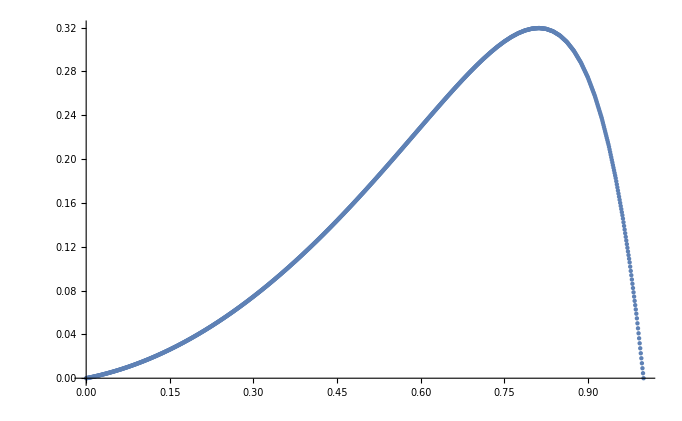
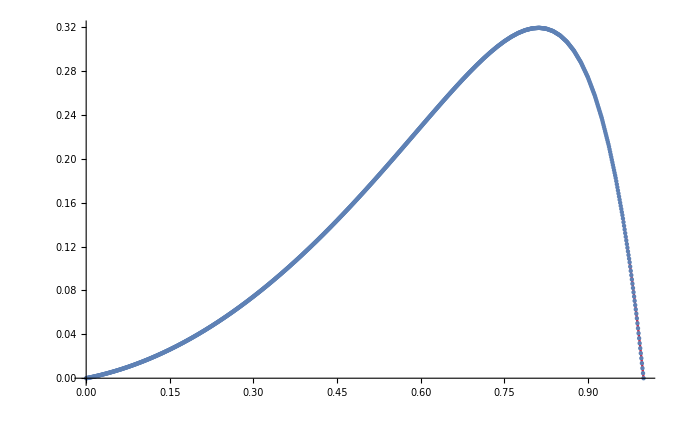
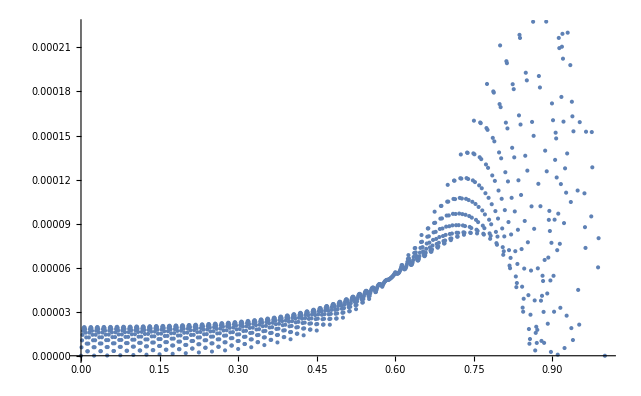

```mathematica
list={{0,0},{0.001,0.000105963},{0.002,0.000211926},{0.003,0.00031789},{0.004,0.000423853},{0.005,0.000529816},{0.006,0.000635779},{0.007,0.000741742},{0.008,0.000847706},{0.009,0.000953669},{0.01,0.00105963},{0.011,0.0011656},{0.012,0.00127156},{0.013,0.00138375},{0.014,0.00150218},{0.015,0.0016206},{0.016,0.00173903},{0.017,0.00185745},{0.018,0.00197588},{0.019,0.0020943},{0.02,0.00221273},{0.021,0.00233115},{0.022,0.00244958},{0.023,0.002568},{0.024,0.00268643},{0.025,0.00280485},{0.026,0.00293573},{0.027,0.00306662},{0.028,0.0031975},{0.029,0.00332838},{0.03,0.00345926},{0.031,0.00359014},{0.032,0.00372102},{0.033,0.0038519},{0.034,0.00398279},{0.035,0.00411367},{0.036,0.00424455},{0.037,0.00437543},{0.038,0.00451254},{0.039,0.00465587},{0.04,0.0047992},{0.041,0.00494254},{0.042,0.00508587},{0.043,0.0052292},{0.044,0.00537253},{0.045,0.00551587},{0.046,0.0056592},{0.047,0.00580253},{0.048,0.00594586},{0.049,0.0060892},{0.05,0.00623253},{0.051,0.00638831},{0.052,0.00654408},{0.053,0.00669986},{0.054,0.00685564},{0.055,0.00701141},{0.056,0.00716719},{0.057,0.00732297},{0.058,0.00747874},{0.059,0.00763452},{0.06,0.0077903},{0.061,0.00794607},{0.062,0.00810185},{0.063,0.00826385},{0.064,0.00843206},{0.065,0.00860027},{0.066,0.00876849},{0.067,0.0089367},{0.068,0.00910491},{0.069,0.00927313},{0.07,0.00944134},{0.071,0.00960956},{0.072,0.00977777},{0.073,0.00994598},{0.074,0.0101142},{0.075,0.0102824},{0.076,0.0104631},{0.077,0.0106437},{0.078,0.0108243},{0.079,0.011005},{0.08,0.0111856},{0.081,0.0113663},{0.082,0.0115469},{0.083,0.0117275},{0.084,0.0119082},{0.085,0.0120888},{0.086,0.0122695},{0.087,0.0124501},{0.088,0.012637},{0.089,0.01283},{0.09,0.0130231},{0.091,0.0132162},{0.092,0.0134092},{0.093,0.0136023},{0.094,0.0137953},{0.095,0.0139884},{0.096,0.0141815},{0.097,0.0143745},{0.098,0.0145676},{0.099,0.0147606},{0.1,0.0149537},{0.101,0.0151592},{0.102,0.0153646},{0.103,0.0155701},{0.104,0.0157756},{0.105,0.0159811},{0.106,0.0161865},{0.107,0.016392},{0.108,0.0165975},{0.109,0.0168029},{0.11,0.0170084},{0.111,0.0172139},{0.112,0.0174193},{0.113,0.017631},{0.114,0.0178489},{0.115,0.0180667},{0.116,0.0182846},{0.117,0.0185025},{0.118,0.0187203},{0.119,0.0189382},{0.12,0.0191561},{0.121,0.0193739},{0.122,0.0195918},{0.123,0.0198097},{0.124,0.0200275},{0.125,0.0202454},{0.126,0.0204756},{0.127,0.0207059},{0.128,0.0209361},{0.129,0.0211664},{0.13,0.0213966},{0.131,0.0216269},{0.132,0.0218571},{0.133,0.0220874},{0.134,0.0223176},{0.135,0.0225479},{0.136,0.0227781},{0.137,0.0230084},{0.138,0.0232448},{0.139,0.0234874},{0.14,0.02373},{0.141,0.0239726},{0.142,0.0242152},{0.143,0.0244579},{0.144,0.0247005},{0.145,0.0249431},{0.146,0.0251857},{0.147,0.0254283},{0.148,0.0256709},{0.149,0.0259135},{0.15,0.0261561},{0.151,0.0264111},{0.152,0.0266661},{0.153,0.026921},{0.154,0.027176},{0.155,0.027431},{0.156,0.0276859},{0.157,0.0279409},{0.158,0.0281958},{0.159,0.0284508},{0.16,0.0287058},{0.161,0.0289607},{0.162,0.0292157},{0.163,0.0294768},{0.164,0.0297441},{0.165,0.0300114},{0.166,0.0302787},{0.167,0.030546},{0.168,0.0308133},{0.169,0.0310806},{0.17,0.0313479},{0.171,0.0316151},{0.172,0.0318824},{0.173,0.0321497},{0.174,0.032417},{0.175,0.0326843},{0.176,0.0329639},{0.177,0.0332435},{0.178,0.0335231},{0.179,0.0338027},{0.18,0.0340823},{0.181,0.0343619},{0.182,0.0346415},{0.183,0.0349211},{0.184,0.0352007},{0.185,0.0354803},{0.186,0.0357599},{0.187,0.0360395},{0.188,0.0363252},{0.189,0.0366171},{0.19,0.0369089},{0.191,0.0372008},{0.192,0.0374927},{0.193,0.0377846},{0.194,0.0380764},{0.195,0.0383683},{0.196,0.0386602},{0.197,0.0389521},{0.198,0.0392439},{0.199,0.0395358},{0.2,0.0398277},{0.201,0.0401318},{0.202,0.0404359},{0.203,0.0407401},{0.204,0.0410442},{0.205,0.0413483},{0.206,0.0416524},{0.207,0.0419566},{0.208,0.0422607},{0.209,0.0425648},{0.21,0.0428689},{0.211,0.0431731},{0.212,0.0434772},{0.213,0.0437874},{0.214,0.0441038},{0.215,0.0444201},{0.216,0.0447365},{0.217,0.0450528},{0.218,0.0453691},{0.219,0.0456855},{0.22,0.0460018},{0.221,0.0463182},{0.222,0.0466345},{0.223,0.0469508},{0.224,0.0472672},{0.225,0.0475835},{0.226,0.0479121},{0.227,0.0482406},{0.228,0.0485691},{0.229,0.0488976},{0.23,0.0492261},{0.231,0.0495547},{0.232,0.0498832},{0.233,0.0502117},{0.234,0.0505402},{0.235,0.0508687},{0.236,0.0511973},{0.237,0.0515258},{0.238,0.0518604},{0.239,0.052201},{0.24,0.0525417},{0.241,0.0528823},{0.242,0.053223},{0.243,0.0535637},{0.244,0.0539043},{0.245,0.054245},{0.246,0.0545856},{0.247,0.0549263},{0.248,0.0552669},{0.249,0.0556076},{0.25,0.0559483},{0.251,0.056301},{0.252,0.0566537},{0.253,0.0570065},{0.254,0.0573592},{0.255,0.057712},{0.256,0.0580647},{0.257,0.0584175},{0.258,0.0587702},{0.259,0.059123},{0.26,0.0594757},{0.261,0.0598284},{0.262,0.0601812},{0.263,0.06054},{0.264,0.0609047},{0.265,0.0612695},{0.266,0.0616343},{0.267,0.0619991},{0.268,0.0623638},{0.269,0.0627286},{0.27,0.0630934},{0.271,0.0634582},{0.272,0.0638229},{0.273,0.0641877},{0.274,0.0645525},{0.275,0.0649173},{0.276,0.065294},{0.277,0.0656708},{0.278,0.0660475},{0.279,0.0664243},{0.28,0.066801},{0.281,0.0671778},{0.282,0.0675545},{0.283,0.0679313},{0.284,0.068308},{0.285,0.0686848},{0.286,0.0690615},{0.287,0.0694382},{0.288,0.0698209},{0.289,0.0702096},{0.29,0.0705982},{0.291,0.0709869},{0.292,0.0713755},{0.293,0.0717642},{0.294,0.0721528},{0.295,0.0725415},{0.296,0.0729301},{0.297,0.0733188},{0.298,0.0737074},{0.299,0.0740961},{0.3,0.0744847},{0.301,0.0748852},{0.302,0.0752856},{0.303,0.0756861},{0.304,0.0760866},{0.305,0.076487},{0.306,0.0768875},{0.307,0.077288},{0.308,0.0776884},{0.309,0.0780889},{0.31,0.0784894},{0.311,0.0788898},{0.312,0.0792903},{0.313,0.0796966},{0.314,0.0801088},{0.315,0.080521},{0.316,0.0809332},{0.317,0.0813454},{0.318,0.0817576},{0.319,0.0821698},{0.32,0.082582},{0.321,0.0829942},{0.322,0.0834064},{0.323,0.0838186},{0.324,0.0842308},{0.325,0.084643},{0.326,0.0850668},{0.327,0.0854906},{0.328,0.0859145},{0.329,0.0863383},{0.33,0.0867621},{0.331,0.0871859},{0.332,0.0876097},{0.333,0.0880336},{0.334,0.0884574},{0.335,0.0888812},{0.336,0.089305},{0.337,0.0897289},{0.338,0.0901584},{0.339,0.0905938},{0.34,0.0910291},{0.341,0.0914644},{0.342,0.0918998},{0.343,0.0923351},{0.344,0.0927704},{0.345,0.0932057},{0.346,0.0936411},{0.347,0.0940764},{0.348,0.0945117},{0.349,0.0949471},{0.35,0.0953824},{0.351,0.0958291},{0.352,0.0962758},{0.353,0.0967225},{0.354,0.0971692},{0.355,0.0976159},{0.356,0.0980627},{0.357,0.0985094},{0.358,0.0989561},{0.359,0.0994028},{0.36,0.0998495},{0.361,0.100296},{0.362,0.100743},{0.363,0.101195},{0.364,0.101653},{0.365,0.102111},{0.366,0.102569},{0.367,0.103027},{0.368,0.103485},{0.369,0.103943},{0.37,0.104401},{0.371,0.104859},{0.372,0.105317},{0.373,0.105775},{0.374,0.106233},{0.375,0.10669},{0.376,0.107159},{0.377,0.107628},{0.378,0.108097},{0.379,0.108566},{0.38,0.109035},{0.381,0.109504},{0.382,0.109973},{0.383,0.110442},{0.384,0.110911},{0.385,0.11138},{0.386,0.111849},{0.387,0.112318},{0.388,0.112793},{0.389,0.113273},{0.39,0.113753},{0.391,0.114232},{0.392,0.114712},{0.393,0.115192},{0.394,0.115672},{0.395,0.116152},{0.396,0.116632},{0.397,0.117112},{0.398,0.117591},{0.399,0.118071},{0.4,0.118551},{0.401,0.119042},{0.402,0.119532},{0.403,0.120023},{0.404,0.120513},{0.405,0.121004},{0.406,0.121494},{0.407,0.121985},{0.408,0.122475},{0.409,0.122966},{0.41,0.123456},{0.411,0.123947},{0.412,0.124437},{0.413,0.124933},{0.414,0.125434},{0.415,0.125935},{0.416,0.126436},{0.417,0.126937},{0.418,0.127438},{0.419,0.127938},{0.42,0.128439},{0.421,0.12894},{0.422,0.129441},{0.423,0.129942},{0.424,0.130443},{0.425,0.130944},{0.426,0.131455},{0.427,0.131966},{0.428,0.132477},{0.429,0.132988},{0.43,0.133499},{0.431,0.13401},{0.432,0.134521},{0.433,0.135032},{0.434,0.135543},{0.435,0.136054},{0.436,0.136565},{0.437,0.137076},{0.438,0.137592},{0.439,0.138113},{0.44,0.138634},{0.441,0.139155},{0.442,0.139676},{0.443,0.140196},{0.444,0.140717},{0.445,0.141238},{0.446,0.141759},{0.447,0.14228},{0.448,0.142801},{0.449,0.143321},{0.45,0.143842},{0.451,0.144373},{0.452,0.144903},{0.453,0.145433},{0.454,0.145963},{0.455,0.146494},{0.456,0.147024},{0.457,0.147554},{0.458,0.148084},{0.459,0.148615},{0.46,0.149145},{0.461,0.149675},{0.462,0.150206},{0.463,0.15074},{0.464,0.15128},{0.465,0.151819},{0.466,0.152358},{0.467,0.152898},{0.468,0.153437},{0.469,0.153976},{0.47,0.154516},{0.471,0.155055},{0.472,0.155594},{0.473,0.156134},{0.474,0.156673},{0.475,0.157212},{0.476,0.15776},{0.477,0.158308},{0.478,0.158856},{0.479,0.159404},{0.48,0.159952},{0.481,0.1605},{0.482,0.161047},{0.483,0.161595},{0.484,0.162143},{0.485,0.162691},{0.486,0.163239},{0.487,0.163787},{0.488,0.164339},{0.489,0.164895},{0.49,0.165451},{0.491,0.166007},{0.492,0.166563},{0.493,0.167119},{0.494,0.167675},{0.495,0.168231},{0.496,0.168786},{0.497,0.169342},{0.498,0.169898},{0.499,0.170454},{0.5,0.17101},{0.501,0.171574},{0.502,0.172137},{0.503,0.1727},{0.504,0.173264},{0.505,0.173827},{0.506,0.174391},{0.507,0.174954},{0.508,0.175517},{0.509,0.176081},{0.51,0.176644},{0.511,0.177208},{0.512,0.177771},{0.513,0.178338},{0.514,0.178908},{0.515,0.179478},{0.516,0.180048},{0.517,0.180619},{0.518,0.181189},{0.519,0.181759},{0.52,0.182329},{0.521,0.182899},{0.522,0.18347},{0.523,0.18404},{0.524,0.18461},{0.525,0.18518},{0.526,0.185756},{0.527,0.186333},{0.528,0.186909},{0.529,0.187485},{0.53,0.188061},{0.531,0.188638},{0.532,0.189214},{0.533,0.18979},{0.534,0.190366},{0.535,0.190942},{0.536,0.191519},{0.537,0.192095},{0.538,0.192674},{0.539,0.193255},{0.54,0.193836},{0.541,0.194418},{0.542,0.194999},{0.543,0.195581},{0.544,0.196162},{0.545,0.196743},{0.546,0.197325},{0.547,0.197906},{0.548,0.198487},{0.549,0.199069},{0.55,0.19965},{0.551,0.200236},{0.552,0.200821},{0.553,0.201407},{0.554,0.201992},{0.555,0.202578},{0.556,0.203164},{0.557,0.203749},{0.558,0.204335},{0.559,0.20492},{0.56,0.205506},{0.561,0.206091},{0.562,0.206677},{0.563,0.207264},{0.564,0.207853},{0.565,0.208441},{0.566,0.20903},{0.567,0.209619},{0.568,0.210207},{0.569,0.210796},{0.57,0.211385},{0.571,0.211973},{0.572,0.212562},{0.573,0.213151},{0.574,0.213739},{0.575,0.214328},{0.576,0.214918},{0.577,0.215509},{0.578,0.216099},{0.579,0.21669},{0.58,0.21728},{0.581,0.217871},{0.582,0.218461},{0.583,0.219051},{0.584,0.219642},{0.585,0.220232},{0.586,0.220823},{0.587,0.221413},{0.588,0.222004},{0.589,0.222595},{0.59,0.223186},{0.591,0.223777},{0.592,0.224367},{0.593,0.224958},{0.594,0.225549},{0.595,0.22614},{0.596,0.226731},{0.597,0.227322},{0.598,0.227913},{0.599,0.228503},{0.6,0.229094},{0.601,0.229684},{0.602,0.230274},{0.603,0.230863},{0.604,0.231453},{0.605,0.232042},{0.606,0.232632},{0.607,0.233222},{0.608,0.233811},{0.609,0.234401},{0.61,0.234991},{0.611,0.23558},{0.612,0.23617},{0.613,0.236758},{0.614,0.237345},{0.615,0.237931},{0.616,0.238518},{0.617,0.239104},{0.618,0.239691},{0.619,0.240277},{0.62,0.240864},{0.621,0.241451},{0.622,0.242037},{0.623,0.242624},{0.624,0.24321},{0.625,0.243797},{0.626,0.244378},{0.627,0.24496},{0.628,0.245541},{0.629,0.246123},{0.63,0.246704},{0.631,0.247286},{0.632,0.247867},{0.633,0.248449},{0.634,0.24903},{0.635,0.249612},{0.636,0.250193},{0.637,0.250775},{0.638,0.251352},{0.639,0.251926},{0.64,0.2525},{0.641,0.253074},{0.642,0.253648},{0.643,0.254222},{0.644,0.254796},{0.645,0.25537},{0.646,0.255944},{0.647,0.256518},{0.648,0.257092},{0.649,0.257666},{0.65,0.25824},{0.651,0.258804},{0.652,0.259368},{0.653,0.259932},{0.654,0.260496},{0.655,0.26106},{0.656,0.261623},{0.657,0.262187},{0.658,0.262751},{0.659,0.263315},{0.66,0.263879},{0.661,0.264443},{0.662,0.265007},{0.663,0.265564},{0.664,0.266115},{0.665,0.266665},{0.666,0.267216},{0.667,0.267767},{0.668,0.268317},{0.669,0.268868},{0.67,0.269419},{0.671,0.269969},{0.672,0.27052},{0.673,0.271071},{0.674,0.271622},{0.675,0.272172},{0.676,0.272706},{0.677,0.273241},{0.678,0.273775},{0.679,0.274309},{0.68,0.274843},{0.681,0.275377},{0.682,0.275911},{0.683,0.276445},{0.684,0.27698},{0.685,0.277514},{0.686,0.278048},{0.687,0.278582},{0.688,0.279106},{0.689,0.27962},{0.69,0.280133},{0.691,0.280647},{0.692,0.281161},{0.693,0.281674},{0.694,0.282188},{0.695,0.282702},{0.696,0.283215},{0.697,0.283729},{0.698,0.284243},{0.699,0.284756},{0.7,0.28527},{0.701,0.285759},{0.702,0.286248},{0.703,0.286737},{0.704,0.287225},{0.705,0.287714},{0.706,0.288203},{0.707,0.288692},{0.708,0.289181},{0.709,0.28967},{0.71,0.290158},{0.711,0.290647},{0.712,0.291136},{0.713,0.29161},{0.714,0.292069},{0.715,0.292528},{0.716,0.292987},{0.717,0.293446},{0.718,0.293905},{0.719,0.294364},{0.72,0.294823},{0.721,0.295282},{0.722,0.295741},{0.723,0.2962},{0.724,0.296659},{0.725,0.297118},{0.726,0.297542},{0.727,0.297965},{0.728,0.298389},{0.729,0.298813},{0.73,0.299236},{0.731,0.29966},{0.732,0.300083},{0.733,0.300507},{0.734,0.30093},{0.735,0.301354},{0.736,0.301778},{0.737,0.302201},{0.738,0.302604},{0.739,0.302985},{0.74,0.303367},{0.741,0.303749},{0.742,0.304131},{0.743,0.304512},{0.744,0.304894},{0.745,0.305276},{0.746,0.305657},{0.747,0.306039},{0.748,0.306421},{0.749,0.306802},{0.75,0.307184},{0.751,0.307517},{0.752,0.307849},{0.753,0.308182},{0.754,0.308515},{0.755,0.308847},{0.756,0.30918},{0.757,0.309512},{0.758,0.309845},{0.759,0.310177},{0.76,0.31051},{0.761,0.310843},{0.762,0.311175},{0.763,0.311479},{0.764,0.311754},{0.765,0.31203},{0.766,0.312305},{0.767,0.31258},{0.768,0.312856},{0.769,0.313131},{0.77,0.313406},{0.771,0.313681},{0.772,0.313957},{0.773,0.314232},{0.774,0.314507},{0.775,0.314782},{0.776,0.314991},{0.777,0.3152},{0.778,0.315408},{0.779,0.315617},{0.78,0.315826},{0.781,0.316034},{0.782,0.316243},{0.783,0.316452},{0.784,0.31666},{0.785,0.316869},{0.786,0.317078},{0.787,0.317286},{0.788,0.317456},{0.789,0.317588},{0.79,0.317719},{0.791,0.317851},{0.792,0.317982},{0.793,0.318114},{0.794,0.318245},{0.795,0.318376},{0.796,0.318508},{0.797,0.318639},{0.798,0.318771},{0.799,0.318902},{0.8,0.319034},{0.801,0.319076},{0.802,0.319118},{0.803,0.319161},{0.804,0.319203},{0.805,0.319245},{0.806,0.319288},{0.807,0.31933},{0.808,0.319372},{0.809,0.319415},{0.81,0.319457},{0.811,0.319499},{0.812,0.319542},{0.813,0.319533},{0.814,0.319472},{0.815,0.319412},{0.816,0.319352},{0.817,0.319291},{0.818,0.319231},{0.819,0.31917},{0.82,0.31911},{0.821,0.31905},{0.822,0.318989},{0.823,0.318929},{0.824,0.318869},{0.825,0.318808},{0.826,0.31863},{0.827,0.318451},{0.828,0.318273},{0.829,0.318095},{0.83,0.317916},{0.831,0.317738},{0.832,0.317559},{0.833,0.317381},{0.834,0.317202},{0.835,0.317024},{0.836,0.316846},{0.837,0.316667},{0.838,0.316421},{0.839,0.316107},{0.84,0.315793},{0.841,0.315479},{0.842,0.315166},{0.843,0.314852},{0.844,0.314538},{0.845,0.314224},{0.846,0.31391},{0.847,0.313596},{0.848,0.313282},{0.849,0.312969},{0.85,0.312655},{0.851,0.312186},{0.852,0.311717},{0.853,0.311247},{0.854,0.310778},{0.855,0.310309},{0.856,0.30984},{0.857,0.309371},{0.858,0.308902},{0.859,0.308433},{0.86,0.307964},{0.861,0.307495},{0.862,0.307026},{0.863,0.306468},{0.864,0.305822},{0.865,0.305175},{0.866,0.304528},{0.867,0.303882},{0.868,0.303235},{0.869,0.302589},{0.87,0.301942},{0.871,0.301295},{0.872,0.300649},{0.873,0.300002},{0.874,0.299356},{0.875,0.298709},{0.876,0.29786},{0.877,0.29701},{0.878,0.296161},{0.879,0.295311},{0.88,0.294462},{0.881,0.293612},{0.882,0.292763},{0.883,0.291913},{0.884,0.291064},{0.885,0.290214},{0.886,0.289365},{0.887,0.288515},{0.888,0.28755},{0.889,0.286469},{0.89,0.285388},{0.891,0.284307},{0.892,0.283226},{0.893,0.282145},{0.894,0.281064},{0.895,0.279983},{0.896,0.278902},{0.897,0.27782},{0.898,0.276739},{0.899,0.275658},{0.9,0.274577},{0.901,0.273232},{0.902,0.271887},{0.903,0.270542},{0.904,0.269196},{0.905,0.267851},{0.906,0.266506},{0.907,0.265161},{0.908,0.263816},{0.909,0.26247},{0.91,0.261125},{0.911,0.25978},{0.912,0.258435},{0.913,0.256939},{0.914,0.255293},{0.915,0.253646},{0.916,0.252},{0.917,0.250354},{0.918,0.248708},{0.919,0.247062},{0.92,0.245415},{0.921,0.243769},{0.922,0.242123},{0.923,0.240477},{0.924,0.23883},{0.925,0.237184},{0.926,0.235195},{0.927,0.233206},{0.928,0.231217},{0.929,0.229228},{0.93,0.227239},{0.931,0.22525},{0.932,0.223261},{0.933,0.221271},{0.934,0.219282},{0.935,0.217293},{0.936,0.215304},{0.937,0.213315},{0.938,0.211131},{0.939,0.208752},{0.94,0.206372},{0.941,0.203993},{0.942,0.201614},{0.943,0.199235},{0.944,0.196855},{0.945,0.194476},{0.946,0.192097},{0.947,0.189717},{0.948,0.187338},{0.949,0.184959},{0.95,0.18258},{0.951,0.179756},{0.952,0.176933},{0.953,0.17411},{0.954,0.171287},{0.955,0.168464},{0.956,0.16564},{0.957,0.162817},{0.958,0.159994},{0.959,0.157171},{0.96,0.154348},{0.961,0.151525},{0.962,0.148701},{0.963,0.145626},{0.964,0.142298},{0.965,0.13897},{0.966,0.135642},{0.967,0.132314},{0.968,0.128986},{0.969,0.125658},{0.97,0.12233},{0.971,0.119002},{0.972,0.115674},{0.973,0.112346},{0.974,0.109018},{0.975,0.10569},{0.976,0.101789},{0.977,0.0978871},{0.978,0.0939854},{0.979,0.0900837},{0.98,0.0861821},{0.981,0.0822804},{0.982,0.0783787},{0.983,0.074477},{0.984,0.0705754},{0.985,0.0666737},{0.986,0.062772},{0.987,0.0588704},{0.988,0.0546427},{0.989,0.0500892},{0.99,0.0455356},{0.991,0.0409821},{0.992,0.0364285},{0.993,0.0318749},{0.994,0.0273214},{0.995,0.0227678},{0.996,0.0182142},{0.997,0.0136607},{0.998,0.00910712},{0.999,0.00455356},{1,0}};
error={{0,0*10^(0)},{0.001,5.73697*10^(-6)},{0.002,1.04767*10^(-5)},{0.003,1.42192*10^(-5)},{0.004,1.69645*10^(-5)},{0.005,1.87127*10^(-5)},{0.006,1.94637*10^(-5)},{0.007,1.92176*10^(-5)},{0.008,1.79744*10^(-5)},{0.009,1.57342*10^(-5)},{0.01,1.24969*10^(-5)},{0.011,8.2627*10^(-6)},{0.012,3.03151*10^(-6)},{0.013,3.03427*10^(-6)},{0.014,8.27101*10^(-6)},{0.015,1.25109*10^(-5)},{0.016,1.57539*10^(-5)},{0.017,1.80002*10^(-5)},{0.018,1.92496*10^(-5)},{0.019,1.95024*10^(-5)},{0.02,1.87584*10^(-5)},{0.021,1.70177*10^(-5)},{0.022,1.42804*10^(-5)},{0.023,1.05465*10^(-5)},{0.024,5.81607*10^(-6)},{0.025,8.9063*10^(-8)},{0.026,5.82222*10^(-6)},{0.027,1.05589*10^(-5)},{0.028,1.42992*10^(-5)},{0.029,1.7043*10^(-5)},{0.03,1.87905*10^(-5)},{0.031,1.95417*10^(-5)},{0.032,1.92966*10^(-5)},{0.033,1.80552*10^(-5)},{0.034,1.58177*10^(-5)},{0.035,1.25839*10^(-5)},{0.036,8.35405*10^(-6)},{0.037,3.12808*10^(-6)},{0.038,3.13149*10^(-6)},{0.039,8.36433*10^(-6)},{0.04,1.26012*10^(-5)},{0.041,1.58421*10^(-5)},{0.042,1.80872*10^(-5)},{0.043,1.93363*10^(-5)},{0.044,1.95897*10^(-5)},{0.045,1.88473*10^(-5)},{0.046,1.71092*10^(-5)},{0.047,1.43753*10^(-5)},{0.048,1.06459*10^(-5)},{0.049,5.92083*10^(-6)},{0.05,2.00217*10^(-7)},{0.051,5.92843*10^(-6)},{0.052,1.06612*10^(-5)},{0.053,1.43985*10^(-5)},{0.054,1.71405*10^(-5)},{0.055,1.88871*10^(-5)},{0.056,1.96385*10^(-5)},{0.057,1.93946*10^(-5)},{0.058,1.81555*10^(-5)},{0.059,1.59214*10^(-5)},{0.06,1.26921*10^(-5)},{0.061,8.46776*10^(-6)},{0.062,3.24846*10^(-6)},{0.063,3.25268*10^(-6)},{0.064,8.48047*10^(-6)},{0.065,1.27134*10^(-5)},{0.066,1.59516*10^(-5)},{0.067,1.8195*10^(-5)},{0.068,1.94438*10^(-5)},{0.069,1.9698*10^(-5)},{0.07,1.89575*10^(-5)},{0.071,1.72226*10^(-5)},{0.072,1.44932*10^(-5)},{0.073,1.07694*10^(-5)},{0.074,6.05126*10^(-6)},{0.075,3.38826*10^(-7)},{0.076,6.06066*10^(-6)},{0.077,1.07883*10^(-5)},{0.078,1.45218*10^(-5)},{0.079,1.72613*10^(-5)},{0.08,1.90068*10^(-5)},{0.081,1.97584*10^(-5)},{0.082,1.9516*10^(-5)},{0.083,1.82799*10^(-5)},{0.084,1.605*10^(-5)},{0.085,1.28264*10^(-5)},{0.086,8.60917*10^(-6)},{0.087,3.39839*10^(-6)},{0.088,3.4036*10^(-6)},{0.089,8.62486*10^(-6)},{0.09,1.28528*10^(-5)},{0.091,1.60873*10^(-5)},{0.092,1.83287*10^(-5)},{0.093,1.95769*10^(-5)},{0.094,1.9832*10^(-5)},{0.095,1.90941*10^(-5)},{0.096,1.73632*10^(-5)},{0.097,1.46394*10^(-5)},{0.098,1.09228*10^(-5)},{0.099,6.21351*10^(-6)},{0.1,5.11516*10^(-7)},{0.101,6.22509*10^(-6)},{0.102,1.09461*10^(-5)},{0.103,1.46747*10^(-5)},{0.104,1.7411*10^(-5)},{0.105,1.91549*10^(-5)},{0.106,1.99067*10^(-5)},{0.107,1.96663*10^(-5)},{0.108,1.84338*10^(-5)},{0.109,1.62093*10^(-5)},{0.11,1.2993*10^(-5)},{0.111,8.78484*10^(-6)},{0.112,3.58495*10^(-6)},{0.113,3.59136*10^(-6)},{0.114,8.80417*10^(-6)},{0.115,1.30255*10^(-5)},{0.116,1.62554*10^(-5)},{0.117,1.8494*10^(-5)},{0.118,1.97414*10^(-5)},{0.119,1.99977*10^(-5)},{0.12,1.92629*10^(-5)},{0.121,1.75372*10^(-5)},{0.122,1.48205*10^(-5)},{0.123,1.11132*10^(-5)},{0.124,6.41511*10^(-6)},{0.125,7.26463*10^(-7)},{0.126,6.42936*10^(-6)},{0.127,1.11419*10^(-5)},{0.128,1.48641*10^(-5)},{0.129,1.75961*10^(-5)},{0.13,1.9338*10^(-5)},{0.131,2.00899*10^(-5)},{0.132,1.98519*10^(-5)},{0.133,1.8624*10^(-5)},{0.134,1.64065*10^(-5)},{0.135,1.31994*10^(-5)},{0.136,9.00281*10^(-6)},{0.137,3.81683*10^(-6)},{0.138,3.82471*10^(-6)},{0.139,9.02658*10^(-6)},{0.14,1.32394*10^(-5)},{0.141,1.64632*10^(-5)},{0.142,1.86983*10^(-5)},{0.143,1.99445*10^(-5)},{0.144,2.02022*10^(-5)},{0.145,1.94714*10^(-5)},{0.146,1.77521*10^(-5)},{0.147,1.50447*10^(-5)},{0.148,1.1349*10^(-5)},{0.149,6.66533*10^(-6)},{0.15,9.93738*10^(-7)},{0.151,6.68284*10^(-6)},{0.152,1.13843*10^(-5)},{0.153,1.50982*10^(-5)},{0.154,1.78246*10^(-5)},{0.155,1.95638*10^(-5)},{0.156,2.03158*10^(-5)},{0.157,2.00808*10^(-5)},{0.158,1.88589*10^(-5)},{0.159,1.66502*10^(-5)},{0.16,1.34548*10^(-5)},{0.161,9.27295*10^(-6)},{0.162,4.10472*10^(-6)},{0.163,4.1144*10^(-6)},{0.164,9.30213*10^(-6)},{0.165,1.35039*10^(-5)},{0.166,1.67198*10^(-5)},{0.167,1.89501*10^(-5)},{0.168,2.01949*10^(-5)},{0.169,2.04542*10^(-5)},{0.17,1.97284*10^(-5)},{0.171,1.80174*10^(-5)},{0.172,1.53215*10^(-5)},{0.173,1.16408*10^(-5)},{0.174,6.97552*10^(-6)},{0.175,1.32572*10^(-6)},{0.176,6.99699*10^(-6)},{0.177,1.16841*10^(-5)},{0.178,1.53872*10^(-5)},{0.179,1.81064*10^(-5)},{0.18,1.9842*10^(-5)},{0.181,2.0594*10^(-5)},{0.182,2.03627*10^(-5)},{0.183,1.91482*10^(-5)},{0.184,1.69507*10^(-5)},{0.185,1.37703*10^(-5)},{0.186,9.60729*10^(-6)},{0.187,4.46175*10^(-6)},{0.188,4.47361*10^(-6)},{0.189,9.64303*10^(-6)},{0.19,1.38305*10^(-5)},{0.191,1.70362*10^(-5)},{0.192,1.92602*10^(-5)},{0.193,2.05029*10^(-5)},{0.194,2.07643*10^(-5)},{0.195,2.00447*10^(-5)},{0.196,1.83442*10^(-5)},{0.197,1.5663*10^(-5)},{0.198,1.20014*10^(-5)},{0.199,7.35955*10^(-6)},{0.2,1.73761*10^(-6)},{0.201,7.38581*10^(-6)},{0.202,1.20544*10^(-5)},{0.203,1.57434*10^(-5)},{0.204,1.84532*10^(-5)},{0.205,2.0184*10^(-5)},{0.206,2.09359*10^(-5)},{0.207,2.07092*10^(-5)},{0.208,1.95041*10^(-5)},{0.209,1.73208*10^(-5)},{0.21,1.41596*10^(-5)},{0.211,1.00205*10^(-5)},{0.212,4.90396*10^(-6)},{0.213,4.91844*10^(-6)},{0.214,1.00642*10^(-5)},{0.215,1.42331*10^(-5)},{0.216,1.74254*10^(-5)},{0.217,1.96413*10^(-5)},{0.218,2.08811*10^(-5)},{0.219,2.1145*10^(-5)},{0.22,2.04332*10^(-5)},{0.221,1.8746*10^(-5)},{0.222,1.60836*10^(-5)},{0.223,1.24463*10^(-5)},{0.224,7.83435*10^(-6)},{0.225,2.24799*10^(-6)},{0.226,7.8664*10^(-6)},{0.227,1.25109*10^(-5)},{0.228,1.61818*10^(-5)},{0.229,1.88793*10^(-5)},{0.23,2.06037*10^(-5)},{0.231,2.13553*10^(-5)},{0.232,2.11343*10^(-5)},{0.233,1.99411*10^(-5)},{0.234,1.77758*10^(-5)},{0.235,1.46389*10^(-5)},{0.236,1.05305*10^(-5)},{0.237,5.45091*10^(-6)},{0.238,5.46855*10^(-6)},{0.239,1.05837*10^(-5)},{0.24,1.47286*10^(-5)},{0.241,1.79034*10^(-5)},{0.242,2.01087*10^(-5)},{0.243,2.13445*10^(-5)},{0.244,2.16113*10^(-5)},{0.245,2.09094*10^(-5)},{0.246,1.9239*10^(-5)},{0.247,1.66005*10^(-5)},{0.248,1.29942*10^(-5)},{0.249,8.42049*10^(-6)},{0.25,2.8796*10^(-6)},{0.251,8.45949*10^(-6)},{0.252,1.30729*10^(-5)},{0.253,1.67202*10^(-5)},{0.254,1.94016*10^(-5)},{0.255,2.11176*10^(-5)},{0.256,2.18685*10^(-5)},{0.257,2.16547*10^(-5)},{0.258,2.04764*10^(-5)},{0.259,1.83341*10^(-5)},{0.26,1.5228*10^(-5)},{0.261,1.11587*10^(-5)},{0.262,6.12642*10^(-6)},{0.263,6.14786*10^(-6)},{0.264,1.12234*10^(-5)},{0.265,1.53371*10^(-5)},{0.266,1.84894*10^(-5)},{0.267,2.06806*10^(-5)},{0.268,2.19111*10^(-5)},{0.269,2.21814*10^(-5)},{0.27,2.14918*10^(-5)},{0.271,1.98428*10^(-5)},{0.272,1.72346*10^(-5)},{0.273,1.36679*10^(-5)},{0.274,9.1429*10^(-6)},{0.275,3.6601*10^(-6)},{0.276,9.1902*10^(-6)},{0.277,1.37633*10^(-5)},{0.278,1.738*10^(-5)},{0.279,2.00405*10^(-5)},{0.28,2.17454*10^(-5)},{0.281,2.24951*10^(-5)},{0.282,2.229*10^(-5)},{0.283,2.11306*10^(-5)},{0.284,1.90174*10^(-5)},{0.285,1.59508*10^(-5)},{0.286,1.19313*10^(-5)},{0.287,6.9594*10^(-6)},{0.288,6.98536*10^(-6)},{0.289,1.20097*10^(-5)},{0.29,1.6083*10^(-5)},{0.291,1.92059*10^(-5)},{0.292,2.13787*10^(-5)},{0.293,2.26021*10^(-5)},{0.294,2.28764*10^(-5)},{0.295,2.22023*10^(-5)},{0.296,2.05803*10^(-5)},{0.297,1.80108*10^(-5)},{0.298,1.44944*10^(-5)},{0.299,1.00317*10^(-5)},{0.3,4.62311*10^(-6)},{0.301,1.00889*10^(-5)},{0.302,1.46099*10^(-5)},{0.303,1.81867*10^(-5)},{0.304,2.082*10^(-5)},{0.305,2.25102*10^(-5)},{0.306,2.32579*10^(-5)},{0.307,2.30637*10^(-5)},{0.308,2.19281*10^(-5)},{0.309,1.98519*10^(-5)},{0.31,1.68355*10^(-5)},{0.311,1.28796*10^(-5)},{0.312,7.98479*10^(-6)},{0.313,8.0161*10^(-6)},{0.314,1.29742*10^(-5)},{0.315,1.69952*10^(-5)},{0.316,2.00798*10^(-5)},{0.317,2.22286*10^(-5)},{0.318,2.34422*10^(-5)},{0.319,2.37214*10^(-5)},{0.32,2.30667*10^(-5)},{0.321,2.14789*10^(-5)},{0.322,1.89585*10^(-5)},{0.323,1.55064*10^(-5)},{0.324,1.11231*10^(-5)},{0.325,5.80934*10^(-6)},{0.326,1.11919*10^(-5)},{0.327,1.56455*10^(-5)},{0.328,1.91708*10^(-5)},{0.329,2.17684*10^(-5)},{0.33,2.34392*10^(-5)},{0.331,2.41838*10^(-5)},{0.332,2.4003*10^(-5)},{0.333,2.28976*10^(-5)},{0.334,2.08683*10^(-5)},{0.335,1.79158*10^(-5)},{0.336,1.4041*10^(-5)},{0.337,9.24466*10^(-6)},{0.338,9.28228*10^(-6)},{0.339,1.41547*10^(-5)},{0.34,1.81079*10^(-5)},{0.341,2.11428*10^(-5)},{0.342,2.32601*10^(-5)},{0.343,2.44607*10^(-5)},{0.344,2.47454*10^(-5)},{0.345,2.4115*10^(-5)},{0.346,2.25705*10^(-5)},{0.347,2.01126*10^(-5)},{0.348,1.67423*10^(-5)},{0.349,1.24604*10^(-5)},{0.35,7.26786*10^(-6)},{0.351,1.2543*10^(-5)},{0.352,1.69093*10^(-5)},{0.353,2.03676*10^(-5)},{0.354,2.29188*10^(-5)},{0.355,2.4564*10^(-5)},{0.356,2.53039*10^(-5)},{0.357,2.51397*10^(-5)},{0.358,2.40722*10^(-5)},{0.359,2.21025*10^(-5)},{0.36,1.92315*10^(-5)},{0.361,1.54601*10^(-5)},{0.362,1.07895*10^(-5)},{0.363,1.08345*10^(-5)},{0.364,1.55961*10^(-5)},{0.365,1.94615*10^(-5)},{0.366,2.24318*10^(-5)},{0.367,2.45078*10^(-5)},{0.368,2.56909*10^(-5)},{0.369,2.59819*10^(-5)},{0.37,2.5382*10^(-5)},{0.371,2.38923*10^(-5)},{0.372,2.15139*10^(-5)},{0.373,1.82479*10^(-5)},{0.374,1.40954*10^(-5)},{0.375,9.05763*10^(-6)},{0.376,1.41939*10^(-5)},{0.377,1.84472*10^(-5)},{0.378,2.18186*10^(-5)},{0.379,2.43094*10^(-5)},{0.38,2.59208*10^(-5)},{0.381,2.66539*10^(-5)},{0.382,2.65101*10^(-5)},{0.383,2.54905*10^(-5)},{0.384,2.35963*10^(-5)},{0.385,2.08289*10^(-5)},{0.386,1.71895*10^(-5)},{0.387,1.26794*10^(-5)},{0.388,1.27329*10^(-5)},{0.389,1.73513*10^(-5)},{0.39,2.1103*10^(-5)},{0.391,2.39892*10^(-5)},{0.392,2.60114*10^(-5)},{0.393,2.71709*10^(-5)},{0.394,2.7469*10^(-5)},{0.395,2.69072*10^(-5)},{0.396,2.54869*10^(-5)},{0.397,2.32095*10^(-5)},{0.398,2.00764*10^(-5)},{0.399,1.60892*10^(-5)},{0.4,1.12491*10^(-5)},{0.401,1.6206*10^(-5)},{0.402,2.0313*10^(-5)},{0.403,2.35718*10^(-5)},{0.404,2.59839*10^(-5)},{0.405,2.75507*10^(-5)},{0.406,2.82739*10^(-5)},{0.407,2.81551*10^(-5)},{0.408,2.71958*10^(-5)},{0.409,2.53975*10^(-5)},{0.41,2.27621*10^(-5)},{0.411,1.9291*10^(-5)},{0.412,1.49859*10^(-5)},{0.413,1.50491*10^(-5)},{0.414,1.94823*10^(-5)},{0.415,2.30866*10^(-5)},{0.416,2.58637*10^(-5)},{0.417,2.78154*10^(-5)},{0.418,2.89433*10^(-5)},{0.419,2.92493*10^(-5)},{0.42,2.87351*10^(-5)},{0.421,2.74027*10^(-5)},{0.422,2.52537*10^(-5)},{0.423,2.229*10^(-5)},{0.424,1.85135*10^(-5)},{0.425,1.39261*10^(-5)},{0.426,1.86511*10^(-5)},{0.427,2.25689*10^(-5)},{0.428,2.56816*10^(-5)},{0.429,2.79911*10^(-5)},{0.43,2.94993*10^(-5)},{0.431,3.02083*10^(-5)},{0.432,3.01201*10^(-5)},{0.433,2.92368*10^(-5)},{0.434,2.75603*10^(-5)},{0.435,2.50928*10^(-5)},{0.436,2.18363*10^(-5)},{0.437,1.7793*10^(-5)},{0.438,1.78672*10^(-5)},{0.439,2.20609*10^(-5)},{0.44,2.54743*10^(-5)},{0.441,2.81096*10^(-5)},{0.442,2.9969*10^(-5)},{0.443,3.10548*10^(-5)},{0.444,3.13693*10^(-5)},{0.445,3.09146*10^(-5)},{0.446,2.96932*10^(-5)},{0.447,2.77075*10^(-5)},{0.448,2.49597*10^(-5)},{0.449,2.14522*10^(-5)},{0.45,1.71876*10^(-5)},{0.451,2.16129*10^(-5)},{0.452,2.52859*10^(-5)},{0.453,2.82091*10^(-5)},{0.454,3.0385*10^(-5)},{0.455,3.18161*10^(-5)},{0.456,3.2505*10^(-5)},{0.457,3.24543*10^(-5)},{0.458,3.16666*10^(-5)},{0.459,3.01445*10^(-5)},{0.46,2.78908*10^(-5)},{0.461,2.4908*10^(-5)},{0.462,2.1199*10^(-5)},{0.463,2.12852*10^(-5)},{0.464,2.51693*10^(-5)},{0.465,2.83355*10^(-5)},{0.466,3.07866*10^(-5)},{0.467,3.25255*10^(-5)},{0.468,3.35551*10^(-5)},{0.469,3.38782*10^(-5)},{0.47,3.34978*10^(-5)},{0.471,3.2417*10^(-5)},{0.472,3.06387*10^(-5)},{0.473,2.81659*10^(-5)},{0.474,2.50018*10^(-5)},{0.475,2.11494*10^(-5)},{0.476,2.51877*10^(-5)},{0.477,2.85439*10^(-5)},{0.478,3.12214*10^(-5)},{0.479,3.32233*10^(-5)},{0.48,3.4553*10^(-5)},{0.481,3.52136*10^(-5)},{0.482,3.52087*10^(-5)},{0.483,3.45414*10^(-5)},{0.484,3.32152*10^(-5)},{0.485,3.12335*10^(-5)},{0.486,2.85998*10^(-5)},{0.487,2.53175*10^(-5)},{0.488,2.54166*10^(-5)},{0.489,2.89005*10^(-5)},{0.49,3.17465*10^(-5)},{0.491,3.39584*10^(-5)},{0.492,3.55398*10^(-5)},{0.493,3.64944*10^(-5)},{0.494,3.68259*10^(-5)},{0.495,3.65382*10^(-5)},{0.496,3.56351*10^(-5)},{0.497,3.41205*10^(-5)},{0.498,3.19981*10^(-5)},{0.499,2.92721*10^(-5)},{0.5,2.59464*10^(-5)},{0.501,2.94844*10^(-5)},{0.502,3.24309*10^(-5)},{0.503,3.47897*10^(-5)},{0.504,3.65652*10^(-5)},{0.505,3.77615*10^(-5)},{0.506,3.83828*10^(-5)},{0.507,3.84334*10^(-5)},{0.508,3.79177*10^(-5)},{0.509,3.68399*10^(-5)},{0.51,3.52044*10^(-5)},{0.511,3.30158*10^(-5)},{0.512,3.02785*10^(-5)},{0.513,3.03908*10^(-5)},{0.514,3.33572*10^(-5)},{0.515,3.57887*10^(-5)},{0.516,3.76898*10^(-5)},{0.517,3.90655*10^(-5)},{0.518,3.99203*10^(-5)},{0.519,4.02592*10^(-5)},{0.52,4.0087*10^(-5)},{0.521,3.94086*10^(-5)},{0.522,3.82289*10^(-5)},{0.523,3.65531*10^(-5)},{0.524,3.43861*10^(-5)},{0.525,3.17331*10^(-5)},{0.526,3.46249*10^(-5)},{0.527,3.70411*10^(-5)},{0.528,3.89869*10^(-5)},{0.529,4.04677*10^(-5)},{0.53,4.14887*10^(-5)},{0.531,4.20556*10^(-5)},{0.532,4.21736*10^(-5)},{0.533,4.18484*10^(-5)},{0.534,4.10856*10^(-5)},{0.535,3.98908*10^(-5)},{0.536,3.82697*10^(-5)},{0.537,3.62281*10^(-5)},{0.538,3.63531*10^(-5)},{0.539,3.86506*10^(-5)},{0.54,4.05452*10^(-5)},{0.541,4.20429*10^(-5)},{0.542,4.31499*10^(-5)},{0.543,4.38721*10^(-5)},{0.544,4.42159*10^(-5)},{0.545,4.41875*10^(-5)},{0.546,4.37931*10^(-5)},{0.547,4.30391*10^(-5)},{0.548,4.1932*10^(-5)},{0.549,4.04783*10^(-5)},{0.55,3.86846*10^(-5)},{0.551,4.07416*10^(-5)},{0.552,4.24718*10^(-5)},{0.553,4.38822*10^(-5)},{0.554,4.49793*10^(-5)},{0.555,4.57703*10^(-5)},{0.556,4.6262*10^(-5)},{0.557,4.64616*10^(-5)},{0.558,4.6376*10^(-5)},{0.559,4.60125*10^(-5)},{0.56,4.53784*10^(-5)},{0.561,4.44809*10^(-5)},{0.562,4.33276*10^(-5)},{0.563,4.34635*10^(-5)},{0.564,4.48962*10^(-5)},{0.565,4.60956*10^(-5)},{0.566,4.70696*10^(-5)},{0.567,4.78257*10^(-5)},{0.568,4.8372*10^(-5)},{0.569,4.87162*10^(-5)},{0.57,4.88666*10^(-5)},{0.571,4.88311*10^(-5)},{0.572,4.86179*10^(-5)},{0.573,4.82354*10^(-5)},{0.574,4.76918*10^(-5)},{0.575,4.69955*10^(-5)},{0.576,4.7974*10^(-5)},{0.577,4.8817*10^(-5)},{0.578,4.95332*10^(-5)},{0.579,5.01313*10^(-5)},{0.58,5.06203*10^(-5)},{0.581,5.1009*10^(-5)},{0.582,5.13066*10^(-5)},{0.583,5.15221*10^(-5)},{0.584,5.16648*10^(-5)},{0.585,5.17441*10^(-5)},{0.586,5.17692*10^(-5)},{0.587,5.17498*10^(-5)},{0.588,5.18927*10^(-5)},{0.589,5.22076*10^(-5)},{0.59,5.25071*10^(-5)},{0.591,5.2801*10^(-5)},{0.592,5.30993*10^(-5)},{0.593,5.34121*10^(-5)},{0.594,5.37496*10^(-5)},{0.595,5.4122*10^(-5)},{0.596,5.45399*10^(-5)},{0.597,5.50137*10^(-5)},{0.598,5.5554*10^(-5)},{0.599,5.61716*10^(-5)},{0.6,5.68772*10^(-5)},{0.601,5.64624*10^(-5)},{0.602,5.61576*10^(-5)},{0.603,5.59741*10^(-5)},{0.604,5.5923*10^(-5)},{0.605,5.60157*10^(-5)},{0.606,5.62638*10^(-5)},{0.607,5.66789*10^(-5)},{0.608,5.72726*10^(-5)},{0.609,5.80569*10^(-5)},{0.61,5.90437*10^(-5)},{0.611,6.0245*10^(-5)},{0.612,6.16731*10^(-5)},{0.613,6.18161*10^(-5)},{0.614,6.06862*10^(-5)},{0.615,5.98205*10^(-5)},{0.616,5.92317*10^(-5)},{0.617,5.89325*10^(-5)},{0.618,5.8936*10^(-5)},{0.619,5.92552*10^(-5)},{0.62,5.99034*10^(-5)},{0.621,6.08939*10^(-5)},{0.622,6.22403*10^(-5)},{0.623,6.3956*10^(-5)},{0.624,6.6055*10^(-5)},{0.625,6.8551*10^(-5)},{0.626,6.63364*10^(-5)},{0.627,6.45471*10^(-5)},{0.628,6.31974*10^(-5)},{0.629,6.23019*10^(-5)},{0.63,6.18751*10^(-5)},{0.631,6.19318*10^(-5)},{0.632,6.24868*10^(-5)},{0.633,6.35554*10^(-5)},{0.634,6.51526*10^(-5)},{0.635,6.72939*10^(-5)},{0.636,6.99947*10^(-5)},{0.637,7.32707*10^(-5)},{0.638,7.34021*10^(-5)},{0.639,7.04048*10^(-5)},{0.64,6.80307*10^(-5)},{0.641,6.62962*10^(-5)},{0.642,6.52176*10^(-5)},{0.643,6.48117*10^(-5)},{0.644,6.50952*10^(-5)},{0.645,6.60851*10^(-5)},{0.646,6.77986*10^(-5)},{0.647,7.0253*10^(-5)},{0.648,7.34658*10^(-5)},{0.649,7.74547*10^(-5)},{0.65,8.22374*10^(-5)},{0.651,7.76979*10^(-5)},{0.652,7.39885*10^(-5)},{0.653,7.11276*10^(-5)},{0.654,6.91339*10^(-5)},{0.655,6.80261*10^(-5)},{0.656,6.78231*10^(-5)},{0.657,6.8544*10^(-5)},{0.658,7.02083*10^(-5)},{0.659,7.28355*10^(-5)},{0.66,7.64452*10^(-5)},{0.661,8.10575*10^(-5)},{0.662,8.66923*10^(-5)},{0.663,8.67941*10^(-5)},{0.664,8.13833*10^(-5)},{0.665,7.70567*10^(-5)},{0.666,7.38352*10^(-5)},{0.667,7.17402*10^(-5)},{0.668,7.07928*10^(-5)},{0.669,7.10147*10^(-5)},{0.67,7.24276*10^(-5)},{0.671,7.50537*10^(-5)},{0.672,7.89152*10^(-5)},{0.673,8.40344*10^(-5)},{0.674,9.04342*10^(-5)},{0.675,9.81374*10^(-5)},{0.676,9.05947*10^(-5)},{0.677,8.44021*10^(-5)},{0.678,7.95829*10^(-5)},{0.679,7.61612*10^(-5)},{0.68,7.41611*10^(-5)},{0.681,7.36068*10^(-5)},{0.682,7.45229*10^(-5)},{0.683,7.69344*10^(-5)},{0.684,8.08661*10^(-5)},{0.685,8.63436*10^(-5)},{0.686,9.33923*10^(-5)},{0.687,1.02038*10^(-4)},{0.688,1.02083*10^(-4)},{0.689,9.35527*10^(-5)},{0.69,8.66987*10^(-5)},{0.691,8.15479*10^(-5)},{0.692,7.81273*10^(-5)},{0.693,7.64645*10^(-5)},{0.694,7.6587*10^(-5)},{0.695,7.8523*10^(-5)},{0.696,8.23006*10^(-5)},{0.697,8.79485*10^(-5)},{0.698,9.54955*10^(-5)},{0.699,1.04971*10^(-4)},{0.7,1.16404*10^(-4)},{0.701,1.04982*10^(-4)},{0.702,9.55777*10^(-5)},{0.703,8.82212*10^(-5)},{0.704,8.2943*10^(-5)},{0.705,7.97742*10^(-5)},{0.706,7.87459*10^(-5)},{0.707,7.98897*10^(-5)},{0.708,8.32375*10^(-5)},{0.709,8.88215*10^(-5)},{0.71,9.66743*10^(-5)},{0.711,1.06829*10^(-4)},{0.712,1.19318*10^(-4)},{0.713,1.19265*10^(-4)},{0.714,1.06703*10^(-4)},{0.715,9.6578*10^(-5)},{0.716,8.89238*10^(-5)},{0.717,8.37752*10^(-5)},{0.718,8.11677*10^(-5)},{0.719,8.11367*10^(-5)},{0.72,8.37182*10^(-5)},{0.721,8.89484*10^(-5)},{0.722,9.68642*10^(-5)},{0.723,1.07502*10^(-4)},{0.724,1.20901*10^(-4)},{0.725,1.37097*10^(-4)},{0.726,1.20665*10^(-4)},{0.727,1.07107*10^(-4)},{0.728,9.64633*10^(-5)},{0.729,8.87719*10^(-5)},{0.73,8.4073*10^(-5)},{0.731,8.24066*10^(-5)},{0.732,8.38133*10^(-5)},{0.733,8.8334*10^(-5)},{0.734,9.60101*10^(-5)},{0.735,1.06883*10^(-4)},{0.736,1.20996*10^(-4)},{0.737,1.3839*10^(-4)},{0.738,1.3818*10^(-4)},{0.739,1.20409*10^(-4)},{0.74,1.0605*10^(-4)},{0.741,9.51483*10^(-5)},{0.742,8.77476*10^(-5)},{0.743,8.38937*10^(-5)},{0.744,8.36321*10^(-5)},{0.745,8.70091*10^(-5)},{0.746,9.40712*10^(-5)},{0.747,1.04866*10^(-4)},{0.748,1.1944*10^(-4)},{0.749,1.37842*10^(-4)},{0.75,1.6012*10^(-4)},{0.751,1.37217*10^(-4)},{0.752,1.18289*10^(-4)},{0.753,1.03386*10^(-4)},{0.754,9.25583*10^(-5)},{0.755,8.58569*10^(-5)},{0.756,8.33333*10^(-5)},{0.757,8.50398*10^(-5)},{0.758,9.10287*10^(-5)},{0.759,1.01353*10^(-4)},{0.76,1.16067*10^(-4)},{0.761,1.35224*10^(-4)},{0.762,1.58879*10^(-4)},{0.763,1.58427*10^(-4)},{0.764,1.33924*10^(-4)},{0.765,1.14086*10^(-4)},{0.766,9.8971*10^(-5)},{0.767,8.86357*10^(-5)},{0.768,8.31385*10^(-5)},{0.769,8.25381*10^(-5)},{0.77,8.68936*10^(-5)},{0.771,9.6265*10^(-5)},{0.772,1.10713*10^(-4)},{0.773,1.30298*10^(-4)},{0.774,1.55082*10^(-4)},{0.775,1.85127*10^(-4)},{0.776,1.53867*10^(-4)},{0.777,1.27994*10^(-4)},{0.778,1.07574*10^(-4)},{0.779,9.26702*10^(-5)},{0.78,8.33489*10^(-5)},{0.781,7.96762*10^(-5)},{0.782,8.17188*10^(-5)},{0.783,8.95443*10^(-5)},{0.784,1.03221*10^(-4)},{0.785,1.22817*10^(-4)},{0.786,1.48403*10^(-4)},{0.787,1.80049*10^(-4)},{0.788,1.79234*10^(-4)},{0.789,1.46032*10^(-4)},{0.79,1.19104*10^(-4)},{0.791,9.85237*10^(-5)},{0.792,8.43653*10^(-5)},{0.793,7.6703*10^(-5)},{0.794,7.56123*10^(-5)},{0.795,8.11693*10^(-5)},{0.796,9.34507*10^(-5)},{0.797,1.12534*10^(-4)},{0.798,1.38498*10^(-4)},{0.799,1.71422*10^(-4)},{0.8,2.11386*10^(-4)},{0.801,1.69332*10^(-4)},{0.802,1.3448*10^(-4)},{0.803,1.06912*10^(-4)},{0.804,8.67128*10^(-5)},{0.805,7.39651*10^(-5)},{0.806,6.87544*10^(-5)},{0.807,7.11664*10^(-5)},{0.808,8.12877*10^(-5)},{0.809,9.9206*10^(-5)},{0.81,1.2501*10^(-4)},{0.811,1.58788*10^(-4)},{0.812,2.00631*10^(-4)},{0.813,1.99284*10^(-4)},{0.814,1.54841*10^(-4)},{0.815,1.18738*10^(-4)},{0.816,9.10703*10^(-5)},{0.817,7.1932*10^(-5)},{0.818,6.1419*10^(-5)},{0.819,5.96281*10^(-5)},{0.82,6.6657*10^(-5)},{0.821,8.26043*10^(-5)},{0.822,1.0757*10^(-4)},{0.823,1.41654*10^(-4)},{0.824,1.84959*10^(-4)},{0.825,2.37587*10^(-4)},{0.826,1.81593*10^(-4)},{0.827,1.35131*10^(-4)},{0.828,9.83067*10^(-5)},{0.829,7.12269*10^(-5)},{0.83,5.39996*10^(-5)},{0.831,4.67338*10^(-5)},{0.832,4.95399*10^(-5)},{0.833,6.2529*10^(-5)},{0.834,8.58135*10^(-5)},{0.835,1.19507*10^(-4)},{0.836,1.63724*10^(-4)},{0.837,2.18581*10^(-4)},{0.838,2.16466*10^(-4)},{0.839,1.57498*10^(-4)},{0.84,1.09524*10^(-4)},{0.841,7.26641*10^(-5)},{0.842,4.70407*10^(-5)},{0.843,3.27764*10^(-5)},{0.844,2.99956*10^(-5)},{0.845,3.88236*10^(-5)},{0.846,5.93871*10^(-5)},{0.847,9.18142*10^(-5)},{0.848,1.36234*10^(-4)},{0.849,1.92777*10^(-4)},{0.85,2.61576*10^(-4)},{0.851,1.87581*10^(-4)},{0.852,1.26108*10^(-4)},{0.853,7.72944*10^(-5)},{0.854,4.12772*10^(-5)},{0.855,1.81948*10^(-5)},{0.856,8.18744*10^(-6)},{0.857,1.13965*10^(-5)},{0.858,2.79649*10^(-5)},{0.859,5.80368*10^(-5)},{0.86,1.01758*10^(-4)},{0.861,1.59276*10^(-4)},{0.862,2.30739*10^(-4)},{0.863,2.27528*10^(-4)},{0.864,1.49794*10^(-4)},{0.865,8.64596*10^(-5)},{0.866,3.76809*10^(-5)},{0.867,3.61371*10^(-6)},{0.868,1.5584*10^(-5)},{0.869,1.97526*10^(-5)},{0.87,8.73126*10^(-6)},{0.871,1.76429*10^(-5)},{0.872,5.95342*10^(-5)},{0.873,1.17109*10^(-4)},{0.874,1.90534*10^(-4)},{0.875,2.79979*10^(-4)},{0.876,1.82737*10^(-4)},{0.877,1.01858*10^(-4)},{0.878,3.75178*10^(-5)},{0.879,1.01076*10^(-5)},{0.88,4.08402*10^(-5)},{0.881,5.45002*10^(-5)},{0.882,5.09059*10^(-5)},{0.883,2.98739*10^(-5)},{0.884,8.7811*10^(-6)},{0.885,6.52463*10^(-5)},{0.886,1.39711*10^(-4)},{0.887,2.32365*10^(-4)},{0.888,2.27605*10^(-4)},{0.889,1.25624*10^(-4)},{0.89,4.24172*10^(-5)},{0.891,2.18159*10^(-5)},{0.892,6.68749*10^(-5)},{0.893,9.25571*10^(-5)},{0.894,9.86577*10^(-5)},{0.895,8.49698*10^(-5)},{0.896,5.12845*10^(-5)},{0.897,2.60917*10^(-6)},{0.898,7.69244*10^(-5)},{0.899,1.71877*10^(-4)},{0.9,2.87683*10^(-4)},{0.901,1.60421*10^(-4)},{0.902,5.44542*10^(-5)},{0.903,2.99924*10^(-5)},{0.904,9.26929*10^(-5)},{0.905,1.33418*10^(-4)},{0.906,1.51938*10^(-4)},{0.907,1.48019*10^(-4)},{0.908,1.21426*10^(-4)},{0.909,7.19199*10^(-5)},{0.91,7.38787*10^(-7)},{0.911,9.6793*10^(-5)},{0.912,2.16488*10^(-4)},{0.913,2.09557*10^(-4)},{0.914,7.625*10^(-5)},{0.915,3.26657*10^(-5)},{0.916,1.16935*10^(-4)},{0.917,1.763*10^(-4)},{0.918,2.10502*10^(-4)},{0.919,2.19275*10^(-4)},{0.92,2.02356*10^(-4)},{0.921,1.59476*10^(-4)},{0.922,9.03631*10^(-5)},{0.923,5.25529*10^(-6)},{0.924,1.27656*10^(-4)},{0.925,2.77118*10^(-4)},{0.926,1.11092*10^(-4)},{0.927,2.73065*10^(-5)},{0.928,1.37789*10^(-4)},{0.929,2.20064*10^(-4)},{0.93,2.73839*10^(-4)},{0.931,2.98817*10^(-4)},{0.932,2.947*10^(-4)},{0.933,2.61183*10^(-4)},{0.934,1.97963*10^(-4)},{0.935,1.04729*10^(-4)},{0.936,1.88286*10^(-5)},{0.937,1.73026*10^(-4)},{0.938,1.63075*10^(-4)},{0.939,1.07021*10^(-5)},{0.94,1.52876*10^(-4)},{0.941,2.6312*10^(-4)},{0.942,3.41103*10^(-4)},{0.943,3.86489*10^(-4)},{0.944,3.98943*10^(-4)},{0.945,3.78122*10^(-4)},{0.946,3.23682*10^(-4)},{0.947,2.35275*10^(-4)},{0.948,1.12551*10^(-4)},{0.949,4.48474*10^(-5)},{0.95,2.37277*10^(-4)},{0.951,2.11961*10^(-5)},{0.952,1.59125*10^(-4)},{0.953,3.03318*10^(-4)},{0.954,4.11008*10^(-4)},{0.955,4.81819*10^(-4)},{0.956,5.15371*10^(-4)},{0.957,5.11278*10^(-4)},{0.958,4.69153*10^(-4)},{0.959,3.88602*10^(-4)},{0.96,2.69231*10^(-4)},{0.961,1.10638*10^(-4)},{0.962,8.75805*10^(-5)},{0.963,7.34536*10^(-5)},{0.964,1.52606*10^(-4)},{0.965,3.37803*10^(-4)},{0.966,4.81716*10^(-4)},{0.967,5.83921*10^(-4)},{0.968,6.43988*10^(-4)},{0.969,6.61484*10^(-4)},{0.97,6.35971*10^(-4)},{0.971,5.67006*10^(-4)},{0.972,4.54143*10^(-4)},{0.973,2.9693*10^(-4)},{0.974,9.49125*10^(-5)},{0.975,1.52371*10^(-4)},{0.976,1.28341*10^(-4)},{0.977,3.62853*10^(-4)},{0.978,5.50691*10^(-4)},{0.979,6.91375*10^(-4)},{0.98,7.84421*10^(-4)},{0.981,8.2934*10^(-4)},{0.982,8.2564*10^(-4)},{0.983,7.7282*10^(-4)},{0.984,6.70378*10^(-4)},{0.985,5.17804*10^(-4)},{0.986,3.14586*10^(-4)},{0.987,6.02026*10^(-5)},{0.988,8.00758*10^(-5)},{0.989,3.73676*10^(-4)},{0.99,6.14523*10^(-4)},{0.991,8.02076*10^(-4)},{0.992,9.35791*10^(-4)},{0.993,1.01512*10^(-3)},{0.994,1.03949*10^(-3)},{0.995,1.00836*10^(-3)},{0.996,9.21157*10^(-4)},{0.997,7.77299*10^(-4)},{0.998,5.76212*10^(-4)},{0.999,3.17309*10^(-4)},{1,2.77556*10^(-17)}};
imgtemp=ListPlot[list];
imgerror=ListPlot[error];
{imgtemp,Show[img,imgtemp],imgerror}
```

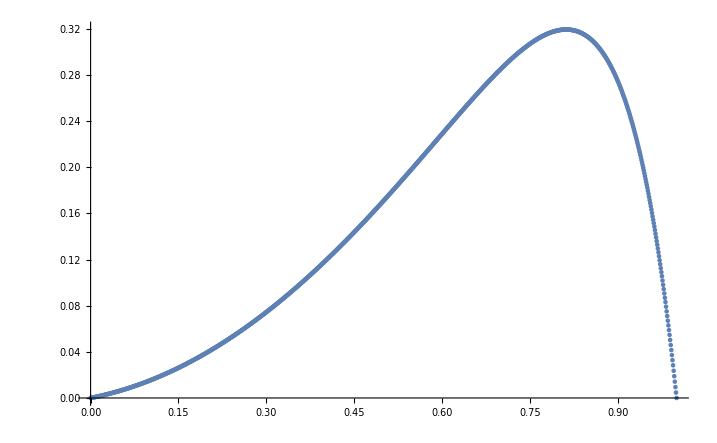
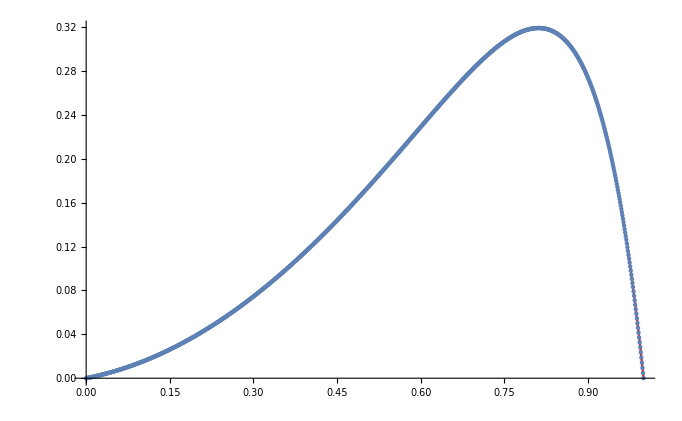
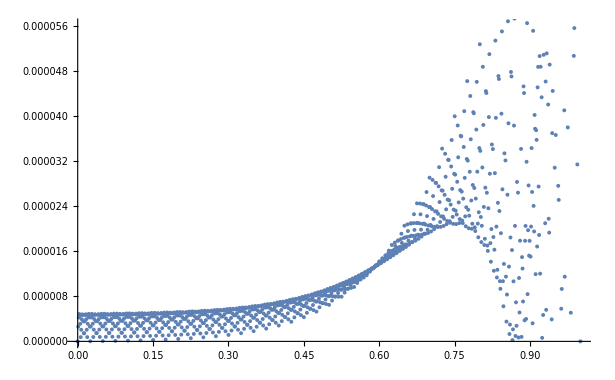

```mathematica
list={{0,0},{0.001,0.000102845},{0.002,0.000205689},{0.003,0.000308534},{0.004,0.000411379},{0.005,0.000514224},{0.006,0.000617068},{0.007,0.000724587},{0.008,0.000833664},{0.009,0.00094274},{0.01,0.00105182},{0.011,0.00116089},{0.012,0.00126997},{0.013,0.00138216},{0.014,0.00149747},{0.015,0.00161278},{0.016,0.00172808},{0.017,0.00184339},{0.018,0.0019587},{0.019,0.00207556},{0.02,0.0021971},{0.021,0.00231864},{0.022,0.00244017},{0.023,0.00256171},{0.024,0.00268325},{0.025,0.00280479},{0.026,0.00293255},{0.027,0.00306032},{0.028,0.00318808},{0.029,0.00331585},{0.03,0.00344361},{0.031,0.00357138},{0.032,0.00370381},{0.033,0.0038378},{0.034,0.00397179},{0.035,0.00410579},{0.036,0.00423978},{0.037,0.00437377},{0.038,0.00451087},{0.039,0.00465109},{0.04,0.00479131},{0.041,0.00493153},{0.042,0.00507174},{0.043,0.00521196},{0.044,0.00535373},{0.045,0.00550017},{0.046,0.00564661},{0.047,0.00579306},{0.048,0.0059395},{0.049,0.00608594},{0.05,0.00623238},{0.051,0.00638504},{0.052,0.0065377},{0.053,0.00669037},{0.054,0.00684303},{0.055,0.00699569},{0.056,0.00714836},{0.057,0.00730568},{0.058,0.00746457},{0.059,0.00762345},{0.06,0.00778233},{0.061,0.00794122},{0.062,0.0081001},{0.063,0.00826209},{0.064,0.00842719},{0.065,0.00859229},{0.066,0.00875739},{0.067,0.0089225},{0.068,0.0090876},{0.069,0.00925425},{0.07,0.00942557},{0.071,0.00959689},{0.072,0.0097682},{0.073,0.00993952},{0.074,0.0101108},{0.075,0.0102822},{0.076,0.0104597},{0.077,0.0106372},{0.078,0.0108148},{0.079,0.0109923},{0.08,0.0111698},{0.081,0.0113473},{0.082,0.0115295},{0.083,0.0117133},{0.084,0.011897},{0.085,0.0120808},{0.086,0.0122645},{0.087,0.0124483},{0.088,0.0126351},{0.089,0.0128251},{0.09,0.013015},{0.091,0.013205},{0.092,0.0133949},{0.093,0.0135849},{0.094,0.0137764},{0.095,0.0139725},{0.096,0.0141687},{0.097,0.0143648},{0.098,0.014561},{0.099,0.0147572},{0.1,0.0149533},{0.101,0.0151557},{0.102,0.015358},{0.103,0.0155604},{0.104,0.0157628},{0.105,0.0159651},{0.106,0.0161675},{0.107,0.0163745},{0.108,0.0165831},{0.109,0.0167916},{0.11,0.0170002},{0.111,0.0172088},{0.112,0.0174173},{0.113,0.017629},{0.114,0.0178438},{0.115,0.0180585},{0.116,0.0182733},{0.117,0.018488},{0.118,0.0187028},{0.119,0.0189191},{0.12,0.0191401},{0.121,0.019361},{0.122,0.019582},{0.123,0.0198029},{0.124,0.0200239},{0.125,0.0202448},{0.126,0.020472},{0.127,0.0206991},{0.128,0.0209263},{0.129,0.0211534},{0.13,0.0213806},{0.131,0.0216077},{0.132,0.0218395},{0.133,0.0220728},{0.134,0.0223062},{0.135,0.0225395},{0.136,0.0227728},{0.137,0.0230062},{0.138,0.0232426},{0.139,0.0234821},{0.14,0.0237216},{0.141,0.0239611},{0.142,0.0242007},{0.143,0.0244402},{0.144,0.0246812},{0.145,0.0249269},{0.146,0.0251726},{0.147,0.0254183},{0.148,0.025664},{0.149,0.0259097},{0.15,0.0261554},{0.151,0.0264073},{0.152,0.0266591},{0.153,0.026911},{0.154,0.0271629},{0.155,0.0274147},{0.156,0.0276666},{0.157,0.0279231},{0.158,0.0281811},{0.159,0.0284392},{0.16,0.0286972},{0.161,0.0289553},{0.162,0.0292133},{0.163,0.0294744},{0.164,0.0297386},{0.165,0.0300028},{0.166,0.030267},{0.167,0.0305312},{0.168,0.0307954},{0.169,0.0310612},{0.17,0.0313315},{0.171,0.0316019},{0.172,0.0318722},{0.173,0.0321426},{0.174,0.032413},{0.175,0.0326833},{0.176,0.0329598},{0.177,0.0332363},{0.178,0.0335128},{0.179,0.0337894},{0.18,0.0340659},{0.181,0.0343424},{0.182,0.0346235},{0.183,0.0349062},{0.184,0.0351888},{0.185,0.0354715},{0.186,0.0357541},{0.187,0.0360368},{0.188,0.0363225},{0.189,0.0366113},{0.19,0.0369001},{0.191,0.0371889},{0.192,0.0374777},{0.193,0.0377665},{0.194,0.0380568},{0.195,0.0383517},{0.196,0.0386467},{0.197,0.0389416},{0.198,0.0392365},{0.199,0.0395315},{0.2,0.0398264},{0.201,0.0401274},{0.202,0.0404285},{0.203,0.0407295},{0.204,0.0410306},{0.205,0.0413317},{0.206,0.0416327},{0.207,0.0419383},{0.208,0.0422455},{0.209,0.0425527},{0.21,0.0428599},{0.211,0.043167},{0.212,0.0434742},{0.213,0.0437844},{0.214,0.0440977},{0.215,0.044411},{0.216,0.0447242},{0.217,0.0450375},{0.218,0.0453508},{0.219,0.0456656},{0.22,0.045985},{0.221,0.0463043},{0.222,0.0466237},{0.223,0.0469431},{0.224,0.0472625},{0.225,0.0475818},{0.226,0.0479073},{0.227,0.0482328},{0.228,0.0485582},{0.229,0.0488837},{0.23,0.0492092},{0.231,0.0495346},{0.232,0.0498647},{0.233,0.0501962},{0.234,0.0505277},{0.235,0.0508593},{0.236,0.0511908},{0.237,0.0515224},{0.238,0.0518569},{0.239,0.0521945},{0.24,0.0525322},{0.241,0.0528698},{0.242,0.0532074},{0.243,0.053545},{0.244,0.0538841},{0.245,0.0542278},{0.246,0.0545714},{0.247,0.0549151},{0.248,0.0552588},{0.249,0.0556024},{0.25,0.0559461},{0.251,0.0562958},{0.252,0.0566455},{0.253,0.0569952},{0.254,0.0573449},{0.255,0.0576946},{0.256,0.0580443},{0.257,0.0583986},{0.258,0.0587543},{0.259,0.05911},{0.26,0.0594658},{0.261,0.0598215},{0.262,0.0601773},{0.263,0.060536},{0.264,0.0608978},{0.265,0.0612595},{0.266,0.0616213},{0.267,0.061983},{0.268,0.0623448},{0.269,0.062708},{0.27,0.0630758},{0.271,0.0634435},{0.272,0.0638113},{0.273,0.064179},{0.274,0.0645468},{0.275,0.0649145},{0.276,0.0652883},{0.277,0.065662},{0.278,0.0660357},{0.279,0.0664095},{0.28,0.0667832},{0.281,0.067157},{0.282,0.0675352},{0.283,0.0679149},{0.284,0.0682946},{0.285,0.0686743},{0.286,0.069054},{0.287,0.0694337},{0.288,0.0698164},{0.289,0.070202},{0.29,0.0705877},{0.291,0.0709733},{0.292,0.071359},{0.293,0.0717446},{0.294,0.0721318},{0.295,0.0725233},{0.296,0.0729149},{0.297,0.0733065},{0.298,0.0736981},{0.299,0.0740897},{0.3,0.0744812},{0.301,0.0748787},{0.302,0.0752762},{0.303,0.0756737},{0.304,0.0760712},{0.305,0.0764687},{0.306,0.0768662},{0.307,0.0772681},{0.308,0.0776715},{0.309,0.0780748},{0.31,0.0784782},{0.311,0.0788816},{0.312,0.079285},{0.313,0.0796913},{0.314,0.0801005},{0.315,0.0805098},{0.316,0.080919},{0.317,0.0813282},{0.318,0.0817375},{0.319,0.0821482},{0.32,0.0825632},{0.321,0.0829783},{0.322,0.0833934},{0.323,0.0838085},{0.324,0.0842236},{0.325,0.0846386},{0.326,0.0850595},{0.327,0.0854804},{0.328,0.0859013},{0.329,0.0863222},{0.33,0.0867431},{0.331,0.087164},{0.332,0.0875892},{0.333,0.0880159},{0.334,0.0884425},{0.335,0.0888692},{0.336,0.0892959},{0.337,0.0897226},{0.338,0.0901521},{0.339,0.0905845},{0.34,0.091017},{0.341,0.0914494},{0.342,0.0918818},{0.343,0.0923142},{0.344,0.0927481},{0.345,0.0931862},{0.346,0.0936244},{0.347,0.0940625},{0.348,0.0945007},{0.349,0.0949388},{0.35,0.095377},{0.351,0.0958208},{0.352,0.0962646},{0.353,0.0967085},{0.354,0.0971523},{0.355,0.0975961},{0.356,0.09804},{0.357,0.098488},{0.358,0.0989375},{0.359,0.099387},{0.36,0.0998365},{0.361,0.100286},{0.362,0.100735},{0.363,0.101188},{0.364,0.101643},{0.365,0.102098},{0.366,0.102553},{0.367,0.103008},{0.368,0.103463},{0.369,0.10392},{0.37,0.10438},{0.371,0.104841},{0.372,0.105302},{0.373,0.105762},{0.374,0.106223},{0.375,0.106684},{0.376,0.10715},{0.377,0.107616},{0.378,0.108082},{0.379,0.108548},{0.38,0.109015},{0.381,0.109481},{0.382,0.109951},{0.383,0.110423},{0.384,0.110894},{0.385,0.111366},{0.386,0.111838},{0.387,0.11231},{0.388,0.112784},{0.389,0.113261},{0.39,0.113738},{0.391,0.114215},{0.392,0.114692},{0.393,0.115169},{0.394,0.115648},{0.395,0.11613},{0.396,0.116613},{0.397,0.117095},{0.398,0.117578},{0.399,0.11806},{0.4,0.118543},{0.401,0.119031},{0.402,0.119518},{0.403,0.120006},{0.404,0.120494},{0.405,0.120982},{0.406,0.12147},{0.407,0.121961},{0.408,0.122454},{0.409,0.122947},{0.41,0.12344},{0.411,0.123934},{0.412,0.124427},{0.413,0.124922},{0.414,0.125421},{0.415,0.125919},{0.416,0.126417},{0.417,0.126915},{0.418,0.127414},{0.419,0.127913},{0.42,0.128417},{0.421,0.12892},{0.422,0.129423},{0.423,0.129927},{0.424,0.13043},{0.425,0.130933},{0.426,0.131442},{0.427,0.13195},{0.428,0.132459},{0.429,0.132967},{0.43,0.133476},{0.431,0.133984},{0.432,0.134496},{0.433,0.13501},{0.434,0.135523},{0.435,0.136037},{0.436,0.13655},{0.437,0.137063},{0.438,0.137579},{0.439,0.138098},{0.44,0.138616},{0.441,0.139134},{0.442,0.139653},{0.443,0.140171},{0.444,0.140691},{0.445,0.141214},{0.446,0.141737},{0.447,0.14226},{0.448,0.142783},{0.449,0.143306},{0.45,0.143829},{0.451,0.144357},{0.452,0.144885},{0.453,0.145413},{0.454,0.145941},{0.455,0.146469},{0.456,0.146997},{0.457,0.147528},{0.458,0.14806},{0.459,0.148593},{0.46,0.149125},{0.461,0.149658},{0.462,0.15019},{0.463,0.150725},{0.464,0.151262},{0.465,0.151799},{0.466,0.152336},{0.467,0.152873},{0.468,0.15341},{0.469,0.153948},{0.47,0.154489},{0.471,0.155031},{0.472,0.155572},{0.473,0.156114},{0.474,0.156655},{0.475,0.157196},{0.476,0.157742},{0.477,0.158288},{0.478,0.158833},{0.479,0.159379},{0.48,0.159925},{0.481,0.16047},{0.482,0.161019},{0.483,0.161569},{0.484,0.162119},{0.485,0.162669},{0.486,0.163219},{0.487,0.163768},{0.488,0.16432},{0.489,0.164874},{0.49,0.165428},{0.491,0.165982},{0.492,0.166536},{0.493,0.16709},{0.494,0.167644},{0.495,0.168202},{0.496,0.16876},{0.497,0.169318},{0.498,0.169875},{0.499,0.170433},{0.5,0.170991},{0.501,0.171552},{0.502,0.172114},{0.503,0.172675},{0.504,0.173237},{0.505,0.173798},{0.506,0.17436},{0.507,0.174924},{0.508,0.175489},{0.509,0.176054},{0.51,0.176619},{0.511,0.177184},{0.512,0.177749},{0.513,0.178315},{0.514,0.178884},{0.515,0.179452},{0.516,0.180021},{0.517,0.180589},{0.518,0.181158},{0.519,0.181727},{0.52,0.182298},{0.521,0.18287},{0.522,0.183442},{0.523,0.184013},{0.524,0.184585},{0.525,0.185156},{0.526,0.185731},{0.527,0.186306},{0.528,0.18688},{0.529,0.187455},{0.53,0.18803},{0.531,0.188604},{0.532,0.189181},{0.533,0.189758},{0.534,0.190336},{0.535,0.190913},{0.536,0.191491},{0.537,0.192068},{0.538,0.192647},{0.539,0.193227},{0.54,0.193807},{0.541,0.194387},{0.542,0.194967},{0.543,0.195547},{0.544,0.196127},{0.545,0.19671},{0.546,0.197292},{0.547,0.197874},{0.548,0.198457},{0.549,0.199039},{0.55,0.199621},{0.551,0.200206},{0.552,0.20079},{0.553,0.201374},{0.554,0.201959},{0.555,0.202543},{0.556,0.203128},{0.557,0.203714},{0.558,0.2043},{0.559,0.204886},{0.56,0.205472},{0.561,0.206058},{0.562,0.206645},{0.563,0.207232},{0.564,0.207819},{0.565,0.208407},{0.566,0.208995},{0.567,0.209583},{0.568,0.210171},{0.569,0.210759},{0.57,0.211348},{0.571,0.211937},{0.572,0.212526},{0.573,0.213115},{0.574,0.213704},{0.575,0.214293},{0.576,0.214882},{0.577,0.215472},{0.578,0.216062},{0.579,0.216652},{0.58,0.217242},{0.581,0.217832},{0.582,0.218422},{0.583,0.219013},{0.584,0.219603},{0.585,0.220194},{0.586,0.220784},{0.587,0.221375},{0.588,0.221965},{0.589,0.222556},{0.59,0.223146},{0.591,0.223737},{0.592,0.224328},{0.593,0.224918},{0.594,0.225509},{0.595,0.226099},{0.596,0.22669},{0.597,0.22728},{0.598,0.227871},{0.599,0.228461},{0.6,0.229052},{0.601,0.229641},{0.602,0.230231},{0.603,0.230821},{0.604,0.231411},{0.605,0.232001},{0.606,0.232591},{0.607,0.23318},{0.608,0.233768},{0.609,0.234357},{0.61,0.234946},{0.611,0.235535},{0.612,0.236123},{0.613,0.236711},{0.614,0.237299},{0.615,0.237886},{0.616,0.238473},{0.617,0.23906},{0.618,0.239648},{0.619,0.240234},{0.62,0.24082},{0.621,0.241405},{0.622,0.24199},{0.623,0.242575},{0.624,0.24316},{0.625,0.243746},{0.626,0.244328},{0.627,0.244911},{0.628,0.245494},{0.629,0.246076},{0.63,0.246659},{0.631,0.247241},{0.632,0.247822},{0.633,0.248401},{0.634,0.248981},{0.635,0.24956},{0.636,0.25014},{0.637,0.250719},{0.638,0.251297},{0.639,0.251873},{0.64,0.252448},{0.641,0.253024},{0.642,0.2536},{0.643,0.254176},{0.644,0.25475},{0.645,0.255322},{0.646,0.255893},{0.647,0.256464},{0.648,0.257036},{0.649,0.257607},{0.65,0.258179},{0.651,0.258745},{0.652,0.259311},{0.653,0.259877},{0.654,0.260444},{0.655,0.26101},{0.656,0.261576},{0.657,0.262138},{0.658,0.262699},{0.659,0.263259},{0.66,0.26382},{0.661,0.26438},{0.662,0.264941},{0.663,0.265498},{0.664,0.266052},{0.665,0.266606},{0.666,0.26716},{0.667,0.267714},{0.668,0.268268},{0.669,0.26882},{0.67,0.269366},{0.671,0.269913},{0.672,0.270459},{0.673,0.271006},{0.674,0.271552},{0.675,0.272099},{0.676,0.272637},{0.677,0.273175},{0.678,0.273713},{0.679,0.274252},{0.68,0.27479},{0.681,0.275328},{0.682,0.275859},{0.683,0.276388},{0.684,0.276917},{0.685,0.277446},{0.686,0.277975},{0.687,0.278504},{0.688,0.279028},{0.689,0.279547},{0.69,0.280066},{0.691,0.280584},{0.692,0.281103},{0.693,0.281622},{0.694,0.282138},{0.695,0.282645},{0.696,0.283153},{0.697,0.28366},{0.698,0.284168},{0.699,0.284675},{0.7,0.285183},{0.701,0.285678},{0.702,0.286173},{0.703,0.286668},{0.704,0.287163},{0.705,0.287658},{0.706,0.288153},{0.707,0.288638},{0.708,0.289119},{0.709,0.289601},{0.71,0.290082},{0.711,0.290564},{0.712,0.291045},{0.713,0.291519},{0.714,0.291986},{0.715,0.292452},{0.716,0.292919},{0.717,0.293385},{0.718,0.293852},{0.719,0.294314},{0.72,0.294764},{0.721,0.295215},{0.722,0.295665},{0.723,0.296115},{0.724,0.296565},{0.725,0.297016},{0.726,0.297448},{0.727,0.297881},{0.728,0.298313},{0.729,0.298746},{0.73,0.299178},{0.731,0.299611},{0.732,0.300029},{0.733,0.300442},{0.734,0.300855},{0.735,0.301268},{0.736,0.301682},{0.737,0.302095},{0.738,0.302498},{0.739,0.30289},{0.74,0.303282},{0.741,0.303675},{0.742,0.304067},{0.743,0.304459},{0.744,0.304846},{0.745,0.305216},{0.746,0.305585},{0.747,0.305955},{0.748,0.306325},{0.749,0.306694},{0.75,0.307064},{0.751,0.307409},{0.752,0.307754},{0.753,0.308099},{0.754,0.308444},{0.755,0.30879},{0.756,0.309135},{0.757,0.30946},{0.758,0.309779},{0.759,0.310097},{0.76,0.310416},{0.761,0.310734},{0.762,0.311053},{0.763,0.311357},{0.764,0.311647},{0.765,0.311937},{0.766,0.312227},{0.767,0.312517},{0.768,0.312807},{0.769,0.313089},{0.77,0.313348},{0.771,0.313607},{0.772,0.313866},{0.773,0.314125},{0.774,0.314385},{0.775,0.314644},{0.776,0.314869},{0.777,0.315095},{0.778,0.315321},{0.779,0.315547},{0.78,0.315772},{0.781,0.315998},{0.782,0.316197},{0.783,0.316387},{0.784,0.316577},{0.785,0.316767},{0.786,0.316957},{0.787,0.317147},{0.788,0.317318},{0.789,0.317469},{0.79,0.31762},{0.791,0.317772},{0.792,0.317923},{0.793,0.318074},{0.794,0.318216},{0.795,0.318325},{0.796,0.318435},{0.797,0.318545},{0.798,0.318655},{0.799,0.318765},{0.8,0.318875},{0.801,0.318941},{0.802,0.319006},{0.803,0.319071},{0.804,0.319137},{0.805,0.319202},{0.806,0.319268},{0.807,0.319297},{0.808,0.319315},{0.809,0.319333},{0.81,0.31935},{0.811,0.319368},{0.812,0.319385},{0.813,0.319377},{0.814,0.319344},{0.815,0.31931},{0.816,0.319277},{0.817,0.319243},{0.818,0.319209},{0.819,0.319162},{0.82,0.319073},{0.821,0.318985},{0.822,0.318896},{0.823,0.318807},{0.824,0.318719},{0.825,0.31863},{0.826,0.318482},{0.827,0.318335},{0.828,0.318187},{0.829,0.31804},{0.83,0.317892},{0.831,0.317744},{0.832,0.31755},{0.833,0.317339},{0.834,0.317128},{0.835,0.316917},{0.836,0.316707},{0.837,0.316496},{0.838,0.316251},{0.839,0.315973},{0.84,0.315695},{0.841,0.315416},{0.842,0.315138},{0.843,0.314859},{0.844,0.314563},{0.845,0.314212},{0.846,0.313861},{0.847,0.313511},{0.848,0.31316},{0.849,0.312809},{0.85,0.312458},{0.851,0.31203},{0.852,0.311602},{0.853,0.311174},{0.854,0.310745},{0.855,0.310317},{0.856,0.309889},{0.857,0.309399},{0.858,0.308888},{0.859,0.308376},{0.86,0.307865},{0.861,0.307354},{0.862,0.306843},{0.863,0.306288},{0.864,0.305688},{0.865,0.305088},{0.866,0.304489},{0.867,0.303889},{0.868,0.303289},{0.869,0.302666},{0.87,0.301971},{0.871,0.301277},{0.872,0.300582},{0.873,0.299888},{0.874,0.299193},{0.875,0.298499},{0.876,0.297703},{0.877,0.296908},{0.878,0.296112},{0.879,0.295316},{0.88,0.29452},{0.881,0.293725},{0.882,0.292848},{0.883,0.291944},{0.884,0.29104},{0.885,0.290136},{0.886,0.289232},{0.887,0.288328},{0.888,0.287367},{0.889,0.286347},{0.89,0.285328},{0.891,0.284308},{0.892,0.283289},{0.893,0.282269},{0.894,0.281219},{0.895,0.280076},{0.896,0.278933},{0.897,0.27779},{0.898,0.276647},{0.899,0.275504},{0.9,0.274361},{0.901,0.273087},{0.902,0.271812},{0.903,0.270537},{0.904,0.269263},{0.905,0.267988},{0.906,0.266713},{0.907,0.265333},{0.908,0.263917},{0.909,0.262502},{0.91,0.261087},{0.911,0.259671},{0.912,0.258256},{0.913,0.256765},{0.914,0.2552},{0.915,0.253634},{0.916,0.252068},{0.917,0.250503},{0.918,0.248937},{0.919,0.247331},{0.92,0.245606},{0.921,0.24388},{0.922,0.242154},{0.923,0.240428},{0.924,0.238702},{0.925,0.236976},{0.926,0.235079},{0.927,0.233182},{0.928,0.231285},{0.929,0.229388},{0.93,0.227492},{0.931,0.225595},{0.932,0.223561},{0.933,0.221481},{0.934,0.219402},{0.935,0.217323},{0.936,0.215243},{0.937,0.213164},{0.938,0.210987},{0.939,0.208713},{0.94,0.206439},{0.941,0.204165},{0.942,0.201891},{0.943,0.199617},{0.944,0.197291},{0.945,0.19481},{0.946,0.192328},{0.947,0.189846},{0.948,0.187365},{0.949,0.184883},{0.95,0.182402},{0.951,0.179699},{0.952,0.176996},{0.953,0.174293},{0.954,0.17159},{0.955,0.168887},{0.956,0.166183},{0.957,0.163303},{0.958,0.160364},{0.959,0.157425},{0.96,0.154486},{0.961,0.151547},{0.962,0.148608},{0.963,0.145543},{0.964,0.142352},{0.965,0.139161},{0.966,0.135971},{0.967,0.13278},{0.968,0.129589},{0.969,0.126331},{0.97,0.122872},{0.971,0.119413},{0.972,0.115954},{0.973,0.112494},{0.974,0.109035},{0.975,0.105576},{0.976,0.101831},{0.977,0.0980856},{0.978,0.0943404},{0.979,0.0905951},{0.98,0.0868499},{0.981,0.0831046},{0.982,0.0791307},{0.983,0.0750805},{0.984,0.0710303},{0.985,0.0669802},{0.986,0.06293},{0.987,0.0588798},{0.988,0.0546671},{0.989,0.050292},{0.99,0.0459168},{0.991,0.0415416},{0.992,0.0371664},{0.993,0.0327912},{0.994,0.0283294},{0.995,0.0236079},{0.996,0.0188863},{0.997,0.0141647},{0.998,0.00944314},{0.999,0.00472157},{1,0}};
error={{0,0*10^(0)},{0.001,2.61849*10^(-6)},{0.002,4.23974*10^(-6)},{0.003,4.86376*10^(-6)},{0.004,4.49059*10^(-6)},{0.005,3.12026*10^(-6)},{0.006,7.52792*10^(-7)},{0.007,2.06215*10^(-6)},{0.008,3.93241*10^(-6)},{0.009,4.80563*10^(-6)},{0.01,4.68182*10^(-6)},{0.011,3.56103*10^(-6)},{0.012,1.44327*10^(-6)},{0.013,1.44396*10^(-6)},{0.014,3.56313*10^(-6)},{0.015,4.68543*10^(-6)},{0.016,4.8109*10^(-6)},{0.017,3.93957*10^(-6)},{0.018,2.07146*10^(-6)},{0.019,7.63993*10^(-7)},{0.02,3.13195*10^(-6)},{0.021,4.50324*10^(-6)},{0.022,4.87788*10^(-6)},{0.023,4.25592*10^(-6)},{0.024,2.63739*10^(-6)},{0.025,2.2322*10^(-8)},{0.026,2.63894*10^(-6)},{0.027,4.25909*10^(-6)},{0.028,4.88281*10^(-6)},{0.029,4.51013*10^(-6)},{0.03,3.14109*10^(-6)},{0.031,7.75731*10^(-7)},{0.032,2.08417*10^(-6)},{0.033,3.95305*10^(-6)},{0.034,4.82573*10^(-6)},{0.035,4.70223*10^(-6)},{0.036,3.5826*10^(-6)},{0.037,1.46687*10^(-6)},{0.038,1.46772*10^(-6)},{0.039,3.5852*10^(-6)},{0.04,4.70671*10^(-6)},{0.041,4.83228*10^(-6)},{0.042,3.96195*10^(-6)},{0.043,2.09577*10^(-6)},{0.044,7.89694*10^(-7)},{0.045,3.15562*10^(-6)},{0.046,4.52581*10^(-6)},{0.047,4.90032*10^(-6)},{0.048,4.27919*10^(-6)},{0.049,2.66246*10^(-6)},{0.05,5.01774*10^(-8)},{0.051,2.66437*10^(-6)},{0.052,4.28311*10^(-6)},{0.053,4.90642*10^(-6)},{0.054,4.53437*10^(-6)},{0.055,3.16699*10^(-6)},{0.056,8.04328*10^(-7)},{0.057,2.11157*10^(-6)},{0.058,3.97868*10^(-6)},{0.059,4.85066*10^(-6)},{0.06,4.72754*10^(-6)},{0.061,3.60939*10^(-6)},{0.062,1.49626*10^(-6)},{0.063,1.49732*10^(-6)},{0.064,3.61262*10^(-6)},{0.065,4.73309*10^(-6)},{0.066,4.85877*10^(-6)},{0.067,3.98973*10^(-6)},{0.068,2.12601*10^(-6)},{0.069,8.2172*10^(-7)},{0.07,3.18502*10^(-6)},{0.071,4.5538*10^(-6)},{0.072,4.92813*10^(-6)},{0.073,4.30805*10^(-6)},{0.074,2.69362*10^(-6)},{0.075,8.49085*10^(-8)},{0.076,2.69599*10^(-6)},{0.077,4.3129*10^(-6)},{0.078,4.93568*10^(-6)},{0.079,4.56442*10^(-6)},{0.08,3.19915*10^(-6)},{0.081,8.39948*10^(-7)},{0.082,2.14565*10^(-6)},{0.083,4.01047*10^(-6)},{0.084,4.88153*10^(-6)},{0.085,4.7589*10^(-6)},{0.086,3.64265*10^(-6)},{0.087,1.53283*10^(-6)},{0.088,1.53414*10^(-6)},{0.089,3.64663*10^(-6)},{0.09,4.76575*10^(-6)},{0.091,4.89158*10^(-6)},{0.092,4.02417*10^(-6)},{0.093,2.1636*10^(-6)},{0.094,8.6159*10^(-7)},{0.095,3.22151*10^(-6)},{0.096,4.58847*10^(-6)},{0.097,4.96254*10^(-6)},{0.098,4.3438*10^(-6)},{0.099,2.73232*10^(-6)},{0.1,1.28174*10^(-7)},{0.101,2.73524*10^(-6)},{0.102,4.34978*10^(-6)},{0.103,4.97188*10^(-6)},{0.104,4.60161*10^(-6)},{0.105,3.23905*10^(-6)},{0.106,8.84273*10^(-7)},{0.107,2.18798*10^(-6)},{0.108,4.04984*10^(-6)},{0.109,4.91971*10^(-6)},{0.11,4.79769*10^(-6)},{0.111,3.68386*10^(-6)},{0.112,1.57829*10^(-6)},{0.113,1.5799*10^(-6)},{0.114,3.68877*10^(-6)},{0.115,4.80615*10^(-6)},{0.116,4.93214*10^(-6)},{0.117,4.06682*10^(-6)},{0.118,2.21028*10^(-6)},{0.119,9.11174*10^(-7)},{0.12,3.26673*10^(-6)},{0.121,4.63133*10^(-6)},{0.122,5.00507*10^(-6)},{0.123,4.38804*10^(-6)},{0.124,2.78032*10^(-6)},{0.125,1.8202*10^(-7)},{0.126,2.78391*10^(-6)},{0.127,4.39541*10^(-6)},{0.128,5.0166*10^(-6)},{0.129,4.6476*10^(-6)},{0.13,3.28849*10^(-6)},{0.131,9.39373*10^(-7)},{0.132,2.2405*10^(-6)},{0.133,4.09854*10^(-6)},{0.134,4.96688*10^(-6)},{0.135,4.84562*10^(-6)},{0.136,3.73487*10^(-6)},{0.137,1.63473*10^(-6)},{0.138,1.63671*10^(-6)},{0.139,3.74091*10^(-6)},{0.14,4.85604*10^(-6)},{0.141,4.98222*10^(-6)},{0.142,4.11956*10^(-6)},{0.143,2.26817*10^(-6)},{0.144,9.72777*10^(-7)},{0.145,3.32272*10^(-6)},{0.146,4.68427*10^(-6)},{0.147,5.05755*10^(-6)},{0.148,4.44268*10^(-6)},{0.149,2.83978*10^(-6)},{0.15,2.48966*10^(-7)},{0.151,2.84419*10^(-6)},{0.152,4.45175*10^(-6)},{0.153,5.07176*10^(-6)},{0.154,4.70436*10^(-6)},{0.155,3.34966*10^(-6)},{0.156,1.00779*10^(-6)},{0.157,2.30558*10^(-6)},{0.158,4.15869*10^(-6)},{0.159,5.02503*10^(-6)},{0.16,4.90473*10^(-6)},{0.161,3.79791*10^(-6)},{0.162,1.70473*10^(-6)},{0.163,1.70716*10^(-6)},{0.164,3.80533*10^(-6)},{0.165,4.91755*10^(-6)},{0.166,5.04395*10^(-6)},{0.167,4.18468*10^(-6)},{0.168,2.33988*10^(-6)},{0.169,1.04922*10^(-6)},{0.17,3.39192*10^(-6)},{0.171,4.74953*10^(-6)},{0.172,5.1222*10^(-6)},{0.173,4.51009*10^(-6)},{0.174,2.91334*10^(-6)},{0.175,3.32109*10^(-7)},{0.176,2.91875*10^(-6)},{0.177,4.52122*10^(-6)},{0.178,5.13969*10^(-6)},{0.179,4.77431*10^(-6)},{0.18,3.42524*10^(-6)},{0.181,1.09266*10^(-6)},{0.182,2.38613*10^(-6)},{0.183,4.23288*10^(-6)},{0.184,5.09662*10^(-6)},{0.185,4.97751*10^(-6)},{0.186,3.87572*10^(-6)},{0.187,1.79144*10^(-6)},{0.188,1.79441*10^(-6)},{0.189,3.88481*10^(-6)},{0.19,4.99325*10^(-6)},{0.191,5.1199*10^(-6)},{0.192,4.26495*10^(-6)},{0.193,2.42858*10^(-6)},{0.194,1.14397*10^(-6)},{0.195,3.47734*10^(-6)},{0.196,4.82985*10^(-6)},{0.197,5.2017*10^(-6)},{0.198,4.59309*10^(-6)},{0.199,3.00421*10^(-6)},{0.2,4.35251*10^(-7)},{0.201,3.01083*10^(-6)},{0.202,4.60673*10^(-6)},{0.203,5.22317*10^(-6)},{0.204,4.86035*10^(-6)},{0.205,3.51849*10^(-6)},{0.206,1.19778*10^(-6)},{0.207,2.48567*10^(-6)},{0.208,4.32422*10^(-6)},{0.209,5.18458*10^(-6)},{0.21,5.06696*10^(-6)},{0.211,3.97159*10^(-6)},{0.212,1.89869*10^(-6)},{0.213,1.90232*10^(-6)},{0.214,3.98271*10^(-6)},{0.215,5.08625*10^(-6)},{0.216,5.21318*10^(-6)},{0.217,4.36373*10^(-6)},{0.218,2.53813*10^(-6)},{0.219,1.26126*10^(-6)},{0.22,3.5826*10^(-6)},{0.221,4.92852*10^(-6)},{0.222,5.29928*10^(-6)},{0.223,4.69511*10^(-6)},{0.224,3.11628*10^(-6)},{0.225,5.63043*10^(-7)},{0.226,3.12436*10^(-6)},{0.227,4.71179*10^(-6)},{0.228,5.32558*10^(-6)},{0.229,4.96601*10^(-6)},{0.23,3.63333*10^(-6)},{0.231,1.32783*10^(-6)},{0.232,2.6085*10^(-6)},{0.233,4.43647*10^(-6)},{0.234,5.29244*10^(-6)},{0.235,5.17669*10^(-6)},{0.236,4.08951*10^(-6)},{0.237,2.03117*10^(-6)},{0.238,2.03559*10^(-6)},{0.239,4.10306*10^(-6)},{0.24,5.20026*10^(-6)},{0.241,5.32749*10^(-6)},{0.242,4.48505*10^(-6)},{0.243,2.67325*10^(-6)},{0.244,1.40625*10^(-6)},{0.245,3.71208*10^(-6)},{0.246,5.04948*10^(-6)},{0.247,5.41877*10^(-6)},{0.248,4.82026*10^(-6)},{0.249,3.25429*10^(-6)},{0.25,7.21166*10^(-7)},{0.251,3.26412*10^(-6)},{0.252,4.84059*10^(-6)},{0.253,5.45093*10^(-6)},{0.254,5.09546*10^(-6)},{0.255,3.77453*10^(-6)},{0.256,1.48848*10^(-6)},{0.257,2.75983*10^(-6)},{0.258,4.57414*10^(-6)},{0.259,5.42441*10^(-6)},{0.26,5.31099*10^(-6)},{0.261,4.23425*10^(-6)},{0.262,2.19455*10^(-6)},{0.263,2.19992*10^(-6)},{0.264,4.25074*10^(-6)},{0.265,5.33973*10^(-6)},{0.266,5.46728*10^(-6)},{0.267,4.63377*10^(-6)},{0.268,2.8396*10^(-6)},{0.269,1.5852*10^(-6)},{0.27,3.87105*10^(-6)},{0.271,5.19744*10^(-6)},{0.272,5.56477*10^(-6)},{0.273,4.97345*10^(-6)},{0.274,3.4239*10^(-6)},{0.275,9.16542*10^(-7)},{0.276,3.43584*10^(-6)},{0.277,4.99817*10^(-6)},{0.278,5.60398*10^(-6)},{0.279,5.2537*10^(-6)},{0.28,3.94777*10^(-6)},{0.281,1.68664*10^(-6)},{0.282,2.94591*10^(-6)},{0.283,4.74261*10^(-6)},{0.284,5.58548*10^(-6)},{0.285,5.47496*10^(-6)},{0.286,4.41155*10^(-6)},{0.287,2.3957*10^(-6)},{0.288,2.4022*10^(-6)},{0.289,4.43154*10^(-6)},{0.29,5.5099*10^(-6)},{0.291,5.63777*10^(-6)},{0.292,4.81564*10^(-6)},{0.293,3.04402*10^(-6)},{0.294,1.80572*10^(-6)},{0.295,4.06582*10^(-6)},{0.296,5.37797*10^(-6)},{0.297,5.74268*10^(-6)},{0.298,5.1605*10^(-6)},{0.299,3.63195*10^(-6)},{0.3,1.15757*10^(-6)},{0.301,3.64638*10^(-6)},{0.302,5.19046*10^(-6)},{0.303,5.79036*10^(-6)},{0.304,5.44664*10^(-6)},{0.305,4.15987*10^(-6)},{0.306,1.93062*10^(-6)},{0.307,3.1743*10^(-6)},{0.308,4.94827*10^(-6)},{0.309,5.78152*10^(-6)},{0.31,5.67464*10^(-6)},{0.311,4.62822*10^(-6)},{0.312,2.64288*10^(-6)},{0.313,2.65073*10^(-6)},{0.314,4.65238*10^(-6)},{0.315,5.71697*10^(-6)},{0.316,5.84514*10^(-6)},{0.317,5.03751*10^(-6)},{0.318,3.29473*10^(-6)},{0.319,2.07697*10^(-6)},{0.32,4.30388*10^(-6)},{0.321,5.59762*10^(-6)},{0.322,5.95887*10^(-6)},{0.323,5.3883*10^(-6)},{0.324,3.88659*10^(-6)},{0.325,1.45443*10^(-6)},{0.326,3.90398*10^(-6)},{0.327,5.42448*10^(-6)},{0.328,6.01666*10^(-6)},{0.329,5.68124*10^(-6)},{0.33,4.41893*10^(-6)},{0.331,2.23049*10^(-6)},{0.332,3.45401*10^(-6)},{0.333,5.19866*10^(-6)},{0.334,6.01942*10^(-6)},{0.335,5.91705*10^(-6)},{0.336,4.89233*10^(-6)},{0.337,2.94604*10^(-6)},{0.338,2.95547*10^(-6)},{0.339,4.92142*10^(-6)},{0.34,5.96818*10^(-6)},{0.341,6.09657*10^(-6)},{0.342,5.30741*10^(-6)},{0.343,3.60152*10^(-6)},{0.344,2.40999*10^(-6)},{0.345,4.59413*10^(-6)},{0.346,5.86408*10^(-6)},{0.347,6.22071*10^(-6)},{0.348,5.66488*10^(-6)},{0.349,4.19748*10^(-6)},{0.35,1.81939*10^(-6)},{0.351,4.21834*10^(-6)},{0.352,5.70841*10^(-6)},{0.353,6.29051*10^(-6)},{0.354,5.96557*10^(-6)},{0.355,4.73453*10^(-6)},{0.356,2.59831*10^(-6)},{0.357,3.79576*10^(-6)},{0.358,5.50259*10^(-6)},{0.359,6.30714*10^(-6)},{0.36,6.21039*10^(-6)},{0.361,5.21335*10^(-6)},{0.362,3.317*10^(-6)},{0.363,3.32828*10^(-6)},{0.364,5.2482*10^(-6)},{0.365,6.27188*10^(-6)},{0.366,6.40038*10^(-6)},{0.367,5.63474*10^(-6)},{0.368,3.97603*10^(-6)},{0.369,2.81798*10^(-6)},{0.37,4.947*10^(-6)},{0.371,6.18621*10^(-6)},{0.372,6.5367*10^(-6)},{0.373,5.99961*10^(-6)},{0.374,4.57606*10^(-6)},{0.375,2.26718*10^(-6)},{0.376,4.60096*10^(-6)},{0.377,6.05173*10^(-6)},{0.378,6.62068*10^(-6)},{0.379,6.30898*10^(-6)},{0.38,5.11785*10^(-6)},{0.381,3.04849*10^(-6)},{0.382,4.21224*10^(-6)},{0.383,5.87027*10^(-6)},{0.384,6.65377*10^(-6)},{0.385,6.56402*10^(-6)},{0.386,5.60228*10^(-6)},{0.387,3.76984*10^(-6)},{0.388,3.78326*10^(-6)},{0.389,5.64382*10^(-6)},{0.39,6.63763*10^(-6)},{0.391,6.76602*10^(-6)},{0.392,6.03034*10^(-6)},{0.393,4.43196*10^(-6)},{0.394,3.31666*10^(-6)},{0.395,5.37465*10^(-6)},{0.396,6.57411*10^(-6)},{0.397,6.91648*10^(-6)},{0.398,6.40318*10^(-6)},{0.399,5.03567*10^(-6)},{0.4,2.81542*10^(-6)},{0.401,5.06523*10^(-6)},{0.402,6.46527*10^(-6)},{0.403,7.01704*10^(-6)},{0.404,6.72208*10^(-6)},{0.405,5.58192*10^(-6)},{0.406,3.59813*10^(-6)},{0.407,4.71832*10^(-6)},{0.408,6.31339*10^(-6)},{0.409,7.06958*10^(-6)},{0.41,6.98851*10^(-6)},{0.411,6.07182*10^(-6)},{0.412,4.32115*10^(-6)},{0.413,4.337*10^(-6)},{0.414,6.12105*10^(-6)},{0.415,7.07618*10^(-6)},{0.416,7.20412*10^(-6)},{0.417,6.5066*10^(-6)},{0.418,4.98537*10^(-6)},{0.419,3.92464*10^(-6)},{0.42,5.89108*10^(-6)},{0.421,7.03919*10^(-6)},{0.422,7.37078*10^(-6)},{0.423,6.8877*10^(-6)},{0.424,5.59182*10^(-6)},{0.425,3.48502*10^(-6)},{0.426,5.62666*10^(-6)},{0.427,6.9612*10^(-6)},{0.428,7.49058*10^(-6)},{0.429,7.21675*10^(-6)},{0.43,6.14169*10^(-6)},{0.431,4.2674*10^(-6)},{0.432,5.3313*10^(-6)},{0.433,6.84516*10^(-6)},{0.434,7.5659*10^(-6)},{0.435,7.4956*10^(-6)},{0.436,6.63636*10^(-6)},{0.437,4.99031*10^(-6)},{0.438,5.0089*10^(-6)},{0.439,6.69429*10^(-6)},{0.44,7.59937*10^(-6)},{0.441,7.72632*10^(-6)},{0.442,7.07739*10^(-6)},{0.443,5.65483*10^(-6)},{0.444,4.66377*10^(-6)},{0.445,6.51224*10^(-6)},{0.446,7.59396*10^(-6)},{0.447,7.91129*10^(-6)},{0.448,7.46659*10^(-6)},{0.449,6.26226*10^(-6)},{0.45,4.3007*10^(-6)},{0.451,6.303*10^(-6)},{0.452,7.55299*10^(-6)},{0.453,8.05315*10^(-6)},{0.454,7.806*10^(-6)},{0.455,6.81408*10^(-6)},{0.456,5.07994*10^(-6)},{0.457,6.07107*10^(-6)},{0.458,7.48017*10^(-6)},{0.459,8.1549*10^(-6)},{0.46,8.09795*10^(-6)},{0.461,7.312*10^(-6)},{0.462,5.79979*10^(-6)},{0.463,5.8214*10^(-6)},{0.464,7.37961*10^(-6)},{0.465,8.21989*10^(-6)},{0.466,8.34507*10^(-6)},{0.467,7.75802*10^(-6)},{0.468,6.46162*10^(-6)},{0.469,5.55949*10^(-6)},{0.47,7.25593*10^(-6)},{0.471,8.25187*10^(-6)},{0.472,8.55034*10^(-6)},{0.473,8.15437*10^(-6)},{0.474,7.06703*10^(-6)},{0.475,5.29143*10^(-6)},{0.476,7.11423*10^(-6)},{0.477,8.25506*10^(-6)},{0.478,8.71712*10^(-6)},{0.479,8.50364*10^(-6)},{0.48,7.61788*10^(-6)},{0.481,6.06313*10^(-6)},{0.482,6.96021*10^(-6)},{0.483,8.23416*10^(-6)},{0.484,8.8492*10^(-6)},{0.485,8.80876*10^(-6)},{0.486,8.11631*10^(-6)},{0.487,6.77533*10^(-6)},{0.488,6.80018*10^(-6)},{0.489,8.19441*10^(-6)},{0.49,8.95082*10^(-6)},{0.491,9.07306*10^(-6)},{0.492,8.5648*10^(-6)},{0.493,7.42975*10^(-6)},{0.494,6.64113*10^(-6)},{0.495,8.14165*10^(-6)},{0.496,9.02675*10^(-6)},{0.497,9.30029*10^(-6)},{0.498,8.96619*10^(-6)},{0.499,8.02837*10^(-6)},{0.5,6.49083*10^(-6)},{0.501,8.0824*10^(-6)},{0.502,9.08232*10^(-6)},{0.503,9.49471*10^(-6)},{0.504,9.32371*10^(-6)},{0.505,8.57351*10^(-6)},{0.506,7.24833*10^(-6)},{0.507,8.02387*10^(-6)},{0.508,9.1235*10^(-6)},{0.509,9.66109*10^(-6)},{0.51,9.64106*10^(-6)},{0.511,9.06785*10^(-6)},{0.512,7.94595*10^(-6)},{0.513,7.97412*10^(-6)},{0.514,9.15695*10^(-6)},{0.515,9.80483*10^(-6)},{0.516,9.92244*10^(-6)},{0.517,9.51449*10^(-6)},{0.518,8.58577*10^(-6)},{0.519,7.94204*10^(-6)},{0.52,9.19009*10^(-6)},{0.521,9.93195*10^(-6)},{0.522,1.01726*10^(-5)},{0.523,9.91701*10^(-6)},{0.524,9.17028*10^(-6)},{0.525,7.93751*10^(-6)},{0.526,9.2312*10^(-6)},{0.527,1.00492*10^(-5)},{0.528,1.03969*10^(-5)},{0.529,1.02795*10^(-5)},{0.53,9.70236*10^(-6)},{0.531,8.67101*10^(-6)},{0.532,9.28947*10^(-6)},{0.533,1.01642*10^(-5)},{0.534,1.06014*10^(-5)},{0.535,1.06065*10^(-5)},{0.536,1.01854*10^(-5)},{0.537,9.34373*10^(-6)},{0.538,9.37512*10^(-6)},{0.539,1.02854*10^(-5)},{0.54,1.07928*10^(-5)},{0.541,1.09034*10^(-5)},{0.542,1.06232*10^(-5)},{0.543,9.9583*10^(-6)},{0.544,9.4995*10^(-6)},{0.545,1.04222*10^(-5)},{0.546,1.0979*10^(-5)},{0.547,1.11762*10^(-5)},{0.548,1.10203*10^(-5)},{0.549,1.05178*10^(-5)},{0.55,9.67517*10^(-6)},{0.551,1.05851*10^(-5)},{0.552,1.11684*10^(-5)},{0.553,1.14316*10^(-5)},{0.554,1.13818*10^(-5)},{0.555,1.10257*10^(-5)},{0.556,1.03704*10^(-5)},{0.557,1.07859*10^(-5)},{0.558,1.13706*10^(-5)},{0.559,1.16774*10^(-5)},{0.56,1.17136*10^(-5)},{0.561,1.14864*10^(-5)},{0.562,1.10033*10^(-5)},{0.563,1.10375*10^(-5)},{0.564,1.15964*10^(-5)},{0.565,1.19221*10^(-5)},{0.566,1.20222*10^(-5)},{0.567,1.19046*10^(-5)},{0.568,1.15771*10^(-5)},{0.569,1.13543*10^(-5)},{0.57,1.18578*10^(-5)},{0.571,1.21754*10^(-5)},{0.572,1.23154*10^(-5)},{0.573,1.22859*10^(-5)},{0.574,1.20955*10^(-5)},{0.575,1.17524*10^(-5)},{0.576,1.2168*10^(-5)},{0.577,1.24482*10^(-5)},{0.578,1.26016*10^(-5)},{0.579,1.26369*10^(-5)},{0.58,1.2563*10^(-5)},{0.581,1.2389*10^(-5)},{0.582,1.25421*10^(-5)},{0.583,1.27527*10^(-5)},{0.584,1.28905*10^(-5)},{0.585,1.29648*10^(-5)},{0.586,1.2985*10^(-5)},{0.587,1.29606*10^(-5)},{0.588,1.29965*10^(-5)},{0.589,1.31025*10^(-5)},{0.59,1.31931*10^(-5)},{0.591,1.3278*10^(-5)},{0.592,1.33673*10^(-5)},{0.593,1.34712*10^(-5)},{0.594,1.35496*10^(-5)},{0.595,1.35129*10^(-5)},{0.596,1.35215*10^(-5)},{0.597,1.35861*10^(-5)},{0.598,1.37172*10^(-5)},{0.599,1.39255*10^(-5)},{0.6,1.42218*10^(-5)},{0.601,1.40008*10^(-5)},{0.602,1.38897*10^(-5)},{0.603,1.38999*10^(-5)},{0.604,1.40425*10^(-5)},{0.605,1.4329*10^(-5)},{0.606,1.47709*10^(-5)},{0.607,1.45851*10^(-5)},{0.608,1.43131*10^(-5)},{0.609,1.42317*10^(-5)},{0.61,1.43527*10^(-5)},{0.611,1.46884*10^(-5)},{0.612,1.52508*10^(-5)},{0.613,1.52868*10^(-5)},{0.614,1.48089*10^(-5)},{0.615,1.45952*10^(-5)},{0.616,1.46583*10^(-5)},{0.617,1.5011*10^(-5)},{0.618,1.56665*10^(-5)},{0.619,1.61294*10^(-5)},{0.62,1.53965*10^(-5)},{0.621,1.5006*10^(-5)},{0.622,1.49712*10^(-5)},{0.623,1.53059*10^(-5)},{0.624,1.60238*10^(-5)},{0.625,1.71388*10^(-5)},{0.626,1.60975*10^(-5)},{0.627,1.54815*10^(-5)},{0.628,1.53052*10^(-5)},{0.629,1.5583*10^(-5)},{0.63,1.63296*10^(-5)},{0.631,1.75596*10^(-5)},{0.632,1.69359*10^(-5)},{0.633,1.60415*10^(-5)},{0.634,1.56758*10^(-5)},{0.635,1.58541*10^(-5)},{0.636,1.6592*10^(-5)},{0.637,1.79051*10^(-5)},{0.638,1.79384*10^(-5)},{0.639,1.67078*10^(-5)},{0.64,1.61003*10^(-5)},{0.641,1.61324*10^(-5)},{0.642,1.68205*10^(-5)},{0.643,1.81812*10^(-5)},{0.644,1.91348*10^(-5)},{0.645,1.75049*10^(-5)},{0.646,1.65986*10^(-5)},{0.647,1.64332*10^(-5)},{0.648,1.70261*10^(-5)},{0.649,1.83952*10^(-5)},{0.65,2.05581*10^(-5)},{0.651,1.84603*10^(-5)},{0.652,1.71926*10^(-5)},{0.653,1.67735*10^(-5)},{0.654,1.72215*10^(-5)},{0.655,1.85555*10^(-5)},{0.656,2.07942*10^(-5)},{0.657,1.96045*10^(-5)},{0.658,1.79074*10^(-5)},{0.659,1.71731*10^(-5)},{0.66,1.74214*10^(-5)},{0.661,1.86722*10^(-5)},{0.662,2.09456*10^(-5)},{0.663,2.09716*10^(-5)},{0.664,1.87707*10^(-5)},{0.665,1.7654*10^(-5)},{0.666,1.76424*10^(-5)},{0.667,1.87572*10^(-5)},{0.668,2.10198*10^(-5)},{0.669,2.25994*10^(-5)},{0.67,1.98137*10^(-5)},{0.671,1.82411*10^(-5)},{0.672,1.79038*10^(-5)},{0.673,1.88243*10^(-5)},{0.674,2.10254*10^(-5)},{0.675,2.45299*10^(-5)},{0.676,2.10712*10^(-5)},{0.677,1.89624*10^(-5)},{0.678,1.82272*10^(-5)},{0.679,1.88894*10^(-5)},{0.68,2.09732*10^(-5)},{0.681,2.45028*10^(-5)},{0.682,2.2582*10^(-5)},{0.683,1.98495*10^(-5)},{0.684,1.86373*10^(-5)},{0.685,1.89709*10^(-5)},{0.686,2.08757*10^(-5)},{0.687,2.43776*10^(-5)},{0.688,2.43895*10^(-5)},{0.689,2.09377*10^(-5)},{0.69,1.91622*10^(-5)},{0.691,1.90897*10^(-5)},{0.692,2.07475*10^(-5)},{0.693,2.41631*10^(-5)},{0.694,2.65417*10^(-5)},{0.695,2.22666*10^(-5)},{0.696,1.98332*10^(-5)},{0.697,1.92701*10^(-5)},{0.698,2.0606*10^(-5)},{0.699,2.38702*10^(-5)},{0.7,2.90921*10^(-5)},{0.701,2.38803*10^(-5)},{0.702,2.0686*10^(-5)},{0.703,1.95394*10^(-5)},{0.704,2.04711*10^(-5)},{0.705,2.35122*10^(-5)},{0.706,2.86938*10^(-5)},{0.707,2.58283*10^(-5)},{0.708,2.17605*10^(-5)},{0.709,1.99288*10^(-5)},{0.71,2.03659*10^(-5)},{0.711,2.31045*10^(-5)},{0.712,2.81779*10^(-5)},{0.713,2.81656*10^(-5)},{0.714,2.31015*10^(-5)},{0.715,2.04737*10^(-5)},{0.716,2.03167*10^(-5)},{0.717,2.26655*10^(-5)},{0.718,2.75553*10^(-5)},{0.719,3.09533*10^(-5)},{0.72,2.47592*10^(-5)},{0.721,2.12139*10^(-5)},{0.722,2.03541*10^(-5)},{0.723,2.22167*10^(-5)},{0.724,2.68393*10^(-5)},{0.725,3.42596*10^(-5)},{0.726,2.67898*10^(-5)},{0.727,2.21945*10^(-5)},{0.728,2.05125*10^(-5)},{0.729,2.17831*10^(-5)},{0.73,2.60463*10^(-5)},{0.731,3.33419*10^(-5)},{0.732,2.9256*10^(-5)},{0.733,2.3466*10^(-5)},{0.734,2.08313*10^(-5)},{0.735,2.13937*10^(-5)},{0.736,2.51954*10^(-5)},{0.737,3.2279*10^(-5)},{0.738,3.22278*10^(-5)},{0.739,2.50853*10^(-5)},{0.74,2.13551*10^(-5)},{0.741,2.10816*10^(-5)},{0.742,2.43095*10^(-5)},{0.743,3.10841*10^(-5)},{0.744,3.5783*10^(-5)},{0.745,2.71162*10^(-5)},{0.746,2.21345*10^(-5)},{0.747,2.08851*10^(-5)},{0.748,2.34155*10^(-5)},{0.749,2.97737*10^(-5)},{0.75,4.00082*10^(-5)},{0.751,2.96299*10^(-5)},{0.752,2.32264*10^(-5)},{0.753,2.08478*10^(-5)},{0.754,2.25445*10^(-5)},{0.755,2.83677*10^(-5)},{0.756,3.83687*10^(-5)},{0.757,3.27062*10^(-5)},{0.758,2.4695*10^(-5)},{0.759,2.10194*10^(-5)},{0.76,2.1733*10^(-5)},{0.761,2.689*10^(-5)},{0.762,3.6545*10^(-5)},{0.763,3.64339*10^(-5)},{0.764,2.66123*10^(-5)},{0.765,2.14562*10^(-5)},{0.766,2.10226*10^(-5)},{0.767,2.5369*10^(-5)},{0.768,3.45534*10^(-5)},{0.769,4.09121*10^(-5)},{0.77,2.90592*10^(-5)},{0.771,2.22222*10^(-5)},{0.772,2.04615*10^(-5)},{0.773,2.38382*10^(-5)},{0.774,3.24139*10^(-5)},{0.775,4.6251*10^(-5)},{0.776,3.21263*10^(-5)},{0.777,2.33894*10^(-5)},{0.778,2.01046*10^(-5)},{0.779,2.23366*10^(-5)},{0.78,3.01511*10^(-5)},{0.781,4.36141*10^(-5)},{0.782,3.59148*10^(-5)},{0.783,2.50391*10^(-5)},{0.784,2.00145*10^(-5)},{0.785,2.09098*10^(-5)},{0.786,2.77944*10^(-5)},{0.787,4.07388*10^(-5)},{0.788,4.05377*10^(-5)},{0.789,2.72628*10^(-5)},{0.79,2.02626*10^(-5)},{0.791,1.96101*10^(-5)},{0.792,2.53793*10^(-5)},{0.793,3.76447*10^(-5)},{0.794,4.6121*10^(-5)},{0.795,3.0163*10^(-5)},{0.796,2.09294*10^(-5)},{0.797,1.84981*10^(-5)},{0.798,2.29473*10^(-5)},{0.799,3.43562*10^(-5)},{0.8,5.28049*10^(-5)},{0.801,3.38546*10^(-5)},{0.802,2.21065*10^(-5)},{0.803,1.76429*10^(-5)},{0.804,2.05472*10^(-5)},{0.805,3.09035*10^(-5)},{0.806,4.87967*10^(-5)},{0.807,3.84663*10^(-5)},{0.808,2.38966*10^(-5)},{0.809,1.71237*10^(-5)},{0.81,1.82361*10^(-5)},{0.811,2.73231*10^(-5)},{0.812,4.44749*10^(-5)},{0.813,4.41418*10^(-5)},{0.814,2.64156*10^(-5)},{0.815,1.70303*10^(-5)},{0.816,1.60798*10^(-5)},{0.817,2.36588*10^(-5)},{0.818,3.98631*10^(-5)},{0.819,5.10411*10^(-5)},{0.82,2.97938*10^(-5)},{0.821,1.74649*10^(-5)},{0.822,1.41542*10^(-5)},{0.823,1.99623*10^(-5)},{0.824,3.49909*10^(-5)},{0.825,5.93428*10^(-5)},{0.826,3.41769*10^(-5)},{0.827,1.85429*10^(-5)},{0.828,1.25465*10^(-5)},{0.829,1.62946*10^(-5)},{0.83,2.98953*10^(-5)},{0.831,5.34576*10^(-5)},{0.832,3.97285*10^(-5)},{0.833,2.03948*10^(-5)},{0.834,1.13565*10^(-5)},{0.835,1.27271*10^(-5)},{0.836,2.46213*10^(-5)},{0.837,4.7155*10^(-5)},{0.838,4.6631*10^(-5)},{0.839,2.31673*10^(-5)},{0.84,1.06976*10^(-5)},{0.841,9.34228*10^(-6)},{0.842,1.92232*10^(-5)},{0.843,4.04632*10^(-5)},{0.844,5.5088*10^(-5)},{0.845,2.70257*10^(-5)},{0.846,1.06989*10^(-5)},{0.847,6.23567*10^(-6)},{0.848,1.37653*10^(-5)},{0.849,3.34183*10^(-5)},{0.85,6.53267*10^(-5)},{0.851,3.2155*10^(-5)},{0.852,1.15065*10^(-5)},{0.853,3.51699*10^(-6)},{0.854,8.32373*10^(-6)},{0.855,2.60654*10^(-5)},{0.856,5.6882*10^(-5)},{0.857,3.87629*10^(-5)},{0.858,1.32856*10^(-5)},{0.859,1.31188*10^(-6)},{0.86,2.98759*10^(-6)},{0.861,1.84599*10^(-5)},{0.862,4.78775*10^(-5)},{0.863,4.70811*10^(-5)},{0.864,1.62221*10^(-5)},{0.865,2.36328*10^(-7)},{0.866,2.13953*10^(-6)},{0.867,1.06689*10^(-5)},{0.868,3.83467*10^(-5)},{0.869,5.73686*10^(-5)},{0.87,2.05256*10^(-5)},{0.871,9.64633*10^(-7)},{0.872,6.93772*10^(-6)},{0.873,2.77233*10^(-6)},{0.874,2.83332*10^(-5)},{0.875,6.99142*10^(-5)},{0.876,2.6431*10^(-5)},{0.877,6.8821*10^(-7)},{0.878,1.12689*10^(-5)},{0.879,5.13487*10^(-6)},{0.88,1.7892*10^(-5)},{0.881,5.79915*10^(-5)},{0.882,3.42018*10^(-5)},{0.883,8.01962*10^(-7)},{0.884,1.49748*10^(-5)},{0.885,1.29414*10^(-5)},{0.886,7.09121*10^(-6)},{0.887,4.5314*10^(-5)},{0.888,4.41326*10^(-5)},{0.889,3.74171*10^(-6)},{0.89,1.78746*10^(-5)},{0.891,2.05175*10^(-5)},{0.892,3.98636*10^(-6)},{0.893,3.19216*10^(-5)},{0.894,5.65526*10^(-5)},{0.895,8.39649*10^(-6)},{0.896,1.97623*10^(-5)},{0.897,2.77126*10^(-5)},{0.898,1.52414*10^(-5)},{0.899,1.78667*10^(-5)},{0.9,7.18291*10^(-5)},{0.901,1.50646*10^(-5)},{0.902,2.04042*10^(-5)},{0.903,3.43531*10^(-5)},{0.904,2.65558*10^(-5)},{0.905,3.21636*10^(-6)},{0.906,5.51942*10^(-5)},{0.907,2.40804*10^(-5)},{0.908,1.95358*10^(-5)},{0.909,4.02395*10^(-5)},{0.91,3.77905*10^(-5)},{0.911,1.1946*10^(-5)},{0.912,3.75391*10^(-5)},{0.913,3.58183*10^(-5)},{0.914,1.68583*10^(-5)},{0.915,4.51439*10^(-5)},{0.916,4.87831*10^(-5)},{0.917,2.75184*10^(-5)},{0.918,1.89107*10^(-5)},{0.919,5.06968*10^(-5)},{0.92,1.20352*10^(-5)},{0.921,4.8806*10^(-5)},{0.922,5.93447*10^(-5)},{0.923,4.33775*10^(-5)},{0.924,6.28104*10^(-7)},{0.925,6.91828*10^(-5)},{0.926,4.68805*10^(-6)},{0.927,5.09306*10^(-5)},{0.928,6.9257*10^(-5)},{0.929,5.93767*10^(-5)},{0.93,2.09961*10^(-5)},{0.931,4.61811*10^(-5)},{0.932,5.6077*10^(-6)},{0.933,5.11827*10^(-5)},{0.934,7.82689*10^(-5)},{0.935,7.53423*10^(-5)},{0.936,4.20913*10^(-5)},{0.937,2.17989*10^(-5)},{0.938,1.93276*10^(-5)},{0.939,4.9184*10^(-5)},{0.94,8.60927*10^(-5)},{0.941,9.10711*10^(-5)},{0.942,6.37879*10^(-5)},{0.943,3.90913*10^(-6)},{0.944,3.70036*10^(-5)},{0.945,4.45078*10^(-5)},{0.946,9.24003*10^(-5)},{0.947,1.06326*10^(-4)},{0.948,8.59336*10^(-5)},{0.949,3.0868*10^(-5)},{0.95,5.92292*10^(-5)},{0.951,3.66743*10^(-5)},{0.952,9.68182*10^(-5)},{0.953,1.20833*10^(-4)},{0.954,1.08346*10^(-4)},{0.955,5.89796*10^(-5)},{0.956,2.76464*10^(-5)},{0.957,2.51443*10^(-5)},{0.958,9.89227*10^(-5)},{0.959,1.34276*10^(-4)},{0.96,1.30808*10^(-4)},{0.961,8.81194*10^(-5)},{0.962,5.80477*10^(-6)},{0.963,9.31402*10^(-6)},{0.964,9.82348*10^(-5)},{0.965,1.46293*10^(-4)},{0.966,1.53067*10^(-4)},{0.967,1.18133*10^(-4)},{0.968,4.1061*10^(-5)},{0.969,1.14925*10^(-5)},{0.97,9.42136*10^(-5)},{0.971,1.56468*10^(-4)},{0.972,1.74825*10^(-4)},{0.973,1.48832*10^(-4)},{0.974,7.80336*10^(-5)},{0.975,3.80303*10^(-5)},{0.976,8.62506*10^(-5)},{0.977,1.64331*10^(-4)},{0.978,1.95737*10^(-4)},{0.979,1.7999*10^(-4)},{0.98,1.16604*10^(-4)},{0.981,5.09241*10^(-6)},{0.982,7.36615*10^(-5)},{0.983,1.69345*10^(-4)},{0.984,2.15407*10^(-4)},{0.985,2.11337*10^(-4)},{0.986,1.56622*10^(-4)},{0.987,5.07419*10^(-5)},{0.988,5.56795*10^(-5)},{0.989,1.70905*10^(-4)},{0.99,2.33377*10^(-4)},{0.991,2.42556*10^(-4)},{0.992,1.97896*10^(-4)},{0.993,9.88462*10^(-5)},{0.994,3.14456*10^(-5)},{0.995,1.68323*10^(-4)},{0.996,2.49124*10^(-4)},{0.997,2.73275*10^(-4)},{0.998,2.40195*10^(-4)},{0.999,1.49301*10^(-4)},{1,2.77556*10^(-17)}};
imgtemp=ListPlot[list];
imgerror=ListPlot[error];
{imgtemp,Show[img,imgtemp],imgerror}
```

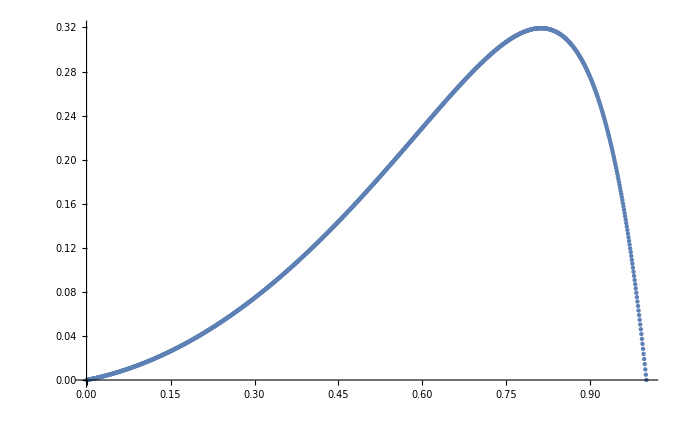
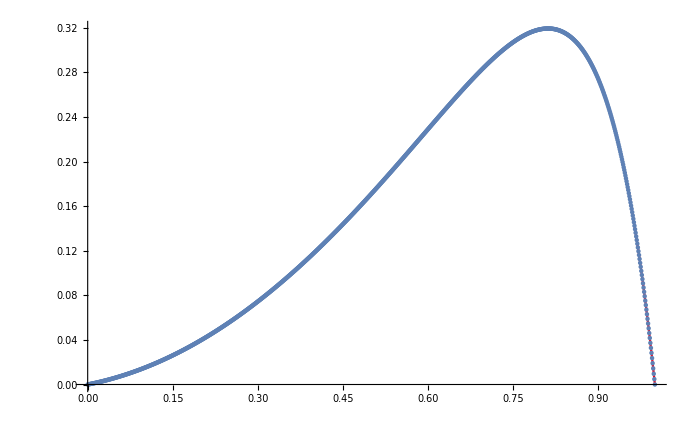
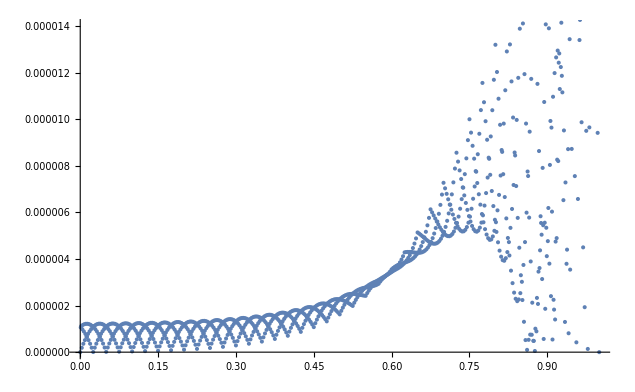

```mathematica
list={{0,0},{0.001,0.000101286},{0.002,0.000202572},{0.003,0.000303858},{0.004,0.000407871},{0.005,0.000512273},{0.006,0.000616675},{0.007,0.000723414},{0.008,0.000830932},{0.009,0.000938451},{0.01,0.00104792},{0.011,0.00115855},{0.012,0.00126918},{0.013,0.00138138},{0.014,0.00149512},{0.015,0.00160887},{0.016,0.00172379},{0.017,0.00184065},{0.018,0.00195752},{0.019,0.00207516},{0.02,0.00219514},{0.021,0.00231512},{0.022,0.00243549},{0.023,0.00255858},{0.024,0.00268168},{0.025,0.00280477},{0.026,0.00293098},{0.027,0.00305718},{0.028,0.00318339},{0.029,0.00331232},{0.03,0.00344164},{0.031,0.00357097},{0.032,0.00370262},{0.033,0.00383506},{0.034,0.00396749},{0.035,0.00410187},{0.036,0.00423742},{0.037,0.00437297},{0.038,0.00451007},{0.039,0.00464873},{0.04,0.00478739},{0.041,0.00492722},{0.042,0.00506899},{0.043,0.00521076},{0.044,0.00535331},{0.045,0.0054982},{0.046,0.00564308},{0.047,0.00578835},{0.048,0.00593635},{0.049,0.00608434},{0.05,0.00623234},{0.051,0.00638345},{0.052,0.00653455},{0.053,0.00668566},{0.054,0.00683949},{0.055,0.00699371},{0.056,0.00714792},{0.057,0.00730447},{0.058,0.0074618},{0.059,0.00761913},{0.06,0.0077784},{0.061,0.00793883},{0.062,0.00809927},{0.063,0.00826126},{0.064,0.00842481},{0.065,0.00858835},{0.066,0.00875307},{0.067,0.00891972},{0.068,0.00908637},{0.069,0.00925381},{0.07,0.00942357},{0.071,0.00959333},{0.072,0.00976348},{0.073,0.00993635},{0.074,0.0101092},{0.075,0.0102821},{0.076,0.0104581},{0.077,0.010634},{0.078,0.01081},{0.079,0.0109887},{0.08,0.0111678},{0.081,0.0113469},{0.082,0.0115283},{0.083,0.0117105},{0.084,0.0118927},{0.085,0.0120768},{0.086,0.0122621},{0.087,0.0124474},{0.088,0.0126342},{0.089,0.0128226},{0.09,0.013011},{0.091,0.0132006},{0.092,0.0133921},{0.093,0.0135836},{0.094,0.0137759},{0.095,0.0139705},{0.096,0.0141651},{0.097,0.0143601},{0.098,0.0145578},{0.099,0.0147555},{0.1,0.0149532},{0.101,0.015154},{0.102,0.0153548},{0.103,0.0155557},{0.104,0.0157592},{0.105,0.0159631},{0.106,0.016167},{0.107,0.0163732},{0.108,0.0165803},{0.109,0.0167873},{0.11,0.0169962},{0.111,0.0172063},{0.112,0.0174164},{0.113,0.0176281},{0.114,0.0178413},{0.115,0.0180545},{0.116,0.0182689},{0.117,0.0184852},{0.118,0.0187015},{0.119,0.0189186},{0.12,0.019138},{0.121,0.0193574},{0.122,0.0195772},{0.123,0.0197997},{0.124,0.0200222},{0.125,0.0202447},{0.126,0.0204703},{0.127,0.0206959},{0.128,0.0209215},{0.129,0.0211498},{0.13,0.0213785},{0.131,0.0216072},{0.132,0.0218382},{0.133,0.02207},{0.134,0.0223018},{0.135,0.0225355},{0.136,0.0227704},{0.137,0.0230052},{0.138,0.0232417},{0.139,0.0234796},{0.14,0.0237176},{0.141,0.0239567},{0.142,0.0241978},{0.143,0.0244388},{0.144,0.0246807},{0.145,0.0249248},{0.146,0.025169},{0.147,0.0254135},{0.148,0.0256607},{0.149,0.025908},{0.15,0.0261552},{0.151,0.0264055},{0.152,0.0266559},{0.153,0.0269062},{0.154,0.0271592},{0.155,0.0274126},{0.156,0.027666},{0.157,0.0279217},{0.158,0.0281782},{0.159,0.0284347},{0.16,0.0286932},{0.161,0.0289527},{0.162,0.0292123},{0.163,0.0294734},{0.164,0.0297361},{0.165,0.0299987},{0.166,0.0302626},{0.167,0.0305283},{0.168,0.030794},{0.169,0.0310605},{0.17,0.0313294},{0.171,0.0315982},{0.172,0.0318674},{0.173,0.0321393},{0.174,0.0324112},{0.175,0.0326831},{0.176,0.032958},{0.177,0.033233},{0.178,0.033508},{0.179,0.0337856},{0.18,0.0340637},{0.181,0.0343417},{0.182,0.0346221},{0.183,0.0349032},{0.184,0.0351843},{0.185,0.0354674},{0.186,0.0357515},{0.187,0.0360357},{0.188,0.0363215},{0.189,0.0366087},{0.19,0.036896},{0.191,0.0371844},{0.192,0.0374747},{0.193,0.037765},{0.194,0.0380561},{0.195,0.0383495},{0.196,0.0386429},{0.197,0.0389367},{0.198,0.0392331},{0.199,0.0395296},{0.2,0.0398261},{0.201,0.0401256},{0.202,0.0404251},{0.203,0.0407246},{0.204,0.0410268},{0.205,0.0413294},{0.206,0.041632},{0.207,0.0419368},{0.208,0.0422425},{0.209,0.0425481},{0.21,0.0428557},{0.211,0.0431644},{0.212,0.0434731},{0.213,0.0437833},{0.214,0.044095},{0.215,0.0444068},{0.216,0.0447197},{0.217,0.0450345},{0.218,0.0453493},{0.219,0.0456648},{0.22,0.0459827},{0.221,0.0463005},{0.222,0.0466187},{0.223,0.0469396},{0.224,0.0472605},{0.225,0.0475814},{0.226,0.0479054},{0.227,0.0482293},{0.228,0.0485532},{0.229,0.0488798},{0.23,0.0492068},{0.231,0.0495338},{0.232,0.0498631},{0.233,0.0501931},{0.234,0.0505231},{0.235,0.050855},{0.236,0.0511881},{0.237,0.0515211},{0.238,0.0518557},{0.239,0.0521918},{0.24,0.0525279},{0.241,0.0528651},{0.242,0.0532042},{0.243,0.0535433},{0.244,0.0538832},{0.245,0.0542254},{0.246,0.0545675},{0.247,0.05491},{0.248,0.0552552},{0.249,0.0556004},{0.25,0.0559456},{0.251,0.0562937},{0.252,0.0566419},{0.253,0.0569901},{0.254,0.057341},{0.255,0.0576922},{0.256,0.0580434},{0.257,0.0583969},{0.258,0.0587511},{0.259,0.0591053},{0.26,0.0594614},{0.261,0.0598187},{0.262,0.0601759},{0.263,0.0605346},{0.264,0.0608949},{0.265,0.0612551},{0.266,0.0616165},{0.267,0.0619797},{0.268,0.062343},{0.269,0.062707},{0.27,0.0630732},{0.271,0.0634395},{0.272,0.0638061},{0.273,0.0641754},{0.274,0.0645446},{0.275,0.0649138},{0.276,0.0652861},{0.277,0.0656583},{0.278,0.0660306},{0.279,0.0664054},{0.28,0.0667806},{0.281,0.0671559},{0.282,0.0675333},{0.283,0.0679115},{0.284,0.0682897},{0.285,0.0686698},{0.286,0.069051},{0.287,0.0694322},{0.288,0.0698148},{0.289,0.070199},{0.29,0.0705832},{0.291,0.0709684},{0.292,0.0713556},{0.293,0.0717427},{0.294,0.0721306},{0.295,0.0725207},{0.296,0.0729108},{0.297,0.0733012},{0.298,0.0736943},{0.299,0.0740873},{0.3,0.0744804},{0.301,0.0748764},{0.302,0.0752724},{0.303,0.0756684},{0.304,0.076067},{0.305,0.0764659},{0.306,0.0768649},{0.307,0.0772661},{0.308,0.077668},{0.309,0.0780699},{0.31,0.0784736},{0.311,0.0788784},{0.312,0.0792833},{0.313,0.0796896},{0.314,0.0800973},{0.315,0.0805051},{0.316,0.080914},{0.317,0.0813247},{0.318,0.0817354},{0.319,0.0821468},{0.32,0.0825604},{0.321,0.082974},{0.322,0.083388},{0.323,0.0838045},{0.324,0.084221},{0.325,0.0846375},{0.326,0.085057},{0.327,0.0854764},{0.328,0.0858958},{0.329,0.0863178},{0.33,0.0867401},{0.331,0.0871625},{0.332,0.087587},{0.333,0.0880122},{0.334,0.0884374},{0.335,0.0888644},{0.336,0.0892925},{0.337,0.0897206},{0.338,0.0901502},{0.339,0.0905811},{0.34,0.0910121},{0.341,0.0914442},{0.342,0.091878},{0.343,0.0923119},{0.344,0.0927464},{0.345,0.0931831},{0.346,0.0936198},{0.347,0.0940569},{0.348,0.0944965},{0.349,0.094936},{0.35,0.0953756},{0.351,0.095818},{0.352,0.0962604},{0.353,0.0967028},{0.354,0.0971477},{0.355,0.0975929},{0.356,0.0980382},{0.357,0.0984855},{0.358,0.0989336},{0.359,0.0993816},{0.36,0.0998315},{0.361,0.100282},{0.362,0.100733},{0.363,0.101185},{0.364,0.101639},{0.365,0.102093},{0.366,0.102548},{0.367,0.103004},{0.368,0.103461},{0.369,0.103918},{0.37,0.104377},{0.371,0.104836},{0.372,0.105296},{0.373,0.105758},{0.374,0.10622},{0.375,0.106682},{0.376,0.107147},{0.377,0.107612},{0.378,0.108076},{0.379,0.108544},{0.38,0.109011},{0.381,0.109479},{0.382,0.109948},{0.383,0.110419},{0.384,0.110889},{0.385,0.111361},{0.386,0.111834},{0.387,0.112307},{0.388,0.112781},{0.389,0.113257},{0.39,0.113733},{0.391,0.11421},{0.392,0.114688},{0.393,0.115166},{0.394,0.115646},{0.395,0.116127},{0.396,0.116608},{0.397,0.117089},{0.398,0.117573},{0.399,0.118057},{0.4,0.118541},{0.401,0.119027},{0.402,0.119514},{0.403,0.12},{0.404,0.120489},{0.405,0.120978},{0.406,0.121467},{0.407,0.121958},{0.408,0.12245},{0.409,0.122942},{0.41,0.123435},{0.411,0.123929},{0.412,0.124424},{0.413,0.124919},{0.414,0.125416},{0.415,0.125913},{0.416,0.126411},{0.417,0.126911},{0.418,0.12741},{0.419,0.12791},{0.42,0.128412},{0.421,0.128915},{0.422,0.129417},{0.423,0.129922},{0.424,0.130426},{0.425,0.130931},{0.426,0.131438},{0.427,0.131945},{0.428,0.132452},{0.429,0.132962},{0.43,0.133471},{0.431,0.133981},{0.432,0.134493},{0.433,0.135005},{0.434,0.135517},{0.435,0.136031},{0.436,0.136545},{0.437,0.13706},{0.438,0.137576},{0.439,0.138093},{0.44,0.13861},{0.441,0.139128},{0.442,0.139648},{0.443,0.140167},{0.444,0.140687},{0.445,0.141209},{0.446,0.141731},{0.447,0.142253},{0.448,0.142778},{0.449,0.143302},{0.45,0.143826},{0.451,0.144353},{0.452,0.144879},{0.453,0.145406},{0.454,0.145935},{0.455,0.146464},{0.456,0.146993},{0.457,0.147524},{0.458,0.148055},{0.459,0.148586},{0.46,0.149119},{0.461,0.149652},{0.462,0.150186},{0.463,0.150721},{0.464,0.151257},{0.465,0.151792},{0.466,0.152329},{0.467,0.152867},{0.468,0.153405},{0.469,0.153944},{0.47,0.154484},{0.471,0.155025},{0.472,0.155565},{0.473,0.156108},{0.474,0.15665},{0.475,0.157192},{0.476,0.157737},{0.477,0.158282},{0.478,0.158826},{0.479,0.159373},{0.48,0.159919},{0.481,0.160466},{0.482,0.161014},{0.483,0.161563},{0.484,0.162112},{0.485,0.162662},{0.486,0.163213},{0.487,0.163764},{0.488,0.164315},{0.489,0.164868},{0.49,0.165421},{0.491,0.165975},{0.492,0.166529},{0.493,0.167084},{0.494,0.167639},{0.495,0.168196},{0.496,0.168753},{0.497,0.16931},{0.498,0.169869},{0.499,0.170427},{0.5,0.170986},{0.501,0.171546},{0.502,0.172107},{0.503,0.172667},{0.504,0.17323},{0.505,0.173792},{0.506,0.174354},{0.507,0.174918},{0.508,0.175482},{0.509,0.176046},{0.51,0.176611},{0.511,0.177177},{0.512,0.177743},{0.513,0.17831},{0.514,0.178877},{0.515,0.179445},{0.516,0.180013},{0.517,0.180582},{0.518,0.181151},{0.519,0.181721},{0.52,0.182292},{0.521,0.182862},{0.522,0.183433},{0.523,0.184006},{0.524,0.184578},{0.525,0.18515},{0.526,0.185724},{0.527,0.186298},{0.528,0.186872},{0.529,0.187447},{0.53,0.188022},{0.531,0.188598},{0.532,0.189174},{0.533,0.189751},{0.534,0.190327},{0.535,0.190905},{0.536,0.191483},{0.537,0.192061},{0.538,0.19264},{0.539,0.193219},{0.54,0.193798},{0.541,0.194378},{0.542,0.194959},{0.543,0.195539},{0.544,0.19612},{0.545,0.196702},{0.546,0.197284},{0.547,0.197865},{0.548,0.198448},{0.549,0.199031},{0.55,0.199614},{0.551,0.200198},{0.552,0.200782},{0.553,0.201366},{0.554,0.20195},{0.555,0.202535},{0.556,0.20312},{0.557,0.203706},{0.558,0.204291},{0.559,0.204877},{0.56,0.205463},{0.561,0.20605},{0.562,0.206637},{0.563,0.207223},{0.564,0.207811},{0.565,0.208398},{0.566,0.208986},{0.567,0.209574},{0.568,0.210162},{0.569,0.21075},{0.57,0.211339},{0.571,0.211927},{0.572,0.212516},{0.573,0.213105},{0.574,0.213695},{0.575,0.214284},{0.576,0.214873},{0.577,0.215463},{0.578,0.216053},{0.579,0.216643},{0.58,0.217233},{0.581,0.217823},{0.582,0.218413},{0.583,0.219003},{0.584,0.219593},{0.585,0.220184},{0.586,0.220774},{0.587,0.221365},{0.588,0.221955},{0.589,0.222546},{0.59,0.223136},{0.591,0.223727},{0.592,0.224318},{0.593,0.224908},{0.594,0.225499},{0.595,0.226089},{0.596,0.22668},{0.597,0.22727},{0.598,0.22786},{0.599,0.228451},{0.6,0.229041},{0.601,0.229631},{0.602,0.230221},{0.603,0.230811},{0.604,0.2314},{0.605,0.23199},{0.606,0.232579},{0.607,0.233169},{0.608,0.233758},{0.609,0.234347},{0.61,0.234935},{0.611,0.235524},{0.612,0.236112},{0.613,0.2367},{0.614,0.237287},{0.615,0.237875},{0.616,0.238462},{0.617,0.239049},{0.618,0.239636},{0.619,0.240222},{0.62,0.240808},{0.621,0.241394},{0.622,0.241979},{0.623,0.242564},{0.624,0.243148},{0.625,0.243733},{0.626,0.244316},{0.627,0.244899},{0.628,0.245482},{0.629,0.246065},{0.63,0.246646},{0.631,0.247228},{0.632,0.247809},{0.633,0.248389},{0.634,0.248969},{0.635,0.249549},{0.636,0.250127},{0.637,0.250706},{0.638,0.251283},{0.639,0.25186},{0.64,0.252437},{0.641,0.253012},{0.642,0.253587},{0.643,0.254162},{0.644,0.254736},{0.645,0.255308},{0.646,0.255881},{0.647,0.256453},{0.648,0.257023},{0.649,0.257593},{0.65,0.258163},{0.651,0.258731},{0.652,0.259298},{0.653,0.259866},{0.654,0.260431},{0.655,0.260996},{0.656,0.261561},{0.657,0.262123},{0.658,0.262685},{0.659,0.263247},{0.66,0.263807},{0.661,0.264366},{0.662,0.264925},{0.663,0.265482},{0.664,0.266037},{0.665,0.266593},{0.666,0.267147},{0.667,0.267699},{0.668,0.268251},{0.669,0.268802},{0.67,0.269351},{0.671,0.269899},{0.672,0.270447},{0.673,0.270991},{0.674,0.271536},{0.675,0.27208},{0.676,0.272621},{0.677,0.273161},{0.678,0.273701},{0.679,0.274238},{0.68,0.274773},{0.681,0.275309},{0.682,0.275842},{0.683,0.276373},{0.684,0.276904},{0.685,0.277433},{0.686,0.277959},{0.687,0.278485},{0.688,0.279009},{0.689,0.279531},{0.69,0.280052},{0.691,0.280571},{0.692,0.281087},{0.693,0.281603},{0.694,0.282118},{0.695,0.282628},{0.696,0.283138},{0.697,0.283648},{0.698,0.284152},{0.699,0.284657},{0.7,0.285161},{0.701,0.285659},{0.702,0.286157},{0.703,0.286655},{0.704,0.287148},{0.705,0.28764},{0.706,0.288131},{0.707,0.288618},{0.708,0.289103},{0.709,0.289587},{0.71,0.290068},{0.711,0.290545},{0.712,0.291023},{0.713,0.291497},{0.714,0.291967},{0.715,0.292438},{0.716,0.292905},{0.717,0.293367},{0.718,0.29383},{0.719,0.29429},{0.72,0.294745},{0.721,0.295199},{0.722,0.295652},{0.723,0.296098},{0.724,0.296544},{0.725,0.29699},{0.726,0.297427},{0.727,0.297864},{0.728,0.298301},{0.729,0.29873},{0.73,0.299157},{0.731,0.299585},{0.732,0.300006},{0.733,0.300424},{0.734,0.300842},{0.735,0.301254},{0.736,0.301662},{0.737,0.30207},{0.738,0.302473},{0.739,0.30287},{0.74,0.303268},{0.741,0.303661},{0.742,0.304048},{0.743,0.304435},{0.744,0.304819},{0.745,0.305194},{0.746,0.305569},{0.747,0.305943},{0.748,0.306307},{0.749,0.30667},{0.75,0.307034},{0.751,0.307385},{0.752,0.307737},{0.753,0.308088},{0.754,0.308428},{0.755,0.308767},{0.756,0.309105},{0.757,0.309434},{0.758,0.309759},{0.759,0.310084},{0.76,0.310401},{0.761,0.310713},{0.762,0.311024},{0.763,0.311329},{0.764,0.311626},{0.765,0.311923},{0.766,0.312215},{0.767,0.312497},{0.768,0.312779},{0.769,0.313058},{0.77,0.313325},{0.771,0.313591},{0.772,0.313856},{0.773,0.314107},{0.774,0.314358},{0.775,0.314609},{0.776,0.314843},{0.777,0.315077},{0.778,0.315312},{0.779,0.315531},{0.78,0.315748},{0.781,0.315965},{0.782,0.316168},{0.783,0.316367},{0.784,0.316566},{0.785,0.316754},{0.786,0.316934},{0.787,0.317114},{0.788,0.317285},{0.789,0.317446},{0.79,0.317608},{0.791,0.317761},{0.792,0.317903},{0.793,0.318044},{0.794,0.31818},{0.795,0.3183},{0.796,0.318421},{0.797,0.318539},{0.798,0.318638},{0.799,0.318737},{0.8,0.318836},{0.801,0.318912},{0.802,0.318989},{0.803,0.319066},{0.804,0.319122},{0.805,0.319176},{0.806,0.31923},{0.807,0.319266},{0.808,0.319295},{0.809,0.319325},{0.81,0.31934},{0.811,0.319345},{0.812,0.31935},{0.813,0.319342},{0.814,0.319321},{0.815,0.319301},{0.816,0.31927},{0.817,0.319223},{0.818,0.319176},{0.819,0.319122},{0.82,0.319047},{0.821,0.318973},{0.822,0.318895},{0.823,0.318792},{0.824,0.318689},{0.825,0.318585},{0.826,0.318453},{0.827,0.31832},{0.828,0.318188},{0.829,0.318029},{0.83,0.317866},{0.831,0.317703},{0.832,0.317516},{0.833,0.317321},{0.834,0.317127},{0.835,0.316912},{0.836,0.316684},{0.837,0.316457},{0.838,0.316213},{0.839,0.315952},{0.84,0.315691},{0.841,0.315417},{0.842,0.315121},{0.843,0.314825},{0.844,0.31452},{0.845,0.314187},{0.846,0.313855},{0.847,0.313518},{0.848,0.313149},{0.849,0.312779},{0.85,0.312409},{0.851,0.312001},{0.852,0.311593},{0.853,0.311184},{0.854,0.310741},{0.855,0.310292},{0.856,0.309844},{0.857,0.309365},{0.858,0.308875},{0.859,0.308385},{0.86,0.307868},{0.861,0.307336},{0.862,0.306803},{0.863,0.306248},{0.864,0.305671},{0.865,0.305094},{0.866,0.3045},{0.867,0.303877},{0.868,0.303255},{0.869,0.30262},{0.87,0.30195},{0.871,0.30128},{0.872,0.300604},{0.873,0.299885},{0.874,0.299166},{0.875,0.298447},{0.876,0.297677},{0.877,0.296907},{0.878,0.296138},{0.879,0.295322},{0.88,0.2945},{0.881,0.293678},{0.882,0.292816},{0.883,0.29194},{0.884,0.291064},{0.885,0.290153},{0.886,0.289221},{0.887,0.288289},{0.888,0.287328},{0.889,0.286338},{0.89,0.285349},{0.891,0.284337},{0.892,0.283287},{0.893,0.282238},{0.894,0.281173},{0.895,0.280062},{0.896,0.278951},{0.897,0.277832},{0.898,0.276657},{0.899,0.275482},{0.9,0.274308},{0.901,0.273067},{0.902,0.271826},{0.903,0.270585},{0.904,0.269285},{0.905,0.267977},{0.906,0.266668},{0.907,0.265306},{0.908,0.263927},{0.909,0.262548},{0.91,0.261124},{0.911,0.259672},{0.912,0.25822},{0.913,0.256731},{0.914,0.255204},{0.915,0.253678},{0.916,0.252122},{0.917,0.250518},{0.918,0.248913},{0.919,0.247289},{0.92,0.245605},{0.921,0.24392},{0.922,0.242226},{0.923,0.240458},{0.924,0.238691},{0.925,0.236924},{0.926,0.235072},{0.927,0.233219},{0.928,0.231366},{0.929,0.229437},{0.93,0.227496},{0.931,0.225555},{0.932,0.223546},{0.933,0.221514},{0.934,0.219482},{0.935,0.217391},{0.936,0.215265},{0.937,0.213138},{0.938,0.210964},{0.939,0.20874},{0.94,0.206517},{0.941,0.204255},{0.942,0.201932},{0.943,0.199608},{0.944,0.197258},{0.945,0.19483},{0.946,0.192402},{0.947,0.189961},{0.948,0.187427},{0.949,0.184892},{0.95,0.182357},{0.951,0.179712},{0.952,0.177066},{0.953,0.174421},{0.954,0.171676},{0.955,0.168916},{0.956,0.166156},{0.957,0.163308},{0.958,0.160431},{0.959,0.157553},{0.96,0.154599},{0.961,0.1516},{0.962,0.1486},{0.963,0.145538},{0.964,0.142413},{0.965,0.139288},{0.966,0.136114},{0.967,0.132859},{0.968,0.129604},{0.969,0.126315},{0.97,0.122926},{0.971,0.119537},{0.972,0.11613},{0.973,0.112603},{0.974,0.109075},{0.975,0.105548},{0.976,0.101877},{0.977,0.0982065},{0.978,0.094536},{0.979,0.0907363},{0.98,0.0869182},{0.981,0.0831001},{0.982,0.0791677},{0.983,0.0751972},{0.984,0.0712268},{0.985,0.067158},{0.986,0.0630302},{0.987,0.0589025},{0.988,0.0546935},{0.989,0.0504033},{0.99,0.0461132},{0.991,0.0417602},{0.992,0.0373024},{0.993,0.0328446},{0.994,0.0283435},{0.995,0.0237126},{0.996,0.0190818},{0.997,0.0144286},{0.998,0.00961905},{0.999,0.00480952},{1,0}};
error={{0,0*10^(0)},{0.001,1.05977*10^(-6)},{0.002,1.12229*10^(-6)},{0.003,1.87586*10^(-7)},{0.004,9.82385*10^(-7)},{0.005,1.16955*10^(-6)},{0.006,3.59575*10^(-7)},{0.007,8.89451*10^(-7)},{0.008,1.20124*10^(-6)},{0.009,5.1597*10^(-7)},{0.01,7.80971*10^(-7)},{0.011,1.21735*10^(-6)},{0.012,6.56776*10^(-7)},{0.013,6.5695*10^(-7)},{0.014,1.21791*10^(-6)},{0.015,7.81995*10^(-7)},{0.016,5.17394*10^(-7)},{0.017,1.2029*10^(-6)},{0.018,8.91632*10^(-7)},{0.019,3.6231*10^(-7)},{0.02,1.17234*10^(-6)},{0.021,9.85689*10^(-7)},{0.022,1.91705*10^(-7)},{0.023,1.12622*10^(-6)},{0.024,1.06417*10^(-6)},{0.025,5.58402*10^(-9)},{0.026,1.06457*10^(-6)},{0.027,1.12709*10^(-6)},{0.028,1.93172*10^(-7)},{0.029,9.87375*10^(-7)},{0.03,1.17443*10^(-6)},{0.031,3.65171*10^(-7)},{0.032,8.9465*10^(-7)},{0.033,1.20622*10^(-6)},{0.034,5.21585*10^(-7)},{0.035,7.86401*10^(-7)},{0.036,1.22246*10^(-6)},{0.037,6.62419*10^(-7)},{0.038,6.62634*10^(-7)},{0.039,1.22314*10^(-6)},{0.04,7.87676*10^(-7)},{0.041,5.23357*10^(-7)},{0.042,1.20829*10^(-6)},{0.043,8.97361*10^(-7)},{0.044,3.68579*10^(-7)},{0.045,1.17789*10^(-6)},{0.046,9.9148*10^(-7)},{0.047,1.98308*10^(-7)},{0.048,1.13197*10^(-6)},{0.049,1.07004*10^(-6)},{0.05,1.2552*10^(-8)},{0.051,1.07053*10^(-6)},{0.052,1.13304*10^(-6)},{0.053,2.00137*10^(-7)},{0.054,9.93572*10^(-7)},{0.055,1.1805*10^(-6)},{0.056,3.72143*10^(-7)},{0.057,9.01109*10^(-7)},{0.058,1.21241*10^(-6)},{0.059,5.28574*10^(-7)},{0.06,7.9315*10^(-7)},{0.061,1.22879*10^(-6)},{0.062,6.69436*10^(-7)},{0.063,6.69702*10^(-7)},{0.064,1.22964*10^(-6)},{0.065,7.94735*10^(-7)},{0.066,5.30777*10^(-7)},{0.067,1.21496*10^(-6)},{0.068,9.04476*10^(-7)},{0.069,3.76384*10^(-7)},{0.07,1.18478*10^(-6)},{0.071,9.98667*10^(-7)},{0.072,2.06535*10^(-7)},{0.073,1.1391*10^(-6)},{0.074,1.07731*10^(-6)},{0.075,2.12397*10^(-8)},{0.076,1.07792*10^(-6)},{0.077,1.14042*10^(-6)},{0.078,2.08814*10^(-7)},{0.079,1.00126*10^(-6)},{0.08,1.18801*10^(-6)},{0.081,3.8082*10^(-7)},{0.082,9.09124*10^(-7)},{0.083,1.22007*10^(-6)},{0.084,5.37264*10^(-7)},{0.085,8.01529*10^(-7)},{0.086,1.23662*10^(-6)},{0.087,6.78154*10^(-7)},{0.088,6.78483*10^(-7)},{0.089,1.23767*10^(-6)},{0.09,8.03498*10^(-7)},{0.091,5.4*10^(-7)},{0.092,1.22323*10^(-6)},{0.093,9.13301*10^(-7)},{0.094,3.86093*10^(-7)},{0.095,1.19331*10^(-6)},{0.096,1.00757*10^(-6)},{0.097,2.16775*10^(-7)},{0.098,1.14792*10^(-6)},{0.099,1.08633*10^(-6)},{0.1,3.20619*10^(-8)},{0.101,1.08707*10^(-6)},{0.102,1.14957*10^(-6)},{0.103,2.19611*10^(-7)},{0.104,1.01078*10^(-6)},{0.105,1.1973*10^(-6)},{0.106,3.91607*10^(-7)},{0.107,9.19059*10^(-7)},{0.108,1.22955*10^(-6)},{0.109,5.48058*10^(-7)},{0.11,8.11919*10^(-7)},{0.111,1.24631*10^(-6)},{0.112,6.88973*10^(-7)},{0.113,6.89378*10^(-7)},{0.114,1.24761*10^(-6)},{0.115,8.14362*10^(-7)},{0.116,5.51451*10^(-7)},{0.117,1.23345*10^(-6)},{0.118,9.24235*10^(-7)},{0.119,3.98155*10^(-7)},{0.12,1.20386*10^(-6)},{0.121,1.0186*10^(-6)},{0.122,2.29509*10^(-7)},{0.123,1.15883*10^(-6)},{0.124,1.09747*10^(-6)},{0.125,4.55302*10^(-8)},{0.126,1.0984*10^(-6)},{0.127,1.16086*10^(-6)},{0.128,2.33034*10^(-7)},{0.129,1.02256*10^(-6)},{0.13,1.20879*10^(-6)},{0.131,4.05004*10^(-7)},{0.132,9.31356*10^(-7)},{0.133,1.24125*10^(-6)},{0.134,5.61449*10^(-7)},{0.135,8.24788*10^(-7)},{0.136,1.25828*10^(-6)},{0.137,7.02383*10^(-7)},{0.138,7.0288*10^(-7)},{0.139,1.25988*10^(-6)},{0.14,8.27816*10^(-7)},{0.141,5.65653*10^(-7)},{0.142,1.24607*10^(-6)},{0.143,9.37761*10^(-7)},{0.144,4.13127*10^(-7)},{0.145,1.21687*10^(-6)},{0.146,1.03223*10^(-6)},{0.147,2.45326*10^(-7)},{0.148,1.1723*10^(-6)},{0.149,1.11124*10^(-6)},{0.15,6.22746*10^(-8)},{0.151,1.11238*10^(-6)},{0.152,1.17481*10^(-6)},{0.153,2.49704*10^(-7)},{0.154,1.03712*10^(-6)},{0.155,1.22296*10^(-6)},{0.156,4.21623*10^(-7)},{0.157,9.46557*10^(-7)},{0.158,1.25569*10^(-6)},{0.159,5.78044*10^(-7)},{0.16,8.40706*10^(-7)},{0.161,1.27303*10^(-6)},{0.162,7.18982*10^(-7)},{0.163,7.19593*10^(-7)},{0.164,1.275*10^(-6)},{0.165,8.44452*10^(-7)},{0.166,5.83244*10^(-7)},{0.167,1.26162*10^(-6)},{0.168,9.54471*10^(-7)},{0.169,4.31687*10^(-7)},{0.17,1.23292*10^(-6)},{0.171,1.04906*10^(-6)},{0.172,2.64952*10^(-7)},{0.173,1.18891*10^(-6)},{0.174,1.12823*10^(-6)},{0.175,8.30698*10^(-8)},{0.176,1.12962*10^(-6)},{0.177,1.192*10^(-6)},{0.178,2.70382*10^(-7)},{0.179,1.05508*10^(-6)},{0.18,1.24041*10^(-6)},{0.181,4.42213*10^(-7)},{0.182,9.6532*10^(-7)},{0.183,1.27346*10^(-6)},{0.184,5.98579*10^(-7)},{0.185,8.60365*10^(-7)},{0.186,1.29118*10^(-6)},{0.187,7.395*10^(-7)},{0.188,7.40248*10^(-7)},{0.189,1.29361*10^(-6)},{0.19,8.64994*10^(-7)},{0.191,6.05003*10^(-7)},{0.192,1.28075*10^(-6)},{0.193,9.75084*10^(-7)},{0.194,4.54666*10^(-7)},{0.195,1.25266*10^(-6)},{0.196,1.06979*10^(-6)},{0.197,2.89274*10^(-7)},{0.198,1.20934*10^(-6)},{0.199,1.14914*10^(-6)},{0.2,1.08866*10^(-7)},{0.201,1.15084*10^(-6)},{0.202,1.21315*10^(-6)},{0.203,2.96*10^(-7)},{0.204,1.0772*10^(-6)},{0.205,1.26186*10^(-6)},{0.206,4.6769*10^(-7)},{0.207,9.8844*10^(-7)},{0.208,1.2953*10^(-6)},{0.209,6.23957*10^(-7)},{0.21,8.84607*10^(-7)},{0.211,1.31348*10^(-6)},{0.212,7.64825*10^(-7)},{0.213,7.65739*10^(-7)},{0.214,1.31645*10^(-6)},{0.215,8.90319*10^(-7)},{0.216,6.31881*10^(-7)},{0.217,1.30424*10^(-6)},{0.218,1.00047*10^(-6)},{0.219,4.83077*10^(-7)},{0.22,1.27689*10^(-6)},{0.221,1.0953*10^(-6)},{0.222,3.19375*10^(-7)},{0.223,1.23444*10^(-6)},{0.224,1.17484*10^(-6)},{0.225,1.40826*10^(-7)},{0.226,1.17692*10^(-6)},{0.227,1.23913*10^(-6)},{0.228,3.27696*10^(-7)},{0.229,1.10439*10^(-6)},{0.23,1.28819*10^(-6)},{0.231,4.99168*10^(-7)},{0.232,1.01688*10^(-6)},{0.233,1.32208*10^(-6)},{0.234,6.5527*10^(-7)},{0.235,9.14449*10^(-7)},{0.236,1.34081*10^(-6)},{0.237,7.96032*10^(-7)},{0.238,7.97146*10^(-7)},{0.239,1.34445*10^(-6)},{0.24,9.21486*10^(-7)},{0.241,6.65028*10^(-7)},{0.242,1.33303*10^(-6)},{0.243,1.03167*10^(-6)},{0.244,5.18151*10^(-7)},{0.245,1.3066*10^(-6)},{0.246,1.12661*10^(-6)},{0.247,3.56577*10^(-7)},{0.248,1.2652*10^(-6)},{0.249,1.20636*10^(-6)},{0.25,1.80371*10^(-7)},{0.251,1.2089*10^(-6)},{0.252,1.27095*10^(-6)},{0.253,3.66856*10^(-7)},{0.254,1.13774*10^(-6)},{0.255,1.32043*10^(-6)},{0.256,5.38002*10^(-7)},{0.257,1.0518*10^(-6)},{0.258,1.35484*10^(-6)},{0.259,6.93843*10^(-7)},{0.26,9.51117*10^(-7)},{0.261,1.37424*10^(-6)},{0.262,8.34419*10^(-7)},{0.263,8.35774*10^(-7)},{0.264,1.37868*10^(-6)},{0.265,9.5977*10^(-7)},{0.266,7.05837*10^(-7)},{0.267,1.36822*10^(-6)},{0.268,1.06994*10^(-6)},{0.269,5.61381*10^(-7)},{0.27,1.34291*10^(-6)},{0.271,1.16498*10^(-6)},{0.272,4.02484*10^(-7)},{0.273,1.30282*10^(-6)},{0.274,1.24493*10^(-6)},{0.275,2.2923*10^(-7)},{0.276,1.24802*10^(-6)},{0.277,1.30986*10^(-6)},{0.278,4.15163*10^(-7)},{0.279,1.17858*10^(-6)},{0.28,1.35981*10^(-6)},{0.281,5.85829*10^(-7)},{0.282,1.09457*10^(-6)},{0.283,1.39484*10^(-6)},{0.284,7.41274*10^(-7)},{0.285,9.9608*10^(-7)},{0.286,1.41503*10^(-6)},{0.287,8.81547*10^(-7)},{0.288,8.83189*10^(-7)},{0.289,1.42044*10^(-6)},{0.29,1.0067*10^(-6)},{0.291,7.55987*10^(-7)},{0.292,1.41113*10^(-6)},{0.293,1.11679*10^(-6)},{0.294,6.14571*10^(-7)},{0.295,1.3872*10^(-6)},{0.296,1.21188*10^(-6)},{0.297,4.59042*10^(-7)},{0.298,1.34872*10^(-6)},{0.299,1.29203*10^(-6)},{0.3,2.89505*10^(-7)},{0.301,1.29577*10^(-6)},{0.302,1.3573*10^(-6)},{0.303,4.74654*10^(-7)},{0.304,1.22845*10^(-6)},{0.305,1.40778*10^(-6)},{0.306,6.44628*10^(-7)},{0.307,1.14686*10^(-6)},{0.308,1.44354*10^(-6)},{0.309,7.99484*10^(-7)},{0.31,1.05109*10^(-6)},{0.311,1.46465*10^(-6)},{0.312,9.39286*10^(-7)},{0.313,9.41267*10^(-7)},{0.314,1.47122*10^(-6)},{0.315,1.0641*10^(-6)},{0.316,8.17493*10^(-7)},{0.317,1.46332*10^(-6)},{0.318,1.174*10^(-6)},{0.319,6.79893*10^(-7)},{0.32,1.44106*10^(-6)},{0.321,1.26906*10^(-6)},{0.322,5.28596*10^(-7)},{0.323,1.40455*10^(-6)},{0.324,1.34937*10^(-6)},{0.325,3.6374*10^(-7)},{0.326,1.35389*10^(-6)},{0.327,1.415*10^(-6)},{0.328,5.47786*10^(-7)},{0.329,1.2892*10^(-6)},{0.33,1.46606*10^(-6)},{0.331,7.1677*10^(-7)},{0.332,1.21061*10^(-6)},{0.333,1.50263*10^(-6)},{0.334,8.70768*10^(-7)},{0.335,1.11824*10^(-6)},{0.336,1.52484*10^(-6)},{0.337,1.00986*10^(-6)},{0.338,1.01224*10^(-6)},{0.339,1.53278*10^(-6)},{0.34,1.13413*10^(-6)},{0.341,8.92758*10^(-7)},{0.342,1.52658*10^(-6)},{0.343,1.24367*10^(-6)},{0.344,7.59945*10^(-7)},{0.345,1.50636*10^(-6)},{0.346,1.33859*10^(-6)},{0.347,6.13967*10^(-7)},{0.348,1.47226*10^(-6)},{0.349,1.41897*10^(-6)},{0.35,4.55*10^(-7)},{0.351,1.42441*10^(-6)},{0.352,1.48494*10^(-6)},{0.353,6.37506*10^(-7)},{0.354,1.36298*10^(-6)},{0.355,1.53662*10^(-6)},{0.356,8.05093*10^(-7)},{0.357,1.28811*10^(-6)},{0.358,1.57412*10^(-6)},{0.359,9.57858*10^(-7)},{0.36,1.19997*10^(-6)},{0.361,1.59759*10^(-6)},{0.362,1.0959*10^(-6)},{0.363,1.09875*10^(-6)},{0.364,1.60716*10^(-6)},{0.365,1.21934*10^(-6)},{0.366,9.84638*10^(-7)},{0.367,1.60299*10^(-6)},{0.368,1.32828*10^(-6)},{0.369,8.57826*10^(-7)},{0.37,1.58525*10^(-6)},{0.371,1.42285*10^(-6)},{0.372,7.18529*10^(-7)},{0.373,1.55409*10^(-6)},{0.374,1.50319*10^(-6)},{0.375,5.6697*10^(-7)},{0.376,1.5097*10^(-6)},{0.377,1.56943*10^(-6)},{0.378,7.47339*10^(-7)},{0.379,1.45228*10^(-6)},{0.38,1.62174*10^(-6)},{0.381,9.12969*10^(-7)},{0.382,1.38203*10^(-6)},{0.383,1.66026*10^(-6)},{0.384,1.06398*10^(-6)},{0.385,1.29916*10^(-6)},{0.386,1.68518*10^(-6)},{0.387,1.20051*10^(-6)},{0.388,1.2039*10^(-6)},{0.389,1.69667*10^(-6)},{0.39,1.32269*10^(-6)},{0.391,1.0965*10^(-6)},{0.392,1.69494*10^(-6)},{0.393,1.43067*10^(-6)},{0.394,9.77206*10^(-7)},{0.395,1.68017*10^(-6)},{0.396,1.52462*10^(-6)},{0.397,8.46294*10^(-7)},{0.398,1.6526*10^(-6)},{0.399,1.6047*10^(-6)},{0.4,7.0405*10^(-7)},{0.401,1.61246*10^(-6)},{0.402,1.6711*10^(-6)},{0.403,8.81472*10^(-7)},{0.404,1.55999*10^(-6)},{0.405,1.724*10^(-6)},{0.406,1.04438*10^(-6)},{0.407,1.49545*10^(-6)},{0.408,1.76363*10^(-6)},{0.409,1.19292*10^(-6)},{0.41,1.41912*10^(-6)},{0.411,1.79018*10^(-6)},{0.412,1.32728*10^(-6)},{0.413,1.33129*10^(-6)},{0.414,1.80391*10^(-6)},{0.415,1.44762*10^(-6)},{0.416,1.23228*10^(-6)},{0.417,1.80506*10^(-6)},{0.418,1.55414*10^(-6)},{0.419,1.1224*10^(-6)},{0.42,1.79389*10^(-6)},{0.421,1.64703*10^(-6)},{0.422,1.00201*10^(-6)},{0.423,1.77067*10^(-6)},{0.424,1.72653*10^(-6)},{0.425,8.71472*10^(-7)},{0.426,1.73572*10^(-6)},{0.427,1.79287*10^(-6)},{0.428,1.04485*10^(-6)},{0.429,1.68934*10^(-6)},{0.43,1.84628*10^(-6)},{0.431,1.20399*10^(-6)},{0.432,1.63187*10^(-6)},{0.433,1.88704*10^(-6)},{0.434,1.34909*10^(-6)},{0.435,1.56366*10^(-6)},{0.436,1.91542*10^(-6)},{0.437,1.48037*10^(-6)},{0.438,1.48508*10^(-6)},{0.439,1.93173*10^(-6)},{0.44,1.59805*10^(-6)},{0.441,1.39654*10^(-6)},{0.442,1.93627*10^(-6)},{0.443,1.70238*10^(-6)},{0.444,1.29844*10^(-6)},{0.445,1.9294*10^(-6)},{0.446,1.79362*10^(-6)},{0.447,1.19125*10^(-6)},{0.448,1.91147*10^(-6)},{0.449,1.87205*10^(-6)},{0.45,1.07541*10^(-6)},{0.451,1.88285*10^(-6)},{0.452,1.93797*10^(-6)},{0.453,1.24326*10^(-6)},{0.454,1.84395*10^(-6)},{0.455,1.99169*10^(-6)},{0.456,1.39721*10^(-6)},{0.457,1.7952*10^(-6)},{0.458,2.03355*10^(-6)},{0.459,1.53753*10^(-6)},{0.46,1.73705*10^(-6)},{0.461,2.06391*10^(-6)},{0.462,1.66449*10^(-6)},{0.463,1.66998*10^(-6)},{0.464,2.08315*10^(-6)},{0.465,1.77838*10^(-6)},{0.466,1.5945*10^(-6)},{0.467,2.09168*10^(-6)},{0.468,1.87952*10^(-6)},{0.469,1.51114*10^(-6)},{0.47,2.08993*10^(-6)},{0.471,1.96822*10^(-6)},{0.472,1.42048*10^(-6)},{0.473,2.07836*10^(-6)},{0.474,2.04487*10^(-6)},{0.475,1.32311*10^(-6)},{0.476,2.05745*10^(-6)},{0.477,2.10982*10^(-6)},{0.478,1.48342*10^(-6)},{0.479,2.02772*10^(-6)},{0.48,2.16349*10^(-6)},{0.481,1.63028*10^(-6)},{0.482,1.98973*10^(-6)},{0.483,2.20632*10^(-6)},{0.484,1.764*10^(-6)},{0.485,1.94403*10^(-6)},{0.486,2.23875*10^(-6)},{0.487,1.88494*10^(-6)},{0.488,1.89126*10^(-6)},{0.489,2.26128*10^(-6)},{0.49,1.99348*10^(-6)},{0.491,1.83207*10^(-6)},{0.492,2.27443*10^(-6)},{0.493,2.09*10^(-6)},{0.494,1.76712*10^(-6)},{0.495,2.27874*10^(-6)},{0.496,2.17494*10^(-6)},{0.497,1.69717*10^(-6)},{0.498,2.27482*10^(-6)},{0.499,2.24876*10^(-6)},{0.5,1.62297*10^(-6)},{0.501,2.26327*10^(-6)},{0.502,2.31193*10^(-6)},{0.503,1.77305*10^(-6)},{0.504,2.24476*10^(-6)},{0.505,2.36498*10^(-6)},{0.506,1.91022*10^(-6)},{0.507,2.21999*10^(-6)},{0.508,2.40845*10^(-6)},{0.509,2.03489*10^(-6)},{0.51,2.1897*10^(-6)},{0.511,2.44294*10^(-6)},{0.512,2.1475*10^(-6)},{0.513,2.15468*10^(-6)},{0.514,2.46908*10^(-6)},{0.515,2.24853*10^(-6)},{0.516,2.11576*10^(-6)},{0.517,2.48752*10^(-6)},{0.518,2.33849*10^(-6)},{0.519,2.07381*10^(-6)},{0.52,2.49897*10^(-6)},{0.521,2.41793*10^(-6)},{0.522,2.02978*10^(-6)},{0.523,2.50418*10^(-6)},{0.524,2.48743*10^(-6)},{0.525,1.98464*10^(-6)},{0.526,2.50395*10^(-6)},{0.527,2.54761*10^(-6)},{0.528,2.12088*10^(-6)},{0.529,2.49913*10^(-6)},{0.53,2.59913*10^(-6)},{0.531,2.24487*10^(-6)},{0.532,2.4906*10^(-6)},{0.533,2.64269*10^(-6)},{0.534,2.35715*10^(-6)},{0.535,2.47933*10^(-6)},{0.536,2.67906*10^(-6)},{0.537,2.45828*10^(-6)},{0.538,2.46631*10^(-6)},{0.539,2.70902*10^(-6)},{0.54,2.54888*10^(-6)},{0.541,2.45261*10^(-6)},{0.542,2.73344*10^(-6)},{0.543,2.62959*10^(-6)},{0.544,2.43936*10^(-6)},{0.545,2.7532*10^(-6)},{0.546,2.70111*10^(-6)},{0.547,2.42775*10^(-6)},{0.548,2.76928*10^(-6)},{0.549,2.76419*10^(-6)},{0.55,2.41904*10^(-6)},{0.551,2.7827*10^(-6)},{0.552,2.81962*10^(-6)},{0.553,2.53659*10^(-6)},{0.554,2.79452*10^(-6)},{0.555,2.86825*10^(-6)},{0.556,2.64272*10^(-6)},{0.557,2.80591*10^(-6)},{0.558,2.91097*10^(-6)},{0.559,2.73812*10^(-6)},{0.56,2.81807*10^(-6)},{0.561,2.94875*10^(-6)},{0.562,2.82352*10^(-6)},{0.563,2.83229*10^(-6)},{0.564,2.98262*10^(-6)},{0.565,2.89969*10^(-6)},{0.566,2.84994*10^(-6)},{0.567,3.01365*10^(-6)},{0.568,2.96746*10^(-6)},{0.569,2.87246*10^(-6)},{0.57,3.04301*10^(-6)},{0.571,3.02772*10^(-6)},{0.572,2.90138*10^(-6)},{0.573,3.07193*10^(-6)},{0.574,3.08143*10^(-6)},{0.575,2.93831*10^(-6)},{0.576,3.10171*10^(-6)},{0.577,3.1296*10^(-6)},{0.578,3.03068*10^(-6)},{0.579,3.13372*10^(-6)},{0.58,3.17331*10^(-6)},{0.581,3.11268*10^(-6)},{0.582,3.16945*10^(-6)},{0.583,3.21372*10^(-6)},{0.584,3.18516*10^(-6)},{0.585,3.21045*10^(-6)},{0.586,3.25205*10^(-6)},{0.587,3.24907*10^(-6)},{0.588,3.25836*10^(-6)},{0.589,3.28961*10^(-6)},{0.59,3.30538*10^(-6)},{0.591,3.31493*10^(-6)},{0.592,3.3278*10^(-6)},{0.593,3.35517*10^(-6)},{0.594,3.382*10^(-6)},{0.595,3.36809*10^(-6)},{0.596,3.39958*10^(-6)},{0.597,3.46154*10^(-6)},{0.598,3.41206*10^(-6)},{0.599,3.43981*10^(-6)},{0.6,3.55562*10^(-6)},{0.601,3.46137*10^(-6)},{0.602,3.47716*10^(-6)},{0.603,3.61415*10^(-6)},{0.604,3.51779*10^(-6)},{0.605,3.51303*10^(-6)},{0.606,3.6636*10^(-6)},{0.607,3.58321*10^(-6)},{0.608,3.54887*10^(-6)},{0.609,3.70506*10^(-6)},{0.61,3.65962*10^(-6)},{0.611,3.58628*10^(-6)},{0.612,3.73972*10^(-6)},{0.613,3.74911*10^(-6)},{0.614,3.62691*10^(-6)},{0.615,3.76885*10^(-6)},{0.616,3.85394*10^(-6)},{0.617,3.67255*10^(-6)},{0.618,3.7938*10^(-6)},{0.619,3.97646*10^(-6)},{0.62,3.72509*10^(-6)},{0.621,3.81603*10^(-6)},{0.622,4.11918*10^(-6)},{0.623,3.78654*10^(-6)},{0.624,3.8371*10^(-6)},{0.625,4.28475*10^(-6)},{0.626,3.85904*10^(-6)},{0.627,3.85865*10^(-6)},{0.628,4.29791*10^(-6)},{0.629,3.94485*10^(-6)},{0.63,3.88247*10^(-6)},{0.631,4.30357*10^(-6)},{0.632,4.04638*10^(-6)},{0.633,3.91043*10^(-6)},{0.634,4.30314*10^(-6)},{0.635,4.16618*10^(-6)},{0.636,3.94454*10^(-6)},{0.637,4.29813*10^(-6)},{0.638,4.30694*10^(-6)},{0.639,3.98695*10^(-6)},{0.64,4.29017*10^(-6)},{0.641,4.47153*10^(-6)},{0.642,4.03994*10^(-6)},{0.643,4.28098*10^(-6)},{0.644,4.66297*10^(-6)},{0.645,4.10592*10^(-6)},{0.646,4.27243*10^(-6)},{0.647,4.88448*10^(-6)},{0.648,4.18746*10^(-6)},{0.649,4.2665*10^(-6)},{0.65,5.13945*10^(-6)},{0.651,4.2873*10^(-6)},{0.652,4.2653*10^(-6)},{0.653,5.09185*10^(-6)},{0.654,4.40834*10^(-6)},{0.655,4.27111*10^(-6)},{0.656,5.03873*10^(-6)},{0.657,4.55365*10^(-6)},{0.658,4.28633*10^(-6)},{0.659,4.98187*10^(-6)},{0.66,4.7265*10^(-6)},{0.661,4.31354*10^(-6)},{0.662,4.92321*10^(-6)},{0.663,4.93034*10^(-6)},{0.664,4.35546*10^(-6)},{0.665,4.86481*10^(-6)},{0.666,5.16884*10^(-6)},{0.667,4.41502*10^(-6)},{0.668,4.8089*10^(-6)},{0.669,5.44587*10^(-6)},{0.67,4.49531*10^(-6)},{0.671,4.75785*10^(-6)},{0.672,5.76554*10^(-6)},{0.673,4.59961*10^(-6)},{0.674,4.71419*10^(-6)},{0.675,6.1322*10^(-6)},{0.676,4.73143*10^(-6)},{0.677,4.68063*10^(-6)},{0.678,6.0034*10^(-6)},{0.679,4.89448*10^(-6)},{0.68,4.66006*10^(-6)},{0.681,5.87151*10^(-6)},{0.682,5.09269*10^(-6)},{0.683,4.65558*10^(-6)},{0.684,5.73881*10^(-6)},{0.685,5.33024*10^(-6)},{0.686,4.67045*10^(-6)},{0.687,5.60777*10^(-6)},{0.688,5.61156*10^(-6)},{0.689,4.70819*10^(-6)},{0.69,5.48102*10^(-6)},{0.691,5.94133*10^(-6)},{0.692,4.77252*10^(-6)},{0.693,5.36141*10^(-6)},{0.694,6.32452*10^(-6)},{0.695,4.8674*10^(-6)},{0.696,5.25197*10^(-6)},{0.697,6.76638*10^(-6)},{0.698,4.99704*10^(-6)},{0.699,5.15593*10^(-6)},{0.7,7.27248*10^(-6)},{0.701,5.16591*10^(-6)},{0.702,5.07675*10^(-6)},{0.703,7.03533*10^(-6)},{0.704,5.37876*10^(-6)},{0.705,5.01814*10^(-6)},{0.706,6.79807*10^(-6)},{0.707,5.64064*10^(-6)},{0.708,4.98404*10^(-6)},{0.709,6.56364*10^(-6)},{0.71,5.95688*10^(-6)},{0.711,4.97865*10^(-6)},{0.712,6.33517*10^(-6)},{0.713,6.33315*10^(-6)},{0.714,5.00645*10^(-6)},{0.715,6.11605*10^(-6)},{0.716,6.77546*10^(-6)},{0.717,5.07219*10^(-6)},{0.718,5.90989*10^(-6)},{0.719,7.29015*10^(-6)},{0.72,5.18095*10^(-6)},{0.721,5.72056*10^(-6)},{0.722,7.88396*10^(-6)},{0.723,5.33812*10^(-6)},{0.724,5.55221*10^(-6)},{0.725,8.564*10^(-6)},{0.726,5.54941*10^(-6)},{0.727,5.40926*10^(-6)},{0.728,8.18246*10^(-6)},{0.729,5.82091*10^(-6)},{0.73,5.29643*10^(-6)},{0.731,7.8045*10^(-6)},{0.732,6.15906*10^(-6)},{0.733,5.21878*10^(-6)},{0.734,7.43385*10^(-6)},{0.735,6.57071*10^(-6)},{0.736,5.18167*10^(-6)},{0.737,7.07453*10^(-6)},{0.738,7.0631*10^(-6)},{0.739,5.19082*10^(-6)},{0.74,6.73086*10^(-6)},{0.741,7.64391*10^(-6)},{0.742,5.25234*10^(-6)},{0.743,6.40745*10^(-6)},{0.744,8.32129*10^(-6)},{0.745,5.3727*10^(-6)},{0.746,6.10925*10^(-6)},{0.747,9.10385*10^(-6)},{0.748,5.55879*10^(-6)},{0.749,5.84157*10^(-6)},{0.75,1.00007*10^(-5)},{0.751,5.81794*10^(-6)},{0.752,5.61004*10^(-6)},{0.753,9.427*10^(-6)},{0.754,6.15792*10^(-6)},{0.755,5.42071*10^(-6)},{0.756,8.86141*10^(-6)},{0.757,6.58698*10^(-6)},{0.758,5.28004*10^(-6)},{0.759,8.30868*10^(-6)},{0.76,7.11389*10^(-6)},{0.761,5.19488*10^(-6)},{0.762,7.77396*10^(-6)},{0.763,7.74791*10^(-6)},{0.764,5.17257*10^(-6)},{0.765,7.26274*10^(-6)},{0.766,8.49889*10^(-6)},{0.767,5.22089*10^(-6)},{0.768,6.78094*10^(-6)},{0.769,9.37725*10^(-6)},{0.77,5.34813*10^(-6)},{0.771,6.33487*10^(-6)},{0.772,1.0394*10^(-5)},{0.773,5.56312*10^(-6)},{0.774,5.93129*10^(-6)},{0.775,1.15608*10^(-5)},{0.776,5.87522*10^(-6)},{0.777,5.57745*10^(-6)},{0.778,1.07317*10^(-5)},{0.779,6.29438*10^(-6)},{0.78,5.28105*10^(-6)},{0.781,9.91627*10^(-6)},{0.782,6.83116*10^(-6)},{0.783,5.05034*10^(-6)},{0.784,9.12054*10^(-6)},{0.785,7.49677*10^(-6)},{0.786,4.8941*10^(-6)},{0.787,8.3511*10^(-6)},{0.788,8.30308*10^(-6)},{0.789,4.8217*10^(-6)},{0.79,7.61498*10^(-6)},{0.791,9.26269*10^(-6)},{0.792,4.8431*10^(-6)},{0.793,6.91972*10^(-6)},{0.794,1.03889*10^(-5)},{0.795,4.96891*10^(-6)},{0.796,6.27339*10^(-6)},{0.797,1.16959*10^(-5)},{0.798,5.21041*10^(-6)},{0.799,5.68464*10^(-6)},{0.8,1.31986*10^(-5)},{0.801,5.57959*10^(-6)},{0.802,5.16271*10^(-6)},{0.803,1.20304*10^(-5)},{0.804,6.08918*10^(-6)},{0.805,4.71747*10^(-6)},{0.806,1.08827*10^(-5)},{0.807,6.75268*10^(-6)},{0.808,4.35944*10^(-6)},{0.809,9.76309*10^(-6)},{0.81,7.58446*10^(-6)},{0.811,4.09987*10^(-6)},{0.812,8.68009*10^(-6)},{0.813,8.5997*10^(-6)},{0.814,3.95073*10^(-6)},{0.815,7.64262*10^(-6)},{0.816,9.81452*10^(-6)},{0.817,3.92477*10^(-6)},{0.818,6.66034*10^(-6)},{0.819,1.1246*10^(-5)},{0.82,4.03554*10^(-6)},{0.821,5.74354*10^(-6)},{0.822,1.29122*10^(-5)},{0.823,4.29749*10^(-6)},{0.824,4.90329*10^(-6)},{0.825,1.48323*10^(-5)},{0.826,4.72595*10^(-6)},{0.827,4.15137*10^(-6)},{0.828,1.32144*10^(-5)},{0.829,5.33722*10^(-6)},{0.83,3.50042*10^(-6)},{0.831,1.16252*10^(-5)},{0.832,6.14858*10^(-6)},{0.833,2.96389*10^(-6)},{0.834,1.00746*10^(-5)},{0.835,7.17838*10^(-6)},{0.836,2.55616*10^(-6)},{0.837,8.57336*10^(-6)},{0.838,8.4461*10^(-6)},{0.839,2.29252*10^(-6)},{0.84,7.13285*10^(-6)},{0.841,9.97236*10^(-6)},{0.842,2.18929*10^(-6)},{0.843,5.7654*10^(-6)},{0.844,1.1779*10^(-5)},{0.845,2.26383*10^(-6)},{0.846,4.4842*10^(-6)},{0.847,1.38892*10^(-5)},{0.848,2.53458*10^(-6)},{0.849,3.30336*10^(-6)},{0.85,1.63275*10^(-5)},{0.851,3.02117*10^(-6)},{0.852,2.23797*10^(-6)},{0.853,1.41138*10^(-5)},{0.854,3.74446*10^(-6)},{0.855,1.30416*10^(-6)},{0.856,1.19388*10^(-5)},{0.857,4.72656*10^(-6)},{0.858,5.19132*10^(-7)},{0.859,9.81533*10^(-6)},{0.86,5.99097*10^(-6)},{0.861,9.87376*10^(-8)},{0.862,7.75688*10^(-6)},{0.863,7.5626*10^(-6)},{0.864,5.29873*10^(-7)},{0.865,5.77813*10^(-6)},{0.866,9.46785*10^(-6)},{0.867,7.53421*10^(-7)},{0.868,3.8948*10^(-6)},{0.869,1.17347*10^(-5)},{0.87,7.47183*10^(-7)},{0.871,2.12371*10^(-6)},{0.872,1.43928*10^(-5)},{0.873,4.87545*10^(-7)},{0.874,4.82907*10^(-7)},{0.875,1.74735*10^(-5)},{0.876,5.05978*10^(-8)},{0.877,1.00833*10^(-6)},{0.878,1.44712*10^(-5)},{0.879,8.93918*10^(-7)},{0.88,2.3294*10^(-6)},{0.881,1.15199*10^(-5)},{0.882,2.07074*10^(-6)},{0.883,3.45829*10^(-6)},{0.884,8.63571*10^(-6)},{0.885,3.61112*10^(-6)},{0.886,4.37151*10^(-6)},{0.887,5.83604*10^(-6)},{0.888,5.54694*10^(-6)},{0.889,5.04403*10^(-6)},{0.89,3.13961*10^(-6)},{0.891,7.912*10^(-6)},{0.892,5.44918*10^(-6)},{0.893,5.66472*10^(-7)},{0.894,1.07421*10^(-5)},{0.895,5.55856*10^(-6)},{0.896,1.86186*10^(-6)},{0.897,1.40753*10^(-5)},{0.898,5.34198*10^(-6)},{0.899,4.12236*10^(-6)},{0.9,1.79516*10^(-5)},{0.901,4.7673*10^(-6)},{0.902,6.19038*10^(-6)},{0.903,1.39064*10^(-5)},{0.904,3.80041*10^(-6)},{0.905,8.03956*10^(-6)},{0.906,9.92699*10^(-6)},{0.907,2.40506*10^(-6)},{0.908,9.64179*10^(-6)},{0.909,6.03391*10^(-6)},{0.91,5.42771*10^(-7)},{0.911,1.0967*10^(-5)},{0.912,2.24938*10^(-6)},{0.913,1.82725*10^(-6)},{0.914,1.19833*10^(-5)},{0.915,1.40272*10^(-6)},{0.916,4.74828*10^(-6)},{0.917,1.26564*10^(-5)},{0.918,4.89676*10^(-6)},{0.919,8.26617*10^(-6)},{0.92,1.29501*10^(-5)},{0.921,8.20526*10^(-6)},{0.922,1.24295*10^(-5)},{0.923,1.28258*10^(-5)},{0.924,1.12988*10^(-5)},{0.925,1.72897*10^(-5)},{0.926,1.22423*10^(-5)},{0.927,1.41459*10^(-5)},{0.928,1.18666*10^(-5)},{0.929,1.1156*10^(-5)},{0.93,1.67128*10^(-5)},{0.931,6.52699*10^(-6)},{0.932,9.52044*10^(-6)},{0.933,1.89637*10^(-5)},{0.934,1.29718*10^(-6)},{0.935,7.28648*10^(-6)},{0.936,2.08601*10^(-5)},{0.937,3.79447*10^(-6)},{0.938,4.40186*10^(-6)},{0.939,2.23611*10^(-5)},{0.94,8.7175*10^(-6)},{0.941,8.11188*10^(-7)},{0.942,2.3423*10^(-5)},{0.943,1.34392*10^(-5)},{0.944,3.54423*10^(-6)},{0.945,2.39995*10^(-5)},{0.946,1.79244*10^(-5)},{0.947,8.72658*10^(-6)},{0.948,2.4041*10^(-5)},{0.949,2.21355*10^(-5)},{0.95,1.48017*10^(-5)},{0.951,2.34951*10^(-5)},{0.952,2.60323*10^(-5)},{0.953,7.55941*10^(-6)},{0.954,2.23058*10^(-5)},{0.955,2.95719*10^(-5)},{0.956,4.2185*10^(-7)},{0.957,2.04138*10^(-5)},{0.958,3.2708*10^(-5)},{0.959,6.57736*10^(-6)},{0.96,1.77561*10^(-5)},{0.961,3.53919*10^(-5)},{0.962,1.3402*10^(-5)},{0.963,1.42658*10^(-5)},{0.964,3.75709*10^(-5)},{0.965,2.00132*10^(-5)},{0.966,9.87213*10^(-6)},{0.967,3.91895*10^(-5)},{0.968,2.63692*10^(-5)},{0.969,4.49983*10^(-6)},{0.97,4.01882*10^(-5)},{0.971,3.2425*10^(-5)},{0.972,1.93067*10^(-6)},{0.973,4.05037*10^(-5)},{0.974,3.81328*10^(-5)},{0.975,9.50367*10^(-6)},{0.976,4.00688*10^(-5)},{0.977,4.3441*10^(-5)},{0.978,1.38648*10^(-7)},{0.979,3.8812*10^(-5)},{0.98,4.82947*10^(-5)},{0.981,9.65086*10^(-6)},{0.982,3.66573*10^(-5)},{0.983,5.2635*10^(-5)},{0.984,1.89901*10^(-5)},{0.985,3.35242*10^(-5)},{0.986,5.63993*10^(-5)},{0.987,2.81101*10^(-5)},{0.988,2.9327*10^(-5)},{0.989,5.95206*10^(-5)},{0.99,3.69612*10^(-5)},{0.991,2.39751*10^(-5)},{0.992,6.19276*10^(-5)},{0.993,4.54901*10^(-5)},{0.994,1.73723*10^(-5)},{0.995,6.35443*10^(-5)},{0.996,5.36395*10^(-5)},{0.997,9.41654*10^(-6)},{0.998,6.42898*10^(-5)},{0.999,6.1348*10^(-5)},{1,2.77556*10^(-17)}};
imgtemp=ListPlot[list];
imgerror=ListPlot[error];
{imgtemp,Show[img,imgtemp],imgerror}
```

```mathematica
(*epsilon=1e-7时均匀下结果*)
```

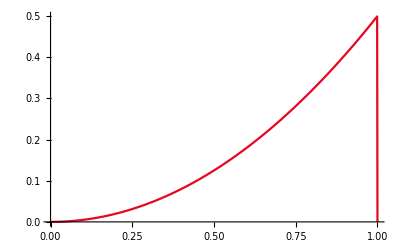

```mathematica
epsilon=1/10000000;
u[x_]:=(5000001 (1-ⅇ^(10000000 x)))/(10000000 (-1+ⅇ^10000000))+x/10000000+x^2/2;
(*真解函数*)
delta=N[1/1000,50];
tablereal=Table[{i delta,u[i delta]},{i,0,1000}];
img=ListLinePlot[tablereal,PlotStyle->ColorData[3,"ColorList"]]
```

```mathematica
maxerror=Table[0,{i,6},{j,2}];
```

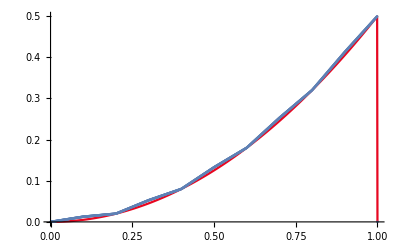
{-Graphics-,-Graphics-}

```mathematica
list={{0,0},{0.001,0.00012612},{0.002,0.000252239},{0.003,0.000378359},{0.004,0.000504478},{0.005,0.000630598},{0.006,0.000756717},{0.007,0.000882837},{0.008,0.00100896},{0.009,0.00113508},{0.01,0.0012612},{0.011,0.00138731},{0.012,0.00151343},{0.013,0.00163955},{0.014,0.00176567},{0.015,0.00189179},{0.016,0.00201791},{0.017,0.00214403},{0.018,0.00227015},{0.019,0.00239627},{0.02,0.00252239},{0.021,0.00264851},{0.022,0.00277463},{0.023,0.00290075},{0.024,0.00302687},{0.025,0.00315299},{0.026,0.00327911},{0.027,0.00340523},{0.028,0.00353135},{0.029,0.00365747},{0.03,0.00378359},{0.031,0.00390971},{0.032,0.00403583},{0.033,0.00416194},{0.034,0.00428806},{0.035,0.00441418},{0.036,0.0045403},{0.037,0.00466642},{0.038,0.00479254},{0.039,0.00491866},{0.04,0.00504478},{0.041,0.0051709},{0.042,0.00529702},{0.043,0.00542314},{0.044,0.00554926},{0.045,0.00567538},{0.046,0.0058015},{0.047,0.00592762},{0.048,0.00605374},{0.049,0.00617986},{0.05,0.00630598},{0.051,0.0064321},{0.052,0.00655822},{0.053,0.00668434},{0.054,0.00681045},{0.055,0.00693657},{0.056,0.00706269},{0.057,0.00718881},{0.058,0.00731493},{0.059,0.00744105},{0.06,0.00756717},{0.061,0.00769329},{0.062,0.00781941},{0.063,0.00794553},{0.064,0.00807165},{0.065,0.00819777},{0.066,0.00832389},{0.067,0.00845001},{0.068,0.00857613},{0.069,0.00870225},{0.07,0.00882837},{0.071,0.00895449},{0.072,0.00908061},{0.073,0.00920673},{0.074,0.00933285},{0.075,0.00945897},{0.076,0.00958508},{0.077,0.0097112},{0.078,0.00983732},{0.079,0.00996344},{0.08,0.0100896},{0.081,0.0102157},{0.082,0.0103418},{0.083,0.0104679},{0.084,0.010594},{0.085,0.0107202},{0.086,0.0108463},{0.087,0.0109724},{0.088,0.0110985},{0.089,0.0112246},{0.09,0.0113508},{0.091,0.0114769},{0.092,0.011603},{0.093,0.0117291},{0.094,0.0118552},{0.095,0.0119814},{0.096,0.0121075},{0.097,0.0122336},{0.098,0.0123597},{0.099,0.0124858},{0.1,0.012612},{0.101,0.0126858},{0.102,0.0127597},{0.103,0.0128336},{0.104,0.0129075},{0.105,0.0129814},{0.106,0.0130552},{0.107,0.0131291},{0.108,0.013203},{0.109,0.0132769},{0.11,0.0133508},{0.111,0.0134246},{0.112,0.0134985},{0.113,0.0135724},{0.114,0.0136463},{0.115,0.0137202},{0.116,0.013794},{0.117,0.0138679},{0.118,0.0139418},{0.119,0.0140157},{0.12,0.0140896},{0.121,0.0141634},{0.122,0.0142373},{0.123,0.0143112},{0.124,0.0143851},{0.125,0.014459},{0.126,0.0145328},{0.127,0.0146067},{0.128,0.0146806},{0.129,0.0147545},{0.13,0.0148284},{0.131,0.0149022},{0.132,0.0149761},{0.133,0.01505},{0.134,0.0151239},{0.135,0.0151978},{0.136,0.0152716},{0.137,0.0153455},{0.138,0.0154194},{0.139,0.0154933},{0.14,0.0155672},{0.141,0.015641},{0.142,0.0157149},{0.143,0.0157888},{0.144,0.0158627},{0.145,0.0159366},{0.146,0.0160104},{0.147,0.0160843},{0.148,0.0161582},{0.149,0.0162321},{0.15,0.016306},{0.151,0.0163798},{0.152,0.0164537},{0.153,0.0165276},{0.154,0.0166015},{0.155,0.0166754},{0.156,0.0167492},{0.157,0.0168231},{0.158,0.016897},{0.159,0.0169709},{0.16,0.0170448},{0.161,0.0171186},{0.162,0.0171925},{0.163,0.0172664},{0.164,0.0173403},{0.165,0.0174142},{0.166,0.017488},{0.167,0.0175619},{0.168,0.0176358},{0.169,0.0177097},{0.17,0.0177836},{0.171,0.0178575},{0.172,0.0179313},{0.173,0.0180052},{0.174,0.0180791},{0.175,0.018153},{0.176,0.0182269},{0.177,0.0183007},{0.178,0.0183746},{0.179,0.0184485},{0.18,0.0185224},{0.181,0.0185963},{0.182,0.0186701},{0.183,0.018744},{0.184,0.0188179},{0.185,0.0188918},{0.186,0.0189657},{0.187,0.0190395},{0.188,0.0191134},{0.189,0.0191873},{0.19,0.0192612},{0.191,0.0193351},{0.192,0.0194089},{0.193,0.0194828},{0.194,0.0195567},{0.195,0.0196306},{0.196,0.0197045},{0.197,0.0197783},{0.198,0.0198522},{0.199,0.0199261},{0.2,0.02},{0.201,0.0203261},{0.202,0.0206522},{0.203,0.0209784},{0.204,0.0213045},{0.205,0.0216306},{0.206,0.0219567},{0.207,0.0222828},{0.208,0.022609},{0.209,0.0229351},{0.21,0.0232612},{0.211,0.0235873},{0.212,0.0239134},{0.213,0.0242396},{0.214,0.0245657},{0.215,0.0248918},{0.216,0.0252179},{0.217,0.025544},{0.218,0.0258702},{0.219,0.0261963},{0.22,0.0265224},{0.221,0.0268485},{0.222,0.0271746},{0.223,0.0275008},{0.224,0.0278269},{0.225,0.028153},{0.226,0.0284791},{0.227,0.0288052},{0.228,0.0291314},{0.229,0.0294575},{0.23,0.0297836},{0.231,0.0301097},{0.232,0.0304358},{0.233,0.030762},{0.234,0.0310881},{0.235,0.0314142},{0.236,0.0317403},{0.237,0.0320664},{0.238,0.0323926},{0.239,0.0327187},{0.24,0.0330448},{0.241,0.0333709},{0.242,0.033697},{0.243,0.0340232},{0.244,0.0343493},{0.245,0.0346754},{0.246,0.0350015},{0.247,0.0353276},{0.248,0.0356538},{0.249,0.0359799},{0.25,0.036306},{0.251,0.0366321},{0.252,0.0369582},{0.253,0.0372844},{0.254,0.0376105},{0.255,0.0379366},{0.256,0.0382627},{0.257,0.0385888},{0.258,0.038915},{0.259,0.0392411},{0.26,0.0395672},{0.261,0.0398933},{0.262,0.0402194},{0.263,0.0405456},{0.264,0.0408717},{0.265,0.0411978},{0.266,0.0415239},{0.267,0.04185},{0.268,0.0421762},{0.269,0.0425023},{0.27,0.0428284},{0.271,0.0431545},{0.272,0.0434806},{0.273,0.0438068},{0.274,0.0441329},{0.275,0.044459},{0.276,0.0447851},{0.277,0.0451112},{0.278,0.0454374},{0.279,0.0457635},{0.28,0.0460896},{0.281,0.0464157},{0.282,0.0467418},{0.283,0.047068},{0.284,0.0473941},{0.285,0.0477202},{0.286,0.0480463},{0.287,0.0483724},{0.288,0.0486986},{0.289,0.0490247},{0.29,0.0493508},{0.291,0.0496769},{0.292,0.050003},{0.293,0.0503292},{0.294,0.0506553},{0.295,0.0509814},{0.296,0.0513075},{0.297,0.0516336},{0.298,0.0519598},{0.299,0.0522859},{0.3,0.052612},{0.301,0.0528859},{0.302,0.0531598},{0.303,0.0534336},{0.304,0.0537075},{0.305,0.0539814},{0.306,0.0542553},{0.307,0.0545292},{0.308,0.054803},{0.309,0.0550769},{0.31,0.0553508},{0.311,0.0556247},{0.312,0.0558986},{0.313,0.0561724},{0.314,0.0564463},{0.315,0.0567202},{0.316,0.0569941},{0.317,0.057268},{0.318,0.0575418},{0.319,0.0578157},{0.32,0.0580896},{0.321,0.0583635},{0.322,0.0586373},{0.323,0.0589112},{0.324,0.0591851},{0.325,0.059459},{0.326,0.0597329},{0.327,0.0600067},{0.328,0.0602806},{0.329,0.0605545},{0.33,0.0608284},{0.331,0.0611023},{0.332,0.0613761},{0.333,0.06165},{0.334,0.0619239},{0.335,0.0621978},{0.336,0.0624717},{0.337,0.0627455},{0.338,0.0630194},{0.339,0.0632933},{0.34,0.0635672},{0.341,0.0638411},{0.342,0.0641149},{0.343,0.0643888},{0.344,0.0646627},{0.345,0.0649366},{0.346,0.0652105},{0.347,0.0654843},{0.348,0.0657582},{0.349,0.0660321},{0.35,0.066306},{0.351,0.0665799},{0.352,0.0668537},{0.353,0.0671276},{0.354,0.0674015},{0.355,0.0676754},{0.356,0.0679493},{0.357,0.0682231},{0.358,0.068497},{0.359,0.0687709},{0.36,0.0690448},{0.361,0.0693187},{0.362,0.0695925},{0.363,0.0698664},{0.364,0.0701403},{0.365,0.0704142},{0.366,0.0706881},{0.367,0.0709619},{0.368,0.0712358},{0.369,0.0715097},{0.37,0.0717836},{0.371,0.0720574},{0.372,0.0723313},{0.373,0.0726052},{0.374,0.0728791},{0.375,0.073153},{0.376,0.0734268},{0.377,0.0737007},{0.378,0.0739746},{0.379,0.0742485},{0.38,0.0745224},{0.381,0.0747962},{0.382,0.0750701},{0.383,0.075344},{0.384,0.0756179},{0.385,0.0758918},{0.386,0.0761656},{0.387,0.0764395},{0.388,0.0767134},{0.389,0.0769873},{0.39,0.0772612},{0.391,0.077535},{0.392,0.0778089},{0.393,0.0780828},{0.394,0.0783567},{0.395,0.0786306},{0.396,0.0789044},{0.397,0.0791783},{0.398,0.0794522},{0.399,0.0797261},{0.4,0.08},{0.401,0.0805261},{0.402,0.0810522},{0.403,0.0815784},{0.404,0.0821045},{0.405,0.0826306},{0.406,0.0831567},{0.407,0.0836828},{0.408,0.084209},{0.409,0.0847351},{0.41,0.0852612},{0.411,0.0857873},{0.412,0.0863134},{0.413,0.0868396},{0.414,0.0873657},{0.415,0.0878918},{0.416,0.0884179},{0.417,0.0889441},{0.418,0.0894702},{0.419,0.0899963},{0.42,0.0905224},{0.421,0.0910485},{0.422,0.0915747},{0.423,0.0921008},{0.424,0.0926269},{0.425,0.093153},{0.426,0.0936791},{0.427,0.0942053},{0.428,0.0947314},{0.429,0.0952575},{0.43,0.0957836},{0.431,0.0963097},{0.432,0.0968359},{0.433,0.097362},{0.434,0.0978881},{0.435,0.0984142},{0.436,0.0989403},{0.437,0.0994665},{0.438,0.0999926},{0.439,0.100519},{0.44,0.101045},{0.441,0.101571},{0.442,0.102097},{0.443,0.102623},{0.444,0.103149},{0.445,0.103675},{0.446,0.104202},{0.447,0.104728},{0.448,0.105254},{0.449,0.10578},{0.45,0.106306},{0.451,0.106832},{0.452,0.107358},{0.453,0.107884},{0.454,0.108411},{0.455,0.108937},{0.456,0.109463},{0.457,0.109989},{0.458,0.110515},{0.459,0.111041},{0.46,0.111567},{0.461,0.112093},{0.462,0.112619},{0.463,0.113146},{0.464,0.113672},{0.465,0.114198},{0.466,0.114724},{0.467,0.11525},{0.468,0.115776},{0.469,0.116302},{0.47,0.116828},{0.471,0.117355},{0.472,0.117881},{0.473,0.118407},{0.474,0.118933},{0.475,0.119459},{0.476,0.119985},{0.477,0.120511},{0.478,0.121037},{0.479,0.121564},{0.48,0.12209},{0.481,0.122616},{0.482,0.123142},{0.483,0.123668},{0.484,0.124194},{0.485,0.12472},{0.486,0.125246},{0.487,0.125772},{0.488,0.126299},{0.489,0.126825},{0.49,0.127351},{0.491,0.127877},{0.492,0.128403},{0.493,0.128929},{0.494,0.129455},{0.495,0.129981},{0.496,0.130508},{0.497,0.131034},{0.498,0.13156},{0.499,0.132086},{0.5,0.132612},{0.501,0.133086},{0.502,0.13356},{0.503,0.134034},{0.504,0.134508},{0.505,0.134981},{0.506,0.135455},{0.507,0.135929},{0.508,0.136403},{0.509,0.136877},{0.51,0.137351},{0.511,0.137825},{0.512,0.138299},{0.513,0.138772},{0.514,0.139246},{0.515,0.13972},{0.516,0.140194},{0.517,0.140668},{0.518,0.141142},{0.519,0.141616},{0.52,0.14209},{0.521,0.142564},{0.522,0.143037},{0.523,0.143511},{0.524,0.143985},{0.525,0.144459},{0.526,0.144933},{0.527,0.145407},{0.528,0.145881},{0.529,0.146355},{0.53,0.146828},{0.531,0.147302},{0.532,0.147776},{0.533,0.14825},{0.534,0.148724},{0.535,0.149198},{0.536,0.149672},{0.537,0.150146},{0.538,0.150619},{0.539,0.151093},{0.54,0.151567},{0.541,0.152041},{0.542,0.152515},{0.543,0.152989},{0.544,0.153463},{0.545,0.153937},{0.546,0.15441},{0.547,0.154884},{0.548,0.155358},{0.549,0.155832},{0.55,0.156306},{0.551,0.15678},{0.552,0.157254},{0.553,0.157728},{0.554,0.158202},{0.555,0.158675},{0.556,0.159149},{0.557,0.159623},{0.558,0.160097},{0.559,0.160571},{0.56,0.161045},{0.561,0.161519},{0.562,0.161993},{0.563,0.162466},{0.564,0.16294},{0.565,0.163414},{0.566,0.163888},{0.567,0.164362},{0.568,0.164836},{0.569,0.16531},{0.57,0.165784},{0.571,0.166257},{0.572,0.166731},{0.573,0.167205},{0.574,0.167679},{0.575,0.168153},{0.576,0.168627},{0.577,0.169101},{0.578,0.169575},{0.579,0.170048},{0.58,0.170522},{0.581,0.170996},{0.582,0.17147},{0.583,0.171944},{0.584,0.172418},{0.585,0.172892},{0.586,0.173366},{0.587,0.17384},{0.588,0.174313},{0.589,0.174787},{0.59,0.175261},{0.591,0.175735},{0.592,0.176209},{0.593,0.176683},{0.594,0.177157},{0.595,0.177631},{0.596,0.178104},{0.597,0.178578},{0.598,0.179052},{0.599,0.179526},{0.6,0.18},{0.601,0.180726},{0.602,0.181452},{0.603,0.182178},{0.604,0.182904},{0.605,0.183631},{0.606,0.184357},{0.607,0.185083},{0.608,0.185809},{0.609,0.186535},{0.61,0.187261},{0.611,0.187987},{0.612,0.188713},{0.613,0.18944},{0.614,0.190166},{0.615,0.190892},{0.616,0.191618},{0.617,0.192344},{0.618,0.19307},{0.619,0.193796},{0.62,0.194522},{0.621,0.195249},{0.622,0.195975},{0.623,0.196701},{0.624,0.197427},{0.625,0.198153},{0.626,0.198879},{0.627,0.199605},{0.628,0.200331},{0.629,0.201058},{0.63,0.201784},{0.631,0.20251},{0.632,0.203236},{0.633,0.203962},{0.634,0.204688},{0.635,0.205414},{0.636,0.20614},{0.637,0.206866},{0.638,0.207593},{0.639,0.208319},{0.64,0.209045},{0.641,0.209771},{0.642,0.210497},{0.643,0.211223},{0.644,0.211949},{0.645,0.212675},{0.646,0.213402},{0.647,0.214128},{0.648,0.214854},{0.649,0.21558},{0.65,0.216306},{0.651,0.217032},{0.652,0.217758},{0.653,0.218484},{0.654,0.219211},{0.655,0.219937},{0.656,0.220663},{0.657,0.221389},{0.658,0.222115},{0.659,0.222841},{0.66,0.223567},{0.661,0.224293},{0.662,0.22502},{0.663,0.225746},{0.664,0.226472},{0.665,0.227198},{0.666,0.227924},{0.667,0.22865},{0.668,0.229376},{0.669,0.230102},{0.67,0.230828},{0.671,0.231555},{0.672,0.232281},{0.673,0.233007},{0.674,0.233733},{0.675,0.234459},{0.676,0.235185},{0.677,0.235911},{0.678,0.236637},{0.679,0.237364},{0.68,0.23809},{0.681,0.238816},{0.682,0.239542},{0.683,0.240268},{0.684,0.240994},{0.685,0.24172},{0.686,0.242446},{0.687,0.243173},{0.688,0.243899},{0.689,0.244625},{0.69,0.245351},{0.691,0.246077},{0.692,0.246803},{0.693,0.247529},{0.694,0.248255},{0.695,0.248982},{0.696,0.249708},{0.697,0.250434},{0.698,0.25116},{0.699,0.251886},{0.7,0.252612},{0.701,0.253286},{0.702,0.25396},{0.703,0.254634},{0.704,0.255308},{0.705,0.255981},{0.706,0.256655},{0.707,0.257329},{0.708,0.258003},{0.709,0.258677},{0.71,0.259351},{0.711,0.260025},{0.712,0.260699},{0.713,0.261373},{0.714,0.262046},{0.715,0.26272},{0.716,0.263394},{0.717,0.264068},{0.718,0.264742},{0.719,0.265416},{0.72,0.26609},{0.721,0.266764},{0.722,0.267437},{0.723,0.268111},{0.724,0.268785},{0.725,0.269459},{0.726,0.270133},{0.727,0.270807},{0.728,0.271481},{0.729,0.272155},{0.73,0.272828},{0.731,0.273502},{0.732,0.274176},{0.733,0.27485},{0.734,0.275524},{0.735,0.276198},{0.736,0.276872},{0.737,0.277546},{0.738,0.278219},{0.739,0.278893},{0.74,0.279567},{0.741,0.280241},{0.742,0.280915},{0.743,0.281589},{0.744,0.282263},{0.745,0.282937},{0.746,0.28361},{0.747,0.284284},{0.748,0.284958},{0.749,0.285632},{0.75,0.286306},{0.751,0.28698},{0.752,0.287654},{0.753,0.288328},{0.754,0.289002},{0.755,0.289675},{0.756,0.290349},{0.757,0.291023},{0.758,0.291697},{0.759,0.292371},{0.76,0.293045},{0.761,0.293719},{0.762,0.294393},{0.763,0.295066},{0.764,0.29574},{0.765,0.296414},{0.766,0.297088},{0.767,0.297762},{0.768,0.298436},{0.769,0.29911},{0.77,0.299784},{0.771,0.300457},{0.772,0.301131},{0.773,0.301805},{0.774,0.302479},{0.775,0.303153},{0.776,0.303827},{0.777,0.304501},{0.778,0.305175},{0.779,0.305848},{0.78,0.306522},{0.781,0.307196},{0.782,0.30787},{0.783,0.308544},{0.784,0.309218},{0.785,0.309892},{0.786,0.310566},{0.787,0.311239},{0.788,0.311913},{0.789,0.312587},{0.79,0.313261},{0.791,0.313935},{0.792,0.314609},{0.793,0.315283},{0.794,0.315957},{0.795,0.316631},{0.796,0.317304},{0.797,0.317978},{0.798,0.318652},{0.799,0.319326},{0.8,0.32},{0.801,0.320926},{0.802,0.321852},{0.803,0.322778},{0.804,0.323704},{0.805,0.324631},{0.806,0.325557},{0.807,0.326483},{0.808,0.327409},{0.809,0.328335},{0.81,0.329261},{0.811,0.330187},{0.812,0.331113},{0.813,0.33204},{0.814,0.332966},{0.815,0.333892},{0.816,0.334818},{0.817,0.335744},{0.818,0.33667},{0.819,0.337596},{0.82,0.338522},{0.821,0.339449},{0.822,0.340375},{0.823,0.341301},{0.824,0.342227},{0.825,0.343153},{0.826,0.344079},{0.827,0.345005},{0.828,0.345931},{0.829,0.346858},{0.83,0.347784},{0.831,0.34871},{0.832,0.349636},{0.833,0.350562},{0.834,0.351488},{0.835,0.352414},{0.836,0.35334},{0.837,0.354267},{0.838,0.355193},{0.839,0.356119},{0.84,0.357045},{0.841,0.357971},{0.842,0.358897},{0.843,0.359823},{0.844,0.360749},{0.845,0.361675},{0.846,0.362602},{0.847,0.363528},{0.848,0.364454},{0.849,0.36538},{0.85,0.366306},{0.851,0.367232},{0.852,0.368158},{0.853,0.369084},{0.854,0.370011},{0.855,0.370937},{0.856,0.371863},{0.857,0.372789},{0.858,0.373715},{0.859,0.374641},{0.86,0.375567},{0.861,0.376493},{0.862,0.37742},{0.863,0.378346},{0.864,0.379272},{0.865,0.380198},{0.866,0.381124},{0.867,0.38205},{0.868,0.382976},{0.869,0.383902},{0.87,0.384829},{0.871,0.385755},{0.872,0.386681},{0.873,0.387607},{0.874,0.388533},{0.875,0.389459},{0.876,0.390385},{0.877,0.391311},{0.878,0.392237},{0.879,0.393164},{0.88,0.39409},{0.881,0.395016},{0.882,0.395942},{0.883,0.396868},{0.884,0.397794},{0.885,0.39872},{0.886,0.399646},{0.887,0.400573},{0.888,0.401499},{0.889,0.402425},{0.89,0.403351},{0.891,0.404277},{0.892,0.405203},{0.893,0.406129},{0.894,0.407055},{0.895,0.407982},{0.896,0.408908},{0.897,0.409834},{0.898,0.41076},{0.899,0.411686},{0.9,0.412612},{0.901,0.413486},{0.902,0.41436},{0.903,0.415234},{0.904,0.416108},{0.905,0.416982},{0.906,0.417855},{0.907,0.418729},{0.908,0.419603},{0.909,0.420477},{0.91,0.421351},{0.911,0.422225},{0.912,0.423099},{0.913,0.423973},{0.914,0.424846},{0.915,0.42572},{0.916,0.426594},{0.917,0.427468},{0.918,0.428342},{0.919,0.429216},{0.92,0.43009},{0.921,0.430964},{0.922,0.431837},{0.923,0.432711},{0.924,0.433585},{0.925,0.434459},{0.926,0.435333},{0.927,0.436207},{0.928,0.437081},{0.929,0.437955},{0.93,0.438828},{0.931,0.439702},{0.932,0.440576},{0.933,0.44145},{0.934,0.442324},{0.935,0.443198},{0.936,0.444072},{0.937,0.444946},{0.938,0.445819},{0.939,0.446693},{0.94,0.447567},{0.941,0.448441},{0.942,0.449315},{0.943,0.450189},{0.944,0.451063},{0.945,0.451937},{0.946,0.452811},{0.947,0.453684},{0.948,0.454558},{0.949,0.455432},{0.95,0.456306},{0.951,0.45718},{0.952,0.458054},{0.953,0.458928},{0.954,0.459802},{0.955,0.460675},{0.956,0.461549},{0.957,0.462423},{0.958,0.463297},{0.959,0.464171},{0.96,0.465045},{0.961,0.465919},{0.962,0.466793},{0.963,0.467666},{0.964,0.46854},{0.965,0.469414},{0.966,0.470288},{0.967,0.471162},{0.968,0.472036},{0.969,0.47291},{0.97,0.473784},{0.971,0.474657},{0.972,0.475531},{0.973,0.476405},{0.974,0.477279},{0.975,0.478153},{0.976,0.479027},{0.977,0.479901},{0.978,0.480775},{0.979,0.481648},{0.98,0.482522},{0.981,0.483396},{0.982,0.48427},{0.983,0.485144},{0.984,0.486018},{0.985,0.486892},{0.986,0.487766},{0.987,0.488639},{0.988,0.489513},{0.989,0.490387},{0.99,0.491261},{0.991,0.492135},{0.992,0.493009},{0.993,0.493883},{0.994,0.494757},{0.995,0.495631},{0.996,0.496504},{0.997,0.497378},{0.998,0.498252},{0.999,0.499126},{1,0}};
imgtemp=ListPlot[list];
maxerror[[1,1]]=Max[tablereal[[All,2]]-list[[All,2]]];
{img,Show[img,imgtemp]}
```

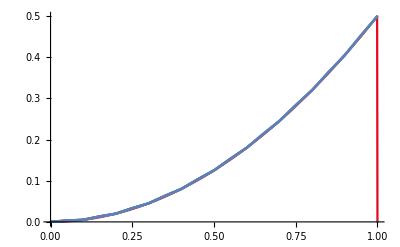
{-Graphics-,-Graphics-}

```mathematica
list={{0,0},{0.001,6.45548 10^(-5)},{0.002,0.00012911},{0.003,0.000193664},{0.004,0.000258219},{0.005,0.000322774},{0.006,0.000387329},{0.007,0.000451883},{0.008,0.000516438},{0.009,0.000580993},{0.01,0.000645548},{0.011,0.000710102},{0.012,0.000774657},{0.013,0.000839212},{0.014,0.000903767},{0.015,0.000968322},{0.016,0.00103288},{0.017,0.00109743},{0.018,0.00116199},{0.019,0.00122654},{0.02,0.0012911},{0.021,0.00135565},{0.022,0.0014202},{0.023,0.00148476},{0.024,0.00154931},{0.025,0.00161387},{0.026,0.00167842},{0.027,0.00174298},{0.028,0.00180753},{0.029,0.00187209},{0.03,0.00193664},{0.031,0.0020012},{0.032,0.00206575},{0.033,0.00213031},{0.034,0.00219486},{0.035,0.00225942},{0.036,0.00232397},{0.037,0.00238853},{0.038,0.00245308},{0.039,0.00251764},{0.04,0.00258219},{0.041,0.00264675},{0.042,0.0027113},{0.043,0.00277586},{0.044,0.00284041},{0.045,0.00290496},{0.046,0.00296952},{0.047,0.00303407},{0.048,0.00309863},{0.049,0.00316318},{0.05,0.00322774},{0.051,0.00326318},{0.052,0.00329863},{0.053,0.00333407},{0.054,0.00336952},{0.055,0.00340496},{0.056,0.00344041},{0.057,0.00347585},{0.058,0.0035113},{0.059,0.00354674},{0.06,0.00358219},{0.061,0.00361763},{0.062,0.00365308},{0.063,0.00368852},{0.064,0.00372397},{0.065,0.00375941},{0.066,0.00379486},{0.067,0.0038303},{0.068,0.00386575},{0.069,0.00390119},{0.07,0.00393664},{0.071,0.00397208},{0.072,0.00400753},{0.073,0.00404297},{0.074,0.00407842},{0.075,0.00411386},{0.076,0.00414931},{0.077,0.00418475},{0.078,0.0042202},{0.079,0.00425564},{0.08,0.00429109},{0.081,0.00432653},{0.082,0.00436198},{0.083,0.00439742},{0.084,0.00443287},{0.085,0.00446831},{0.086,0.00450376},{0.087,0.0045392},{0.088,0.00457465},{0.089,0.00461009},{0.09,0.00464554},{0.091,0.00468098},{0.092,0.00471643},{0.093,0.00475187},{0.094,0.00478732},{0.095,0.00482277},{0.096,0.00485821},{0.097,0.00489366},{0.098,0.0049291},{0.099,0.00496455},{0.1,0.005},{0.101,0.00516455},{0.102,0.00532911},{0.103,0.00549366},{0.104,0.00565822},{0.105,0.00582277},{0.106,0.00598733},{0.107,0.00615189},{0.108,0.00631644},{0.109,0.006481},{0.11,0.00664555},{0.111,0.00681011},{0.112,0.00697466},{0.113,0.00713922},{0.114,0.00730377},{0.115,0.00746833},{0.116,0.00763288},{0.117,0.00779744},{0.118,0.00796199},{0.119,0.00812655},{0.12,0.0082911},{0.121,0.00845566},{0.122,0.00862022},{0.123,0.00878477},{0.124,0.00894933},{0.125,0.00911388},{0.126,0.00927844},{0.127,0.00944299},{0.128,0.00960755},{0.129,0.0097721},{0.13,0.00993666},{0.131,0.0101012},{0.132,0.0102658},{0.133,0.0104303},{0.134,0.0105949},{0.135,0.0107594},{0.136,0.010924},{0.137,0.0110885},{0.138,0.0112531},{0.139,0.0114177},{0.14,0.0115822},{0.141,0.0117468},{0.142,0.0119113},{0.143,0.0120759},{0.144,0.0122404},{0.145,0.012405},{0.146,0.0125695},{0.147,0.0127341},{0.148,0.0128987},{0.149,0.0130632},{0.15,0.0132278},{0.151,0.0133632},{0.152,0.0134987},{0.153,0.0136341},{0.154,0.0137695},{0.155,0.013905},{0.156,0.0140404},{0.157,0.0141759},{0.158,0.0143113},{0.159,0.0144468},{0.16,0.0145822},{0.161,0.0147177},{0.162,0.0148531},{0.163,0.0149885},{0.164,0.015124},{0.165,0.0152594},{0.166,0.0153949},{0.167,0.0155303},{0.168,0.0156658},{0.169,0.0158012},{0.17,0.0159366},{0.171,0.0160721},{0.172,0.0162075},{0.173,0.016343},{0.174,0.0164784},{0.175,0.0166139},{0.176,0.0167493},{0.177,0.0168848},{0.178,0.0170202},{0.179,0.0171556},{0.18,0.0172911},{0.181,0.0174265},{0.182,0.017562},{0.183,0.0176974},{0.184,0.0178329},{0.185,0.0179683},{0.186,0.0181038},{0.187,0.0182392},{0.188,0.0183746},{0.189,0.0185101},{0.19,0.0186455},{0.191,0.018781},{0.192,0.0189164},{0.193,0.0190519},{0.194,0.0191873},{0.195,0.0193228},{0.196,0.0194582},{0.197,0.0195936},{0.198,0.0197291},{0.199,0.0198645},{0.2,0.02},{0.201,0.0202646},{0.202,0.0205291},{0.203,0.0207937},{0.204,0.0210582},{0.205,0.0213228},{0.206,0.0215873},{0.207,0.0218519},{0.208,0.0221164},{0.209,0.022381},{0.21,0.0226456},{0.211,0.0229101},{0.212,0.0231747},{0.213,0.0234392},{0.214,0.0237038},{0.215,0.0239683},{0.216,0.0242329},{0.217,0.0244974},{0.218,0.024762},{0.219,0.0250266},{0.22,0.0252911},{0.221,0.0255557},{0.222,0.0258202},{0.223,0.0260848},{0.224,0.0263493},{0.225,0.0266139},{0.226,0.0268784},{0.227,0.027143},{0.228,0.0274076},{0.229,0.0276721},{0.23,0.0279367},{0.231,0.0282012},{0.232,0.0284658},{0.233,0.0287303},{0.234,0.0289949},{0.235,0.0292595},{0.236,0.029524},{0.237,0.0297886},{0.238,0.0300531},{0.239,0.0303177},{0.24,0.0305822},{0.241,0.0308468},{0.242,0.0311113},{0.243,0.0313759},{0.244,0.0316405},{0.245,0.031905},{0.246,0.0321696},{0.247,0.0324341},{0.248,0.0326987},{0.249,0.0329632},{0.25,0.0332278},{0.251,0.0334632},{0.252,0.0336987},{0.253,0.0339341},{0.254,0.0341696},{0.255,0.034405},{0.256,0.0346404},{0.257,0.0348759},{0.258,0.0351113},{0.259,0.0353468},{0.26,0.0355822},{0.261,0.0358177},{0.262,0.0360531},{0.263,0.0362886},{0.264,0.036524},{0.265,0.0367594},{0.266,0.0369949},{0.267,0.0372303},{0.268,0.0374658},{0.269,0.0377012},{0.27,0.0379367},{0.271,0.0381721},{0.272,0.0384075},{0.273,0.038643},{0.274,0.0388784},{0.275,0.0391139},{0.276,0.0393493},{0.277,0.0395848},{0.278,0.0398202},{0.279,0.0400557},{0.28,0.0402911},{0.281,0.0405265},{0.282,0.040762},{0.283,0.0409974},{0.284,0.0412329},{0.285,0.0414683},{0.286,0.0417038},{0.287,0.0419392},{0.288,0.0421746},{0.289,0.0424101},{0.29,0.0426455},{0.291,0.042881},{0.292,0.0431164},{0.293,0.0433519},{0.294,0.0435873},{0.295,0.0438228},{0.296,0.0440582},{0.297,0.0442936},{0.298,0.0445291},{0.299,0.0447645},{0.3,0.045},{0.301,0.0453646},{0.302,0.0457291},{0.303,0.0460937},{0.304,0.0464582},{0.305,0.0468228},{0.306,0.0471873},{0.307,0.0475519},{0.308,0.0479164},{0.309,0.048281},{0.31,0.0486456},{0.311,0.0490101},{0.312,0.0493747},{0.313,0.0497392},{0.314,0.0501038},{0.315,0.0504683},{0.316,0.0508329},{0.317,0.0511975},{0.318,0.051562},{0.319,0.0519266},{0.32,0.0522911},{0.321,0.0526557},{0.322,0.0530202},{0.323,0.0533848},{0.324,0.0537493},{0.325,0.0541139},{0.326,0.0544785},{0.327,0.054843},{0.328,0.0552076},{0.329,0.0555721},{0.33,0.0559367},{0.331,0.0563012},{0.332,0.0566658},{0.333,0.0570304},{0.334,0.0573949},{0.335,0.0577595},{0.336,0.058124},{0.337,0.0584886},{0.338,0.0588531},{0.339,0.0592177},{0.34,0.0595823},{0.341,0.0599468},{0.342,0.0603114},{0.343,0.0606759},{0.344,0.0610405},{0.345,0.061405},{0.346,0.0617696},{0.347,0.0621341},{0.348,0.0624987},{0.349,0.0628633},{0.35,0.0632278},{0.351,0.0635633},{0.352,0.0638987},{0.353,0.0642341},{0.354,0.0645696},{0.355,0.064905},{0.356,0.0652405},{0.357,0.0655759},{0.358,0.0659114},{0.359,0.0662468},{0.36,0.0665822},{0.361,0.0669177},{0.362,0.0672531},{0.363,0.0675886},{0.364,0.067924},{0.365,0.0682595},{0.366,0.0685949},{0.367,0.0689303},{0.368,0.0692658},{0.369,0.0696012},{0.37,0.0699367},{0.371,0.0702721},{0.372,0.0706076},{0.373,0.070943},{0.374,0.0712784},{0.375,0.0716139},{0.376,0.0719493},{0.377,0.0722848},{0.378,0.0726202},{0.379,0.0729557},{0.38,0.0732911},{0.381,0.0736265},{0.382,0.073962},{0.383,0.0742974},{0.384,0.0746329},{0.385,0.0749683},{0.386,0.0753038},{0.387,0.0756392},{0.388,0.0759746},{0.389,0.0763101},{0.39,0.0766455},{0.391,0.076981},{0.392,0.0773164},{0.393,0.0776519},{0.394,0.0779873},{0.395,0.0783227},{0.396,0.0786582},{0.397,0.0789936},{0.398,0.0793291},{0.399,0.0796645},{0.4,0.08},{0.401,0.0804645},{0.402,0.0809291},{0.403,0.0813937},{0.404,0.0818582},{0.405,0.0823228},{0.406,0.0827873},{0.407,0.0832519},{0.408,0.0837164},{0.409,0.084181},{0.41,0.0846456},{0.411,0.0851101},{0.412,0.0855747},{0.413,0.0860392},{0.414,0.0865038},{0.415,0.0869683},{0.416,0.0874329},{0.417,0.0878975},{0.418,0.088362},{0.419,0.0888266},{0.42,0.0892911},{0.421,0.0897557},{0.422,0.0902202},{0.423,0.0906848},{0.424,0.0911494},{0.425,0.0916139},{0.426,0.0920785},{0.427,0.092543},{0.428,0.0930076},{0.429,0.0934721},{0.43,0.0939367},{0.431,0.0944013},{0.432,0.0948658},{0.433,0.0953304},{0.434,0.0957949},{0.435,0.0962595},{0.436,0.096724},{0.437,0.0971886},{0.438,0.0976532},{0.439,0.0981177},{0.44,0.0985823},{0.441,0.0990468},{0.442,0.0995114},{0.443,0.0999759},{0.444,0.100441},{0.445,0.100905},{0.446,0.10137},{0.447,0.101834},{0.448,0.102299},{0.449,0.102763},{0.45,0.103228},{0.451,0.103663},{0.452,0.104099},{0.453,0.104534},{0.454,0.10497},{0.455,0.105405},{0.456,0.10584},{0.457,0.106276},{0.458,0.106711},{0.459,0.107147},{0.46,0.107582},{0.461,0.108018},{0.462,0.108453},{0.463,0.108889},{0.464,0.109324},{0.465,0.109759},{0.466,0.110195},{0.467,0.11063},{0.468,0.111066},{0.469,0.111501},{0.47,0.111937},{0.471,0.112372},{0.472,0.112808},{0.473,0.113243},{0.474,0.113678},{0.475,0.114114},{0.476,0.114549},{0.477,0.114985},{0.478,0.11542},{0.479,0.115856},{0.48,0.116291},{0.481,0.116727},{0.482,0.117162},{0.483,0.117597},{0.484,0.118033},{0.485,0.118468},{0.486,0.118904},{0.487,0.119339},{0.488,0.119775},{0.489,0.12021},{0.49,0.120646},{0.491,0.121081},{0.492,0.121516},{0.493,0.121952},{0.494,0.122387},{0.495,0.122823},{0.496,0.123258},{0.497,0.123694},{0.498,0.124129},{0.499,0.124565},{0.5,0.125},{0.501,0.125565},{0.502,0.126129},{0.503,0.126694},{0.504,0.127258},{0.505,0.127823},{0.506,0.128387},{0.507,0.128952},{0.508,0.129516},{0.509,0.130081},{0.51,0.130646},{0.511,0.13121},{0.512,0.131775},{0.513,0.132339},{0.514,0.132904},{0.515,0.133468},{0.516,0.134033},{0.517,0.134597},{0.518,0.135162},{0.519,0.135727},{0.52,0.136291},{0.521,0.136856},{0.522,0.13742},{0.523,0.137985},{0.524,0.138549},{0.525,0.139114},{0.526,0.139678},{0.527,0.140243},{0.528,0.140808},{0.529,0.141372},{0.53,0.141937},{0.531,0.142501},{0.532,0.143066},{0.533,0.14363},{0.534,0.144195},{0.535,0.14476},{0.536,0.145324},{0.537,0.145889},{0.538,0.146453},{0.539,0.147018},{0.54,0.147582},{0.541,0.148147},{0.542,0.148711},{0.543,0.149276},{0.544,0.149841},{0.545,0.150405},{0.546,0.15097},{0.547,0.151534},{0.548,0.152099},{0.549,0.152663},{0.55,0.153228},{0.551,0.153763},{0.552,0.154299},{0.553,0.154834},{0.554,0.15537},{0.555,0.155905},{0.556,0.156441},{0.557,0.156976},{0.558,0.157511},{0.559,0.158047},{0.56,0.158582},{0.561,0.159118},{0.562,0.159653},{0.563,0.160189},{0.564,0.160724},{0.565,0.161259},{0.566,0.161795},{0.567,0.16233},{0.568,0.162866},{0.569,0.163401},{0.57,0.163937},{0.571,0.164472},{0.572,0.165008},{0.573,0.165543},{0.574,0.166078},{0.575,0.166614},{0.576,0.167149},{0.577,0.167685},{0.578,0.16822},{0.579,0.168756},{0.58,0.169291},{0.581,0.169827},{0.582,0.170362},{0.583,0.170897},{0.584,0.171433},{0.585,0.171968},{0.586,0.172504},{0.587,0.173039},{0.588,0.173575},{0.589,0.17411},{0.59,0.174646},{0.591,0.175181},{0.592,0.175716},{0.593,0.176252},{0.594,0.176787},{0.595,0.177323},{0.596,0.177858},{0.597,0.178394},{0.598,0.178929},{0.599,0.179465},{0.6,0.18},{0.601,0.180665},{0.602,0.181329},{0.603,0.181994},{0.604,0.182658},{0.605,0.183323},{0.606,0.183987},{0.607,0.184652},{0.608,0.185316},{0.609,0.185981},{0.61,0.186646},{0.611,0.18731},{0.612,0.187975},{0.613,0.188639},{0.614,0.189304},{0.615,0.189968},{0.616,0.190633},{0.617,0.191297},{0.618,0.191962},{0.619,0.192627},{0.62,0.193291},{0.621,0.193956},{0.622,0.19462},{0.623,0.195285},{0.624,0.195949},{0.625,0.196614},{0.626,0.197279},{0.627,0.197943},{0.628,0.198608},{0.629,0.199272},{0.63,0.199937},{0.631,0.200601},{0.632,0.201266},{0.633,0.20193},{0.634,0.202595},{0.635,0.20326},{0.636,0.203924},{0.637,0.204589},{0.638,0.205253},{0.639,0.205918},{0.64,0.206582},{0.641,0.207247},{0.642,0.207911},{0.643,0.208576},{0.644,0.209241},{0.645,0.209905},{0.646,0.21057},{0.647,0.211234},{0.648,0.211899},{0.649,0.212563},{0.65,0.213228},{0.651,0.213863},{0.652,0.214499},{0.653,0.215134},{0.654,0.21577},{0.655,0.216405},{0.656,0.217041},{0.657,0.217676},{0.658,0.218311},{0.659,0.218947},{0.66,0.219582},{0.661,0.220218},{0.662,0.220853},{0.663,0.221489},{0.664,0.222124},{0.665,0.22276},{0.666,0.223395},{0.667,0.22403},{0.668,0.224666},{0.669,0.225301},{0.67,0.225937},{0.671,0.226572},{0.672,0.227208},{0.673,0.227843},{0.674,0.228478},{0.675,0.229114},{0.676,0.229749},{0.677,0.230385},{0.678,0.23102},{0.679,0.231656},{0.68,0.232291},{0.681,0.232927},{0.682,0.233562},{0.683,0.234197},{0.684,0.234833},{0.685,0.235468},{0.686,0.236104},{0.687,0.236739},{0.688,0.237375},{0.689,0.23801},{0.69,0.238646},{0.691,0.239281},{0.692,0.239916},{0.693,0.240552},{0.694,0.241187},{0.695,0.241823},{0.696,0.242458},{0.697,0.243094},{0.698,0.243729},{0.699,0.244364},{0.7,0.245},{0.701,0.245765},{0.702,0.246529},{0.703,0.247294},{0.704,0.248058},{0.705,0.248823},{0.706,0.249587},{0.707,0.250352},{0.708,0.251116},{0.709,0.251881},{0.71,0.252646},{0.711,0.25341},{0.712,0.254175},{0.713,0.254939},{0.714,0.255704},{0.715,0.256468},{0.716,0.257233},{0.717,0.257997},{0.718,0.258762},{0.719,0.259527},{0.72,0.260291},{0.721,0.261056},{0.722,0.26182},{0.723,0.262585},{0.724,0.263349},{0.725,0.264114},{0.726,0.264879},{0.727,0.265643},{0.728,0.266408},{0.729,0.267172},{0.73,0.267937},{0.731,0.268701},{0.732,0.269466},{0.733,0.27023},{0.734,0.270995},{0.735,0.27176},{0.736,0.272524},{0.737,0.273289},{0.738,0.274053},{0.739,0.274818},{0.74,0.275582},{0.741,0.276347},{0.742,0.277111},{0.743,0.277876},{0.744,0.278641},{0.745,0.279405},{0.746,0.28017},{0.747,0.280934},{0.748,0.281699},{0.749,0.282463},{0.75,0.283228},{0.751,0.283963},{0.752,0.284699},{0.753,0.285434},{0.754,0.28617},{0.755,0.286905},{0.756,0.287641},{0.757,0.288376},{0.758,0.289111},{0.759,0.289847},{0.76,0.290582},{0.761,0.291318},{0.762,0.292053},{0.763,0.292789},{0.764,0.293524},{0.765,0.29426},{0.766,0.294995},{0.767,0.29573},{0.768,0.296466},{0.769,0.297201},{0.77,0.297937},{0.771,0.298672},{0.772,0.299408},{0.773,0.300143},{0.774,0.300878},{0.775,0.301614},{0.776,0.302349},{0.777,0.303085},{0.778,0.30382},{0.779,0.304556},{0.78,0.305291},{0.781,0.306027},{0.782,0.306762},{0.783,0.307497},{0.784,0.308233},{0.785,0.308968},{0.786,0.309704},{0.787,0.310439},{0.788,0.311175},{0.789,0.31191},{0.79,0.312646},{0.791,0.313381},{0.792,0.314116},{0.793,0.314852},{0.794,0.315587},{0.795,0.316323},{0.796,0.317058},{0.797,0.317794},{0.798,0.318529},{0.799,0.319264},{0.8,0.32},{0.801,0.320865},{0.802,0.321729},{0.803,0.322594},{0.804,0.323458},{0.805,0.324323},{0.806,0.325187},{0.807,0.326052},{0.808,0.326916},{0.809,0.327781},{0.81,0.328646},{0.811,0.32951},{0.812,0.330375},{0.813,0.331239},{0.814,0.332104},{0.815,0.332968},{0.816,0.333833},{0.817,0.334697},{0.818,0.335562},{0.819,0.336427},{0.82,0.337291},{0.821,0.338156},{0.822,0.33902},{0.823,0.339885},{0.824,0.340749},{0.825,0.341614},{0.826,0.342479},{0.827,0.343343},{0.828,0.344208},{0.829,0.345072},{0.83,0.345937},{0.831,0.346801},{0.832,0.347666},{0.833,0.34853},{0.834,0.349395},{0.835,0.35026},{0.836,0.351124},{0.837,0.351989},{0.838,0.352853},{0.839,0.353718},{0.84,0.354582},{0.841,0.355447},{0.842,0.356311},{0.843,0.357176},{0.844,0.358041},{0.845,0.358905},{0.846,0.35977},{0.847,0.360634},{0.848,0.361499},{0.849,0.362363},{0.85,0.363228},{0.851,0.364063},{0.852,0.364899},{0.853,0.365734},{0.854,0.36657},{0.855,0.367405},{0.856,0.368241},{0.857,0.369076},{0.858,0.369911},{0.859,0.370747},{0.86,0.371582},{0.861,0.372418},{0.862,0.373253},{0.863,0.374089},{0.864,0.374924},{0.865,0.37576},{0.866,0.376595},{0.867,0.37743},{0.868,0.378266},{0.869,0.379101},{0.87,0.379937},{0.871,0.380772},{0.872,0.381608},{0.873,0.382443},{0.874,0.383278},{0.875,0.384114},{0.876,0.384949},{0.877,0.385785},{0.878,0.38662},{0.879,0.387456},{0.88,0.388291},{0.881,0.389127},{0.882,0.389962},{0.883,0.390797},{0.884,0.391633},{0.885,0.392468},{0.886,0.393304},{0.887,0.394139},{0.888,0.394975},{0.889,0.39581},{0.89,0.396646},{0.891,0.397481},{0.892,0.398316},{0.893,0.399152},{0.894,0.399987},{0.895,0.400823},{0.896,0.401658},{0.897,0.402494},{0.898,0.403329},{0.899,0.404164},{0.9,0.405},{0.901,0.405965},{0.902,0.406929},{0.903,0.407894},{0.904,0.408858},{0.905,0.409823},{0.906,0.410787},{0.907,0.411752},{0.908,0.412716},{0.909,0.413681},{0.91,0.414646},{0.911,0.41561},{0.912,0.416575},{0.913,0.417539},{0.914,0.418504},{0.915,0.419468},{0.916,0.420433},{0.917,0.421398},{0.918,0.422362},{0.919,0.423327},{0.92,0.424291},{0.921,0.425256},{0.922,0.42622},{0.923,0.427185},{0.924,0.428149},{0.925,0.429114},{0.926,0.430079},{0.927,0.431043},{0.928,0.432008},{0.929,0.432972},{0.93,0.433937},{0.931,0.434901},{0.932,0.435866},{0.933,0.43683},{0.934,0.437795},{0.935,0.43876},{0.936,0.439724},{0.937,0.440689},{0.938,0.441653},{0.939,0.442618},{0.94,0.443582},{0.941,0.444547},{0.942,0.445511},{0.943,0.446476},{0.944,0.447441},{0.945,0.448405},{0.946,0.44937},{0.947,0.450334},{0.948,0.451299},{0.949,0.452263},{0.95,0.453228},{0.951,0.454163},{0.952,0.455099},{0.953,0.456034},{0.954,0.45697},{0.955,0.457905},{0.956,0.458841},{0.957,0.459776},{0.958,0.460711},{0.959,0.461647},{0.96,0.462582},{0.961,0.463518},{0.962,0.464453},{0.963,0.465389},{0.964,0.466324},{0.965,0.46726},{0.966,0.468195},{0.967,0.46913},{0.968,0.470066},{0.969,0.471001},{0.97,0.471937},{0.971,0.472872},{0.972,0.473808},{0.973,0.474743},{0.974,0.475678},{0.975,0.476614},{0.976,0.477549},{0.977,0.478485},{0.978,0.47942},{0.979,0.480356},{0.98,0.481291},{0.981,0.482227},{0.982,0.483162},{0.983,0.484097},{0.984,0.485033},{0.985,0.485968},{0.986,0.486904},{0.987,0.487839},{0.988,0.488775},{0.989,0.48971},{0.99,0.490646},{0.991,0.491581},{0.992,0.492516},{0.993,0.493452},{0.994,0.494387},{0.995,0.495323},{0.996,0.496258},{0.997,0.497194},{0.998,0.498129},{0.999,0.499064},{1,0}};
imgtemp=ListPlot[list];
maxerror[[2,1]]=Max[tablereal[[All,2]]-list[[All,2]]];
{img,Show[img,imgtemp]}
```

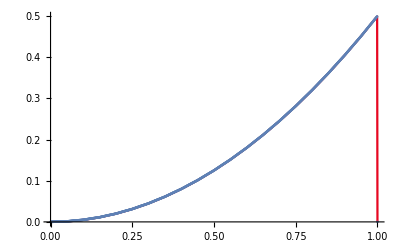
{-Graphics-,-Graphics-}

```mathematica
list={{0,0*10^(0)},{0.001,3.28155*10^(-5)},{0.002,6.5631*10^(-5)},{0.003,9.84465*10^(-5)},{0.004,1.31262*10^(-4)},{0.005,1.64077*10^(-4)},{0.006,1.96893*10^(-4)},{0.007,2.29708*10^(-4)},{0.008,2.62524*10^(-4)},{0.009,2.95339*10^(-4)},{0.01,3.28155*10^(-4)},{0.011,3.6097*10^(-4)},{0.012,3.93786*10^(-4)},{0.013,4.26601*10^(-4)},{0.014,4.59417*10^(-4)},{0.015,4.92232*10^(-4)},{0.016,5.25048*10^(-4)},{0.017,5.57863*10^(-4)},{0.018,5.90679*10^(-4)},{0.019,6.23494*10^(-4)},{0.02,6.5631*10^(-4)},{0.021,6.89125*10^(-4)},{0.022,7.21941*10^(-4)},{0.023,7.54756*10^(-4)},{0.024,7.87572*10^(-4)},{0.025,8.20387*10^(-4)},{0.026,8.37572*10^(-4)},{0.027,8.54756*10^(-4)},{0.028,8.7194*10^(-4)},{0.029,8.89125*10^(-4)},{0.03,9.06309*10^(-4)},{0.031,9.23493*10^(-4)},{0.032,9.40678*10^(-4)},{0.033,9.57862*10^(-4)},{0.034,9.75046*10^(-4)},{0.035,9.92231*10^(-4)},{0.036,1.00941*10^(-3)},{0.037,1.0266*10^(-3)},{0.038,1.04378*10^(-3)},{0.039,1.06097*10^(-3)},{0.04,1.07815*10^(-3)},{0.041,1.09534*10^(-3)},{0.042,1.11252*10^(-3)},{0.043,1.12971*10^(-3)},{0.044,1.14689*10^(-3)},{0.045,1.16407*10^(-3)},{0.046,1.18126*10^(-3)},{0.047,1.19844*10^(-3)},{0.048,1.21563*10^(-3)},{0.049,1.23281*10^(-3)},{0.05,1.25*10^(-3)},{0.051,1.33281*10^(-3)},{0.052,1.41563*10^(-3)},{0.053,1.49845*10^(-3)},{0.054,1.58126*10^(-3)},{0.055,1.66408*10^(-3)},{0.056,1.74689*10^(-3)},{0.057,1.82971*10^(-3)},{0.058,1.91253*10^(-3)},{0.059,1.99534*10^(-3)},{0.06,2.07816*10^(-3)},{0.061,2.16098*10^(-3)},{0.062,2.24379*10^(-3)},{0.063,2.32661*10^(-3)},{0.064,2.40942*10^(-3)},{0.065,2.49224*10^(-3)},{0.066,2.57506*10^(-3)},{0.067,2.65787*10^(-3)},{0.068,2.74069*10^(-3)},{0.069,2.8235*10^(-3)},{0.07,2.90632*10^(-3)},{0.071,2.98914*10^(-3)},{0.072,3.07195*10^(-3)},{0.073,3.15477*10^(-3)},{0.074,3.23758*10^(-3)},{0.075,3.3204*10^(-3)},{0.076,3.38758*10^(-3)},{0.077,3.45477*10^(-3)},{0.078,3.52195*10^(-3)},{0.079,3.58913*10^(-3)},{0.08,3.65632*10^(-3)},{0.081,3.7235*10^(-3)},{0.082,3.79069*10^(-3)},{0.083,3.85787*10^(-3)},{0.084,3.92505*10^(-3)},{0.085,3.99224*10^(-3)},{0.086,4.05942*10^(-3)},{0.087,4.1266*10^(-3)},{0.088,4.19379*10^(-3)},{0.089,4.26097*10^(-3)},{0.09,4.32815*10^(-3)},{0.091,4.39534*10^(-3)},{0.092,4.46252*10^(-3)},{0.093,4.52971*10^(-3)},{0.094,4.59689*10^(-3)},{0.095,4.66407*10^(-3)},{0.096,4.73126*10^(-3)},{0.097,4.79844*10^(-3)},{0.098,4.86562*10^(-3)},{0.099,4.93281*10^(-3)},{0.1,5*10^(-3)},{0.101,5.13281*10^(-3)},{0.102,5.26563*10^(-3)},{0.103,5.39845*10^(-3)},{0.104,5.53126*10^(-3)},{0.105,5.66408*10^(-3)},{0.106,5.7969*10^(-3)},{0.107,5.92971*10^(-3)},{0.108,6.06253*10^(-3)},{0.109,6.19535*10^(-3)},{0.11,6.32816*10^(-3)},{0.111,6.46098*10^(-3)},{0.112,6.5938*10^(-3)},{0.113,6.72661*10^(-3)},{0.114,6.85943*10^(-3)},{0.115,6.99225*10^(-3)},{0.116,7.12506*10^(-3)},{0.117,7.25788*10^(-3)},{0.118,7.3907*10^(-3)},{0.119,7.52351*10^(-3)},{0.12,7.65633*10^(-3)},{0.121,7.78915*10^(-3)},{0.122,7.92196*10^(-3)},{0.123,8.05478*10^(-3)},{0.124,8.1876*10^(-3)},{0.125,8.32041*10^(-3)},{0.126,8.4376*10^(-3)},{0.127,8.55478*10^(-3)},{0.128,8.67196*10^(-3)},{0.129,8.78914*10^(-3)},{0.13,8.90633*10^(-3)},{0.131,9.02351*10^(-3)},{0.132,9.14069*10^(-3)},{0.133,9.25788*10^(-3)},{0.134,9.37506*10^(-3)},{0.135,9.49224*10^(-3)},{0.136,9.60943*10^(-3)},{0.137,9.72661*10^(-3)},{0.138,9.84379*10^(-3)},{0.139,9.96097*10^(-3)},{0.14,1.00782*10^(-2)},{0.141,1.01953*10^(-2)},{0.142,1.03125*10^(-2)},{0.143,1.04297*10^(-2)},{0.144,1.05469*10^(-2)},{0.145,1.06641*10^(-2)},{0.146,1.07813*10^(-2)},{0.147,1.08984*10^(-2)},{0.148,1.10156*10^(-2)},{0.149,1.11328*10^(-2)},{0.15,1.125*10^(-2)},{0.151,1.14328*10^(-2)},{0.152,1.16156*10^(-2)},{0.153,1.17984*10^(-2)},{0.154,1.19813*10^(-2)},{0.155,1.21641*10^(-2)},{0.156,1.23469*10^(-2)},{0.157,1.25297*10^(-2)},{0.158,1.27125*10^(-2)},{0.159,1.28954*10^(-2)},{0.16,1.30782*10^(-2)},{0.161,1.3261*10^(-2)},{0.162,1.34438*10^(-2)},{0.163,1.36266*10^(-2)},{0.164,1.38094*10^(-2)},{0.165,1.39923*10^(-2)},{0.166,1.41751*10^(-2)},{0.167,1.43579*10^(-2)},{0.168,1.45407*10^(-2)},{0.169,1.47235*10^(-2)},{0.17,1.49063*10^(-2)},{0.171,1.50892*10^(-2)},{0.172,1.5272*10^(-2)},{0.173,1.54548*10^(-2)},{0.174,1.56376*10^(-2)},{0.175,1.58204*10^(-2)},{0.176,1.59876*10^(-2)},{0.177,1.61548*10^(-2)},{0.178,1.6322*10^(-2)},{0.179,1.64892*10^(-2)},{0.18,1.66563*10^(-2)},{0.181,1.68235*10^(-2)},{0.182,1.69907*10^(-2)},{0.183,1.71579*10^(-2)},{0.184,1.73251*10^(-2)},{0.185,1.74922*10^(-2)},{0.186,1.76594*10^(-2)},{0.187,1.78266*10^(-2)},{0.188,1.79938*10^(-2)},{0.189,1.8161*10^(-2)},{0.19,1.83282*10^(-2)},{0.191,1.84953*10^(-2)},{0.192,1.86625*10^(-2)},{0.193,1.88297*10^(-2)},{0.194,1.89969*10^(-2)},{0.195,1.91641*10^(-2)},{0.196,1.93313*10^(-2)},{0.197,1.94984*10^(-2)},{0.198,1.96656*10^(-2)},{0.199,1.98328*10^(-2)},{0.2,2*10^(-2)},{0.201,2.02328*10^(-2)},{0.202,2.04656*10^(-2)},{0.203,2.06984*10^(-2)},{0.204,2.09313*10^(-2)},{0.205,2.11641*10^(-2)},{0.206,2.13969*10^(-2)},{0.207,2.16297*10^(-2)},{0.208,2.18625*10^(-2)},{0.209,2.20954*10^(-2)},{0.21,2.23282*10^(-2)},{0.211,2.2561*10^(-2)},{0.212,2.27938*10^(-2)},{0.213,2.30266*10^(-2)},{0.214,2.32594*10^(-2)},{0.215,2.34923*10^(-2)},{0.216,2.37251*10^(-2)},{0.217,2.39579*10^(-2)},{0.218,2.41907*10^(-2)},{0.219,2.44235*10^(-2)},{0.22,2.46564*10^(-2)},{0.221,2.48892*10^(-2)},{0.222,2.5122*10^(-2)},{0.223,2.53548*10^(-2)},{0.224,2.55876*10^(-2)},{0.225,2.58204*10^(-2)},{0.226,2.60376*10^(-2)},{0.227,2.62548*10^(-2)},{0.228,2.6472*10^(-2)},{0.229,2.66892*10^(-2)},{0.23,2.69063*10^(-2)},{0.231,2.71235*10^(-2)},{0.232,2.73407*10^(-2)},{0.233,2.75579*10^(-2)},{0.234,2.77751*10^(-2)},{0.235,2.79923*10^(-2)},{0.236,2.82094*10^(-2)},{0.237,2.84266*10^(-2)},{0.238,2.86438*10^(-2)},{0.239,2.8861*10^(-2)},{0.24,2.90782*10^(-2)},{0.241,2.92953*10^(-2)},{0.242,2.95125*10^(-2)},{0.243,2.97297*10^(-2)},{0.244,2.99469*10^(-2)},{0.245,3.01641*10^(-2)},{0.246,3.03813*10^(-2)},{0.247,3.05984*10^(-2)},{0.248,3.08156*10^(-2)},{0.249,3.10328*10^(-2)},{0.25,3.125*10^(-2)},{0.251,3.15328*10^(-2)},{0.252,3.18156*10^(-2)},{0.253,3.20984*10^(-2)},{0.254,3.23813*10^(-2)},{0.255,3.26641*10^(-2)},{0.256,3.29469*10^(-2)},{0.257,3.32297*10^(-2)},{0.258,3.35125*10^(-2)},{0.259,3.37954*10^(-2)},{0.26,3.40782*10^(-2)},{0.261,3.4361*10^(-2)},{0.262,3.46438*10^(-2)},{0.263,3.49266*10^(-2)},{0.264,3.52095*10^(-2)},{0.265,3.54923*10^(-2)},{0.266,3.57751*10^(-2)},{0.267,3.60579*10^(-2)},{0.268,3.63407*10^(-2)},{0.269,3.66235*10^(-2)},{0.27,3.69064*10^(-2)},{0.271,3.71892*10^(-2)},{0.272,3.7472*10^(-2)},{0.273,3.77548*10^(-2)},{0.274,3.80376*10^(-2)},{0.275,3.83205*10^(-2)},{0.276,3.85876*10^(-2)},{0.277,3.88548*10^(-2)},{0.278,3.9122*10^(-2)},{0.279,3.93892*10^(-2)},{0.28,3.96564*10^(-2)},{0.281,3.99235*10^(-2)},{0.282,4.01907*10^(-2)},{0.283,4.04579*10^(-2)},{0.284,4.07251*10^(-2)},{0.285,4.09923*10^(-2)},{0.286,4.12594*10^(-2)},{0.287,4.15266*10^(-2)},{0.288,4.17938*10^(-2)},{0.289,4.2061*10^(-2)},{0.29,4.23282*10^(-2)},{0.291,4.25953*10^(-2)},{0.292,4.28625*10^(-2)},{0.293,4.31297*10^(-2)},{0.294,4.33969*10^(-2)},{0.295,4.36641*10^(-2)},{0.296,4.39313*10^(-2)},{0.297,4.41984*10^(-2)},{0.298,4.44656*10^(-2)},{0.299,4.47328*10^(-2)},{0.3,4.5*10^(-2)},{0.301,4.53328*10^(-2)},{0.302,4.56656*10^(-2)},{0.303,4.59984*10^(-2)},{0.304,4.63313*10^(-2)},{0.305,4.66641*10^(-2)},{0.306,4.69969*10^(-2)},{0.307,4.73297*10^(-2)},{0.308,4.76625*10^(-2)},{0.309,4.79954*10^(-2)},{0.31,4.83282*10^(-2)},{0.311,4.8661*10^(-2)},{0.312,4.89938*10^(-2)},{0.313,4.93266*10^(-2)},{0.314,4.96595*10^(-2)},{0.315,4.99923*10^(-2)},{0.316,5.03251*10^(-2)},{0.317,5.06579*10^(-2)},{0.318,5.09907*10^(-2)},{0.319,5.13236*10^(-2)},{0.32,5.16564*10^(-2)},{0.321,5.19892*10^(-2)},{0.322,5.2322*10^(-2)},{0.323,5.26548*10^(-2)},{0.324,5.29876*10^(-2)},{0.325,5.33205*10^(-2)},{0.326,5.36376*10^(-2)},{0.327,5.39548*10^(-2)},{0.328,5.4272*10^(-2)},{0.329,5.45892*10^(-2)},{0.33,5.49064*10^(-2)},{0.331,5.52235*10^(-2)},{0.332,5.55407*10^(-2)},{0.333,5.58579*10^(-2)},{0.334,5.61751*10^(-2)},{0.335,5.64923*10^(-2)},{0.336,5.68094*10^(-2)},{0.337,5.71266*10^(-2)},{0.338,5.74438*10^(-2)},{0.339,5.7761*10^(-2)},{0.34,5.80782*10^(-2)},{0.341,5.83953*10^(-2)},{0.342,5.87125*10^(-2)},{0.343,5.90297*10^(-2)},{0.344,5.93469*10^(-2)},{0.345,5.96641*10^(-2)},{0.346,5.99812*10^(-2)},{0.347,6.02984*10^(-2)},{0.348,6.06156*10^(-2)},{0.349,6.09328*10^(-2)},{0.35,6.125*10^(-2)},{0.351,6.16328*10^(-2)},{0.352,6.20156*10^(-2)},{0.353,6.23984*10^(-2)},{0.354,6.27813*10^(-2)},{0.355,6.31641*10^(-2)},{0.356,6.35469*10^(-2)},{0.357,6.39297*10^(-2)},{0.358,6.43125*10^(-2)},{0.359,6.46954*10^(-2)},{0.36,6.50782*10^(-2)},{0.361,6.5461*10^(-2)},{0.362,6.58438*10^(-2)},{0.363,6.62266*10^(-2)},{0.364,6.66095*10^(-2)},{0.365,6.69923*10^(-2)},{0.366,6.73751*10^(-2)},{0.367,6.77579*10^(-2)},{0.368,6.81407*10^(-2)},{0.369,6.85236*10^(-2)},{0.37,6.89064*10^(-2)},{0.371,6.92892*10^(-2)},{0.372,6.9672*10^(-2)},{0.373,7.00548*10^(-2)},{0.374,7.04377*10^(-2)},{0.375,7.08205*10^(-2)},{0.376,7.11877*10^(-2)},{0.377,7.15548*10^(-2)},{0.378,7.1922*10^(-2)},{0.379,7.22892*10^(-2)},{0.38,7.26564*10^(-2)},{0.381,7.30236*10^(-2)},{0.382,7.33907*10^(-2)},{0.383,7.37579*10^(-2)},{0.384,7.41251*10^(-2)},{0.385,7.44923*10^(-2)},{0.386,7.48595*10^(-2)},{0.387,7.52266*10^(-2)},{0.388,7.55938*10^(-2)},{0.389,7.5961*10^(-2)},{0.39,7.63282*10^(-2)},{0.391,7.66953*10^(-2)},{0.392,7.70625*10^(-2)},{0.393,7.74297*10^(-2)},{0.394,7.77969*10^(-2)},{0.395,7.81641*10^(-2)},{0.396,7.85312*10^(-2)},{0.397,7.88984*10^(-2)},{0.398,7.92656*10^(-2)},{0.399,7.96328*10^(-2)},{0.4,8*10^(-2)},{0.401,8.04328*10^(-2)},{0.402,8.08656*10^(-2)},{0.403,8.12984*10^(-2)},{0.404,8.17313*10^(-2)},{0.405,8.21641*10^(-2)},{0.406,8.25969*10^(-2)},{0.407,8.30297*10^(-2)},{0.408,8.34625*10^(-2)},{0.409,8.38954*10^(-2)},{0.41,8.43282*10^(-2)},{0.411,8.4761*10^(-2)},{0.412,8.51938*10^(-2)},{0.413,8.56266*10^(-2)},{0.414,8.60595*10^(-2)},{0.415,8.64923*10^(-2)},{0.416,8.69251*10^(-2)},{0.417,8.73579*10^(-2)},{0.418,8.77908*10^(-2)},{0.419,8.82236*10^(-2)},{0.42,8.86564*10^(-2)},{0.421,8.90892*10^(-2)},{0.422,8.9522*10^(-2)},{0.423,8.99549*10^(-2)},{0.424,9.03877*10^(-2)},{0.425,9.08205*10^(-2)},{0.426,9.12377*10^(-2)},{0.427,9.16548*10^(-2)},{0.428,9.2072*10^(-2)},{0.429,9.24892*10^(-2)},{0.43,9.29064*10^(-2)},{0.431,9.33236*10^(-2)},{0.432,9.37407*10^(-2)},{0.433,9.41579*10^(-2)},{0.434,9.45751*10^(-2)},{0.435,9.49923*10^(-2)},{0.436,9.54095*10^(-2)},{0.437,9.58266*10^(-2)},{0.438,9.62438*10^(-2)},{0.439,9.6661*10^(-2)},{0.44,9.70782*10^(-2)},{0.441,9.74954*10^(-2)},{0.442,9.79125*10^(-2)},{0.443,9.83297*10^(-2)},{0.444,9.87469*10^(-2)},{0.445,9.91641*10^(-2)},{0.446,9.95812*10^(-2)},{0.447,9.99984*10^(-2)},{0.448,1.00416*10^(-1)},{0.449,1.00833*10^(-1)},{0.45,1.0125*10^(-1)},{0.451,1.01733*10^(-1)},{0.452,1.02216*10^(-1)},{0.453,1.02698*10^(-1)},{0.454,1.03181*10^(-1)},{0.455,1.03664*10^(-1)},{0.456,1.04147*10^(-1)},{0.457,1.0463*10^(-1)},{0.458,1.05113*10^(-1)},{0.459,1.05595*10^(-1)},{0.46,1.06078*10^(-1)},{0.461,1.06561*10^(-1)},{0.462,1.07044*10^(-1)},{0.463,1.07527*10^(-1)},{0.464,1.08009*10^(-1)},{0.465,1.08492*10^(-1)},{0.466,1.08975*10^(-1)},{0.467,1.09458*10^(-1)},{0.468,1.09941*10^(-1)},{0.469,1.10424*10^(-1)},{0.47,1.10906*10^(-1)},{0.471,1.11389*10^(-1)},{0.472,1.11872*10^(-1)},{0.473,1.12355*10^(-1)},{0.474,1.12838*10^(-1)},{0.475,1.13321*10^(-1)},{0.476,1.13788*10^(-1)},{0.477,1.14255*10^(-1)},{0.478,1.14722*10^(-1)},{0.479,1.15189*10^(-1)},{0.48,1.15656*10^(-1)},{0.481,1.16124*10^(-1)},{0.482,1.16591*10^(-1)},{0.483,1.17058*10^(-1)},{0.484,1.17525*10^(-1)},{0.485,1.17992*10^(-1)},{0.486,1.18459*10^(-1)},{0.487,1.18927*10^(-1)},{0.488,1.19394*10^(-1)},{0.489,1.19861*10^(-1)},{0.49,1.20328*10^(-1)},{0.491,1.20795*10^(-1)},{0.492,1.21263*10^(-1)},{0.493,1.2173*10^(-1)},{0.494,1.22197*10^(-1)},{0.495,1.22664*10^(-1)},{0.496,1.23131*10^(-1)},{0.497,1.23598*10^(-1)},{0.498,1.24066*10^(-1)},{0.499,1.24533*10^(-1)},{0.5,1.25*10^(-1)},{0.501,1.25533*10^(-1)},{0.502,1.26066*10^(-1)},{0.503,1.26598*10^(-1)},{0.504,1.27131*10^(-1)},{0.505,1.27664*10^(-1)},{0.506,1.28197*10^(-1)},{0.507,1.2873*10^(-1)},{0.508,1.29263*10^(-1)},{0.509,1.29795*10^(-1)},{0.51,1.30328*10^(-1)},{0.511,1.30861*10^(-1)},{0.512,1.31394*10^(-1)},{0.513,1.31927*10^(-1)},{0.514,1.32459*10^(-1)},{0.515,1.32992*10^(-1)},{0.516,1.33525*10^(-1)},{0.517,1.34058*10^(-1)},{0.518,1.34591*10^(-1)},{0.519,1.35124*10^(-1)},{0.52,1.35656*10^(-1)},{0.521,1.36189*10^(-1)},{0.522,1.36722*10^(-1)},{0.523,1.37255*10^(-1)},{0.524,1.37788*10^(-1)},{0.525,1.38321*10^(-1)},{0.526,1.38838*10^(-1)},{0.527,1.39355*10^(-1)},{0.528,1.39872*10^(-1)},{0.529,1.40389*10^(-1)},{0.53,1.40906*10^(-1)},{0.531,1.41424*10^(-1)},{0.532,1.41941*10^(-1)},{0.533,1.42458*10^(-1)},{0.534,1.42975*10^(-1)},{0.535,1.43492*10^(-1)},{0.536,1.44009*10^(-1)},{0.537,1.44527*10^(-1)},{0.538,1.45044*10^(-1)},{0.539,1.45561*10^(-1)},{0.54,1.46078*10^(-1)},{0.541,1.46595*10^(-1)},{0.542,1.47113*10^(-1)},{0.543,1.4763*10^(-1)},{0.544,1.48147*10^(-1)},{0.545,1.48664*10^(-1)},{0.546,1.49181*10^(-1)},{0.547,1.49698*10^(-1)},{0.548,1.50216*10^(-1)},{0.549,1.50733*10^(-1)},{0.55,1.5125*10^(-1)},{0.551,1.51833*10^(-1)},{0.552,1.52416*10^(-1)},{0.553,1.52998*10^(-1)},{0.554,1.53581*10^(-1)},{0.555,1.54164*10^(-1)},{0.556,1.54747*10^(-1)},{0.557,1.5533*10^(-1)},{0.558,1.55913*10^(-1)},{0.559,1.56495*10^(-1)},{0.56,1.57078*10^(-1)},{0.561,1.57661*10^(-1)},{0.562,1.58244*10^(-1)},{0.563,1.58827*10^(-1)},{0.564,1.59409*10^(-1)},{0.565,1.59992*10^(-1)},{0.566,1.60575*10^(-1)},{0.567,1.61158*10^(-1)},{0.568,1.61741*10^(-1)},{0.569,1.62324*10^(-1)},{0.57,1.62906*10^(-1)},{0.571,1.63489*10^(-1)},{0.572,1.64072*10^(-1)},{0.573,1.64655*10^(-1)},{0.574,1.65238*10^(-1)},{0.575,1.65821*10^(-1)},{0.576,1.66388*10^(-1)},{0.577,1.66955*10^(-1)},{0.578,1.67522*10^(-1)},{0.579,1.68089*10^(-1)},{0.58,1.68656*10^(-1)},{0.581,1.69224*10^(-1)},{0.582,1.69791*10^(-1)},{0.583,1.70358*10^(-1)},{0.584,1.70925*10^(-1)},{0.585,1.71492*10^(-1)},{0.586,1.72059*10^(-1)},{0.587,1.72627*10^(-1)},{0.588,1.73194*10^(-1)},{0.589,1.73761*10^(-1)},{0.59,1.74328*10^(-1)},{0.591,1.74895*10^(-1)},{0.592,1.75463*10^(-1)},{0.593,1.7603*10^(-1)},{0.594,1.76597*10^(-1)},{0.595,1.77164*10^(-1)},{0.596,1.77731*10^(-1)},{0.597,1.78298*10^(-1)},{0.598,1.78866*10^(-1)},{0.599,1.79433*10^(-1)},{0.6,1.8*10^(-1)},{0.601,1.80633*10^(-1)},{0.602,1.81266*10^(-1)},{0.603,1.81898*10^(-1)},{0.604,1.82531*10^(-1)},{0.605,1.83164*10^(-1)},{0.606,1.83797*10^(-1)},{0.607,1.8443*10^(-1)},{0.608,1.85063*10^(-1)},{0.609,1.85695*10^(-1)},{0.61,1.86328*10^(-1)},{0.611,1.86961*10^(-1)},{0.612,1.87594*10^(-1)},{0.613,1.88227*10^(-1)},{0.614,1.88859*10^(-1)},{0.615,1.89492*10^(-1)},{0.616,1.90125*10^(-1)},{0.617,1.90758*10^(-1)},{0.618,1.91391*10^(-1)},{0.619,1.92024*10^(-1)},{0.62,1.92656*10^(-1)},{0.621,1.93289*10^(-1)},{0.622,1.93922*10^(-1)},{0.623,1.94555*10^(-1)},{0.624,1.95188*10^(-1)},{0.625,1.95821*10^(-1)},{0.626,1.96438*10^(-1)},{0.627,1.97055*10^(-1)},{0.628,1.97672*10^(-1)},{0.629,1.98289*10^(-1)},{0.63,1.98906*10^(-1)},{0.631,1.99524*10^(-1)},{0.632,2.00141*10^(-1)},{0.633,2.00758*10^(-1)},{0.634,2.01375*10^(-1)},{0.635,2.01992*10^(-1)},{0.636,2.02609*10^(-1)},{0.637,2.03227*10^(-1)},{0.638,2.03844*10^(-1)},{0.639,2.04461*10^(-1)},{0.64,2.05078*10^(-1)},{0.641,2.05695*10^(-1)},{0.642,2.06313*10^(-1)},{0.643,2.0693*10^(-1)},{0.644,2.07547*10^(-1)},{0.645,2.08164*10^(-1)},{0.646,2.08781*10^(-1)},{0.647,2.09398*10^(-1)},{0.648,2.10016*10^(-1)},{0.649,2.10633*10^(-1)},{0.65,2.1125*10^(-1)},{0.651,2.11933*10^(-1)},{0.652,2.12616*10^(-1)},{0.653,2.13298*10^(-1)},{0.654,2.13981*10^(-1)},{0.655,2.14664*10^(-1)},{0.656,2.15347*10^(-1)},{0.657,2.1603*10^(-1)},{0.658,2.16713*10^(-1)},{0.659,2.17395*10^(-1)},{0.66,2.18078*10^(-1)},{0.661,2.18761*10^(-1)},{0.662,2.19444*10^(-1)},{0.663,2.20127*10^(-1)},{0.664,2.2081*10^(-1)},{0.665,2.21492*10^(-1)},{0.666,2.22175*10^(-1)},{0.667,2.22858*10^(-1)},{0.668,2.23541*10^(-1)},{0.669,2.24224*10^(-1)},{0.67,2.24906*10^(-1)},{0.671,2.25589*10^(-1)},{0.672,2.26272*10^(-1)},{0.673,2.26955*10^(-1)},{0.674,2.27638*10^(-1)},{0.675,2.28321*10^(-1)},{0.676,2.28988*10^(-1)},{0.677,2.29655*10^(-1)},{0.678,2.30322*10^(-1)},{0.679,2.30989*10^(-1)},{0.68,2.31656*10^(-1)},{0.681,2.32324*10^(-1)},{0.682,2.32991*10^(-1)},{0.683,2.33658*10^(-1)},{0.684,2.34325*10^(-1)},{0.685,2.34992*10^(-1)},{0.686,2.35659*10^(-1)},{0.687,2.36327*10^(-1)},{0.688,2.36994*10^(-1)},{0.689,2.37661*10^(-1)},{0.69,2.38328*10^(-1)},{0.691,2.38995*10^(-1)},{0.692,2.39663*10^(-1)},{0.693,2.4033*10^(-1)},{0.694,2.40997*10^(-1)},{0.695,2.41664*10^(-1)},{0.696,2.42331*10^(-1)},{0.697,2.42998*10^(-1)},{0.698,2.43666*10^(-1)},{0.699,2.44333*10^(-1)},{0.7,2.45*10^(-1)},{0.701,2.45733*10^(-1)},{0.702,2.46466*10^(-1)},{0.703,2.47198*10^(-1)},{0.704,2.47931*10^(-1)},{0.705,2.48664*10^(-1)},{0.706,2.49397*10^(-1)},{0.707,2.5013*10^(-1)},{0.708,2.50863*10^(-1)},{0.709,2.51595*10^(-1)},{0.71,2.52328*10^(-1)},{0.711,2.53061*10^(-1)},{0.712,2.53794*10^(-1)},{0.713,2.54527*10^(-1)},{0.714,2.5526*10^(-1)},{0.715,2.55992*10^(-1)},{0.716,2.56725*10^(-1)},{0.717,2.57458*10^(-1)},{0.718,2.58191*10^(-1)},{0.719,2.58924*10^(-1)},{0.72,2.59656*10^(-1)},{0.721,2.60389*10^(-1)},{0.722,2.61122*10^(-1)},{0.723,2.61855*10^(-1)},{0.724,2.62588*10^(-1)},{0.725,2.63321*10^(-1)},{0.726,2.64038*10^(-1)},{0.727,2.64755*10^(-1)},{0.728,2.65472*10^(-1)},{0.729,2.66189*10^(-1)},{0.73,2.66906*10^(-1)},{0.731,2.67624*10^(-1)},{0.732,2.68341*10^(-1)},{0.733,2.69058*10^(-1)},{0.734,2.69775*10^(-1)},{0.735,2.70492*10^(-1)},{0.736,2.71209*10^(-1)},{0.737,2.71927*10^(-1)},{0.738,2.72644*10^(-1)},{0.739,2.73361*10^(-1)},{0.74,2.74078*10^(-1)},{0.741,2.74795*10^(-1)},{0.742,2.75513*10^(-1)},{0.743,2.7623*10^(-1)},{0.744,2.76947*10^(-1)},{0.745,2.77664*10^(-1)},{0.746,2.78381*10^(-1)},{0.747,2.79098*10^(-1)},{0.748,2.79816*10^(-1)},{0.749,2.80533*10^(-1)},{0.75,2.8125*10^(-1)},{0.751,2.82033*10^(-1)},{0.752,2.82816*10^(-1)},{0.753,2.83598*10^(-1)},{0.754,2.84381*10^(-1)},{0.755,2.85164*10^(-1)},{0.756,2.85947*10^(-1)},{0.757,2.8673*10^(-1)},{0.758,2.87513*10^(-1)},{0.759,2.88295*10^(-1)},{0.76,2.89078*10^(-1)},{0.761,2.89861*10^(-1)},{0.762,2.90644*10^(-1)},{0.763,2.91427*10^(-1)},{0.764,2.9221*10^(-1)},{0.765,2.92992*10^(-1)},{0.766,2.93775*10^(-1)},{0.767,2.94558*10^(-1)},{0.768,2.95341*10^(-1)},{0.769,2.96124*10^(-1)},{0.77,2.96906*10^(-1)},{0.771,2.97689*10^(-1)},{0.772,2.98472*10^(-1)},{0.773,2.99255*10^(-1)},{0.774,3.00038*10^(-1)},{0.775,3.00821*10^(-1)},{0.776,3.01588*10^(-1)},{0.777,3.02355*10^(-1)},{0.778,3.03122*10^(-1)},{0.779,3.03889*10^(-1)},{0.78,3.04656*10^(-1)},{0.781,3.05424*10^(-1)},{0.782,3.06191*10^(-1)},{0.783,3.06958*10^(-1)},{0.784,3.07725*10^(-1)},{0.785,3.08492*10^(-1)},{0.786,3.09259*10^(-1)},{0.787,3.10027*10^(-1)},{0.788,3.10794*10^(-1)},{0.789,3.11561*10^(-1)},{0.79,3.12328*10^(-1)},{0.791,3.13095*10^(-1)},{0.792,3.13863*10^(-1)},{0.793,3.1463*10^(-1)},{0.794,3.15397*10^(-1)},{0.795,3.16164*10^(-1)},{0.796,3.16931*10^(-1)},{0.797,3.17698*10^(-1)},{0.798,3.18466*10^(-1)},{0.799,3.19233*10^(-1)},{0.8,3.2*10^(-1)},{0.801,3.20833*10^(-1)},{0.802,3.21666*10^(-1)},{0.803,3.22498*10^(-1)},{0.804,3.23331*10^(-1)},{0.805,3.24164*10^(-1)},{0.806,3.24997*10^(-1)},{0.807,3.2583*10^(-1)},{0.808,3.26663*10^(-1)},{0.809,3.27495*10^(-1)},{0.81,3.28328*10^(-1)},{0.811,3.29161*10^(-1)},{0.812,3.29994*10^(-1)},{0.813,3.30827*10^(-1)},{0.814,3.3166*10^(-1)},{0.815,3.32492*10^(-1)},{0.816,3.33325*10^(-1)},{0.817,3.34158*10^(-1)},{0.818,3.34991*10^(-1)},{0.819,3.35824*10^(-1)},{0.82,3.36656*10^(-1)},{0.821,3.37489*10^(-1)},{0.822,3.38322*10^(-1)},{0.823,3.39155*10^(-1)},{0.824,3.39988*10^(-1)},{0.825,3.40821*10^(-1)},{0.826,3.41638*10^(-1)},{0.827,3.42455*10^(-1)},{0.828,3.43272*10^(-1)},{0.829,3.44089*10^(-1)},{0.83,3.44906*10^(-1)},{0.831,3.45724*10^(-1)},{0.832,3.46541*10^(-1)},{0.833,3.47358*10^(-1)},{0.834,3.48175*10^(-1)},{0.835,3.48992*10^(-1)},{0.836,3.49809*10^(-1)},{0.837,3.50627*10^(-1)},{0.838,3.51444*10^(-1)},{0.839,3.52261*10^(-1)},{0.84,3.53078*10^(-1)},{0.841,3.53895*10^(-1)},{0.842,3.54713*10^(-1)},{0.843,3.5553*10^(-1)},{0.844,3.56347*10^(-1)},{0.845,3.57164*10^(-1)},{0.846,3.57981*10^(-1)},{0.847,3.58798*10^(-1)},{0.848,3.59616*10^(-1)},{0.849,3.60433*10^(-1)},{0.85,3.6125*10^(-1)},{0.851,3.62133*10^(-1)},{0.852,3.63016*10^(-1)},{0.853,3.63898*10^(-1)},{0.854,3.64781*10^(-1)},{0.855,3.65664*10^(-1)},{0.856,3.66547*10^(-1)},{0.857,3.6743*10^(-1)},{0.858,3.68313*10^(-1)},{0.859,3.69195*10^(-1)},{0.86,3.70078*10^(-1)},{0.861,3.70961*10^(-1)},{0.862,3.71844*10^(-1)},{0.863,3.72727*10^(-1)},{0.864,3.7361*10^(-1)},{0.865,3.74492*10^(-1)},{0.866,3.75375*10^(-1)},{0.867,3.76258*10^(-1)},{0.868,3.77141*10^(-1)},{0.869,3.78024*10^(-1)},{0.87,3.78906*10^(-1)},{0.871,3.79789*10^(-1)},{0.872,3.80672*10^(-1)},{0.873,3.81555*10^(-1)},{0.874,3.82438*10^(-1)},{0.875,3.83321*10^(-1)},{0.876,3.84188*10^(-1)},{0.877,3.85055*10^(-1)},{0.878,3.85922*10^(-1)},{0.879,3.86789*10^(-1)},{0.88,3.87656*10^(-1)},{0.881,3.88524*10^(-1)},{0.882,3.89391*10^(-1)},{0.883,3.90258*10^(-1)},{0.884,3.91125*10^(-1)},{0.885,3.91992*10^(-1)},{0.886,3.9286*10^(-1)},{0.887,3.93727*10^(-1)},{0.888,3.94594*10^(-1)},{0.889,3.95461*10^(-1)},{0.89,3.96328*10^(-1)},{0.891,3.97195*10^(-1)},{0.892,3.98063*10^(-1)},{0.893,3.9893*10^(-1)},{0.894,3.99797*10^(-1)},{0.895,4.00664*10^(-1)},{0.896,4.01531*10^(-1)},{0.897,4.02398*10^(-1)},{0.898,4.03266*10^(-1)},{0.899,4.04133*10^(-1)},{0.9,4.05*10^(-1)},{0.901,4.05933*10^(-1)},{0.902,4.06866*10^(-1)},{0.903,4.07798*10^(-1)},{0.904,4.08731*10^(-1)},{0.905,4.09664*10^(-1)},{0.906,4.10597*10^(-1)},{0.907,4.1153*10^(-1)},{0.908,4.12463*10^(-1)},{0.909,4.13395*10^(-1)},{0.91,4.14328*10^(-1)},{0.911,4.15261*10^(-1)},{0.912,4.16194*10^(-1)},{0.913,4.17127*10^(-1)},{0.914,4.1806*10^(-1)},{0.915,4.18992*10^(-1)},{0.916,4.19925*10^(-1)},{0.917,4.20858*10^(-1)},{0.918,4.21791*10^(-1)},{0.919,4.22724*10^(-1)},{0.92,4.23656*10^(-1)},{0.921,4.24589*10^(-1)},{0.922,4.25522*10^(-1)},{0.923,4.26455*10^(-1)},{0.924,4.27388*10^(-1)},{0.925,4.28321*10^(-1)},{0.926,4.29238*10^(-1)},{0.927,4.30155*10^(-1)},{0.928,4.31072*10^(-1)},{0.929,4.31989*10^(-1)},{0.93,4.32906*10^(-1)},{0.931,4.33824*10^(-1)},{0.932,4.34741*10^(-1)},{0.933,4.35658*10^(-1)},{0.934,4.36575*10^(-1)},{0.935,4.37492*10^(-1)},{0.936,4.3841*10^(-1)},{0.937,4.39327*10^(-1)},{0.938,4.40244*10^(-1)},{0.939,4.41161*10^(-1)},{0.94,4.42078*10^(-1)},{0.941,4.42995*10^(-1)},{0.942,4.43913*10^(-1)},{0.943,4.4483*10^(-1)},{0.944,4.45747*10^(-1)},{0.945,4.46664*10^(-1)},{0.946,4.47581*10^(-1)},{0.947,4.48498*10^(-1)},{0.948,4.49416*10^(-1)},{0.949,4.50333*10^(-1)},{0.95,4.5125*10^(-1)},{0.951,4.52233*10^(-1)},{0.952,4.53216*10^(-1)},{0.953,4.54198*10^(-1)},{0.954,4.55181*10^(-1)},{0.955,4.56164*10^(-1)},{0.956,4.57147*10^(-1)},{0.957,4.5813*10^(-1)},{0.958,4.59113*10^(-1)},{0.959,4.60095*10^(-1)},{0.96,4.61078*10^(-1)},{0.961,4.62061*10^(-1)},{0.962,4.63044*10^(-1)},{0.963,4.64027*10^(-1)},{0.964,4.6501*10^(-1)},{0.965,4.65992*10^(-1)},{0.966,4.66975*10^(-1)},{0.967,4.67958*10^(-1)},{0.968,4.68941*10^(-1)},{0.969,4.69924*10^(-1)},{0.97,4.70907*10^(-1)},{0.971,4.71889*10^(-1)},{0.972,4.72872*10^(-1)},{0.973,4.73855*10^(-1)},{0.974,4.74838*10^(-1)},{0.975,4.75821*10^(-1)},{0.976,4.76788*10^(-1)},{0.977,4.77755*10^(-1)},{0.978,4.78722*10^(-1)},{0.979,4.79689*10^(-1)},{0.98,4.80656*10^(-1)},{0.981,4.81624*10^(-1)},{0.982,4.82591*10^(-1)},{0.983,4.83558*10^(-1)},{0.984,4.84525*10^(-1)},{0.985,4.85492*10^(-1)},{0.986,4.8646*10^(-1)},{0.987,4.87427*10^(-1)},{0.988,4.88394*10^(-1)},{0.989,4.89361*10^(-1)},{0.99,4.90328*10^(-1)},{0.991,4.91295*10^(-1)},{0.992,4.92263*10^(-1)},{0.993,4.9323*10^(-1)},{0.994,4.94197*10^(-1)},{0.995,4.95164*10^(-1)},{0.996,4.96131*10^(-1)},{0.997,4.97098*10^(-1)},{0.998,4.98066*10^(-1)},{0.999,4.99033*10^(-1)},{1,0*10^(0)}};
imgtemp=ListPlot[list];
maxerror[[3,1]]=Max[tablereal[[All,2]]-list[[All,2]]];
{img,Show[img,imgtemp]}
```

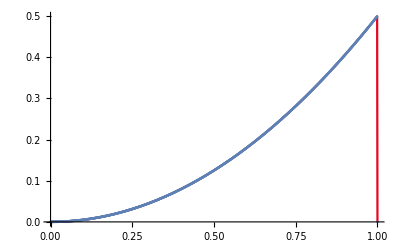
{-Graphics-,-Graphics-}

```mathematica
list={{0,0*10^(0)},{0.001,1.65332*10^(-5)},{0.002,3.30664*10^(-5)},{0.003,4.95997*10^(-5)},{0.004,6.61329*10^(-5)},{0.005,8.26661*10^(-5)},{0.006,9.91993*10^(-5)},{0.007,1.15733*10^(-4)},{0.008,1.32266*10^(-4)},{0.009,1.48799*10^(-4)},{0.01,1.65332*10^(-4)},{0.011,1.81865*10^(-4)},{0.012,1.98399*10^(-4)},{0.013,2.10898*10^(-4)},{0.014,2.19365*10^(-4)},{0.015,2.27832*10^(-4)},{0.016,2.36298*10^(-4)},{0.017,2.44765*10^(-4)},{0.018,2.53232*10^(-4)},{0.019,2.61698*10^(-4)},{0.02,2.70165*10^(-4)},{0.021,2.78632*10^(-4)},{0.022,2.87098*10^(-4)},{0.023,2.95565*10^(-4)},{0.024,3.04031*10^(-4)},{0.025,3.12499*10^(-4)},{0.026,3.54033*10^(-4)},{0.027,3.95566*10^(-4)},{0.028,4.371*10^(-4)},{0.029,4.78634*10^(-4)},{0.03,5.20168*10^(-4)},{0.031,5.61702*10^(-4)},{0.032,6.03236*10^(-4)},{0.033,6.4477*10^(-4)},{0.034,6.86303*10^(-4)},{0.035,7.27837*10^(-4)},{0.036,7.69371*10^(-4)},{0.037,8.10905*10^(-4)},{0.038,8.48405*10^(-4)},{0.039,8.81871*10^(-4)},{0.04,9.15337*10^(-4)},{0.041,9.48802*10^(-4)},{0.042,9.82268*10^(-4)},{0.043,1.01573*10^(-3)},{0.044,1.0492*10^(-3)},{0.045,1.08267*10^(-3)},{0.046,1.11613*10^(-3)},{0.047,1.1496*10^(-3)},{0.048,1.18306*10^(-3)},{0.049,1.21653*10^(-3)},{0.05,1.25*10^(-3)},{0.051,1.31653*10^(-3)},{0.052,1.38307*10^(-3)},{0.053,1.4496*10^(-3)},{0.054,1.51614*10^(-3)},{0.055,1.58267*10^(-3)},{0.056,1.6492*10^(-3)},{0.057,1.71574*10^(-3)},{0.058,1.78227*10^(-3)},{0.059,1.84881*10^(-3)},{0.06,1.91534*10^(-3)},{0.061,1.98188*10^(-3)},{0.062,2.04841*10^(-3)},{0.063,2.11091*10^(-3)},{0.064,2.16938*10^(-3)},{0.065,2.22784*10^(-3)},{0.066,2.28631*10^(-3)},{0.067,2.34477*10^(-3)},{0.068,2.40324*10^(-3)},{0.069,2.4617*10^(-3)},{0.07,2.52017*10^(-3)},{0.071,2.57863*10^(-3)},{0.072,2.6371*10^(-3)},{0.073,2.69556*10^(-3)},{0.074,2.75403*10^(-3)},{0.075,2.8125*10^(-3)},{0.076,2.90403*10^(-3)},{0.077,2.99557*10^(-3)},{0.078,3.0871*10^(-3)},{0.079,3.17864*10^(-3)},{0.08,3.27017*10^(-3)},{0.081,3.36171*10^(-3)},{0.082,3.45324*10^(-3)},{0.083,3.54478*10^(-3)},{0.084,3.63631*10^(-3)},{0.085,3.72785*10^(-3)},{0.086,3.81938*10^(-3)},{0.087,3.91092*10^(-3)},{0.088,3.99842*10^(-3)},{0.089,4.08188*10^(-3)},{0.09,4.16535*10^(-3)},{0.091,4.24881*10^(-3)},{0.092,4.33228*10^(-3)},{0.093,4.41574*10^(-3)},{0.094,4.4992*10^(-3)},{0.095,4.58267*10^(-3)},{0.096,4.66613*10^(-3)},{0.097,4.7496*10^(-3)},{0.098,4.83306*10^(-3)},{0.099,4.91653*10^(-3)},{0.1,4.99999*10^(-3)},{0.101,5.11653*10^(-3)},{0.102,5.23307*10^(-3)},{0.103,5.3496*10^(-3)},{0.104,5.46614*10^(-3)},{0.105,5.58267*10^(-3)},{0.106,5.69921*10^(-3)},{0.107,5.81575*10^(-3)},{0.108,5.93228*10^(-3)},{0.109,6.04882*10^(-3)},{0.11,6.16535*10^(-3)},{0.111,6.28189*10^(-3)},{0.112,6.39842*10^(-3)},{0.113,6.51092*10^(-3)},{0.114,6.61939*10^(-3)},{0.115,6.72785*10^(-3)},{0.116,6.83631*10^(-3)},{0.117,6.94478*10^(-3)},{0.118,7.05324*10^(-3)},{0.119,7.16171*10^(-3)},{0.12,7.27017*10^(-3)},{0.121,7.37863*10^(-3)},{0.122,7.4871*10^(-3)},{0.123,7.59556*10^(-3)},{0.124,7.70403*10^(-3)},{0.125,7.81249*10^(-3)},{0.126,7.95403*10^(-3)},{0.127,8.09557*10^(-3)},{0.128,8.2371*10^(-3)},{0.129,8.37864*10^(-3)},{0.13,8.52018*10^(-3)},{0.131,8.66171*10^(-3)},{0.132,8.80325*10^(-3)},{0.133,8.94478*10^(-3)},{0.134,9.08632*10^(-3)},{0.135,9.22786*10^(-3)},{0.136,9.36939*10^(-3)},{0.137,9.51093*10^(-3)},{0.138,9.64843*10^(-3)},{0.139,9.78189*10^(-3)},{0.14,9.91536*10^(-3)},{0.141,1.00488*10^(-2)},{0.142,1.01823*10^(-2)},{0.143,1.03157*10^(-2)},{0.144,1.04492*10^(-2)},{0.145,1.05827*10^(-2)},{0.146,1.07161*10^(-2)},{0.147,1.08496*10^(-2)},{0.148,1.09831*10^(-2)},{0.149,1.11165*10^(-2)},{0.15,1.125*10^(-2)},{0.151,1.14165*10^(-2)},{0.152,1.15831*10^(-2)},{0.153,1.17496*10^(-2)},{0.154,1.19161*10^(-2)},{0.155,1.20827*10^(-2)},{0.156,1.22492*10^(-2)},{0.157,1.24158*10^(-2)},{0.158,1.25823*10^(-2)},{0.159,1.27488*10^(-2)},{0.16,1.29154*10^(-2)},{0.161,1.30819*10^(-2)},{0.162,1.32484*10^(-2)},{0.163,1.34109*10^(-2)},{0.164,1.35694*10^(-2)},{0.165,1.37279*10^(-2)},{0.166,1.38863*10^(-2)},{0.167,1.40448*10^(-2)},{0.168,1.42032*10^(-2)},{0.169,1.43617*10^(-2)},{0.17,1.45202*10^(-2)},{0.171,1.46786*10^(-2)},{0.172,1.48371*10^(-2)},{0.173,1.49956*10^(-2)},{0.174,1.5154*10^(-2)},{0.175,1.53125*10^(-2)},{0.176,1.5504*10^(-2)},{0.177,1.56956*10^(-2)},{0.178,1.58871*10^(-2)},{0.179,1.60786*10^(-2)},{0.18,1.62702*10^(-2)},{0.181,1.64617*10^(-2)},{0.182,1.66533*10^(-2)},{0.183,1.68448*10^(-2)},{0.184,1.70363*10^(-2)},{0.185,1.72279*10^(-2)},{0.186,1.74194*10^(-2)},{0.187,1.76109*10^(-2)},{0.188,1.77984*10^(-2)},{0.189,1.79819*10^(-2)},{0.19,1.81654*10^(-2)},{0.191,1.83488*10^(-2)},{0.192,1.85323*10^(-2)},{0.193,1.87158*10^(-2)},{0.194,1.88992*10^(-2)},{0.195,1.90827*10^(-2)},{0.196,1.92661*10^(-2)},{0.197,1.94496*10^(-2)},{0.198,1.96331*10^(-2)},{0.199,1.98165*10^(-2)},{0.2,2*10^(-2)},{0.201,2.02165*10^(-2)},{0.202,2.04331*10^(-2)},{0.203,2.06496*10^(-2)},{0.204,2.08661*10^(-2)},{0.205,2.10827*10^(-2)},{0.206,2.12992*10^(-2)},{0.207,2.15158*10^(-2)},{0.208,2.17323*10^(-2)},{0.209,2.19488*10^(-2)},{0.21,2.21654*10^(-2)},{0.211,2.23819*10^(-2)},{0.212,2.25984*10^(-2)},{0.213,2.28109*10^(-2)},{0.214,2.30194*10^(-2)},{0.215,2.32279*10^(-2)},{0.216,2.34363*10^(-2)},{0.217,2.36448*10^(-2)},{0.218,2.38533*10^(-2)},{0.219,2.40617*10^(-2)},{0.22,2.42702*10^(-2)},{0.221,2.44786*10^(-2)},{0.222,2.46871*10^(-2)},{0.223,2.48956*10^(-2)},{0.224,2.5104*10^(-2)},{0.225,2.53125*10^(-2)},{0.226,2.5554*10^(-2)},{0.227,2.57956*10^(-2)},{0.228,2.60371*10^(-2)},{0.229,2.62786*10^(-2)},{0.23,2.65202*10^(-2)},{0.231,2.67617*10^(-2)},{0.232,2.70033*10^(-2)},{0.233,2.72448*10^(-2)},{0.234,2.74863*10^(-2)},{0.235,2.77279*10^(-2)},{0.236,2.79694*10^(-2)},{0.237,2.8211*10^(-2)},{0.238,2.84485*10^(-2)},{0.239,2.86819*10^(-2)},{0.24,2.89154*10^(-2)},{0.241,2.91488*10^(-2)},{0.242,2.93823*10^(-2)},{0.243,2.96158*10^(-2)},{0.244,2.98492*10^(-2)},{0.245,3.00827*10^(-2)},{0.246,3.03161*10^(-2)},{0.247,3.05496*10^(-2)},{0.248,3.07831*10^(-2)},{0.249,3.10165*10^(-2)},{0.25,3.125*10^(-2)},{0.251,3.15165*10^(-2)},{0.252,3.17831*10^(-2)},{0.253,3.20496*10^(-2)},{0.254,3.23161*10^(-2)},{0.255,3.25827*10^(-2)},{0.256,3.28492*10^(-2)},{0.257,3.31158*10^(-2)},{0.258,3.33823*10^(-2)},{0.259,3.36488*10^(-2)},{0.26,3.39154*10^(-2)},{0.261,3.41819*10^(-2)},{0.262,3.44485*10^(-2)},{0.263,3.4711*10^(-2)},{0.264,3.49694*10^(-2)},{0.265,3.52279*10^(-2)},{0.266,3.54863*10^(-2)},{0.267,3.57448*10^(-2)},{0.268,3.60033*10^(-2)},{0.269,3.62617*10^(-2)},{0.27,3.65202*10^(-2)},{0.271,3.67786*10^(-2)},{0.272,3.70371*10^(-2)},{0.273,3.72956*10^(-2)},{0.274,3.7554*10^(-2)},{0.275,3.78125*10^(-2)},{0.276,3.8104*10^(-2)},{0.277,3.83956*10^(-2)},{0.278,3.86871*10^(-2)},{0.279,3.89786*10^(-2)},{0.28,3.92702*10^(-2)},{0.281,3.95617*10^(-2)},{0.282,3.98533*10^(-2)},{0.283,4.01448*10^(-2)},{0.284,4.04363*10^(-2)},{0.285,4.07279*10^(-2)},{0.286,4.10194*10^(-2)},{0.287,4.1311*10^(-2)},{0.288,4.15985*10^(-2)},{0.289,4.18819*10^(-2)},{0.29,4.21654*10^(-2)},{0.291,4.24488*10^(-2)},{0.292,4.27323*10^(-2)},{0.293,4.30158*10^(-2)},{0.294,4.32992*10^(-2)},{0.295,4.35827*10^(-2)},{0.296,4.38661*10^(-2)},{0.297,4.41496*10^(-2)},{0.298,4.44331*10^(-2)},{0.299,4.47165*10^(-2)},{0.3,4.5*10^(-2)},{0.301,4.53165*10^(-2)},{0.302,4.56331*10^(-2)},{0.303,4.59496*10^(-2)},{0.304,4.62661*10^(-2)},{0.305,4.65827*10^(-2)},{0.306,4.68992*10^(-2)},{0.307,4.72158*10^(-2)},{0.308,4.75323*10^(-2)},{0.309,4.78489*10^(-2)},{0.31,4.81654*10^(-2)},{0.311,4.84819*10^(-2)},{0.312,4.87985*10^(-2)},{0.313,4.9111*10^(-2)},{0.314,4.94194*10^(-2)},{0.315,4.97279*10^(-2)},{0.316,5.00363*10^(-2)},{0.317,5.03448*10^(-2)},{0.318,5.06533*10^(-2)},{0.319,5.09617*10^(-2)},{0.32,5.12702*10^(-2)},{0.321,5.15786*10^(-2)},{0.322,5.18871*10^(-2)},{0.323,5.21956*10^(-2)},{0.324,5.2504*10^(-2)},{0.325,5.28125*10^(-2)},{0.326,5.3154*10^(-2)},{0.327,5.34956*10^(-2)},{0.328,5.38371*10^(-2)},{0.329,5.41786*10^(-2)},{0.33,5.45202*10^(-2)},{0.331,5.48617*10^(-2)},{0.332,5.52033*10^(-2)},{0.333,5.55448*10^(-2)},{0.334,5.58864*10^(-2)},{0.335,5.62279*10^(-2)},{0.336,5.65694*10^(-2)},{0.337,5.6911*10^(-2)},{0.338,5.72485*10^(-2)},{0.339,5.75819*10^(-2)},{0.34,5.79154*10^(-2)},{0.341,5.82489*10^(-2)},{0.342,5.85823*10^(-2)},{0.343,5.89158*10^(-2)},{0.344,5.92492*10^(-2)},{0.345,5.95827*10^(-2)},{0.346,5.99161*10^(-2)},{0.347,6.02496*10^(-2)},{0.348,6.05831*10^(-2)},{0.349,6.09165*10^(-2)},{0.35,6.125*10^(-2)},{0.351,6.16165*10^(-2)},{0.352,6.19831*10^(-2)},{0.353,6.23496*10^(-2)},{0.354,6.27162*10^(-2)},{0.355,6.30827*10^(-2)},{0.356,6.34492*10^(-2)},{0.357,6.38158*10^(-2)},{0.358,6.41823*10^(-2)},{0.359,6.45489*10^(-2)},{0.36,6.49154*10^(-2)},{0.361,6.52819*10^(-2)},{0.362,6.56485*10^(-2)},{0.363,6.6011*10^(-2)},{0.364,6.63694*10^(-2)},{0.365,6.67279*10^(-2)},{0.366,6.70864*10^(-2)},{0.367,6.74448*10^(-2)},{0.368,6.78033*10^(-2)},{0.369,6.81617*10^(-2)},{0.37,6.85202*10^(-2)},{0.371,6.88786*10^(-2)},{0.372,6.92371*10^(-2)},{0.373,6.95956*10^(-2)},{0.374,6.9954*10^(-2)},{0.375,7.03125*10^(-2)},{0.376,7.0704*10^(-2)},{0.377,7.10956*10^(-2)},{0.378,7.14871*10^(-2)},{0.379,7.18787*10^(-2)},{0.38,7.22702*10^(-2)},{0.381,7.26617*10^(-2)},{0.382,7.30533*10^(-2)},{0.383,7.34448*10^(-2)},{0.384,7.38364*10^(-2)},{0.385,7.42279*10^(-2)},{0.386,7.46195*10^(-2)},{0.387,7.5011*10^(-2)},{0.388,7.53985*10^(-2)},{0.389,7.57819*10^(-2)},{0.39,7.61654*10^(-2)},{0.391,7.65489*10^(-2)},{0.392,7.69323*10^(-2)},{0.393,7.73158*10^(-2)},{0.394,7.76992*10^(-2)},{0.395,7.80827*10^(-2)},{0.396,7.84661*10^(-2)},{0.397,7.88496*10^(-2)},{0.398,7.92331*10^(-2)},{0.399,7.96165*10^(-2)},{0.4,8*10^(-2)},{0.401,8.04165*10^(-2)},{0.402,8.08331*10^(-2)},{0.403,8.12496*10^(-2)},{0.404,8.16662*10^(-2)},{0.405,8.20827*10^(-2)},{0.406,8.24992*10^(-2)},{0.407,8.29158*10^(-2)},{0.408,8.33323*10^(-2)},{0.409,8.37489*10^(-2)},{0.41,8.41654*10^(-2)},{0.411,8.4582*10^(-2)},{0.412,8.49985*10^(-2)},{0.413,8.5411*10^(-2)},{0.414,8.58195*10^(-2)},{0.415,8.62279*10^(-2)},{0.416,8.66364*10^(-2)},{0.417,8.70448*10^(-2)},{0.418,8.74533*10^(-2)},{0.419,8.78617*10^(-2)},{0.42,8.82702*10^(-2)},{0.421,8.86786*10^(-2)},{0.422,8.90871*10^(-2)},{0.423,8.94956*10^(-2)},{0.424,8.9904*10^(-2)},{0.425,9.03125*10^(-2)},{0.426,9.0754*10^(-2)},{0.427,9.11956*10^(-2)},{0.428,9.16371*10^(-2)},{0.429,9.20787*10^(-2)},{0.43,9.25202*10^(-2)},{0.431,9.29617*10^(-2)},{0.432,9.34033*10^(-2)},{0.433,9.38448*10^(-2)},{0.434,9.42864*10^(-2)},{0.435,9.47279*10^(-2)},{0.436,9.51695*10^(-2)},{0.437,9.5611*10^(-2)},{0.438,9.60485*10^(-2)},{0.439,9.6482*10^(-2)},{0.44,9.69154*10^(-2)},{0.441,9.73489*10^(-2)},{0.442,9.77823*10^(-2)},{0.443,9.82158*10^(-2)},{0.444,9.86492*10^(-2)},{0.445,9.90827*10^(-2)},{0.446,9.95161*10^(-2)},{0.447,9.99496*10^(-2)},{0.448,1.00383*10^(-1)},{0.449,1.00817*10^(-1)},{0.45,1.0125*10^(-1)},{0.451,1.01717*10^(-1)},{0.452,1.02183*10^(-1)},{0.453,1.0265*10^(-1)},{0.454,1.03116*10^(-1)},{0.455,1.03583*10^(-1)},{0.456,1.04049*10^(-1)},{0.457,1.04516*10^(-1)},{0.458,1.04982*10^(-1)},{0.459,1.05449*10^(-1)},{0.46,1.05915*10^(-1)},{0.461,1.06382*10^(-1)},{0.462,1.06849*10^(-1)},{0.463,1.07311*10^(-1)},{0.464,1.07769*10^(-1)},{0.465,1.08228*10^(-1)},{0.466,1.08686*10^(-1)},{0.467,1.09145*10^(-1)},{0.468,1.09603*10^(-1)},{0.469,1.10062*10^(-1)},{0.47,1.1052*10^(-1)},{0.471,1.10979*10^(-1)},{0.472,1.11437*10^(-1)},{0.473,1.11896*10^(-1)},{0.474,1.12354*10^(-1)},{0.475,1.12812*10^(-1)},{0.476,1.13304*10^(-1)},{0.477,1.13796*10^(-1)},{0.478,1.14287*10^(-1)},{0.479,1.14779*10^(-1)},{0.48,1.1527*10^(-1)},{0.481,1.15762*10^(-1)},{0.482,1.16253*10^(-1)},{0.483,1.16745*10^(-1)},{0.484,1.17236*10^(-1)},{0.485,1.17728*10^(-1)},{0.486,1.18219*10^(-1)},{0.487,1.18711*10^(-1)},{0.488,1.19199*10^(-1)},{0.489,1.19682*10^(-1)},{0.49,1.20165*10^(-1)},{0.491,1.20649*10^(-1)},{0.492,1.21132*10^(-1)},{0.493,1.21616*10^(-1)},{0.494,1.22099*10^(-1)},{0.495,1.22583*10^(-1)},{0.496,1.23066*10^(-1)},{0.497,1.2355*10^(-1)},{0.498,1.24033*10^(-1)},{0.499,1.24517*10^(-1)},{0.5,1.25*10^(-1)},{0.501,1.25517*10^(-1)},{0.502,1.26033*10^(-1)},{0.503,1.2655*10^(-1)},{0.504,1.27066*10^(-1)},{0.505,1.27583*10^(-1)},{0.506,1.28099*10^(-1)},{0.507,1.28616*10^(-1)},{0.508,1.29132*10^(-1)},{0.509,1.29649*10^(-1)},{0.51,1.30165*10^(-1)},{0.511,1.30682*10^(-1)},{0.512,1.31199*10^(-1)},{0.513,1.31711*10^(-1)},{0.514,1.32219*10^(-1)},{0.515,1.32728*10^(-1)},{0.516,1.33236*10^(-1)},{0.517,1.33745*10^(-1)},{0.518,1.34253*10^(-1)},{0.519,1.34762*10^(-1)},{0.52,1.3527*10^(-1)},{0.521,1.35779*10^(-1)},{0.522,1.36287*10^(-1)},{0.523,1.36796*10^(-1)},{0.524,1.37304*10^(-1)},{0.525,1.37812*10^(-1)},{0.526,1.38354*10^(-1)},{0.527,1.38896*10^(-1)},{0.528,1.39437*10^(-1)},{0.529,1.39979*10^(-1)},{0.53,1.4052*10^(-1)},{0.531,1.41062*10^(-1)},{0.532,1.41603*10^(-1)},{0.533,1.42145*10^(-1)},{0.534,1.42686*10^(-1)},{0.535,1.43228*10^(-1)},{0.536,1.43769*10^(-1)},{0.537,1.44311*10^(-1)},{0.538,1.44849*10^(-1)},{0.539,1.45382*10^(-1)},{0.54,1.45915*10^(-1)},{0.541,1.46449*10^(-1)},{0.542,1.46982*10^(-1)},{0.543,1.47516*10^(-1)},{0.544,1.48049*10^(-1)},{0.545,1.48583*10^(-1)},{0.546,1.49116*10^(-1)},{0.547,1.4965*10^(-1)},{0.548,1.50183*10^(-1)},{0.549,1.50717*10^(-1)},{0.55,1.5125*10^(-1)},{0.551,1.51817*10^(-1)},{0.552,1.52383*10^(-1)},{0.553,1.5295*10^(-1)},{0.554,1.53516*10^(-1)},{0.555,1.54083*10^(-1)},{0.556,1.54649*10^(-1)},{0.557,1.55216*10^(-1)},{0.558,1.55782*10^(-1)},{0.559,1.56349*10^(-1)},{0.56,1.56915*10^(-1)},{0.561,1.57482*10^(-1)},{0.562,1.58049*10^(-1)},{0.563,1.58611*10^(-1)},{0.564,1.59169*10^(-1)},{0.565,1.59728*10^(-1)},{0.566,1.60286*10^(-1)},{0.567,1.60845*10^(-1)},{0.568,1.61403*10^(-1)},{0.569,1.61962*10^(-1)},{0.57,1.6252*10^(-1)},{0.571,1.63079*10^(-1)},{0.572,1.63637*10^(-1)},{0.573,1.64196*10^(-1)},{0.574,1.64754*10^(-1)},{0.575,1.65312*10^(-1)},{0.576,1.65904*10^(-1)},{0.577,1.66496*10^(-1)},{0.578,1.67087*10^(-1)},{0.579,1.67679*10^(-1)},{0.58,1.6827*10^(-1)},{0.581,1.68862*10^(-1)},{0.582,1.69453*10^(-1)},{0.583,1.70045*10^(-1)},{0.584,1.70636*10^(-1)},{0.585,1.71228*10^(-1)},{0.586,1.71819*10^(-1)},{0.587,1.72411*10^(-1)},{0.588,1.72999*10^(-1)},{0.589,1.73582*10^(-1)},{0.59,1.74165*10^(-1)},{0.591,1.74749*10^(-1)},{0.592,1.75332*10^(-1)},{0.593,1.75916*10^(-1)},{0.594,1.76499*10^(-1)},{0.595,1.77083*10^(-1)},{0.596,1.77666*10^(-1)},{0.597,1.7825*10^(-1)},{0.598,1.78833*10^(-1)},{0.599,1.79417*10^(-1)},{0.6,1.8*10^(-1)},{0.601,1.80617*10^(-1)},{0.602,1.81233*10^(-1)},{0.603,1.8185*10^(-1)},{0.604,1.82466*10^(-1)},{0.605,1.83083*10^(-1)},{0.606,1.83699*10^(-1)},{0.607,1.84316*10^(-1)},{0.608,1.84932*10^(-1)},{0.609,1.85549*10^(-1)},{0.61,1.86165*10^(-1)},{0.611,1.86782*10^(-1)},{0.612,1.87399*10^(-1)},{0.613,1.88011*10^(-1)},{0.614,1.88619*10^(-1)},{0.615,1.89228*10^(-1)},{0.616,1.89836*10^(-1)},{0.617,1.90445*10^(-1)},{0.618,1.91053*10^(-1)},{0.619,1.91662*10^(-1)},{0.62,1.9227*10^(-1)},{0.621,1.92879*10^(-1)},{0.622,1.93487*10^(-1)},{0.623,1.94096*10^(-1)},{0.624,1.94704*10^(-1)},{0.625,1.95312*10^(-1)},{0.626,1.95954*10^(-1)},{0.627,1.96596*10^(-1)},{0.628,1.97237*10^(-1)},{0.629,1.97879*10^(-1)},{0.63,1.9852*10^(-1)},{0.631,1.99162*10^(-1)},{0.632,1.99803*10^(-1)},{0.633,2.00445*10^(-1)},{0.634,2.01086*10^(-1)},{0.635,2.01728*10^(-1)},{0.636,2.0237*10^(-1)},{0.637,2.03011*10^(-1)},{0.638,2.03649*10^(-1)},{0.639,2.04282*10^(-1)},{0.64,2.04915*10^(-1)},{0.641,2.05549*10^(-1)},{0.642,2.06182*10^(-1)},{0.643,2.06816*10^(-1)},{0.644,2.07449*10^(-1)},{0.645,2.08083*10^(-1)},{0.646,2.08716*10^(-1)},{0.647,2.0935*10^(-1)},{0.648,2.09983*10^(-1)},{0.649,2.10616*10^(-1)},{0.65,2.1125*10^(-1)},{0.651,2.11917*10^(-1)},{0.652,2.12583*10^(-1)},{0.653,2.1325*10^(-1)},{0.654,2.13916*10^(-1)},{0.655,2.14583*10^(-1)},{0.656,2.15249*10^(-1)},{0.657,2.15916*10^(-1)},{0.658,2.16582*10^(-1)},{0.659,2.17249*10^(-1)},{0.66,2.17915*10^(-1)},{0.661,2.18582*10^(-1)},{0.662,2.19249*10^(-1)},{0.663,2.19911*10^(-1)},{0.664,2.2057*10^(-1)},{0.665,2.21228*10^(-1)},{0.666,2.21886*10^(-1)},{0.667,2.22545*10^(-1)},{0.668,2.23203*10^(-1)},{0.669,2.23862*10^(-1)},{0.67,2.2452*10^(-1)},{0.671,2.25179*10^(-1)},{0.672,2.25837*10^(-1)},{0.673,2.26496*10^(-1)},{0.674,2.27154*10^(-1)},{0.675,2.27812*10^(-1)},{0.676,2.28504*10^(-1)},{0.677,2.29196*10^(-1)},{0.678,2.29887*10^(-1)},{0.679,2.30579*10^(-1)},{0.68,2.3127*10^(-1)},{0.681,2.31962*10^(-1)},{0.682,2.32653*10^(-1)},{0.683,2.33345*10^(-1)},{0.684,2.34036*10^(-1)},{0.685,2.34728*10^(-1)},{0.686,2.3542*10^(-1)},{0.687,2.36111*10^(-1)},{0.688,2.36799*10^(-1)},{0.689,2.37482*10^(-1)},{0.69,2.38165*10^(-1)},{0.691,2.38849*10^(-1)},{0.692,2.39532*10^(-1)},{0.693,2.40216*10^(-1)},{0.694,2.40899*10^(-1)},{0.695,2.41583*10^(-1)},{0.696,2.42266*10^(-1)},{0.697,2.4295*10^(-1)},{0.698,2.43633*10^(-1)},{0.699,2.44316*10^(-1)},{0.7,2.45*10^(-1)},{0.701,2.45717*10^(-1)},{0.702,2.46433*10^(-1)},{0.703,2.4715*10^(-1)},{0.704,2.47866*10^(-1)},{0.705,2.48583*10^(-1)},{0.706,2.49299*10^(-1)},{0.707,2.50016*10^(-1)},{0.708,2.50732*10^(-1)},{0.709,2.51449*10^(-1)},{0.71,2.52165*10^(-1)},{0.711,2.52882*10^(-1)},{0.712,2.53599*10^(-1)},{0.713,2.54311*10^(-1)},{0.714,2.5502*10^(-1)},{0.715,2.55728*10^(-1)},{0.716,2.56436*10^(-1)},{0.717,2.57145*10^(-1)},{0.718,2.57853*10^(-1)},{0.719,2.58562*10^(-1)},{0.72,2.5927*10^(-1)},{0.721,2.59979*10^(-1)},{0.722,2.60687*10^(-1)},{0.723,2.61396*10^(-1)},{0.724,2.62104*10^(-1)},{0.725,2.62812*10^(-1)},{0.726,2.63554*10^(-1)},{0.727,2.64296*10^(-1)},{0.728,2.65037*10^(-1)},{0.729,2.65779*10^(-1)},{0.73,2.6652*10^(-1)},{0.731,2.67262*10^(-1)},{0.732,2.68003*10^(-1)},{0.733,2.68745*10^(-1)},{0.734,2.69486*10^(-1)},{0.735,2.70228*10^(-1)},{0.736,2.7097*10^(-1)},{0.737,2.71711*10^(-1)},{0.738,2.72449*10^(-1)},{0.739,2.73182*10^(-1)},{0.74,2.73915*10^(-1)},{0.741,2.74649*10^(-1)},{0.742,2.75382*10^(-1)},{0.743,2.76116*10^(-1)},{0.744,2.76849*10^(-1)},{0.745,2.77583*10^(-1)},{0.746,2.78316*10^(-1)},{0.747,2.7905*10^(-1)},{0.748,2.79783*10^(-1)},{0.749,2.80516*10^(-1)},{0.75,2.8125*10^(-1)},{0.751,2.82017*10^(-1)},{0.752,2.82783*10^(-1)},{0.753,2.8355*10^(-1)},{0.754,2.84316*10^(-1)},{0.755,2.85083*10^(-1)},{0.756,2.85849*10^(-1)},{0.757,2.86616*10^(-1)},{0.758,2.87382*10^(-1)},{0.759,2.88149*10^(-1)},{0.76,2.88915*10^(-1)},{0.761,2.89682*10^(-1)},{0.762,2.90449*10^(-1)},{0.763,2.91211*10^(-1)},{0.764,2.9197*10^(-1)},{0.765,2.92728*10^(-1)},{0.766,2.93486*10^(-1)},{0.767,2.94245*10^(-1)},{0.768,2.95003*10^(-1)},{0.769,2.95762*10^(-1)},{0.77,2.9652*10^(-1)},{0.771,2.97279*10^(-1)},{0.772,2.98037*10^(-1)},{0.773,2.98796*10^(-1)},{0.774,2.99554*10^(-1)},{0.775,3.00312*10^(-1)},{0.776,3.01104*10^(-1)},{0.777,3.01896*10^(-1)},{0.778,3.02687*10^(-1)},{0.779,3.03479*10^(-1)},{0.78,3.0427*10^(-1)},{0.781,3.05062*10^(-1)},{0.782,3.05853*10^(-1)},{0.783,3.06645*10^(-1)},{0.784,3.07436*10^(-1)},{0.785,3.08228*10^(-1)},{0.786,3.0902*10^(-1)},{0.787,3.09811*10^(-1)},{0.788,3.10599*10^(-1)},{0.789,3.11382*10^(-1)},{0.79,3.12165*10^(-1)},{0.791,3.12949*10^(-1)},{0.792,3.13732*10^(-1)},{0.793,3.14516*10^(-1)},{0.794,3.15299*10^(-1)},{0.795,3.16083*10^(-1)},{0.796,3.16866*10^(-1)},{0.797,3.1765*10^(-1)},{0.798,3.18433*10^(-1)},{0.799,3.19216*10^(-1)},{0.8,3.2*10^(-1)},{0.801,3.20817*10^(-1)},{0.802,3.21633*10^(-1)},{0.803,3.2245*10^(-1)},{0.804,3.23266*10^(-1)},{0.805,3.24083*10^(-1)},{0.806,3.24899*10^(-1)},{0.807,3.25716*10^(-1)},{0.808,3.26532*10^(-1)},{0.809,3.27349*10^(-1)},{0.81,3.28165*10^(-1)},{0.811,3.28982*10^(-1)},{0.812,3.29799*10^(-1)},{0.813,3.30611*10^(-1)},{0.814,3.3142*10^(-1)},{0.815,3.32228*10^(-1)},{0.816,3.33036*10^(-1)},{0.817,3.33845*10^(-1)},{0.818,3.34653*10^(-1)},{0.819,3.35462*10^(-1)},{0.82,3.3627*10^(-1)},{0.821,3.37079*10^(-1)},{0.822,3.37887*10^(-1)},{0.823,3.38696*10^(-1)},{0.824,3.39504*10^(-1)},{0.825,3.40312*10^(-1)},{0.826,3.41154*10^(-1)},{0.827,3.41996*10^(-1)},{0.828,3.42837*10^(-1)},{0.829,3.43679*10^(-1)},{0.83,3.4452*10^(-1)},{0.831,3.45362*10^(-1)},{0.832,3.46203*10^(-1)},{0.833,3.47045*10^(-1)},{0.834,3.47886*10^(-1)},{0.835,3.48728*10^(-1)},{0.836,3.4957*10^(-1)},{0.837,3.50411*10^(-1)},{0.838,3.51249*10^(-1)},{0.839,3.52082*10^(-1)},{0.84,3.52915*10^(-1)},{0.841,3.53749*10^(-1)},{0.842,3.54582*10^(-1)},{0.843,3.55416*10^(-1)},{0.844,3.56249*10^(-1)},{0.845,3.57083*10^(-1)},{0.846,3.57916*10^(-1)},{0.847,3.5875*10^(-1)},{0.848,3.59583*10^(-1)},{0.849,3.60416*10^(-1)},{0.85,3.6125*10^(-1)},{0.851,3.62117*10^(-1)},{0.852,3.62983*10^(-1)},{0.853,3.6385*10^(-1)},{0.854,3.64716*10^(-1)},{0.855,3.65583*10^(-1)},{0.856,3.66449*10^(-1)},{0.857,3.67316*10^(-1)},{0.858,3.68182*10^(-1)},{0.859,3.69049*10^(-1)},{0.86,3.69916*10^(-1)},{0.861,3.70782*10^(-1)},{0.862,3.71649*10^(-1)},{0.863,3.72511*10^(-1)},{0.864,3.7337*10^(-1)},{0.865,3.74228*10^(-1)},{0.866,3.75086*10^(-1)},{0.867,3.75945*10^(-1)},{0.868,3.76803*10^(-1)},{0.869,3.77662*10^(-1)},{0.87,3.7852*10^(-1)},{0.871,3.79379*10^(-1)},{0.872,3.80237*10^(-1)},{0.873,3.81096*10^(-1)},{0.874,3.81954*10^(-1)},{0.875,3.82812*10^(-1)},{0.876,3.83704*10^(-1)},{0.877,3.84596*10^(-1)},{0.878,3.85487*10^(-1)},{0.879,3.86379*10^(-1)},{0.88,3.8727*10^(-1)},{0.881,3.88162*10^(-1)},{0.882,3.89053*10^(-1)},{0.883,3.89945*10^(-1)},{0.884,3.90836*10^(-1)},{0.885,3.91728*10^(-1)},{0.886,3.9262*10^(-1)},{0.887,3.93511*10^(-1)},{0.888,3.94399*10^(-1)},{0.889,3.95282*10^(-1)},{0.89,3.96166*10^(-1)},{0.891,3.97049*10^(-1)},{0.892,3.97932*10^(-1)},{0.893,3.98816*10^(-1)},{0.894,3.99699*10^(-1)},{0.895,4.00583*10^(-1)},{0.896,4.01466*10^(-1)},{0.897,4.0235*10^(-1)},{0.898,4.03233*10^(-1)},{0.899,4.04116*10^(-1)},{0.9,4.05*10^(-1)},{0.901,4.05917*10^(-1)},{0.902,4.06833*10^(-1)},{0.903,4.0775*10^(-1)},{0.904,4.08666*10^(-1)},{0.905,4.09583*10^(-1)},{0.906,4.10499*10^(-1)},{0.907,4.11416*10^(-1)},{0.908,4.12332*10^(-1)},{0.909,4.13249*10^(-1)},{0.91,4.14166*10^(-1)},{0.911,4.15082*10^(-1)},{0.912,4.15999*10^(-1)},{0.913,4.16911*10^(-1)},{0.914,4.1782*10^(-1)},{0.915,4.18728*10^(-1)},{0.916,4.19636*10^(-1)},{0.917,4.20545*10^(-1)},{0.918,4.21453*10^(-1)},{0.919,4.22362*10^(-1)},{0.92,4.2327*10^(-1)},{0.921,4.24179*10^(-1)},{0.922,4.25087*10^(-1)},{0.923,4.25996*10^(-1)},{0.924,4.26904*10^(-1)},{0.925,4.27812*10^(-1)},{0.926,4.28754*10^(-1)},{0.927,4.29696*10^(-1)},{0.928,4.30637*10^(-1)},{0.929,4.31579*10^(-1)},{0.93,4.3252*10^(-1)},{0.931,4.33462*10^(-1)},{0.932,4.34403*10^(-1)},{0.933,4.35345*10^(-1)},{0.934,4.36286*10^(-1)},{0.935,4.37228*10^(-1)},{0.936,4.3817*10^(-1)},{0.937,4.39111*10^(-1)},{0.938,4.40049*10^(-1)},{0.939,4.40982*10^(-1)},{0.94,4.41916*10^(-1)},{0.941,4.42849*10^(-1)},{0.942,4.43782*10^(-1)},{0.943,4.44716*10^(-1)},{0.944,4.45649*10^(-1)},{0.945,4.46583*10^(-1)},{0.946,4.47516*10^(-1)},{0.947,4.4845*10^(-1)},{0.948,4.49383*10^(-1)},{0.949,4.50316*10^(-1)},{0.95,4.5125*10^(-1)},{0.951,4.52217*10^(-1)},{0.952,4.53183*10^(-1)},{0.953,4.5415*10^(-1)},{0.954,4.55116*10^(-1)},{0.955,4.56083*10^(-1)},{0.956,4.57049*10^(-1)},{0.957,4.58016*10^(-1)},{0.958,4.58982*10^(-1)},{0.959,4.59949*10^(-1)},{0.96,4.60916*10^(-1)},{0.961,4.61882*10^(-1)},{0.962,4.62849*10^(-1)},{0.963,4.63811*10^(-1)},{0.964,4.6477*10^(-1)},{0.965,4.65728*10^(-1)},{0.966,4.66686*10^(-1)},{0.967,4.67645*10^(-1)},{0.968,4.68603*10^(-1)},{0.969,4.69562*10^(-1)},{0.97,4.7052*10^(-1)},{0.971,4.71479*10^(-1)},{0.972,4.72437*10^(-1)},{0.973,4.73396*10^(-1)},{0.974,4.74354*10^(-1)},{0.975,4.75312*10^(-1)},{0.976,4.76304*10^(-1)},{0.977,4.77296*10^(-1)},{0.978,4.78287*10^(-1)},{0.979,4.79279*10^(-1)},{0.98,4.8027*10^(-1)},{0.981,4.81262*10^(-1)},{0.982,4.82253*10^(-1)},{0.983,4.83245*10^(-1)},{0.984,4.84236*10^(-1)},{0.985,4.85228*10^(-1)},{0.986,4.8622*10^(-1)},{0.987,4.87211*10^(-1)},{0.988,4.88199*10^(-1)},{0.989,4.89182*10^(-1)},{0.99,4.90166*10^(-1)},{0.991,4.91149*10^(-1)},{0.992,4.92132*10^(-1)},{0.993,4.93116*10^(-1)},{0.994,4.94099*10^(-1)},{0.995,4.95083*10^(-1)},{0.996,4.96066*10^(-1)},{0.997,4.9705*10^(-1)},{0.998,4.98033*10^(-1)},{0.999,4.99016*10^(-1)},{1,0*10^(0)}};
imgtemp=ListPlot[list];
maxerror[[4,1]]=Max[tablereal[[All,2]]-list[[All,2]]];
{img,Show[img,imgtemp]}
```

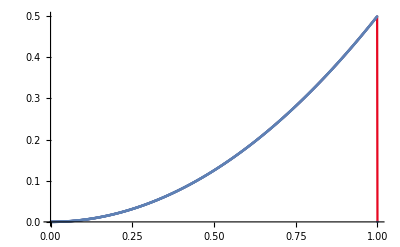
{-Graphics-,-Graphics-}

```mathematica
list={{0,0*10^(0)},{0.001,8.25974*10^(-6)},{0.002,1.65195*10^(-5)},{0.003,2.47792*10^(-5)},{0.004,3.3039*10^(-5)},{0.005,4.12987*10^(-5)},{0.006,4.95585*10^(-5)},{0.007,5.48035*10^(-5)},{0.008,5.90436*10^(-5)},{0.009,6.32837*10^(-5)},{0.01,6.75238*10^(-5)},{0.011,7.17639*10^(-5)},{0.012,7.6004*10^(-5)},{0.013,8.85045*10^(-5)},{0.014,1.09265*10^(-4)},{0.015,1.30025*10^(-4)},{0.016,1.50786*10^(-4)},{0.017,1.71546*10^(-4)},{0.018,1.92306*10^(-4)},{0.019,2.12062*10^(-4)},{0.02,2.28801*10^(-4)},{0.021,2.4554*10^(-4)},{0.022,2.6228*10^(-4)},{0.023,2.79019*10^(-4)},{0.024,2.95759*10^(-4)},{0.025,3.12499*10^(-4)},{0.026,3.4576*10^(-4)},{0.027,3.79021*10^(-4)},{0.028,4.12282*10^(-4)},{0.029,4.45543*10^(-4)},{0.03,4.78804*10^(-4)},{0.031,5.12065*10^(-4)},{0.032,5.42309*10^(-4)},{0.033,5.71548*10^(-4)},{0.034,6.00787*10^(-4)},{0.035,6.30025*10^(-4)},{0.036,6.59264*10^(-4)},{0.037,6.88503*10^(-4)},{0.038,7.26004*10^(-4)},{0.039,7.71765*10^(-4)},{0.04,8.17527*10^(-4)},{0.041,8.63289*10^(-4)},{0.042,9.0905*10^(-4)},{0.043,9.54812*10^(-4)},{0.044,9.99568*10^(-4)},{0.045,1.04131*10^(-3)},{0.046,1.08304*10^(-3)},{0.047,1.12478*10^(-3)},{0.048,1.16652*10^(-3)},{0.049,1.20826*10^(-3)},{0.05,1.25*10^(-3)},{0.051,1.30826*10^(-3)},{0.052,1.36652*10^(-3)},{0.053,1.42478*10^(-3)},{0.054,1.48305*10^(-3)},{0.055,1.54131*10^(-3)},{0.056,1.59957*10^(-3)},{0.057,1.65481*10^(-3)},{0.058,1.70905*10^(-3)},{0.059,1.76329*10^(-3)},{0.06,1.81753*10^(-3)},{0.061,1.87176*10^(-3)},{0.062,1.926*10^(-3)},{0.063,1.9885*10^(-3)},{0.064,2.05927*10^(-3)},{0.065,2.13003*10^(-3)},{0.066,2.20079*10^(-3)},{0.067,2.27155*10^(-3)},{0.068,2.34232*10^(-3)},{0.069,2.41207*10^(-3)},{0.07,2.47881*10^(-3)},{0.071,2.54555*10^(-3)},{0.072,2.61228*10^(-3)},{0.073,2.67902*10^(-3)},{0.074,2.74576*10^(-3)},{0.075,2.8125*10^(-3)},{0.076,2.89576*10^(-3)},{0.077,2.97902*10^(-3)},{0.078,3.06229*10^(-3)},{0.079,3.14555*10^(-3)},{0.08,3.22881*10^(-3)},{0.081,3.31208*10^(-3)},{0.082,3.39232*10^(-3)},{0.083,3.47156*10^(-3)},{0.084,3.55079*10^(-3)},{0.085,3.63003*10^(-3)},{0.086,3.70926*10^(-3)},{0.087,3.7885*10^(-3)},{0.088,3.876*10^(-3)},{0.089,3.97177*10^(-3)},{0.09,4.06753*10^(-3)},{0.091,4.1633*10^(-3)},{0.092,4.25906*10^(-3)},{0.093,4.35482*10^(-3)},{0.094,4.44958*10^(-3)},{0.095,4.54132*10^(-3)},{0.096,4.63305*10^(-3)},{0.097,4.72479*10^(-3)},{0.098,4.81652*10^(-3)},{0.099,4.90826*10^(-3)},{0.1,4.99999*10^(-3)},{0.101,5.10826*10^(-3)},{0.102,5.21652*10^(-3)},{0.103,5.32479*10^(-3)},{0.104,5.43305*10^(-3)},{0.105,5.54132*10^(-3)},{0.106,5.64958*10^(-3)},{0.107,5.75483*10^(-3)},{0.108,5.85906*10^(-3)},{0.109,5.9633*10^(-3)},{0.11,6.06753*10^(-3)},{0.111,6.17176*10^(-3)},{0.112,6.276*10^(-3)},{0.113,6.3885*10^(-3)},{0.114,6.50927*10^(-3)},{0.115,6.63003*10^(-3)},{0.116,6.7508*10^(-3)},{0.117,6.87156*10^(-3)},{0.118,6.99233*10^(-3)},{0.119,7.11209*10^(-3)},{0.12,7.22882*10^(-3)},{0.121,7.34555*10^(-3)},{0.122,7.46229*10^(-3)},{0.123,7.57902*10^(-3)},{0.124,7.69576*10^(-3)},{0.125,7.81249*10^(-3)},{0.126,7.94576*10^(-3)},{0.127,8.07903*10^(-3)},{0.128,8.21229*10^(-3)},{0.129,8.34556*10^(-3)},{0.13,8.47882*10^(-3)},{0.131,8.61209*10^(-3)},{0.132,8.74233*10^(-3)},{0.133,8.87156*10^(-3)},{0.134,9.0008*10^(-3)},{0.135,9.13003*10^(-3)},{0.136,9.25926*10^(-3)},{0.137,9.3885*10^(-3)},{0.138,9.526*10^(-3)},{0.139,9.67177*10^(-3)},{0.14,9.81753*10^(-3)},{0.141,9.9633*10^(-3)},{0.142,1.01091*10^(-2)},{0.143,1.02548*10^(-2)},{0.144,1.03996*10^(-2)},{0.145,1.05413*10^(-2)},{0.146,1.06831*10^(-2)},{0.147,1.08248*10^(-2)},{0.148,1.09665*10^(-2)},{0.149,1.11083*10^(-2)},{0.15,1.125*10^(-2)},{0.151,1.14083*10^(-2)},{0.152,1.15665*10^(-2)},{0.153,1.17248*10^(-2)},{0.154,1.18831*10^(-2)},{0.155,1.20413*10^(-2)},{0.156,1.21996*10^(-2)},{0.157,1.23548*10^(-2)},{0.158,1.25091*10^(-2)},{0.159,1.26633*10^(-2)},{0.16,1.28175*10^(-2)},{0.161,1.29718*10^(-2)},{0.162,1.3126*10^(-2)},{0.163,1.32885*10^(-2)},{0.164,1.34593*10^(-2)},{0.165,1.363*10^(-2)},{0.166,1.38008*10^(-2)},{0.167,1.39716*10^(-2)},{0.168,1.41423*10^(-2)},{0.169,1.43121*10^(-2)},{0.17,1.44788*10^(-2)},{0.171,1.46456*10^(-2)},{0.172,1.48123*10^(-2)},{0.173,1.4979*10^(-2)},{0.174,1.51458*10^(-2)},{0.175,1.53125*10^(-2)},{0.176,1.54958*10^(-2)},{0.177,1.5679*10^(-2)},{0.178,1.58623*10^(-2)},{0.179,1.60456*10^(-2)},{0.18,1.62288*10^(-2)},{0.181,1.64121*10^(-2)},{0.182,1.65923*10^(-2)},{0.183,1.67716*10^(-2)},{0.184,1.69508*10^(-2)},{0.185,1.713*10^(-2)},{0.186,1.73093*10^(-2)},{0.187,1.74885*10^(-2)},{0.188,1.7676*10^(-2)},{0.189,1.78718*10^(-2)},{0.19,1.80675*10^(-2)},{0.191,1.82633*10^(-2)},{0.192,1.84591*10^(-2)},{0.193,1.86548*10^(-2)},{0.194,1.88496*10^(-2)},{0.195,1.90413*10^(-2)},{0.196,1.92331*10^(-2)},{0.197,1.94248*10^(-2)},{0.198,1.96165*10^(-2)},{0.199,1.98083*10^(-2)},{0.2,2*10^(-2)},{0.201,2.02083*10^(-2)},{0.202,2.04165*10^(-2)},{0.203,2.06248*10^(-2)},{0.204,2.08331*10^(-2)},{0.205,2.10413*10^(-2)},{0.206,2.12496*10^(-2)},{0.207,2.14548*10^(-2)},{0.208,2.16591*10^(-2)},{0.209,2.18633*10^(-2)},{0.21,2.20675*10^(-2)},{0.211,2.22718*10^(-2)},{0.212,2.2476*10^(-2)},{0.213,2.26885*10^(-2)},{0.214,2.29093*10^(-2)},{0.215,2.313*10^(-2)},{0.216,2.33508*10^(-2)},{0.217,2.35716*10^(-2)},{0.218,2.37924*10^(-2)},{0.219,2.40121*10^(-2)},{0.22,2.42288*10^(-2)},{0.221,2.44456*10^(-2)},{0.222,2.46623*10^(-2)},{0.223,2.4879*10^(-2)},{0.224,2.50958*10^(-2)},{0.225,2.53125*10^(-2)},{0.226,2.55458*10^(-2)},{0.227,2.5779*10^(-2)},{0.228,2.60123*10^(-2)},{0.229,2.62456*10^(-2)},{0.23,2.64788*10^(-2)},{0.231,2.67121*10^(-2)},{0.232,2.69424*10^(-2)},{0.233,2.71716*10^(-2)},{0.234,2.74008*10^(-2)},{0.235,2.763*10^(-2)},{0.236,2.78593*10^(-2)},{0.237,2.80885*10^(-2)},{0.238,2.8326*10^(-2)},{0.239,2.85718*10^(-2)},{0.24,2.88175*10^(-2)},{0.241,2.90633*10^(-2)},{0.242,2.93091*10^(-2)},{0.243,2.95549*10^(-2)},{0.244,2.97996*10^(-2)},{0.245,3.00413*10^(-2)},{0.246,3.02831*10^(-2)},{0.247,3.05248*10^(-2)},{0.248,3.07665*10^(-2)},{0.249,3.10083*10^(-2)},{0.25,3.125*10^(-2)},{0.251,3.15083*10^(-2)},{0.252,3.17665*10^(-2)},{0.253,3.20248*10^(-2)},{0.254,3.22831*10^(-2)},{0.255,3.25413*10^(-2)},{0.256,3.27996*10^(-2)},{0.257,3.30549*10^(-2)},{0.258,3.33091*10^(-2)},{0.259,3.35633*10^(-2)},{0.26,3.38175*10^(-2)},{0.261,3.40718*10^(-2)},{0.262,3.4326*10^(-2)},{0.263,3.45885*10^(-2)},{0.264,3.48593*10^(-2)},{0.265,3.513*10^(-2)},{0.266,3.54008*10^(-2)},{0.267,3.56716*10^(-2)},{0.268,3.59424*10^(-2)},{0.269,3.62121*10^(-2)},{0.27,3.64788*10^(-2)},{0.271,3.67456*10^(-2)},{0.272,3.70123*10^(-2)},{0.273,3.7279*10^(-2)},{0.274,3.75458*10^(-2)},{0.275,3.78125*10^(-2)},{0.276,3.80958*10^(-2)},{0.277,3.8379*10^(-2)},{0.278,3.86623*10^(-2)},{0.279,3.89456*10^(-2)},{0.28,3.92289*10^(-2)},{0.281,3.95121*10^(-2)},{0.282,3.97924*10^(-2)},{0.283,4.00716*10^(-2)},{0.284,4.03508*10^(-2)},{0.285,4.063*10^(-2)},{0.286,4.09093*10^(-2)},{0.287,4.11885*10^(-2)},{0.288,4.1476*10^(-2)},{0.289,4.17718*10^(-2)},{0.29,4.20675*10^(-2)},{0.291,4.23633*10^(-2)},{0.292,4.26591*10^(-2)},{0.293,4.29549*10^(-2)},{0.294,4.32496*10^(-2)},{0.295,4.35414*10^(-2)},{0.296,4.38331*10^(-2)},{0.297,4.41248*10^(-2)},{0.298,4.44165*10^(-2)},{0.299,4.47083*10^(-2)},{0.3,4.5*10^(-2)},{0.301,4.53083*10^(-2)},{0.302,4.56165*10^(-2)},{0.303,4.59248*10^(-2)},{0.304,4.62331*10^(-2)},{0.305,4.65414*10^(-2)},{0.306,4.68496*10^(-2)},{0.307,4.71549*10^(-2)},{0.308,4.74591*10^(-2)},{0.309,4.77633*10^(-2)},{0.31,4.80675*10^(-2)},{0.311,4.83718*10^(-2)},{0.312,4.8676*10^(-2)},{0.313,4.89885*10^(-2)},{0.314,4.93093*10^(-2)},{0.315,4.963*10^(-2)},{0.316,4.99508*10^(-2)},{0.317,5.02716*10^(-2)},{0.318,5.05924*10^(-2)},{0.319,5.09121*10^(-2)},{0.32,5.12289*10^(-2)},{0.321,5.15456*10^(-2)},{0.322,5.18623*10^(-2)},{0.323,5.2179*10^(-2)},{0.324,5.24958*10^(-2)},{0.325,5.28125*10^(-2)},{0.326,5.31458*10^(-2)},{0.327,5.3479*10^(-2)},{0.328,5.38123*10^(-2)},{0.329,5.41456*10^(-2)},{0.33,5.44789*10^(-2)},{0.331,5.48121*10^(-2)},{0.332,5.51424*10^(-2)},{0.333,5.54716*10^(-2)},{0.334,5.58008*10^(-2)},{0.335,5.613*10^(-2)},{0.336,5.64593*10^(-2)},{0.337,5.67885*10^(-2)},{0.338,5.7126*10^(-2)},{0.339,5.74718*10^(-2)},{0.34,5.78175*10^(-2)},{0.341,5.81633*10^(-2)},{0.342,5.85091*10^(-2)},{0.343,5.88549*10^(-2)},{0.344,5.91996*10^(-2)},{0.345,5.95414*10^(-2)},{0.346,5.98831*10^(-2)},{0.347,6.02248*10^(-2)},{0.348,6.05665*10^(-2)},{0.349,6.09083*10^(-2)},{0.35,6.125*10^(-2)},{0.351,6.16083*10^(-2)},{0.352,6.19665*10^(-2)},{0.353,6.23248*10^(-2)},{0.354,6.26831*10^(-2)},{0.355,6.30414*10^(-2)},{0.356,6.33996*10^(-2)},{0.357,6.37549*10^(-2)},{0.358,6.41091*10^(-2)},{0.359,6.44633*10^(-2)},{0.36,6.48175*10^(-2)},{0.361,6.51718*10^(-2)},{0.362,6.5526*10^(-2)},{0.363,6.58885*10^(-2)},{0.364,6.62593*10^(-2)},{0.365,6.66301*10^(-2)},{0.366,6.70008*10^(-2)},{0.367,6.73716*10^(-2)},{0.368,6.77424*10^(-2)},{0.369,6.81121*10^(-2)},{0.37,6.84789*10^(-2)},{0.371,6.88456*10^(-2)},{0.372,6.92123*10^(-2)},{0.373,6.9579*10^(-2)},{0.374,6.99458*10^(-2)},{0.375,7.03125*10^(-2)},{0.376,7.06958*10^(-2)},{0.377,7.1079*10^(-2)},{0.378,7.14623*10^(-2)},{0.379,7.18456*10^(-2)},{0.38,7.22289*10^(-2)},{0.381,7.26122*10^(-2)},{0.382,7.29924*10^(-2)},{0.383,7.33716*10^(-2)},{0.384,7.37508*10^(-2)},{0.385,7.413*10^(-2)},{0.386,7.45093*10^(-2)},{0.387,7.48885*10^(-2)},{0.388,7.5276*10^(-2)},{0.389,7.56718*10^(-2)},{0.39,7.60676*10^(-2)},{0.391,7.64633*10^(-2)},{0.392,7.68591*10^(-2)},{0.393,7.72549*10^(-2)},{0.394,7.76497*10^(-2)},{0.395,7.80414*10^(-2)},{0.396,7.84331*10^(-2)},{0.397,7.88248*10^(-2)},{0.398,7.92165*10^(-2)},{0.399,7.96083*10^(-2)},{0.4,8*10^(-2)},{0.401,8.04083*10^(-2)},{0.402,8.08165*10^(-2)},{0.403,8.12248*10^(-2)},{0.404,8.16331*10^(-2)},{0.405,8.20414*10^(-2)},{0.406,8.24497*10^(-2)},{0.407,8.28549*10^(-2)},{0.408,8.32591*10^(-2)},{0.409,8.36633*10^(-2)},{0.41,8.40675*10^(-2)},{0.411,8.44718*10^(-2)},{0.412,8.4876*10^(-2)},{0.413,8.52885*10^(-2)},{0.414,8.57093*10^(-2)},{0.415,8.61301*10^(-2)},{0.416,8.65508*10^(-2)},{0.417,8.69716*10^(-2)},{0.418,8.73924*10^(-2)},{0.419,8.78122*10^(-2)},{0.42,8.82289*10^(-2)},{0.421,8.86456*10^(-2)},{0.422,8.90623*10^(-2)},{0.423,8.9479*10^(-2)},{0.424,8.98958*10^(-2)},{0.425,9.03125*10^(-2)},{0.426,9.07458*10^(-2)},{0.427,9.1179*10^(-2)},{0.428,9.16123*10^(-2)},{0.429,9.20456*10^(-2)},{0.43,9.24789*10^(-2)},{0.431,9.29122*10^(-2)},{0.432,9.33424*10^(-2)},{0.433,9.37716*10^(-2)},{0.434,9.42008*10^(-2)},{0.435,9.463*10^(-2)},{0.436,9.50593*10^(-2)},{0.437,9.54885*10^(-2)},{0.438,9.5926*10^(-2)},{0.439,9.63718*10^(-2)},{0.44,9.68176*10^(-2)},{0.441,9.72633*10^(-2)},{0.442,9.77091*10^(-2)},{0.443,9.81549*10^(-2)},{0.444,9.85997*10^(-2)},{0.445,9.90414*10^(-2)},{0.446,9.94831*10^(-2)},{0.447,9.99248*10^(-2)},{0.448,1.00367*10^(-1)},{0.449,1.00808*10^(-1)},{0.45,1.0125*10^(-1)},{0.451,1.01708*10^(-1)},{0.452,1.02167*10^(-1)},{0.453,1.02625*10^(-1)},{0.454,1.03083*10^(-1)},{0.455,1.03541*10^(-1)},{0.456,1.04*10^(-1)},{0.457,1.04455*10^(-1)},{0.458,1.04909*10^(-1)},{0.459,1.05363*10^(-1)},{0.46,1.05818*10^(-1)},{0.461,1.06272*10^(-1)},{0.462,1.06726*10^(-1)},{0.463,1.07188*10^(-1)},{0.464,1.07659*10^(-1)},{0.465,1.0813*10^(-1)},{0.466,1.08601*10^(-1)},{0.467,1.09072*10^(-1)},{0.468,1.09542*10^(-1)},{0.469,1.10012*10^(-1)},{0.47,1.10479*10^(-1)},{0.471,1.10946*10^(-1)},{0.472,1.11412*10^(-1)},{0.473,1.11879*10^(-1)},{0.474,1.12346*10^(-1)},{0.475,1.12812*10^(-1)},{0.476,1.13296*10^(-1)},{0.477,1.13779*10^(-1)},{0.478,1.14262*10^(-1)},{0.479,1.14746*10^(-1)},{0.48,1.15229*10^(-1)},{0.481,1.15712*10^(-1)},{0.482,1.16192*10^(-1)},{0.483,1.16672*10^(-1)},{0.484,1.17151*10^(-1)},{0.485,1.1763*10^(-1)},{0.486,1.18109*10^(-1)},{0.487,1.18588*10^(-1)},{0.488,1.19076*10^(-1)},{0.489,1.19572*10^(-1)},{0.49,1.20068*10^(-1)},{0.491,1.20563*10^(-1)},{0.492,1.21059*10^(-1)},{0.493,1.21555*10^(-1)},{0.494,1.2205*10^(-1)},{0.495,1.22541*10^(-1)},{0.496,1.23033*10^(-1)},{0.497,1.23525*10^(-1)},{0.498,1.24017*10^(-1)},{0.499,1.24508*10^(-1)},{0.5,1.25*10^(-1)},{0.501,1.25508*10^(-1)},{0.502,1.26017*10^(-1)},{0.503,1.26525*10^(-1)},{0.504,1.27033*10^(-1)},{0.505,1.27541*10^(-1)},{0.506,1.2805*10^(-1)},{0.507,1.28555*10^(-1)},{0.508,1.29059*10^(-1)},{0.509,1.29563*10^(-1)},{0.51,1.30068*10^(-1)},{0.511,1.30572*10^(-1)},{0.512,1.31076*10^(-1)},{0.513,1.31588*10^(-1)},{0.514,1.32109*10^(-1)},{0.515,1.3263*10^(-1)},{0.516,1.33151*10^(-1)},{0.517,1.33672*10^(-1)},{0.518,1.34192*10^(-1)},{0.519,1.34712*10^(-1)},{0.52,1.35229*10^(-1)},{0.521,1.35746*10^(-1)},{0.522,1.36262*10^(-1)},{0.523,1.36779*10^(-1)},{0.524,1.37296*10^(-1)},{0.525,1.37812*10^(-1)},{0.526,1.38346*10^(-1)},{0.527,1.38879*10^(-1)},{0.528,1.39412*10^(-1)},{0.529,1.39946*10^(-1)},{0.53,1.40479*10^(-1)},{0.531,1.41012*10^(-1)},{0.532,1.41542*10^(-1)},{0.533,1.42072*10^(-1)},{0.534,1.42601*10^(-1)},{0.535,1.4313*10^(-1)},{0.536,1.43659*10^(-1)},{0.537,1.44188*10^(-1)},{0.538,1.44726*10^(-1)},{0.539,1.45272*10^(-1)},{0.54,1.45818*10^(-1)},{0.541,1.46363*10^(-1)},{0.542,1.46909*10^(-1)},{0.543,1.47455*10^(-1)},{0.544,1.48*10^(-1)},{0.545,1.48541*10^(-1)},{0.546,1.49083*10^(-1)},{0.547,1.49625*10^(-1)},{0.548,1.50167*10^(-1)},{0.549,1.50708*10^(-1)},{0.55,1.5125*10^(-1)},{0.551,1.51808*10^(-1)},{0.552,1.52367*10^(-1)},{0.553,1.52925*10^(-1)},{0.554,1.53483*10^(-1)},{0.555,1.54041*10^(-1)},{0.556,1.546*10^(-1)},{0.557,1.55155*10^(-1)},{0.558,1.55709*10^(-1)},{0.559,1.56263*10^(-1)},{0.56,1.56818*10^(-1)},{0.561,1.57372*10^(-1)},{0.562,1.57926*10^(-1)},{0.563,1.58488*10^(-1)},{0.564,1.59059*10^(-1)},{0.565,1.5963*10^(-1)},{0.566,1.60201*10^(-1)},{0.567,1.60772*10^(-1)},{0.568,1.61342*10^(-1)},{0.569,1.61912*10^(-1)},{0.57,1.62479*10^(-1)},{0.571,1.63046*10^(-1)},{0.572,1.63612*10^(-1)},{0.573,1.64179*10^(-1)},{0.574,1.64746*10^(-1)},{0.575,1.65312*10^(-1)},{0.576,1.65896*10^(-1)},{0.577,1.66479*10^(-1)},{0.578,1.67062*10^(-1)},{0.579,1.67646*10^(-1)},{0.58,1.68229*10^(-1)},{0.581,1.68812*10^(-1)},{0.582,1.69392*10^(-1)},{0.583,1.69972*10^(-1)},{0.584,1.70551*10^(-1)},{0.585,1.7113*10^(-1)},{0.586,1.71709*10^(-1)},{0.587,1.72288*10^(-1)},{0.588,1.72876*10^(-1)},{0.589,1.73472*10^(-1)},{0.59,1.74068*10^(-1)},{0.591,1.74663*10^(-1)},{0.592,1.75259*10^(-1)},{0.593,1.75855*10^(-1)},{0.594,1.7645*10^(-1)},{0.595,1.77041*10^(-1)},{0.596,1.77633*10^(-1)},{0.597,1.78225*10^(-1)},{0.598,1.78817*10^(-1)},{0.599,1.79408*10^(-1)},{0.6,1.8*10^(-1)},{0.601,1.80608*10^(-1)},{0.602,1.81217*10^(-1)},{0.603,1.81825*10^(-1)},{0.604,1.82433*10^(-1)},{0.605,1.83041*10^(-1)},{0.606,1.8365*10^(-1)},{0.607,1.84255*10^(-1)},{0.608,1.84859*10^(-1)},{0.609,1.85463*10^(-1)},{0.61,1.86068*10^(-1)},{0.611,1.86672*10^(-1)},{0.612,1.87276*10^(-1)},{0.613,1.87888*10^(-1)},{0.614,1.88509*10^(-1)},{0.615,1.8913*10^(-1)},{0.616,1.89751*10^(-1)},{0.617,1.90372*10^(-1)},{0.618,1.90992*10^(-1)},{0.619,1.91612*10^(-1)},{0.62,1.92229*10^(-1)},{0.621,1.92846*10^(-1)},{0.622,1.93462*10^(-1)},{0.623,1.94079*10^(-1)},{0.624,1.94696*10^(-1)},{0.625,1.95312*10^(-1)},{0.626,1.95946*10^(-1)},{0.627,1.96579*10^(-1)},{0.628,1.97212*10^(-1)},{0.629,1.97846*10^(-1)},{0.63,1.98479*10^(-1)},{0.631,1.99112*10^(-1)},{0.632,1.99742*10^(-1)},{0.633,2.00372*10^(-1)},{0.634,2.01001*10^(-1)},{0.635,2.0163*10^(-1)},{0.636,2.02259*10^(-1)},{0.637,2.02888*10^(-1)},{0.638,2.03526*10^(-1)},{0.639,2.04172*10^(-1)},{0.64,2.04818*10^(-1)},{0.641,2.05463*10^(-1)},{0.642,2.06109*10^(-1)},{0.643,2.06755*10^(-1)},{0.644,2.074*10^(-1)},{0.645,2.08041*10^(-1)},{0.646,2.08683*10^(-1)},{0.647,2.09325*10^(-1)},{0.648,2.09967*10^(-1)},{0.649,2.10608*10^(-1)},{0.65,2.1125*10^(-1)},{0.651,2.11908*10^(-1)},{0.652,2.12567*10^(-1)},{0.653,2.13225*10^(-1)},{0.654,2.13883*10^(-1)},{0.655,2.14541*10^(-1)},{0.656,2.152*10^(-1)},{0.657,2.15855*10^(-1)},{0.658,2.16509*10^(-1)},{0.659,2.17163*10^(-1)},{0.66,2.17818*10^(-1)},{0.661,2.18472*10^(-1)},{0.662,2.19126*10^(-1)},{0.663,2.19788*10^(-1)},{0.664,2.20459*10^(-1)},{0.665,2.2113*10^(-1)},{0.666,2.21801*10^(-1)},{0.667,2.22472*10^(-1)},{0.668,2.23142*10^(-1)},{0.669,2.23812*10^(-1)},{0.67,2.24479*10^(-1)},{0.671,2.25146*10^(-1)},{0.672,2.25812*10^(-1)},{0.673,2.26479*10^(-1)},{0.674,2.27146*10^(-1)},{0.675,2.27812*10^(-1)},{0.676,2.28496*10^(-1)},{0.677,2.29179*10^(-1)},{0.678,2.29862*10^(-1)},{0.679,2.30546*10^(-1)},{0.68,2.31229*10^(-1)},{0.681,2.31912*10^(-1)},{0.682,2.32592*10^(-1)},{0.683,2.33272*10^(-1)},{0.684,2.33951*10^(-1)},{0.685,2.3463*10^(-1)},{0.686,2.35309*10^(-1)},{0.687,2.35988*10^(-1)},{0.688,2.36676*10^(-1)},{0.689,2.37372*10^(-1)},{0.69,2.38068*10^(-1)},{0.691,2.38763*10^(-1)},{0.692,2.39459*10^(-1)},{0.693,2.40155*10^(-1)},{0.694,2.4085*10^(-1)},{0.695,2.41541*10^(-1)},{0.696,2.42233*10^(-1)},{0.697,2.42925*10^(-1)},{0.698,2.43617*10^(-1)},{0.699,2.44308*10^(-1)},{0.7,2.45*10^(-1)},{0.701,2.45708*10^(-1)},{0.702,2.46417*10^(-1)},{0.703,2.47125*10^(-1)},{0.704,2.47833*10^(-1)},{0.705,2.48541*10^(-1)},{0.706,2.4925*10^(-1)},{0.707,2.49955*10^(-1)},{0.708,2.50659*10^(-1)},{0.709,2.51363*10^(-1)},{0.71,2.52068*10^(-1)},{0.711,2.52772*10^(-1)},{0.712,2.53476*10^(-1)},{0.713,2.54188*10^(-1)},{0.714,2.54909*10^(-1)},{0.715,2.5563*10^(-1)},{0.716,2.56351*10^(-1)},{0.717,2.57072*10^(-1)},{0.718,2.57792*10^(-1)},{0.719,2.58512*10^(-1)},{0.72,2.59229*10^(-1)},{0.721,2.59946*10^(-1)},{0.722,2.60662*10^(-1)},{0.723,2.61379*10^(-1)},{0.724,2.62096*10^(-1)},{0.725,2.62812*10^(-1)},{0.726,2.63546*10^(-1)},{0.727,2.64279*10^(-1)},{0.728,2.65012*10^(-1)},{0.729,2.65746*10^(-1)},{0.73,2.66479*10^(-1)},{0.731,2.67212*10^(-1)},{0.732,2.67942*10^(-1)},{0.733,2.68672*10^(-1)},{0.734,2.69401*10^(-1)},{0.735,2.7013*10^(-1)},{0.736,2.70859*10^(-1)},{0.737,2.71588*10^(-1)},{0.738,2.72326*10^(-1)},{0.739,2.73072*10^(-1)},{0.74,2.73818*10^(-1)},{0.741,2.74563*10^(-1)},{0.742,2.75309*10^(-1)},{0.743,2.76055*10^(-1)},{0.744,2.768*10^(-1)},{0.745,2.77541*10^(-1)},{0.746,2.78283*10^(-1)},{0.747,2.79025*10^(-1)},{0.748,2.79767*10^(-1)},{0.749,2.80508*10^(-1)},{0.75,2.8125*10^(-1)},{0.751,2.82008*10^(-1)},{0.752,2.82767*10^(-1)},{0.753,2.83525*10^(-1)},{0.754,2.84283*10^(-1)},{0.755,2.85041*10^(-1)},{0.756,2.858*10^(-1)},{0.757,2.86555*10^(-1)},{0.758,2.87309*10^(-1)},{0.759,2.88063*10^(-1)},{0.76,2.88818*10^(-1)},{0.761,2.89572*10^(-1)},{0.762,2.90326*10^(-1)},{0.763,2.91088*10^(-1)},{0.764,2.91859*10^(-1)},{0.765,2.9263*10^(-1)},{0.766,2.93401*10^(-1)},{0.767,2.94172*10^(-1)},{0.768,2.94942*10^(-1)},{0.769,2.95712*10^(-1)},{0.77,2.96479*10^(-1)},{0.771,2.97246*10^(-1)},{0.772,2.98012*10^(-1)},{0.773,2.98779*10^(-1)},{0.774,2.99546*10^(-1)},{0.775,3.00312*10^(-1)},{0.776,3.01096*10^(-1)},{0.777,3.01879*10^(-1)},{0.778,3.02662*10^(-1)},{0.779,3.03446*10^(-1)},{0.78,3.04229*10^(-1)},{0.781,3.05012*10^(-1)},{0.782,3.05792*10^(-1)},{0.783,3.06572*10^(-1)},{0.784,3.07351*10^(-1)},{0.785,3.0813*10^(-1)},{0.786,3.08909*10^(-1)},{0.787,3.09688*10^(-1)},{0.788,3.10476*10^(-1)},{0.789,3.11272*10^(-1)},{0.79,3.12068*10^(-1)},{0.791,3.12863*10^(-1)},{0.792,3.13659*10^(-1)},{0.793,3.14455*10^(-1)},{0.794,3.1525*10^(-1)},{0.795,3.16041*10^(-1)},{0.796,3.16833*10^(-1)},{0.797,3.17625*10^(-1)},{0.798,3.18417*10^(-1)},{0.799,3.19208*10^(-1)},{0.8,3.2*10^(-1)},{0.801,3.20808*10^(-1)},{0.802,3.21617*10^(-1)},{0.803,3.22425*10^(-1)},{0.804,3.23233*10^(-1)},{0.805,3.24041*10^(-1)},{0.806,3.2485*10^(-1)},{0.807,3.25655*10^(-1)},{0.808,3.26459*10^(-1)},{0.809,3.27263*10^(-1)},{0.81,3.28068*10^(-1)},{0.811,3.28872*10^(-1)},{0.812,3.29676*10^(-1)},{0.813,3.30488*10^(-1)},{0.814,3.31309*10^(-1)},{0.815,3.3213*10^(-1)},{0.816,3.32951*10^(-1)},{0.817,3.33772*10^(-1)},{0.818,3.34592*10^(-1)},{0.819,3.35412*10^(-1)},{0.82,3.36229*10^(-1)},{0.821,3.37046*10^(-1)},{0.822,3.37862*10^(-1)},{0.823,3.38679*10^(-1)},{0.824,3.39496*10^(-1)},{0.825,3.40312*10^(-1)},{0.826,3.41146*10^(-1)},{0.827,3.41979*10^(-1)},{0.828,3.42812*10^(-1)},{0.829,3.43646*10^(-1)},{0.83,3.44479*10^(-1)},{0.831,3.45312*10^(-1)},{0.832,3.46142*10^(-1)},{0.833,3.46972*10^(-1)},{0.834,3.47801*10^(-1)},{0.835,3.4863*10^(-1)},{0.836,3.49459*10^(-1)},{0.837,3.50288*10^(-1)},{0.838,3.51126*10^(-1)},{0.839,3.51972*10^(-1)},{0.84,3.52818*10^(-1)},{0.841,3.53663*10^(-1)},{0.842,3.54509*10^(-1)},{0.843,3.55355*10^(-1)},{0.844,3.562*10^(-1)},{0.845,3.57041*10^(-1)},{0.846,3.57883*10^(-1)},{0.847,3.58725*10^(-1)},{0.848,3.59567*10^(-1)},{0.849,3.60408*10^(-1)},{0.85,3.6125*10^(-1)},{0.851,3.62108*10^(-1)},{0.852,3.62967*10^(-1)},{0.853,3.63825*10^(-1)},{0.854,3.64683*10^(-1)},{0.855,3.65541*10^(-1)},{0.856,3.664*10^(-1)},{0.857,3.67255*10^(-1)},{0.858,3.68109*10^(-1)},{0.859,3.68963*10^(-1)},{0.86,3.69818*10^(-1)},{0.861,3.70672*10^(-1)},{0.862,3.71526*10^(-1)},{0.863,3.72388*10^(-1)},{0.864,3.73259*10^(-1)},{0.865,3.7413*10^(-1)},{0.866,3.75001*10^(-1)},{0.867,3.75872*10^(-1)},{0.868,3.76743*10^(-1)},{0.869,3.77612*10^(-1)},{0.87,3.78479*10^(-1)},{0.871,3.79346*10^(-1)},{0.872,3.80212*10^(-1)},{0.873,3.81079*10^(-1)},{0.874,3.81946*10^(-1)},{0.875,3.82812*10^(-1)},{0.876,3.83696*10^(-1)},{0.877,3.84579*10^(-1)},{0.878,3.85462*10^(-1)},{0.879,3.86346*10^(-1)},{0.88,3.87229*10^(-1)},{0.881,3.88112*10^(-1)},{0.882,3.88992*10^(-1)},{0.883,3.89872*10^(-1)},{0.884,3.90751*10^(-1)},{0.885,3.9163*10^(-1)},{0.886,3.92509*10^(-1)},{0.887,3.93388*10^(-1)},{0.888,3.94276*10^(-1)},{0.889,3.95172*10^(-1)},{0.89,3.96068*10^(-1)},{0.891,3.96963*10^(-1)},{0.892,3.97859*10^(-1)},{0.893,3.98755*10^(-1)},{0.894,3.9965*10^(-1)},{0.895,4.00541*10^(-1)},{0.896,4.01433*10^(-1)},{0.897,4.02325*10^(-1)},{0.898,4.03217*10^(-1)},{0.899,4.04108*10^(-1)},{0.9,4.05*10^(-1)},{0.901,4.05908*10^(-1)},{0.902,4.06817*10^(-1)},{0.903,4.07725*10^(-1)},{0.904,4.08633*10^(-1)},{0.905,4.09541*10^(-1)},{0.906,4.1045*10^(-1)},{0.907,4.11355*10^(-1)},{0.908,4.12259*10^(-1)},{0.909,4.13163*10^(-1)},{0.91,4.14068*10^(-1)},{0.911,4.14972*10^(-1)},{0.912,4.15876*10^(-1)},{0.913,4.16788*10^(-1)},{0.914,4.17709*10^(-1)},{0.915,4.1863*10^(-1)},{0.916,4.19551*10^(-1)},{0.917,4.20472*10^(-1)},{0.918,4.21393*10^(-1)},{0.919,4.22312*10^(-1)},{0.92,4.23229*10^(-1)},{0.921,4.24146*10^(-1)},{0.922,4.25062*10^(-1)},{0.923,4.25979*10^(-1)},{0.924,4.26896*10^(-1)},{0.925,4.27812*10^(-1)},{0.926,4.28746*10^(-1)},{0.927,4.29679*10^(-1)},{0.928,4.30612*10^(-1)},{0.929,4.31546*10^(-1)},{0.93,4.32479*10^(-1)},{0.931,4.33412*10^(-1)},{0.932,4.34343*10^(-1)},{0.933,4.35272*10^(-1)},{0.934,4.36201*10^(-1)},{0.935,4.3713*10^(-1)},{0.936,4.38059*10^(-1)},{0.937,4.38988*10^(-1)},{0.938,4.39926*10^(-1)},{0.939,4.40872*10^(-1)},{0.94,4.41818*10^(-1)},{0.941,4.42763*10^(-1)},{0.942,4.43709*10^(-1)},{0.943,4.44655*10^(-1)},{0.944,4.456*10^(-1)},{0.945,4.46541*10^(-1)},{0.946,4.47483*10^(-1)},{0.947,4.48425*10^(-1)},{0.948,4.49367*10^(-1)},{0.949,4.50308*10^(-1)},{0.95,4.5125*10^(-1)},{0.951,4.52208*10^(-1)},{0.952,4.53167*10^(-1)},{0.953,4.54125*10^(-1)},{0.954,4.55083*10^(-1)},{0.955,4.56041*10^(-1)},{0.956,4.57*10^(-1)},{0.957,4.57955*10^(-1)},{0.958,4.58909*10^(-1)},{0.959,4.59863*10^(-1)},{0.96,4.60818*10^(-1)},{0.961,4.61772*10^(-1)},{0.962,4.62726*10^(-1)},{0.963,4.63688*10^(-1)},{0.964,4.64659*10^(-1)},{0.965,4.6563*10^(-1)},{0.966,4.66601*10^(-1)},{0.967,4.67572*10^(-1)},{0.968,4.68543*10^(-1)},{0.969,4.69512*10^(-1)},{0.97,4.70479*10^(-1)},{0.971,4.71446*10^(-1)},{0.972,4.72412*10^(-1)},{0.973,4.73379*10^(-1)},{0.974,4.74346*10^(-1)},{0.975,4.75312*10^(-1)},{0.976,4.76296*10^(-1)},{0.977,4.77279*10^(-1)},{0.978,4.78262*10^(-1)},{0.979,4.79246*10^(-1)},{0.98,4.80229*10^(-1)},{0.981,4.81212*10^(-1)},{0.982,4.82193*10^(-1)},{0.983,4.83172*10^(-1)},{0.984,4.84151*10^(-1)},{0.985,4.8513*10^(-1)},{0.986,4.86109*10^(-1)},{0.987,4.87088*10^(-1)},{0.988,4.88076*10^(-1)},{0.989,4.89072*10^(-1)},{0.99,4.90068*10^(-1)},{0.991,4.91063*10^(-1)},{0.992,4.92059*10^(-1)},{0.993,4.93055*10^(-1)},{0.994,4.9405*10^(-1)},{0.995,4.95041*10^(-1)},{0.996,4.96033*10^(-1)},{0.997,4.97025*10^(-1)},{0.998,4.98017*10^(-1)},{0.999,4.99008*10^(-1)},{1,0*10^(0)}};
imgtemp=ListPlot[list];
maxerror[[5,1]]=Max[tablereal[[All,2]]-list[[All,2]]];
{img,Show[img,imgtemp]}
```

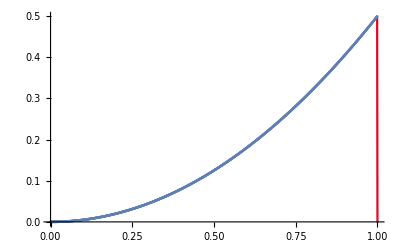
{-Graphics-,-Graphics-}

```mathematica
list={{0,0*10^(0)},{0.001,4.0587*10^(-6)},{0.002,8.1174*10^(-6)},{0.003,1.21761*10^(-5)},{0.004,1.46007*10^(-5)},{0.005,1.67919*10^(-5)},{0.006,1.89831*10^(-5)},{0.007,2.72629*10^(-5)},{0.008,3.75722*10^(-5)},{0.009,4.78816*10^(-5)},{0.01,5.70229*10^(-5)},{0.011,6.54634*10^(-5)},{0.012,7.39039*10^(-5)},{0.013,8.64043*10^(-5)},{0.014,1.02964*10^(-4)},{0.015,1.19524*10^(-4)},{0.016,1.35383*10^(-4)},{0.017,1.50073*10^(-4)},{0.018,1.64763*10^(-4)},{0.019,1.81483*10^(-4)},{0.02,2.04293*10^(-4)},{0.021,2.27104*10^(-4)},{0.022,2.49681*10^(-4)},{0.023,2.7062*10^(-4)},{0.024,2.91559*10^(-4)},{0.025,3.12499*10^(-4)},{0.026,3.4156*10^(-4)},{0.027,3.70621*10^(-4)},{0.028,3.99682*10^(-4)},{0.029,4.27105*10^(-4)},{0.03,4.54293*10^(-4)},{0.031,4.81482*10^(-4)},{0.032,5.14763*10^(-4)},{0.033,5.50075*10^(-4)},{0.034,5.85387*10^(-4)},{0.035,6.19528*10^(-4)},{0.036,6.52966*10^(-4)},{0.037,6.86404*10^(-4)},{0.038,7.23904*10^(-4)},{0.039,7.65467*10^(-4)},{0.04,8.07029*10^(-4)},{0.041,8.47888*10^(-4)},{0.042,8.87576*10^(-4)},{0.043,9.27263*10^(-4)},{0.044,9.68982*10^(-4)},{0.045,1.0168*10^(-3)},{0.046,1.06461*10^(-3)},{0.047,1.11219*10^(-3)},{0.048,1.15812*10^(-3)},{0.049,1.20406*10^(-3)},{0.05,1.25*10^(-3)},{0.051,1.30406*10^(-3)},{0.052,1.35812*10^(-3)},{0.053,1.41219*10^(-3)},{0.054,1.46461*10^(-3)},{0.055,1.5168*10^(-3)},{0.056,1.56898*10^(-3)},{0.057,1.62726*10^(-3)},{0.058,1.68758*10^(-3)},{0.059,1.74789*10^(-3)},{0.06,1.80703*10^(-3)},{0.061,1.86547*10^(-3)},{0.062,1.9239*10^(-3)},{0.063,1.9864*10^(-3)},{0.064,2.05297*10^(-3)},{0.065,2.11953*10^(-3)},{0.066,2.18539*10^(-3)},{0.067,2.25008*10^(-3)},{0.068,2.31476*10^(-3)},{0.069,2.38148*10^(-3)},{0.07,2.4543*10^(-3)},{0.071,2.52711*10^(-3)},{0.072,2.59969*10^(-3)},{0.073,2.67063*10^(-3)},{0.074,2.74156*10^(-3)},{0.075,2.8125*10^(-3)},{0.076,2.89156*10^(-3)},{0.077,2.97063*10^(-3)},{0.078,3.04969*10^(-3)},{0.079,3.12711*10^(-3)},{0.08,3.2043*10^(-3)},{0.081,3.28148*10^(-3)},{0.082,3.36476*10^(-3)},{0.083,3.45008*10^(-3)},{0.084,3.5354*10^(-3)},{0.085,3.61954*10^(-3)},{0.086,3.70297*10^(-3)},{0.087,3.7864*10^(-3)},{0.088,3.8739*10^(-3)},{0.089,3.96547*10^(-3)},{0.09,4.05704*10^(-3)},{0.091,4.1479*10^(-3)},{0.092,4.23758*10^(-3)},{0.093,4.32726*10^(-3)},{0.094,4.41898*10^(-3)},{0.095,4.5168*10^(-3)},{0.096,4.61462*10^(-3)},{0.097,4.7122*10^(-3)},{0.098,4.80813*10^(-3)},{0.099,4.90406*10^(-3)},{0.1,4.99999*10^(-3)},{0.101,5.10406*10^(-3)},{0.102,5.20813*10^(-3)},{0.103,5.3122*10^(-3)},{0.104,5.41462*10^(-3)},{0.105,5.5168*10^(-3)},{0.106,5.61898*10^(-3)},{0.107,5.72726*10^(-3)},{0.108,5.83758*10^(-3)},{0.109,5.9479*10^(-3)},{0.11,6.05704*10^(-3)},{0.111,6.16547*10^(-3)},{0.112,6.2739*10^(-3)},{0.113,6.3864*10^(-3)},{0.114,6.50297*10^(-3)},{0.115,6.61954*10^(-3)},{0.116,6.7354*10^(-3)},{0.117,6.85008*10^(-3)},{0.118,6.96476*10^(-3)},{0.119,7.08148*10^(-3)},{0.12,7.2043*10^(-3)},{0.121,7.32712*10^(-3)},{0.122,7.44971*10^(-3)},{0.123,7.57063*10^(-3)},{0.124,7.69156*10^(-3)},{0.125,7.81249*10^(-3)},{0.126,7.94156*10^(-3)},{0.127,8.07064*10^(-3)},{0.128,8.19971*10^(-3)},{0.129,8.32712*10^(-3)},{0.13,8.4543*10^(-3)},{0.131,8.58148*10^(-3)},{0.132,8.71477*10^(-3)},{0.133,8.85009*10^(-3)},{0.134,8.98541*10^(-3)},{0.135,9.11955*10^(-3)},{0.136,9.25297*10^(-3)},{0.137,9.3864*10^(-3)},{0.138,9.5239*10^(-3)},{0.139,9.66548*10^(-3)},{0.14,9.80705*10^(-3)},{0.141,9.94791*10^(-3)},{0.142,1.00876*10^(-2)},{0.143,1.02273*10^(-2)},{0.144,1.0369*10^(-2)},{0.145,1.05168*10^(-2)},{0.146,1.06646*10^(-2)},{0.147,1.08122*10^(-2)},{0.148,1.09581*10^(-2)},{0.149,1.11041*10^(-2)},{0.15,1.125*10^(-2)},{0.151,1.14041*10^(-2)},{0.152,1.15581*10^(-2)},{0.153,1.17122*10^(-2)},{0.154,1.18646*10^(-2)},{0.155,1.20168*10^(-2)},{0.156,1.2169*10^(-2)},{0.157,1.23273*10^(-2)},{0.158,1.24876*10^(-2)},{0.159,1.26479*10^(-2)},{0.16,1.28071*10^(-2)},{0.161,1.29655*10^(-2)},{0.162,1.31239*10^(-2)},{0.163,1.32864*10^(-2)},{0.164,1.3453*10^(-2)},{0.165,1.36196*10^(-2)},{0.166,1.37854*10^(-2)},{0.167,1.39501*10^(-2)},{0.168,1.41148*10^(-2)},{0.169,1.42815*10^(-2)},{0.17,1.44543*10^(-2)},{0.171,1.46271*10^(-2)},{0.172,1.47997*10^(-2)},{0.173,1.49706*10^(-2)},{0.174,1.51416*10^(-2)},{0.175,1.53125*10^(-2)},{0.176,1.54916*10^(-2)},{0.177,1.56706*10^(-2)},{0.178,1.58497*10^(-2)},{0.179,1.60271*10^(-2)},{0.18,1.62043*10^(-2)},{0.181,1.63815*10^(-2)},{0.182,1.65648*10^(-2)},{0.183,1.67501*10^(-2)},{0.184,1.69354*10^(-2)},{0.185,1.71196*10^(-2)},{0.186,1.7303*10^(-2)},{0.187,1.74864*10^(-2)},{0.188,1.76739*10^(-2)},{0.189,1.78655*10^(-2)},{0.19,1.80571*10^(-2)},{0.191,1.82479*10^(-2)},{0.192,1.84376*10^(-2)},{0.193,1.86273*10^(-2)},{0.194,1.8819*10^(-2)},{0.195,1.90168*10^(-2)},{0.196,1.92146*10^(-2)},{0.197,1.94122*10^(-2)},{0.198,1.96081*10^(-2)},{0.199,1.98041*10^(-2)},{0.2,2*10^(-2)},{0.201,2.02041*10^(-2)},{0.202,2.04081*10^(-2)},{0.203,2.06122*10^(-2)},{0.204,2.08146*10^(-2)},{0.205,2.10168*10^(-2)},{0.206,2.1219*10^(-2)},{0.207,2.14273*10^(-2)},{0.208,2.16376*10^(-2)},{0.209,2.18479*10^(-2)},{0.21,2.20571*10^(-2)},{0.211,2.22655*10^(-2)},{0.212,2.24739*10^(-2)},{0.213,2.26864*10^(-2)},{0.214,2.2903*10^(-2)},{0.215,2.31196*10^(-2)},{0.216,2.33354*10^(-2)},{0.217,2.35501*10^(-2)},{0.218,2.37648*10^(-2)},{0.219,2.39815*10^(-2)},{0.22,2.42043*10^(-2)},{0.221,2.44271*10^(-2)},{0.222,2.46497*10^(-2)},{0.223,2.48706*10^(-2)},{0.224,2.50916*10^(-2)},{0.225,2.53125*10^(-2)},{0.226,2.55416*10^(-2)},{0.227,2.57707*10^(-2)},{0.228,2.59997*10^(-2)},{0.229,2.62271*10^(-2)},{0.23,2.64543*10^(-2)},{0.231,2.66815*10^(-2)},{0.232,2.69148*10^(-2)},{0.233,2.71501*10^(-2)},{0.234,2.73854*10^(-2)},{0.235,2.76196*10^(-2)},{0.236,2.7853*10^(-2)},{0.237,2.80864*10^(-2)},{0.238,2.83239*10^(-2)},{0.239,2.85655*10^(-2)},{0.24,2.88071*10^(-2)},{0.241,2.90479*10^(-2)},{0.242,2.92876*10^(-2)},{0.243,2.95273*10^(-2)},{0.244,2.9769*10^(-2)},{0.245,3.00168*10^(-2)},{0.246,3.02646*10^(-2)},{0.247,3.05122*10^(-2)},{0.248,3.07582*10^(-2)},{0.249,3.10041*10^(-2)},{0.25,3.125*10^(-2)},{0.251,3.15041*10^(-2)},{0.252,3.17582*10^(-2)},{0.253,3.20122*10^(-2)},{0.254,3.22646*10^(-2)},{0.255,3.25168*10^(-2)},{0.256,3.2769*10^(-2)},{0.257,3.30273*10^(-2)},{0.258,3.32876*10^(-2)},{0.259,3.35479*10^(-2)},{0.26,3.38071*10^(-2)},{0.261,3.40655*10^(-2)},{0.262,3.43239*10^(-2)},{0.263,3.45864*10^(-2)},{0.264,3.4853*10^(-2)},{0.265,3.51196*10^(-2)},{0.266,3.53854*10^(-2)},{0.267,3.56501*10^(-2)},{0.268,3.59148*10^(-2)},{0.269,3.61815*10^(-2)},{0.27,3.64543*10^(-2)},{0.271,3.67271*10^(-2)},{0.272,3.69997*10^(-2)},{0.273,3.72707*10^(-2)},{0.274,3.75416*10^(-2)},{0.275,3.78125*10^(-2)},{0.276,3.80916*10^(-2)},{0.277,3.83707*10^(-2)},{0.278,3.86497*10^(-2)},{0.279,3.89271*10^(-2)},{0.28,3.92043*10^(-2)},{0.281,3.94815*10^(-2)},{0.282,3.97648*10^(-2)},{0.283,4.00501*10^(-2)},{0.284,4.03354*10^(-2)},{0.285,4.06196*10^(-2)},{0.286,4.0903*10^(-2)},{0.287,4.11864*10^(-2)},{0.288,4.14739*10^(-2)},{0.289,4.17655*10^(-2)},{0.29,4.20571*10^(-2)},{0.291,4.23479*10^(-2)},{0.292,4.26376*10^(-2)},{0.293,4.29273*10^(-2)},{0.294,4.3219*10^(-2)},{0.295,4.35168*10^(-2)},{0.296,4.38147*10^(-2)},{0.297,4.41122*10^(-2)},{0.298,4.44082*10^(-2)},{0.299,4.47041*10^(-2)},{0.3,4.5*10^(-2)},{0.301,4.53041*10^(-2)},{0.302,4.56082*10^(-2)},{0.303,4.59123*10^(-2)},{0.304,4.62147*10^(-2)},{0.305,4.65168*10^(-2)},{0.306,4.6819*10^(-2)},{0.307,4.71273*10^(-2)},{0.308,4.74376*10^(-2)},{0.309,4.77479*10^(-2)},{0.31,4.80571*10^(-2)},{0.311,4.83655*10^(-2)},{0.312,4.86739*10^(-2)},{0.313,4.89864*10^(-2)},{0.314,4.9303*10^(-2)},{0.315,4.96196*10^(-2)},{0.316,4.99354*10^(-2)},{0.317,5.02501*10^(-2)},{0.318,5.05648*10^(-2)},{0.319,5.08815*10^(-2)},{0.32,5.12043*10^(-2)},{0.321,5.15272*10^(-2)},{0.322,5.18498*10^(-2)},{0.323,5.21707*10^(-2)},{0.324,5.24916*10^(-2)},{0.325,5.28125*10^(-2)},{0.326,5.31416*10^(-2)},{0.327,5.34707*10^(-2)},{0.328,5.37998*10^(-2)},{0.329,5.41272*10^(-2)},{0.33,5.44543*10^(-2)},{0.331,5.47815*10^(-2)},{0.332,5.51148*10^(-2)},{0.333,5.54501*10^(-2)},{0.334,5.57855*10^(-2)},{0.335,5.61196*10^(-2)},{0.336,5.6453*10^(-2)},{0.337,5.67864*10^(-2)},{0.338,5.71239*10^(-2)},{0.339,5.74655*10^(-2)},{0.34,5.78071*10^(-2)},{0.341,5.8148*10^(-2)},{0.342,5.84876*10^(-2)},{0.343,5.88273*10^(-2)},{0.344,5.9169*10^(-2)},{0.345,5.95168*10^(-2)},{0.346,5.98647*10^(-2)},{0.347,6.02123*10^(-2)},{0.348,6.05582*10^(-2)},{0.349,6.09041*10^(-2)},{0.35,6.125*10^(-2)},{0.351,6.16041*10^(-2)},{0.352,6.19582*10^(-2)},{0.353,6.23123*10^(-2)},{0.354,6.26647*10^(-2)},{0.355,6.30168*10^(-2)},{0.356,6.3369*10^(-2)},{0.357,6.37273*10^(-2)},{0.358,6.40876*10^(-2)},{0.359,6.4448*10^(-2)},{0.36,6.48071*10^(-2)},{0.361,6.51655*10^(-2)},{0.362,6.55239*10^(-2)},{0.363,6.58864*10^(-2)},{0.364,6.6253*10^(-2)},{0.365,6.66196*10^(-2)},{0.366,6.69855*10^(-2)},{0.367,6.73501*10^(-2)},{0.368,6.77148*10^(-2)},{0.369,6.80815*10^(-2)},{0.37,6.84543*10^(-2)},{0.371,6.88272*10^(-2)},{0.372,6.91998*10^(-2)},{0.373,6.95707*10^(-2)},{0.374,6.99416*10^(-2)},{0.375,7.03125*10^(-2)},{0.376,7.06916*10^(-2)},{0.377,7.10707*10^(-2)},{0.378,7.14498*10^(-2)},{0.379,7.18272*10^(-2)},{0.38,7.22043*10^(-2)},{0.381,7.25815*10^(-2)},{0.382,7.29648*10^(-2)},{0.383,7.33501*10^(-2)},{0.384,7.37355*10^(-2)},{0.385,7.41196*10^(-2)},{0.386,7.4503*10^(-2)},{0.387,7.48864*10^(-2)},{0.388,7.52739*10^(-2)},{0.389,7.56655*10^(-2)},{0.39,7.60571*10^(-2)},{0.391,7.6448*10^(-2)},{0.392,7.68376*10^(-2)},{0.393,7.72273*10^(-2)},{0.394,7.7619*10^(-2)},{0.395,7.80168*10^(-2)},{0.396,7.84147*10^(-2)},{0.397,7.88123*10^(-2)},{0.398,7.92082*10^(-2)},{0.399,7.96041*10^(-2)},{0.4,8*10^(-2)},{0.401,8.04041*10^(-2)},{0.402,8.08082*10^(-2)},{0.403,8.12123*10^(-2)},{0.404,8.16147*10^(-2)},{0.405,8.20168*10^(-2)},{0.406,8.2419*10^(-2)},{0.407,8.28273*10^(-2)},{0.408,8.32376*10^(-2)},{0.409,8.3648*10^(-2)},{0.41,8.40571*10^(-2)},{0.411,8.44655*10^(-2)},{0.412,8.48739*10^(-2)},{0.413,8.52864*10^(-2)},{0.414,8.5703*10^(-2)},{0.415,8.61196*10^(-2)},{0.416,8.65355*10^(-2)},{0.417,8.69501*10^(-2)},{0.418,8.73648*10^(-2)},{0.419,8.77815*10^(-2)},{0.42,8.82043*10^(-2)},{0.421,8.86272*10^(-2)},{0.422,8.90498*10^(-2)},{0.423,8.94707*10^(-2)},{0.424,8.98916*10^(-2)},{0.425,9.03125*10^(-2)},{0.426,9.07416*10^(-2)},{0.427,9.11707*10^(-2)},{0.428,9.15998*10^(-2)},{0.429,9.20272*10^(-2)},{0.43,9.24543*10^(-2)},{0.431,9.28815*10^(-2)},{0.432,9.33148*10^(-2)},{0.433,9.37501*10^(-2)},{0.434,9.41855*10^(-2)},{0.435,9.46196*10^(-2)},{0.436,9.5053*10^(-2)},{0.437,9.54864*10^(-2)},{0.438,9.59239*10^(-2)},{0.439,9.63655*10^(-2)},{0.44,9.68071*10^(-2)},{0.441,9.7248*10^(-2)},{0.442,9.76876*10^(-2)},{0.443,9.81273*10^(-2)},{0.444,9.8569*10^(-2)},{0.445,9.90168*10^(-2)},{0.446,9.94647*10^(-2)},{0.447,9.99123*10^(-2)},{0.448,1.00358*10^(-1)},{0.449,1.00804*10^(-1)},{0.45,1.0125*10^(-1)},{0.451,1.01704*10^(-1)},{0.452,1.02158*10^(-1)},{0.453,1.02612*10^(-1)},{0.454,1.03065*10^(-1)},{0.455,1.03517*10^(-1)},{0.456,1.03969*10^(-1)},{0.457,1.04427*10^(-1)},{0.458,1.04888*10^(-1)},{0.459,1.05348*10^(-1)},{0.46,1.05807*10^(-1)},{0.461,1.06266*10^(-1)},{0.462,1.06724*10^(-1)},{0.463,1.07186*10^(-1)},{0.464,1.07653*10^(-1)},{0.465,1.0812*10^(-1)},{0.466,1.08585*10^(-1)},{0.467,1.0905*10^(-1)},{0.468,1.09515*10^(-1)},{0.469,1.09981*10^(-1)},{0.47,1.10454*10^(-1)},{0.471,1.10927*10^(-1)},{0.472,1.114*10^(-1)},{0.473,1.11871*10^(-1)},{0.474,1.12342*10^(-1)},{0.475,1.12812*10^(-1)},{0.476,1.13292*10^(-1)},{0.477,1.13771*10^(-1)},{0.478,1.1425*10^(-1)},{0.479,1.14727*10^(-1)},{0.48,1.15204*10^(-1)},{0.481,1.15681*10^(-1)},{0.482,1.16165*10^(-1)},{0.483,1.1665*10^(-1)},{0.484,1.17135*10^(-1)},{0.485,1.1762*10^(-1)},{0.486,1.18103*10^(-1)},{0.487,1.18586*10^(-1)},{0.488,1.19074*10^(-1)},{0.489,1.19566*10^(-1)},{0.49,1.20057*10^(-1)},{0.491,1.20548*10^(-1)},{0.492,1.21038*10^(-1)},{0.493,1.21527*10^(-1)},{0.494,1.22019*10^(-1)},{0.495,1.22517*10^(-1)},{0.496,1.23015*10^(-1)},{0.497,1.23512*10^(-1)},{0.498,1.24008*10^(-1)},{0.499,1.24504*10^(-1)},{0.5,1.25*10^(-1)},{0.501,1.25504*10^(-1)},{0.502,1.26008*10^(-1)},{0.503,1.26512*10^(-1)},{0.504,1.27015*10^(-1)},{0.505,1.27517*10^(-1)},{0.506,1.28019*10^(-1)},{0.507,1.28527*10^(-1)},{0.508,1.29038*10^(-1)},{0.509,1.29548*10^(-1)},{0.51,1.30057*10^(-1)},{0.511,1.30566*10^(-1)},{0.512,1.31074*10^(-1)},{0.513,1.31586*10^(-1)},{0.514,1.32103*10^(-1)},{0.515,1.3262*10^(-1)},{0.516,1.33135*10^(-1)},{0.517,1.3365*10^(-1)},{0.518,1.34165*10^(-1)},{0.519,1.34681*10^(-1)},{0.52,1.35204*10^(-1)},{0.521,1.35727*10^(-1)},{0.522,1.3625*10^(-1)},{0.523,1.36771*10^(-1)},{0.524,1.37292*10^(-1)},{0.525,1.37812*10^(-1)},{0.526,1.38342*10^(-1)},{0.527,1.38871*10^(-1)},{0.528,1.394*10^(-1)},{0.529,1.39927*10^(-1)},{0.53,1.40454*10^(-1)},{0.531,1.40981*10^(-1)},{0.532,1.41515*10^(-1)},{0.533,1.4205*10^(-1)},{0.534,1.42585*10^(-1)},{0.535,1.4312*10^(-1)},{0.536,1.43653*10^(-1)},{0.537,1.44186*10^(-1)},{0.538,1.44724*10^(-1)},{0.539,1.45266*10^(-1)},{0.54,1.45807*10^(-1)},{0.541,1.46348*10^(-1)},{0.542,1.46888*10^(-1)},{0.543,1.47427*10^(-1)},{0.544,1.47969*10^(-1)},{0.545,1.48517*10^(-1)},{0.546,1.49065*10^(-1)},{0.547,1.49612*10^(-1)},{0.548,1.50158*10^(-1)},{0.549,1.50704*10^(-1)},{0.55,1.5125*10^(-1)},{0.551,1.51804*10^(-1)},{0.552,1.52358*10^(-1)},{0.553,1.52912*10^(-1)},{0.554,1.53465*10^(-1)},{0.555,1.54017*10^(-1)},{0.556,1.54569*10^(-1)},{0.557,1.55127*10^(-1)},{0.558,1.55688*10^(-1)},{0.559,1.56248*10^(-1)},{0.56,1.56807*10^(-1)},{0.561,1.57366*10^(-1)},{0.562,1.57924*10^(-1)},{0.563,1.58486*10^(-1)},{0.564,1.59053*10^(-1)},{0.565,1.5962*10^(-1)},{0.566,1.60186*10^(-1)},{0.567,1.6075*10^(-1)},{0.568,1.61315*10^(-1)},{0.569,1.61881*10^(-1)},{0.57,1.62454*10^(-1)},{0.571,1.63027*10^(-1)},{0.572,1.636*10^(-1)},{0.573,1.64171*10^(-1)},{0.574,1.64742*10^(-1)},{0.575,1.65312*10^(-1)},{0.576,1.65892*10^(-1)},{0.577,1.66471*10^(-1)},{0.578,1.6705*10^(-1)},{0.579,1.67627*10^(-1)},{0.58,1.68204*10^(-1)},{0.581,1.68781*10^(-1)},{0.582,1.69365*10^(-1)},{0.583,1.6995*10^(-1)},{0.584,1.70536*10^(-1)},{0.585,1.7112*10^(-1)},{0.586,1.71703*10^(-1)},{0.587,1.72286*10^(-1)},{0.588,1.72874*10^(-1)},{0.589,1.73466*10^(-1)},{0.59,1.74057*10^(-1)},{0.591,1.74648*10^(-1)},{0.592,1.75238*10^(-1)},{0.593,1.75827*10^(-1)},{0.594,1.76419*10^(-1)},{0.595,1.77017*10^(-1)},{0.596,1.77615*10^(-1)},{0.597,1.78212*10^(-1)},{0.598,1.78808*10^(-1)},{0.599,1.79404*10^(-1)},{0.6,1.8*10^(-1)},{0.601,1.80604*10^(-1)},{0.602,1.81208*10^(-1)},{0.603,1.81812*10^(-1)},{0.604,1.82415*10^(-1)},{0.605,1.83017*10^(-1)},{0.606,1.83619*10^(-1)},{0.607,1.84227*10^(-1)},{0.608,1.84838*10^(-1)},{0.609,1.85448*10^(-1)},{0.61,1.86057*10^(-1)},{0.611,1.86666*10^(-1)},{0.612,1.87274*10^(-1)},{0.613,1.87886*10^(-1)},{0.614,1.88503*10^(-1)},{0.615,1.8912*10^(-1)},{0.616,1.89736*10^(-1)},{0.617,1.9035*10^(-1)},{0.618,1.90965*10^(-1)},{0.619,1.91581*10^(-1)},{0.62,1.92204*10^(-1)},{0.621,1.92827*10^(-1)},{0.622,1.9345*10^(-1)},{0.623,1.94071*10^(-1)},{0.624,1.94692*10^(-1)},{0.625,1.95312*10^(-1)},{0.626,1.95942*10^(-1)},{0.627,1.96571*10^(-1)},{0.628,1.972*10^(-1)},{0.629,1.97827*10^(-1)},{0.63,1.98454*10^(-1)},{0.631,1.99081*10^(-1)},{0.632,1.99715*10^(-1)},{0.633,2.0035*10^(-1)},{0.634,2.00986*10^(-1)},{0.635,2.0162*10^(-1)},{0.636,2.02253*10^(-1)},{0.637,2.02886*10^(-1)},{0.638,2.03524*10^(-1)},{0.639,2.04166*10^(-1)},{0.64,2.04807*10^(-1)},{0.641,2.05448*10^(-1)},{0.642,2.06088*10^(-1)},{0.643,2.06727*10^(-1)},{0.644,2.07369*10^(-1)},{0.645,2.08017*10^(-1)},{0.646,2.08665*10^(-1)},{0.647,2.09312*10^(-1)},{0.648,2.09958*10^(-1)},{0.649,2.10604*10^(-1)},{0.65,2.1125*10^(-1)},{0.651,2.11904*10^(-1)},{0.652,2.12558*10^(-1)},{0.653,2.13212*10^(-1)},{0.654,2.13865*10^(-1)},{0.655,2.14517*10^(-1)},{0.656,2.15169*10^(-1)},{0.657,2.15827*10^(-1)},{0.658,2.16488*10^(-1)},{0.659,2.17148*10^(-1)},{0.66,2.17807*10^(-1)},{0.661,2.18466*10^(-1)},{0.662,2.19124*10^(-1)},{0.663,2.19786*10^(-1)},{0.664,2.20453*10^(-1)},{0.665,2.2112*10^(-1)},{0.666,2.21786*10^(-1)},{0.667,2.2245*10^(-1)},{0.668,2.23115*10^(-1)},{0.669,2.23781*10^(-1)},{0.67,2.24454*10^(-1)},{0.671,2.25127*10^(-1)},{0.672,2.258*10^(-1)},{0.673,2.26471*10^(-1)},{0.674,2.27142*10^(-1)},{0.675,2.27812*10^(-1)},{0.676,2.28492*10^(-1)},{0.677,2.29171*10^(-1)},{0.678,2.2985*10^(-1)},{0.679,2.30527*10^(-1)},{0.68,2.31204*10^(-1)},{0.681,2.31881*10^(-1)},{0.682,2.32565*10^(-1)},{0.683,2.3325*10^(-1)},{0.684,2.33936*10^(-1)},{0.685,2.3462*10^(-1)},{0.686,2.35303*10^(-1)},{0.687,2.35986*10^(-1)},{0.688,2.36674*10^(-1)},{0.689,2.37366*10^(-1)},{0.69,2.38057*10^(-1)},{0.691,2.38748*10^(-1)},{0.692,2.39438*10^(-1)},{0.693,2.40127*10^(-1)},{0.694,2.40819*10^(-1)},{0.695,2.41517*10^(-1)},{0.696,2.42215*10^(-1)},{0.697,2.42912*10^(-1)},{0.698,2.43608*10^(-1)},{0.699,2.44304*10^(-1)},{0.7,2.45*10^(-1)},{0.701,2.45704*10^(-1)},{0.702,2.46408*10^(-1)},{0.703,2.47112*10^(-1)},{0.704,2.47815*10^(-1)},{0.705,2.48517*10^(-1)},{0.706,2.49219*10^(-1)},{0.707,2.49927*10^(-1)},{0.708,2.50638*10^(-1)},{0.709,2.51348*10^(-1)},{0.71,2.52057*10^(-1)},{0.711,2.52766*10^(-1)},{0.712,2.53474*10^(-1)},{0.713,2.54186*10^(-1)},{0.714,2.54903*10^(-1)},{0.715,2.5562*10^(-1)},{0.716,2.56336*10^(-1)},{0.717,2.5705*10^(-1)},{0.718,2.57765*10^(-1)},{0.719,2.58481*10^(-1)},{0.72,2.59204*10^(-1)},{0.721,2.59927*10^(-1)},{0.722,2.6065*10^(-1)},{0.723,2.61371*10^(-1)},{0.724,2.62092*10^(-1)},{0.725,2.62812*10^(-1)},{0.726,2.63542*10^(-1)},{0.727,2.64271*10^(-1)},{0.728,2.65*10^(-1)},{0.729,2.65727*10^(-1)},{0.73,2.66454*10^(-1)},{0.731,2.67181*10^(-1)},{0.732,2.67915*10^(-1)},{0.733,2.6865*10^(-1)},{0.734,2.69386*10^(-1)},{0.735,2.7012*10^(-1)},{0.736,2.70853*10^(-1)},{0.737,2.71586*10^(-1)},{0.738,2.72324*10^(-1)},{0.739,2.73066*10^(-1)},{0.74,2.73807*10^(-1)},{0.741,2.74548*10^(-1)},{0.742,2.75288*10^(-1)},{0.743,2.76027*10^(-1)},{0.744,2.76769*10^(-1)},{0.745,2.77517*10^(-1)},{0.746,2.78265*10^(-1)},{0.747,2.79012*10^(-1)},{0.748,2.79758*10^(-1)},{0.749,2.80504*10^(-1)},{0.75,2.8125*10^(-1)},{0.751,2.82004*10^(-1)},{0.752,2.82758*10^(-1)},{0.753,2.83512*10^(-1)},{0.754,2.84265*10^(-1)},{0.755,2.85017*10^(-1)},{0.756,2.85769*10^(-1)},{0.757,2.86527*10^(-1)},{0.758,2.87288*10^(-1)},{0.759,2.88048*10^(-1)},{0.76,2.88807*10^(-1)},{0.761,2.89566*10^(-1)},{0.762,2.90324*10^(-1)},{0.763,2.91086*10^(-1)},{0.764,2.91853*10^(-1)},{0.765,2.9262*10^(-1)},{0.766,2.93386*10^(-1)},{0.767,2.9415*10^(-1)},{0.768,2.94915*10^(-1)},{0.769,2.95681*10^(-1)},{0.77,2.96454*10^(-1)},{0.771,2.97227*10^(-1)},{0.772,2.98*10^(-1)},{0.773,2.98771*10^(-1)},{0.774,2.99542*10^(-1)},{0.775,3.00312*10^(-1)},{0.776,3.01092*10^(-1)},{0.777,3.01871*10^(-1)},{0.778,3.0265*10^(-1)},{0.779,3.03427*10^(-1)},{0.78,3.04204*10^(-1)},{0.781,3.04981*10^(-1)},{0.782,3.05765*10^(-1)},{0.783,3.0655*10^(-1)},{0.784,3.07336*10^(-1)},{0.785,3.0812*10^(-1)},{0.786,3.08903*10^(-1)},{0.787,3.09686*10^(-1)},{0.788,3.10474*10^(-1)},{0.789,3.11266*10^(-1)},{0.79,3.12057*10^(-1)},{0.791,3.12848*10^(-1)},{0.792,3.13638*10^(-1)},{0.793,3.14427*10^(-1)},{0.794,3.15219*10^(-1)},{0.795,3.16017*10^(-1)},{0.796,3.16815*10^(-1)},{0.797,3.17612*10^(-1)},{0.798,3.18408*10^(-1)},{0.799,3.19204*10^(-1)},{0.8,3.2*10^(-1)},{0.801,3.20804*10^(-1)},{0.802,3.21608*10^(-1)},{0.803,3.22412*10^(-1)},{0.804,3.23215*10^(-1)},{0.805,3.24017*10^(-1)},{0.806,3.24819*10^(-1)},{0.807,3.25627*10^(-1)},{0.808,3.26438*10^(-1)},{0.809,3.27248*10^(-1)},{0.81,3.28057*10^(-1)},{0.811,3.28866*10^(-1)},{0.812,3.29674*10^(-1)},{0.813,3.30486*10^(-1)},{0.814,3.31303*10^(-1)},{0.815,3.3212*10^(-1)},{0.816,3.32936*10^(-1)},{0.817,3.3375*10^(-1)},{0.818,3.34565*10^(-1)},{0.819,3.35381*10^(-1)},{0.82,3.36204*10^(-1)},{0.821,3.37027*10^(-1)},{0.822,3.3785*10^(-1)},{0.823,3.38671*10^(-1)},{0.824,3.39492*10^(-1)},{0.825,3.40312*10^(-1)},{0.826,3.41142*10^(-1)},{0.827,3.41971*10^(-1)},{0.828,3.428*10^(-1)},{0.829,3.43627*10^(-1)},{0.83,3.44454*10^(-1)},{0.831,3.45281*10^(-1)},{0.832,3.46115*10^(-1)},{0.833,3.4695*10^(-1)},{0.834,3.47786*10^(-1)},{0.835,3.4862*10^(-1)},{0.836,3.49453*10^(-1)},{0.837,3.50286*10^(-1)},{0.838,3.51124*10^(-1)},{0.839,3.51966*10^(-1)},{0.84,3.52807*10^(-1)},{0.841,3.53648*10^(-1)},{0.842,3.54488*10^(-1)},{0.843,3.55327*10^(-1)},{0.844,3.56169*10^(-1)},{0.845,3.57017*10^(-1)},{0.846,3.57865*10^(-1)},{0.847,3.58712*10^(-1)},{0.848,3.59558*10^(-1)},{0.849,3.60404*10^(-1)},{0.85,3.6125*10^(-1)},{0.851,3.62104*10^(-1)},{0.852,3.62958*10^(-1)},{0.853,3.63812*10^(-1)},{0.854,3.64665*10^(-1)},{0.855,3.65517*10^(-1)},{0.856,3.66369*10^(-1)},{0.857,3.67227*10^(-1)},{0.858,3.68088*10^(-1)},{0.859,3.68948*10^(-1)},{0.86,3.69807*10^(-1)},{0.861,3.70666*10^(-1)},{0.862,3.71524*10^(-1)},{0.863,3.72386*10^(-1)},{0.864,3.73253*10^(-1)},{0.865,3.7412*10^(-1)},{0.866,3.74986*10^(-1)},{0.867,3.7585*10^(-1)},{0.868,3.76715*10^(-1)},{0.869,3.77581*10^(-1)},{0.87,3.78454*10^(-1)},{0.871,3.79327*10^(-1)},{0.872,3.802*10^(-1)},{0.873,3.81071*10^(-1)},{0.874,3.81942*10^(-1)},{0.875,3.82812*10^(-1)},{0.876,3.83692*10^(-1)},{0.877,3.84571*10^(-1)},{0.878,3.8545*10^(-1)},{0.879,3.86327*10^(-1)},{0.88,3.87204*10^(-1)},{0.881,3.88081*10^(-1)},{0.882,3.88965*10^(-1)},{0.883,3.8985*10^(-1)},{0.884,3.90736*10^(-1)},{0.885,3.9162*10^(-1)},{0.886,3.92503*10^(-1)},{0.887,3.93386*10^(-1)},{0.888,3.94274*10^(-1)},{0.889,3.95166*10^(-1)},{0.89,3.96057*10^(-1)},{0.891,3.96948*10^(-1)},{0.892,3.97838*10^(-1)},{0.893,3.98727*10^(-1)},{0.894,3.99619*10^(-1)},{0.895,4.00517*10^(-1)},{0.896,4.01415*10^(-1)},{0.897,4.02312*10^(-1)},{0.898,4.03208*10^(-1)},{0.899,4.04104*10^(-1)},{0.9,4.05*10^(-1)},{0.901,4.05904*10^(-1)},{0.902,4.06808*10^(-1)},{0.903,4.07712*10^(-1)},{0.904,4.08615*10^(-1)},{0.905,4.09517*10^(-1)},{0.906,4.10419*10^(-1)},{0.907,4.11327*10^(-1)},{0.908,4.12238*10^(-1)},{0.909,4.13148*10^(-1)},{0.91,4.14057*10^(-1)},{0.911,4.14966*10^(-1)},{0.912,4.15874*10^(-1)},{0.913,4.16786*10^(-1)},{0.914,4.17703*10^(-1)},{0.915,4.1862*10^(-1)},{0.916,4.19536*10^(-1)},{0.917,4.2045*10^(-1)},{0.918,4.21365*10^(-1)},{0.919,4.22281*10^(-1)},{0.92,4.23204*10^(-1)},{0.921,4.24127*10^(-1)},{0.922,4.2505*10^(-1)},{0.923,4.25971*10^(-1)},{0.924,4.26892*10^(-1)},{0.925,4.27812*10^(-1)},{0.926,4.28742*10^(-1)},{0.927,4.29671*10^(-1)},{0.928,4.306*10^(-1)},{0.929,4.31527*10^(-1)},{0.93,4.32454*10^(-1)},{0.931,4.33381*10^(-1)},{0.932,4.34315*10^(-1)},{0.933,4.3525*10^(-1)},{0.934,4.36186*10^(-1)},{0.935,4.3712*10^(-1)},{0.936,4.38053*10^(-1)},{0.937,4.38986*10^(-1)},{0.938,4.39924*10^(-1)},{0.939,4.40866*10^(-1)},{0.94,4.41807*10^(-1)},{0.941,4.42748*10^(-1)},{0.942,4.43688*10^(-1)},{0.943,4.44627*10^(-1)},{0.944,4.45569*10^(-1)},{0.945,4.46517*10^(-1)},{0.946,4.47465*10^(-1)},{0.947,4.48412*10^(-1)},{0.948,4.49358*10^(-1)},{0.949,4.50304*10^(-1)},{0.95,4.5125*10^(-1)},{0.951,4.52204*10^(-1)},{0.952,4.53158*10^(-1)},{0.953,4.54112*10^(-1)},{0.954,4.55065*10^(-1)},{0.955,4.56017*10^(-1)},{0.956,4.56969*10^(-1)},{0.957,4.57927*10^(-1)},{0.958,4.58888*10^(-1)},{0.959,4.59848*10^(-1)},{0.96,4.60807*10^(-1)},{0.961,4.61766*10^(-1)},{0.962,4.62724*10^(-1)},{0.963,4.63686*10^(-1)},{0.964,4.64653*10^(-1)},{0.965,4.6562*10^(-1)},{0.966,4.66586*10^(-1)},{0.967,4.6755*10^(-1)},{0.968,4.68515*10^(-1)},{0.969,4.69481*10^(-1)},{0.97,4.70454*10^(-1)},{0.971,4.71427*10^(-1)},{0.972,4.724*10^(-1)},{0.973,4.73371*10^(-1)},{0.974,4.74342*10^(-1)},{0.975,4.75312*10^(-1)},{0.976,4.76292*10^(-1)},{0.977,4.77271*10^(-1)},{0.978,4.7825*10^(-1)},{0.979,4.79227*10^(-1)},{0.98,4.80204*10^(-1)},{0.981,4.81181*10^(-1)},{0.982,4.82165*10^(-1)},{0.983,4.8315*10^(-1)},{0.984,4.84136*10^(-1)},{0.985,4.8512*10^(-1)},{0.986,4.86103*10^(-1)},{0.987,4.87086*10^(-1)},{0.988,4.88074*10^(-1)},{0.989,4.89066*10^(-1)},{0.99,4.90057*10^(-1)},{0.991,4.91048*10^(-1)},{0.992,4.92038*10^(-1)},{0.993,4.93027*10^(-1)},{0.994,4.94019*10^(-1)},{0.995,4.95017*10^(-1)},{0.996,4.96015*10^(-1)},{0.997,4.97012*10^(-1)},{0.998,4.98008*10^(-1)},{0.999,4.99004*10^(-1)},{1,0*10^(0)}};
imgtemp=ListPlot[list];
maxerror[[6,1]]=Max[tablereal[[All,2]]-list[[All,2]]];
{img,Show[img,imgtemp]}
```

```mathematica
(*求收敛阶*)
For[l=2,l≤6,l++,  
maxerror[[l,2]]=Log[maxerror[[l-1,1]]/maxerror[[l,1]]]/Log[2];
];
list=Table[{10 2^i,maxerror[[i+1,1]],maxerror[[i+1,2]]},{i,0,5}];
list[[1,3]]="-";
PrependTo[list,{"n","无穷范数误差","Order"}];
GridBox[list,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

n | 无穷范数误差 | Order
10 | 8.×10^-8 | -
20 | 9.×10^-8 | -0.169925
40 | 9.5×10^-8 | -0.0780025
80 | 5.975×10^-7 | -2.65294
160 | 5.975×10^-7 | 0.
320 | 5.975×10^-7 | 0.